```mathematica
Quit[]
```

## Functions and Graph Generators

```mathematica
<<"SpinorHelicity`"
<<"GraphGenerator`"
```

### Independent Spin Structures

```mathematica
Options[IndependentSpinStructres]={"MomentumConservation"->True,"MassSquared"->False};

IndependentSpinStructres[dim_Integer,OptionsPattern[]][list__?((Length[#]==2 && IntegerQ[2*#[[2]]])||(Length[#]==3 && IntegerQ[2*#[[2]]] && IntegerQ[2*#[[3]]] && #[[2]]>=Abs[#[[3]]])&)]:=
Module[
{
massivespins=Table[If[Length[i]==2(*if massless*),0,i[[2]]],{i,{list}}],(*a list of all the spins, for massless particles is zero*)
x= Table[If[Length[i]==2,0,i[[3]]],{i,{list}}], (*a list of all the transversality, for massless particles is zero*)
momenta=dim-Sum[i[[2]],{i,{list}}], (*the number of momenta insertions in the structures*)
n=Length[{list}]
},

If[momenta<0,{}];

massivespins=Tuples[(Range[-#,#,1])&/@massivespins]; (*all the possible transversality combinations for the spins*)
massivespins={(*Abs[*)#-x(*]*),#}&/@massivespins; (*for each transversality configuration gives the difference (not in absolute value, it does distinguish between m and OverTilde[m])*)
massivespins={
Product[If[#[[1,i]]>0,MassUntilde[{list}[[i,1]]]^#[[1,i]],MassTilde[{list}[[i,1]]]^(-#[[1,i]])],{i,n}],(*the masses to compensate the mass dimensions*)
Total@Abs[#[[1]]],(*the total difference*)
Table[If[Length[{list}[[i]]]==2,{list}[[i]],{{list}[[i,1]],{list}[[i,2]],#[[2,i]]}],{i,n}](*if massive, changes the original transversalities in all their possible combinations*)
}&/@massivespins;

massivespins=SortBy[massivespins,#[[1]]&];

massivespins=#[[1]]*UniformMassStructres[dim-#[[2]],"MomentumConservation"->OptionValue["MomentumConservation"]][Sequence@@#[[3]]]&/@massivespins; (*applies the algorithm with uniform mass powers*)

If[momenta-2>=0&&OptionValue["MassSquared"], (*if we want to consider terms proportional to M^2*)

x=If[Length[#]==2,Nothing,#[[1]]]&/@{list};
(*x=Subsets[x,{1,Floor[Echo@momenta/2]}]*);
x=Map[MassTilde[#]*MassUntilde[#]&,x,{1}];
(*x=Flatten/@GatherBy[Times@@@x,Length[#]&]//Echo;*)
x=Map[Times@@Thread[Power[x,#]]&,Table[Flatten[Permutations/@(PadRight[#,Length@x]&/@IntegerPartitions[i,Length@x]),1],{i,Floor[momenta/2]}],{2}];

massivespins=
Join[
massivespins,
(Times@@@
Flatten[
Tuples/@
(Transpose@{
x,
IndependentSpinStructres[dim-#,"MomentumConservation"->OptionValue["MomentumConservation"]][list]&/@(2*Range@Floor[momenta/2])
}),
1])
]

(*x=Table[If[Length[i]==2,Nothing,MassTilde[i[[1]]]MassUntilde[i[[1]]]],{i,{list}}]; (*we consider a SINGLE insertion of M^2 for any massive particle*)
massivespins=(*add the structures to those already found*)
Join[
massivespins,
Times@@@Tuples[{x,Flatten@IndependentSpinStructres[dim-2(*two momentum insertions*),"MomentumConservation"->OptionValue["MomentumConservation"],"MassSquared"->OptionValue["MassSquared"]][list]}] (*all the possible combinations of single M^2 with structures with lower mass dimensions*)
];*)
];

Return[Flatten@massivespins]

]
```

```mathematica
DuplicateFreeQ[IndependentSpinStructres[7,"MassSquared"->True][{1,1,1},{2,1,0},{3,1/2,1/2},{4,1/2,-1/2},{5,0,0}]]
IndependentSpinStructres[7,"MassSquared"->False][{1,1,1},{2,1,0},{3,1/2,1/2},{4,1/2,-1/2},{5,0,0}]//Length
```

True

36

```mathematica
(*momenta=5
Subsets[Range@5,{1,Floor[momenta/2]}]
Map[MassTilde[#]*MassUntilde[#]&,%,{2}]
Flatten/@GatherBy[Times@@@%,Length[#]&]
IndependentSpinStructres[7-#][{1,1,1},{2,1,0},{3,1/2,1/2},{4,1/2,-1/2},{5,0,0}]&/@(2*Range@Floor[momenta/2])
Times@@@Flatten[Tuples/@(Transpose@{%,%%}),1]*)
```

### Uniform Mass Structures

```mathematica
Options[UniformMassStructres]={"MomentumConservation"->True,"Echos"->False};

UniformMassStructres[dim_Integer,OptionsPattern[]][list__]:=
Module[{labels=Part[#,1]&/@{list},spins=Delete[#,1]&/@{list},angles,squares,structures},

{angles,squares}=
Transpose[(*gives the number of angles and the number of squares for each particle*)
If[Length[#]==1(*if massless*),
{Abs[#[[1]]]-#[[1]],Abs[#[[1]]]+#[[1]]},
{#[[1]]-#[[2]],#[[1]]+#[[2]]}(*the definition of transversality for massive particles*)
]&/@spins
];

If[
TrueQ@OptionValue["MomentumConservation"],(*structures given the possible distributions of momentum insertions*)
structures=(Append[#,0]&/@PermutationsOfPartitions[dim-Total[angles]/2-Total[squares]/2,Length[angles]-1]),(*if we consider structures modulo momentum conservation, we can ignore the momentum of the nth-particle*)
structures=PermutationsOfPartitions[dim-Total[angles]/2-Total[squares]/2,Length[angles]]
];

structures={{angles+#,squares+#},#}&/@structures;(*each momentum add an angle and a square*)

structures=If[Length[#[[1]]]<2(*IsLoopLessDoable returns Nothing if no graph is possible*),Nothing,#]&/@(MapAt[Map[IsLoopLessDoable,#,{1}]&,#,1]&/@structures)(*we check if a loop-less graph can be done for both angles and squares*);

structures=SpinStructures[#,labels,Length/@spins,"MomentumConservation"->OptionValue["MomentumConservation"],"Echos"->OptionValue["Echos"]]&/@structures;

structures=Flatten[structures,1];

Return[(*Flatten@*)structures]

]
```

### Auxiliary functions

#### Spin Structures

```mathematica
Options[SpinStructures]={"MomentumConservation"->True,"Echos"->False,"GraphOnly"->False};

SpinStructures[{{anglestructure_List,squarestructure_List},momenta_List},labels_List,spins_List(*1 or 2 if the corresponding particle is massless or massive, respectively*),OptionsPattern[]]:=
Module[{formfactors,angles,squares},

angles=AllNonIntersectingGraphs[anglestructure];
squares=AllNonIntersectingGraphs[squarestructure];

formfactors=Tuples[{angles,squares}];

If[OptionValue["Echos"], (*Printing intermediate sterps*)
Echo[momenta,"Momenta:"];
If[OptionValue["MomentumConservation"],Echo[Map[DrawStructure[#,labels]&,formfactors,{1}],"Graphs before momentum conservation:"]]; (*Draw all the structures, without distinguishing between free massive spinors and momenta*)
If[MemberQ[spins,2],Echo[FreeSpinorsAndMomenta[#,momenta,labels,spins]&/@formfactors,"Graphs with momenta:"]] (*if there is a massive particle, draw the corresponding graph with free spinors and momenta*)
];

If[
OptionValue["MomentumConservation"],
formfactors=PlanarMomentumConservation[#,momenta,"Echos"->OptionValue["Echos"]]&/@formfactors;

If[momenta[[1]]!=0&&anglestructure[[-1]]!=0&&squarestructure[[-1]]!=0,

squares=Length[spins];
angles=
Flatten[(*flatten permutations*)
Permutations/@Flatten[ (*flatten table and permute each element to give both the subtractions for angles and squares*)
Table[
({Join[PadRight[{i},squares-2],#],Join[PadRight[{i},squares-2],Reverse@#]})&/@(PadRight[#,2]&/@IntegerPartitions[i,2])(*the momentum p_1 is contracted with spinors of (n-1) and n*),
{i,momenta[[1]]}],
1],
1](*this are the possible contractions of momentum p_1 with (n-1) and n*);
angles=({anglestructure,squarestructure}-#)&/@angles(*subtractions of the structures*);
angles=If[MemberQ[Flatten[#],_?(#<0&)],Nothing,#]&/@angles(*eliminating the structures for which the valencies becomes negative*);
angles=Map[IsLoopLessDoable,angles,{2}](*checking if structures are doable*);
angles=If[Length[#]==2(*if structures are possible for both angles and squares*),ExtraGraphs[#,{anglestructure,squarestructure}-#,momenta,labels,spins,squares],Nothing]&/@angles(*ExtraGraphs gives the graphs with compatible valencies and <(n-1)|p_1|n] or <n|p_1|(n-1)] appearing explicitly*);
angles=Flatten[angles,1];

If[OptionValue["Echos"],
Echo[DrawStructure[#,labels]&/@angles,"Extra momentum conservation:"]
];

angles=IndependentConstrainQ/@angles (*we must exclude the structures which are planar, because they do not correspond to extra constraints*);

If[OptionValue["Echos"],
Echo[DrawStructure[#,labels]&/@angles,"Extra momentum conservation:"]
];

formfactors=ExtraMomentumConservation[formfactors,Length[Join[angles]]];
];

If[MatchQ[Take[RotateRight[momenta,2],{1,4}],{0,0,0,_?(#!=0&)}]&&MatchQ[Take[RotateRight[spins,2],{1,3}],{2,2,2}],

squares=Length[spins];

angles=
Table[
RotateLeft[#,2]&/@(
PadRight[#,squares]&/@
{{i,i,i,i},{i,i,i,i}}
),
{i,#}
]&@Min[Join[Take[RotateRight[anglestructure],{1,3}],Take[RotateRight[squarestructure],{1,3}],{momenta[[2]]}]];
angles=({anglestructure,squarestructure}-#)&/@angles(*subtractions of the structures*);
angles=If[MemberQ[Flatten[#],_?(#<0&)],Nothing,#]&/@angles(*eliminating the structures for which the valencies becomes negative*);
angles=Map[IsLoopLessDoable,angles,{2}](*checking if structures are doable*);
angles=If[Length[#]==2(*if structures are possible for both angles and squares*),ExtraMassiveGraphs[#,momenta,labels,spins,squares,anglestructure[[1]]-#[[1,1]]],Nothing]&/@angles(*ExtraGraphs gives the graphs with compatible valencies and <(n-1)|p_1|n] or <n|p_1|(n-1)] appearing explicitly*);
angles=Flatten[angles,1](*The ExtraMassivegraphs gives a nested structure*);

If[OptionValue["Echos"],
Echo[DrawStructure[#,labels]&/@angles,"Extra massive momentum conservation:"]
];

{formfactors,angles}={Complement[formfactors,angles],Complement[angles,formfactors]};

If[OptionValue["Echos"],
Echo[DrawStructure[#,labels]&/@angles,"Extra massive momentum conservation:"]
];

formfactors=ExtraMassiveMomentumConservation[formfactors,squares,Length[Join[angles]]];
]
];

If[OptionValue["Echos"],
If[¬MatchQ[formfactors,{}],Echo[Map[DrawStructure[#,labels]&,formfactors,{1}],"Graphs:"],Echo["No graph survided."]] (*Draw the graph which survived momentum conservation*)
];

If[¬OptionValue["GraphOnly"],
formfactors=FromMatrixToSpinors[#,momenta,labels,spins,"MomentumConservation"->OptionValue["MomentumConservation"],"Echos"->OptionValue["Echos"]]&/@formfactors;
];

Return[formfactors];
]
```

#### Splitting Free Spinors and Momenta

```mathematica
FreeSpinorsAndMomenta[{adjAngle_,adjSquare_},momenta_List,labels_List,spins_List]:=
Module[{newlabels,types,positions,nonmomenta,newangles,newsquares,n,forbiddenEdges},

newlabels=If[#[[3]]==2,ConstantArray[#[[1]],#[[2]]+1],{#[[1]]}]&/@Transpose[{labels,momenta,spins}]; (*if the vertex is massive, we made the label appear (d+1) times, where d is the number of its momentum insertions. If it is massless, it must appear only once*)
positions=FoldPairList[TakeDrop,Range@Length[Flatten@newlabels],Length/@newlabels];(*given {1,...m} where m is the number of particles + the number of massive momentum insertions, it splits this list into sublist each corresponding to free spinor + momenta for massive particles and massless vertex*)
forbiddenEdges=Flatten[
Map[
Subsets[#,{2}]&,
If[Length[#]<2,Nothing(*excluding massless vertices and massive states with no momentum insertions*),#]&/@positions,
{1}
],
1];(*the list of edges which connect a momentum vertex with the corresponding free spinor vertex*)

nonmomenta =Part[#,1]&/@positions;

n=Length[Flatten@newlabels];

newangles=
SparseArray[
MapAt[
ReplaceAll[#,Thread[Rule[Range@Length[labels],nonmomenta]]]&,(*change the labels with the position of free spinor vertices*)
#,
{1}(*ArrayRules gives {non-zero position -> non-zero value}, and we should act only on the positions*)
]&/@ArrayRules[adjAngle],{n,n}(*the dimension of the array must be specified*)];
newsquares=SparseArray[MapAt[ReplaceAll[#,Thread[Rule[Range@Length[labels],nonmomenta]]]&,#,{1}]&/@ArrayRules[adjSquare],{n,n}];

Do[
n=i[[-1]];
Do[
{newangles[[Sequence@@#]]--,newangles[[Sequence@@ReplaceAll[#,{n->j}]]]++}&@
Part[
Join[
Sort[Select[#,MatchQ[#,{n,_}]&]],
Sort[Select[#,MatchQ[#,{_,n}]&]]
]&@newangles["NonzeroPositions"],
1];
{newsquares[[Sequence@@#]]--,newsquares[[Sequence@@ReplaceAll[#,{n->j}]]]++}&@
Part[Join[Sort[Select[#,MatchQ[#,{n,_}]&]],Sort[Select[#,MatchQ[#,{_,n}]&]]]&@newsquares["NonzeroPositions"],1],
{j,Delete[i,-1]}
],
{i,Reverse/@positions}
];

{newangles,newsquares}=Planarise[#,forbiddenEdges]&/@{newangles,newsquares};(*checks if the algorithm above did a good job!*)

newlabels=Flatten@newlabels;

DrawStructure[{newangles,newsquares},newlabels]

]
```

```mathematica
Planarise[matrix_,forbiddenEdges_]:=
Module[{x=matrix},
While[
IsGraphNonIntesercting[x]==Nothing,
Print["OPS! If you are not Stefano, please ignore!"];
x=(If[IntersectingQ[#["NonzeroPositions"],forbiddenEdges],Nothing,#]&/@SchoutenCrossing[x]);
x=Part[x,1]
];
Return[x]
]
```

#### Planar Momentum Conservation

```mathematica
Options[PlanarMomentumConservation]={"Echos"->False};

PlanarMomentumConservation[{angles_,squares_},momenta_List,OptionsPattern[]]:=
Module[{nonzeroangles=angles["NonzeroPositions"],nonzerosquares=squares["NonzeroPositions"],forbidden={},n=Length[momenta]},

If[momenta[[-2]]!=0,
AppendTo[forbidden,MemberQ[nonzeroangles,{n-1,n}]||MemberQ[nonzerosquares,{n-1,n}]]
];

If[
momenta[[1]]!=0,
forbidden=
Join[
forbidden,
{
MemberQ[nonzeroangles,{1,n-1}]&&MemberQ[nonzerosquares,{1,n}],
MemberQ[nonzeroangles,{1,n}]&&MemberQ[nonzerosquares,{1,n-1}]
}
];
If[
momenta[[-2]]!=0,
forbidden=
Join[
forbidden,
{
MemberQ[nonzeroangles,{1,n-1}]&&MemberQ[nonzerosquares,{1,n-1}]
}
]
]
];

If[If[OptionValue["Echos"],Echo[Or@@Echo[forbidden,"Conditions:"]],Or@@forbidden],Return[Nothing],Return[{angles,squares}]]
]
```

```mathematica
ReinstateFirst[list_List,n_Integer]:=SparseArray[Table[{1,i}->list[[i]],{i,(*2, all of them, (n-1) just the one which are restricted to appear*)n-1,n}],{n,n}]

ExtraGraphs[structures_List,valencies_List,momenta_List,labels_List,spins_List,n_Integer]:=(#+(ReinstateFirst[#,n]&/@valencies (*the angles and squares which are going to be reinstated*)))&/@
SpinStructures[
{
structures,
MapAt[
Min[{structures[[1,-2]],structures[[2,-2]],momenta[[-2]]}],
MapAt[
(#-valencies[[1,1]])&,
momenta,
{1}
],
{-2}
]
},
labels,
spins,
"GraphOnly"->True];

IndependentConstrainQ[{angles_SparseArray,squares_SparseArray}]:=If[MatchQ[IsGraphNonIntesercting[angles],Nothing]||MatchQ[IsGraphNonIntesercting[squares],Nothing],{angles,squares},Nothing]

ExtraMomentumConservation[formfactors_List,n_Integer]:=DeleteCases[formfactors,_?(ExtraConditions[#]&),1,n]

ExtraConditions[formfactor_List]:=(formfactor[[1,-2,-1]]!=0&&formfactor[[2,1,-1]]!=0)||(formfactor[[2,-2,-1]]!=0&&formfactor[[1,1,-1]]!=0)||(formfactor[[1,1,-1]]!=0&&formfactor[[2,1,-1]]!=0&&Sum[formfactor[[1,i,-2]]+formfactor[[2,i,-2]],{i,2,Length[formfactor[[1]]]-2}]!=0)
```

```mathematica
ReinstateMassive[m_Integer,n_Integer]:={SparseArray[{{1,n}->m,{2,n-1}->m},{n,n}],SparseArray[{{n-1,n}->m,{1,2}->m},{n,n}]}

ExtraMassiveGraphs[structures_List,momenta_List,labels_List,spins_List,n_Integer,m_Integer(*the number of "factorised" structures*)]:=(#+(ReinstateMassive[m,n] (*the angles and squares which are going to be reinstated (the "factorised" structure)*)))&/@SpinStructures[{structures,MapAt[(#-m)&,momenta,{2}](*we subtract the number of momenta p_2, in the "factorised" structure <1 n>^m [(n-1) n]^m <(n-1)|p_2|n]^m*)},labels,spins,"GraphOnly"->True];

ExtraMassiveMomentumConservation[formfactors_List,m_Integer(*number of particles*),n_Integer]:=DeleteCases[formfactors,_?(ExtraMassiveConditions[#,m]&),1,n]

ExtraMassiveConditions[formfactor_List,m_Integer]:=
formfactor[[1,1,m]]!=0&&formfactor[[2,1,2]]!=0&&formfactor[[2,m-1,m]]!=0&&
(
(formfactor[[1,1,m]]!=0&&Sum[formfactor[[1,2,i]],{i,3,m-2}]!=0)(*type 1*)||
(formfactor[[1,1,2]]!=0&&Sum[formfactor[[1,i,m-1]],{i,3,m-2}]!=0)(*type 2*)||
(formfactor[[1,m-1,m]]!=0&&Sum[formfactor[[1,2,i]],{i,3,m-2}]!=0)(*type 3*)||
(formfactor[[1,2,m]]!=0&&Sum[formfactor[[1,i,m-1]],{i,3,m-2}]!=0)(*type 4*)||
(formfactor[[1,1,m]]>1&&Sum[formfactor[[1,2,i]],{i,3,m-2}]!=0&&Sum[formfactor[[1,i,m-1]],{i,3,m-2}]!=0)(*type 5*)||
(formfactor[[1,m-1,m]]!=0&&formfactor[[1,1,2]]!=0&&Sum[formfactor[[1,i,j]],{i,3,m-3},{j,i+1,m-2}]!=0) (*type 6*)
)
```

#### From Matrix to Spinors structures

```mathematica
Options[FromMatrixToSpinors]={"MomentumConservation"->True,"Echos"->True};

FromMatrixToSpinors[{adjAngle_,adjSquare_},momenta_List,labels_List,spins_List,OptionsPattern[]]:=
If[MemberQ[spins,2],
Module[{newlabels,types,positions,nonmomenta,newangles,newsquares,n,forbiddenEdges},

(*Echo[{{adjAngle,adjSquare},momenta}];*)

newlabels=If[#[[3]]==2,ConstantArray[#[[1]],#[[2]]+1],{#[[1]]}]&/@Transpose[{labels,momenta,spins}];
positions=FoldPairList[TakeDrop,Range@Length[Flatten@newlabels],Length/@newlabels];
forbiddenEdges=Flatten[Map[Subsets[#,{2}]&,If[Length[#]<2,Nothing,#]&/@positions,{1}],1];

nonmomenta =(* Table[1+Sum[Length[newlabels[[i]]],{i,1,j-1}],{j,1,Length@momenta}]*)Part[#,1]&/@positions;

(*newlabels=Flatten[newlabels];*)
n=Length[Flatten@newlabels];

newangles=SparseArray[MapAt[ReplaceAll[#,Thread[Rule[Range@Length[labels],nonmomenta]]]&,#,{1}]&/@ArrayRules[adjAngle],{n,n}];
newsquares=SparseArray[MapAt[ReplaceAll[#,Thread[Rule[Range@Length[labels],nonmomenta]]]&,#,{1}]&/@ArrayRules[adjSquare],{n,n}];

(*newlabels=Flatten[newlabels];*)
(*Echo[{newangles,newsquares}];*)

Do[
n=i[[-1]];
Do[
{newangles[[Sequence@@#]]--,newangles[[Sequence@@ReplaceAll[#,{n->j}]]]++}&@(*Part[Sort[Select[newangles["NonzeroPositions"],MatchQ[#,{n,_}|{_,n}]&]],1]*)
Part[Join[Sort[Select[#,MatchQ[#,{n,_}]&]],Sort[Select[#,MatchQ[#,{_,n}]&]]]&@newangles["NonzeroPositions"],1];
{newsquares[[Sequence@@#]]--,newsquares[[Sequence@@ReplaceAll[#,{n->j}]]]++}&@(*Part[Sort[Select[newsquares["NonzeroPositions"],MatchQ[#,{n,_}|{_,n}]&]],1]*)
Part[Join[Sort[Select[#,MatchQ[#,{n,_}]&]],Sort[Select[#,MatchQ[#,{_,n}]&]]]&@newsquares["NonzeroPositions"],1],
{j,Delete[i,-1]}
],
{i,Reverse/@positions}
];

{newangles,newsquares}=Planarise[#,forbiddenEdges]&/@{newangles,newsquares};

types=Flatten@Table[If[spins[[i]]==1,1,{2,ConstantArray[3,momenta[[i]]]}],{i,Length@positions}];
newlabels=Flatten@newlabels;

(*If[OptionValue["Echos"],Echo[DrawStructure[{newangles,newsquares},newlabels],"New graph:"]];*)

(*If[
TrueQ@OptionValue["MomentumConservation"],
If[PlanarMomentumConservation[{newangles,newsquares},positions,spins],Return[Nothing]]
];*)

Return[(*{newangles,newsquares}*)
Times@@((AngleB[
If[types[[#[[1,1]]]]==1,SpinorML[newlabels[[#[[1,1]]]]],If[types[[#[[1,1]]]]==2,SpinorMV[][newlabels[[#[[1,1]]]]],SpinorMV[$up][newlabels[[#[[1,1]]]],StringJoin["I",ToString[newlabels[[#[[1,1]]]]],ToString[#[[1,1]]]]]]],
If[types[[#[[1,2]]]]==1,SpinorML[newlabels[[#[[1,2]]]]],If[types[[#[[1,2]]]]==2,SpinorMV[][newlabels[[#[[1,2]]]]],SpinorMV[$up][newlabels[[#[[1,2]]]],StringJoin["I",ToString[newlabels[[#[[1,2]]]]],ToString[#[[1,2]]]]]]]]^#[[2]]
)&/@Delete[ArrayRules[newangles],-1])*
Times@@((SquareB[
If[types[[#[[1,1]]]]==1,SpinorML[newlabels[[#[[1,1]]]]],If[types[[#[[1,1]]]]==2,SpinorMV[][newlabels[[#[[1,1]]]]],SpinorMV[$down][newlabels[[#[[1,1]]]],StringJoin["I",ToString[newlabels[[#[[1,1]]]]],ToString[#[[1,1]]]]]]],
If[types[[#[[1,2]]]]==1,SpinorML[newlabels[[#[[1,2]]]]],If[types[[#[[1,2]]]]==2,SpinorMV[][newlabels[[#[[1,2]]]]],SpinorMV[$down][newlabels[[#[[1,2]]]],StringJoin["I",ToString[newlabels[[#[[1,2]]]]],ToString[#[[1,2]]]]]]]]^#[[2]]
)&/@Delete[ArrayRules[newsquares],-1])
]

]
,

If[
TrueQ@OptionValue["MomentumConservation"],
If[PlanarMomentumConservation[{adjAngle,adjSquare},FoldPairList[TakeDrop,Range@Length[Flatten@#],Length/@#],spins]&@(If[#[[3]]==2,ConstantArray[#[[1]],#[[2]]+1],{#[[1]]}]&/@Transpose[{labels,momenta,spins}]),Return[Nothing]]
];

Times@@(AngleB[SpinorML[labels[[#[[1,1]]]]],SpinorML[labels[[#[[1,2]]]]]]^#[[2]]&/@Transpose[{adjAngle["NonzeroPositions"],adjAngle["NonzeroValues"]}])*Times@@(SquareB[SpinorML[labels[[#[[1,1]]]]],SpinorML[labels[[#[[1,2]]]]]]^#[[2]]&/@Transpose[{adjSquare["NonzeroPositions"],adjSquare["NonzeroValues"]}])
]
```

#### Draw Structures

```mathematica
DrawStructure[{adjacencyAngle_,adjacencySquare_},labels_List]:=Show[{DrawAdjacencyGraph[adjacencyAngle,"Colour"->Red],DrawAdjacencyGraph[adjacencySquare,"Colour"->Blue,"Labels"->labels]}]
```

## Examples

```mathematica
UniformMassStructres[12][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1,0},{6,1,0}];//AbsoluteTiming
```

{10.447,Null}

```mathematica
UniformMassStructres[7][{a,1},{b,1},{c,1},{d,1},{e,1}]
```

{ab ab^2 ae be cd^2,ab ab ad ae bc^2 de,ab ad ae^2 bc^2 bd,ab ab^3 cd ce de,ab ab^2 ae bc cd de,ab ab ae^2 bc bd cd,ab ab^2 ac bc de^2,ac ab^2 ae cd^2 ce,ac ab^2 ac cd ce de,ac ac ad ae bc^2 de,ac ad ae^2 bc^2 cd,ac ab ac^2 bc de^2,ac ab ae^2 bc cd^2,ac ab ac ae bc cd de,bc ae^2 bc^2 bd cd,bc ab^2 be cd^2 ce,bc ab^2 bc cd ce de,bc ad ae bc^3 de,bc ab ae bc be cd^2,bc ab ae bc^2 cd de,bc ab ac bc^2 de^2,bd ae^2 bc bd^2 cd,bd ab ae bd be cd^2,cd ae^2 bc bd cd^2,cd ab ae be cd^3}

```mathematica
UniformMassStructres[6,"MomentumConservation"->True][{a,1,0},{b,0,0},{c,0,0},{d,0,0}]
UniformMassStructres[5,"MomentumConservation"->True][{a,1,1},{b,0,0},{c,0,0},{d,0,0}]
```

{-aap_b p_ap_b^2,-aap_b p_bp_c^2,-aap_c p_bp_c^2,-aap_b p_ap_b p_bp_c}

{aap_bp_c p_bp_c,aap_bp_c p_ap_b}

```mathematica
IndependentSpinStructres[6,"MomentumConservation"->True][{a,1,0},{b,0,0},{c,0,0},{d,0,0}]
```

{-aap_b p_ap_b^2,-aap_b p_bp_c^2,-aap_c p_bp_c^2,-aap_b p_ap_b p_bp_c,-aap_cp_b a p_bp_c,-aap_cp_b a p_ap_b,a aap_bp_c p_bp_c,a aap_bp_c p_ap_b}

```mathematica
UniformMassStructres[14,"MomentumConservation"->True][{a,5,2},{b,5,2},{c,2},{d,-2}]
```

{da^2 db^2 ab ca^2 cb^2 ab^5}

```mathematica
UniformMassStructres[3,"MomentumConservation"->True][{1,1/2},{2,1/2},{3,0},{4,0},{5,0}]
```

{12 12^2,13 12 13,23 12 23,24 12 24,34 12 34,34 14 23}

```mathematica
IndependentSpinStructres[6,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,1},{4,-1}]
IndependentSpinStructres[6,"MomentumConservation"->True,"MassSquared"->True][{1,1,0},{2,1,0},{3,1},{4,-1}]
Complement[%,%%]
```

{12 (43p_2)^2 12,-41 42 33p_2 31 32,-41 12 43p_2 1 32,-42 12 43p_2 2 31,-42 43p_2 1 31 12,42^2 2 1 31^2,-41 43p_2 2 32 12,41^2 1 2 32^2}

{12 (43p_2)^2 12,-41 42 33p_2 31 32,-41 12 43p_2 1 32,-42 12 43p_2 2 31,-42 43p_2 1 31 12,42^2 2 1 31^2,-41 43p_2 2 32 12,41^2 1 2 32^2,41 42 1 1 31 32,41 42 2 2 31 32}

{41 42 1 1 31 32,41 42 2 2 31 32}

```mathematica
UniformMassStructres[6,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,1},{4,-1}]
```

{12 (43p_2)^2 12,-41 42 33p_2 31 32}

```mathematica
UniformMassStructres[8,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,0,0},{4,1,0},{5,1,0},{6,1,0}]//Length
UniformMassStructres[8,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1,0},{6,0,0}]//Length
```

300

300

Momenta:  {1,0,0,0,0}

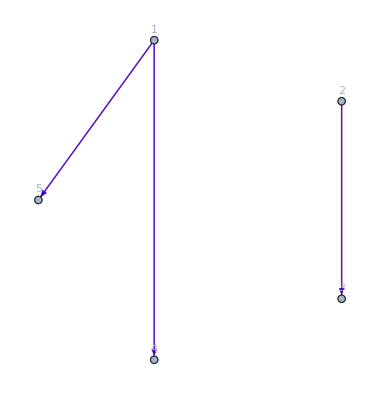
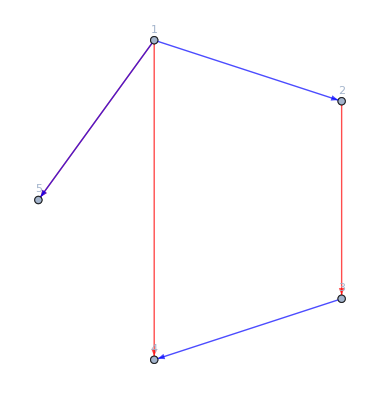
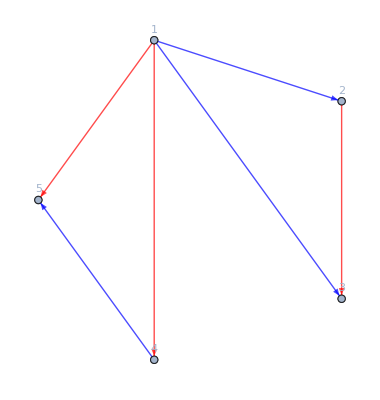
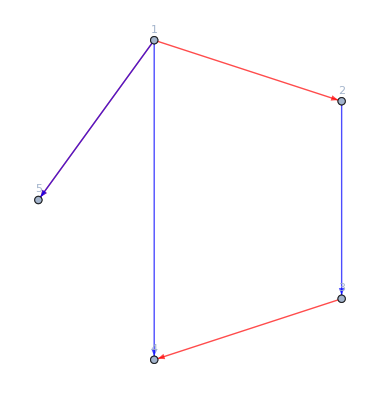
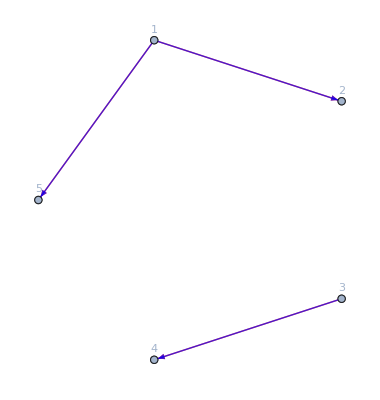
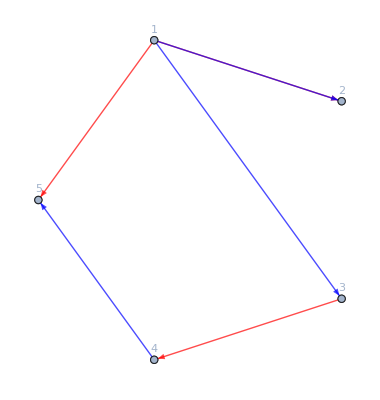
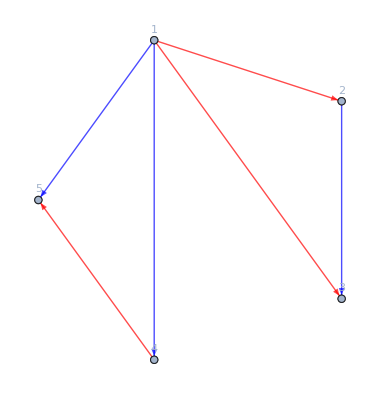
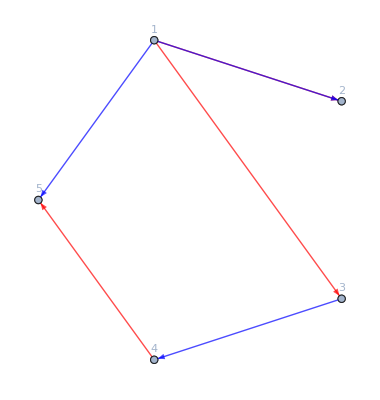
Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

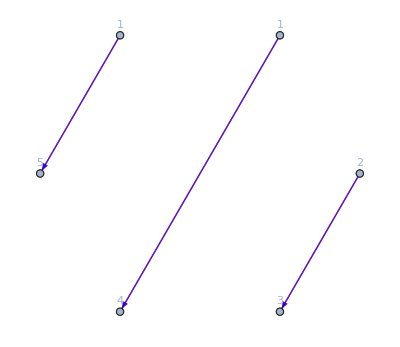
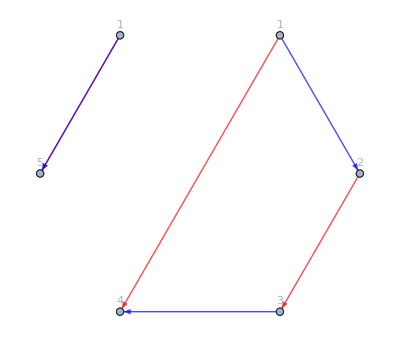
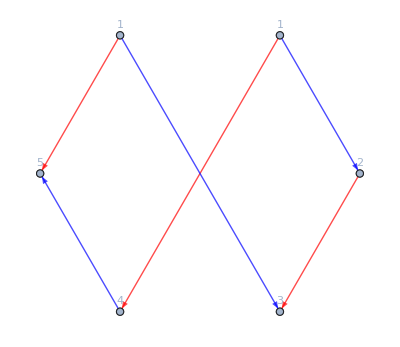
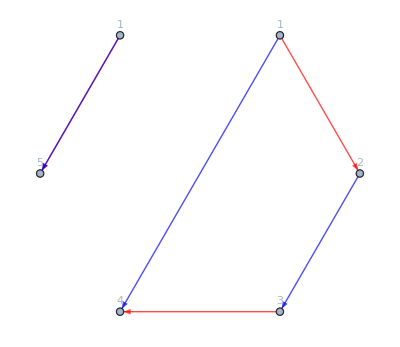
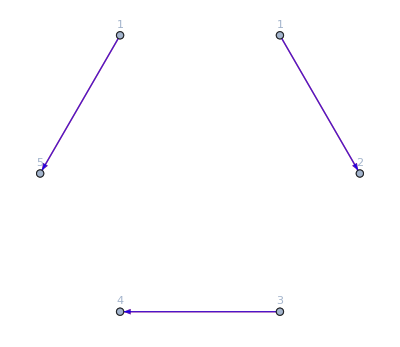
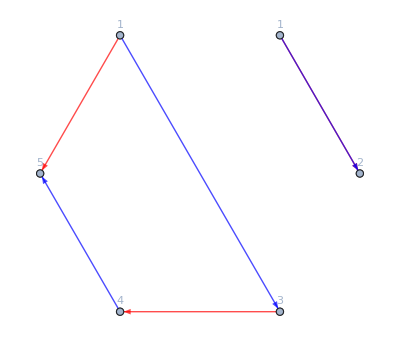
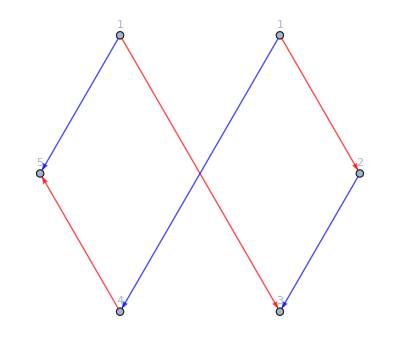
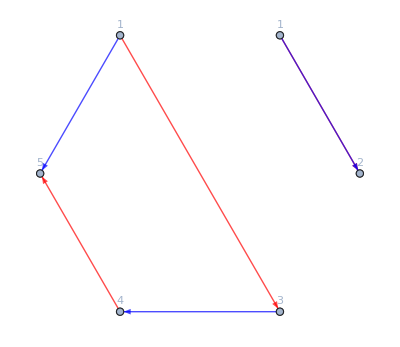
Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True,True}

True

Conditions:  {True,False}

True

Conditions:  {False,False}

False

Conditions:  {False,True}

True

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Conditions:  {False,False}

False

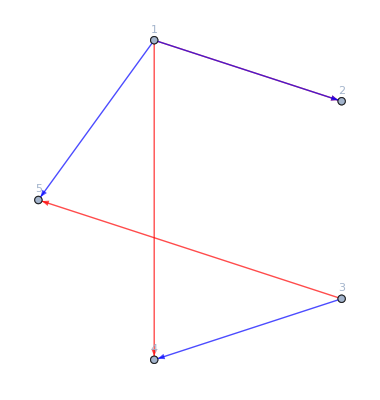
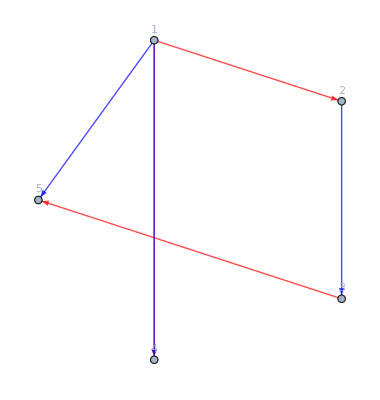
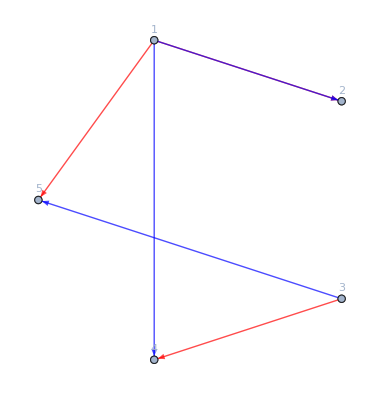
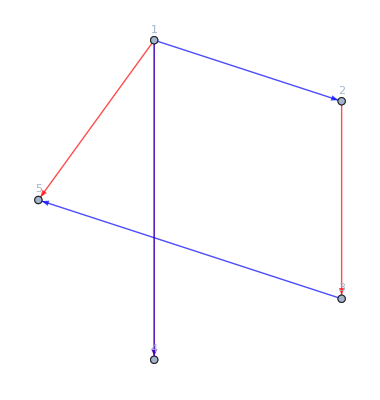
Extra momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Extra momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs:  {-Graphics-,-Graphics-}

Momenta:  {0,1,0,0,0}

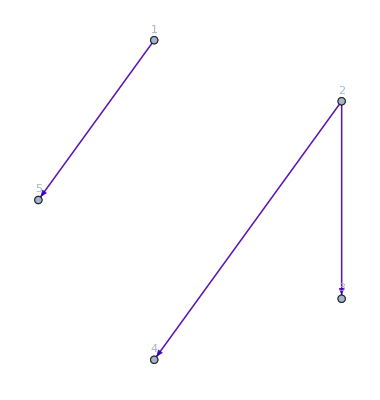
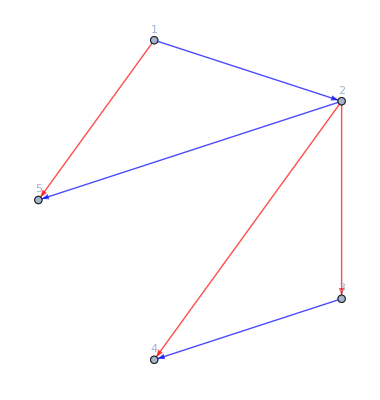
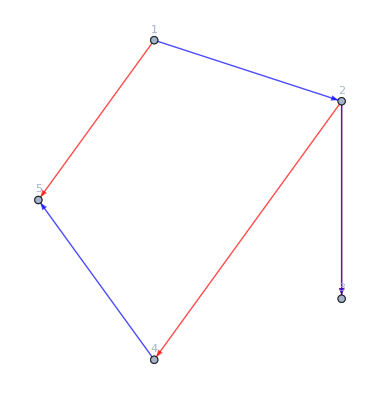
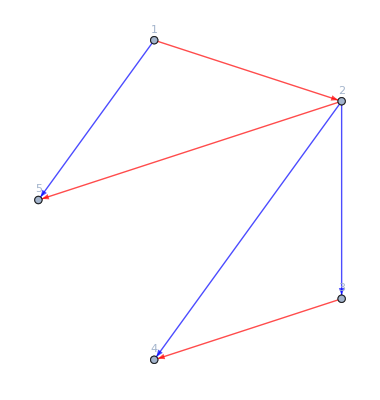
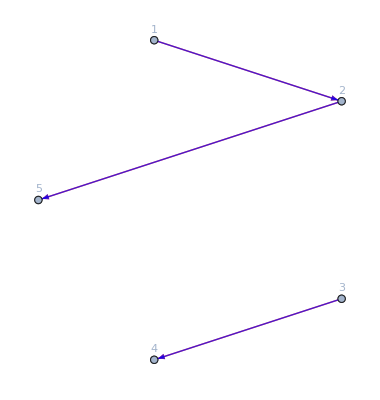
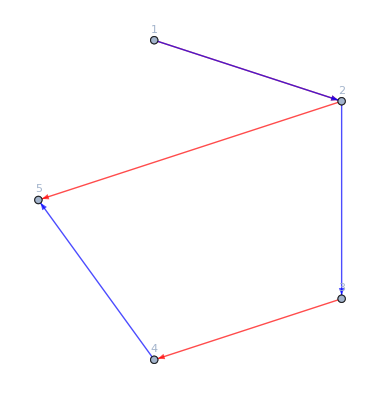
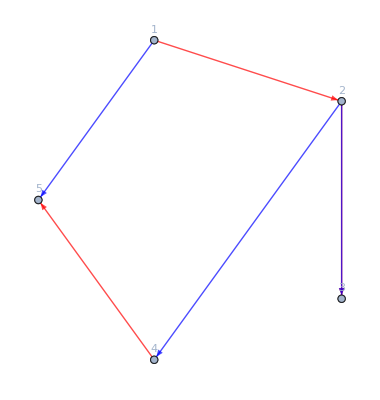
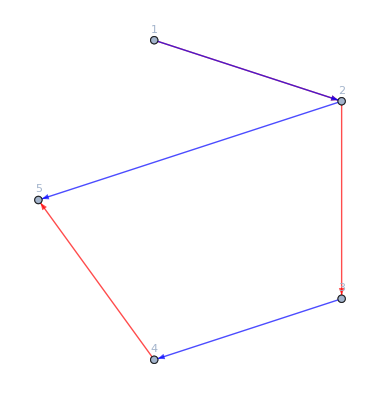
Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

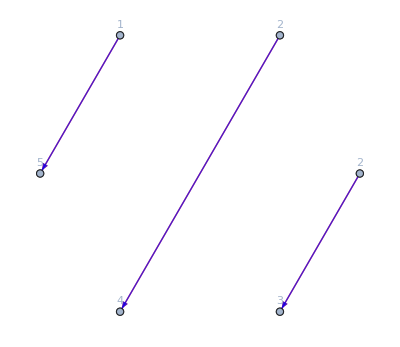
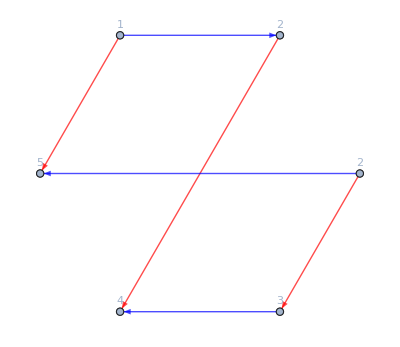
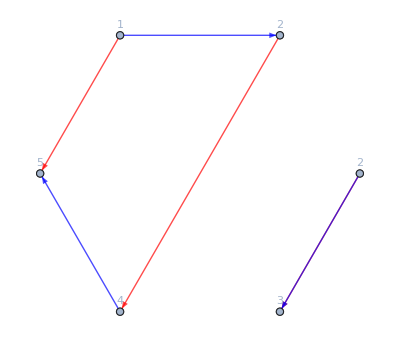
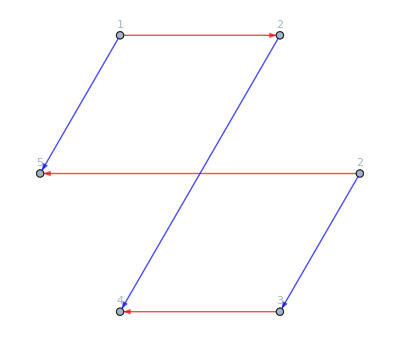
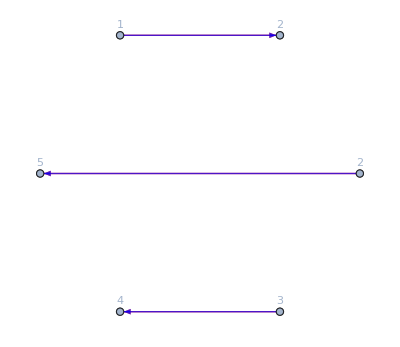
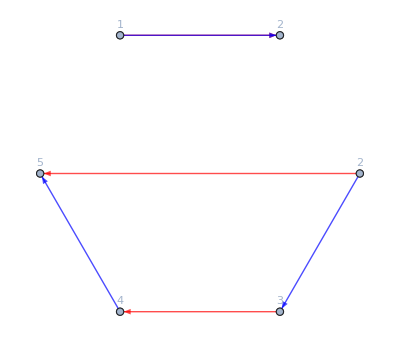
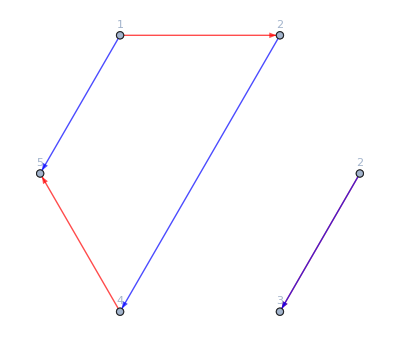
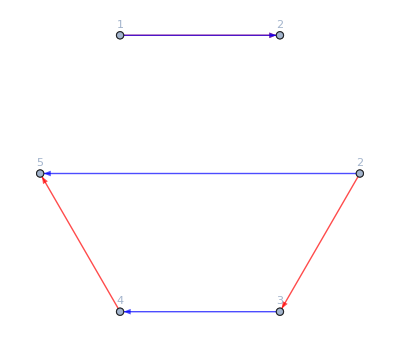
Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Extra massive momentum conservation:  {-Graphics-}

Extra massive momentum conservation:  {}

Graphs:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Momenta:  {0,0,1,0,0}

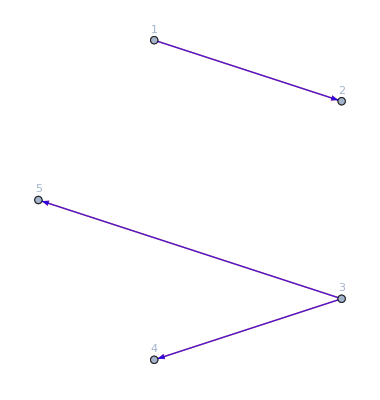
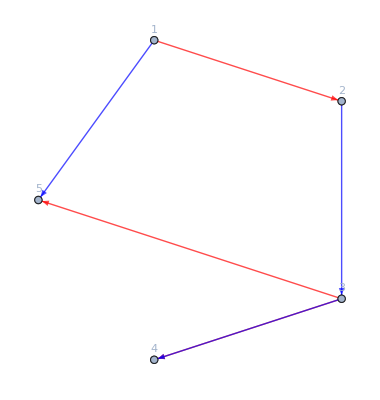
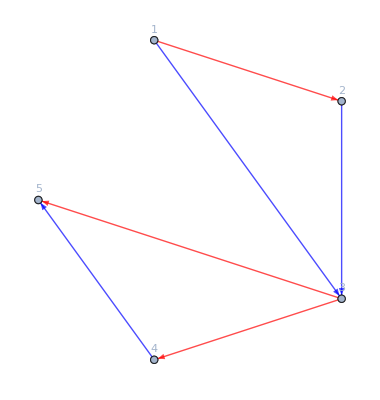
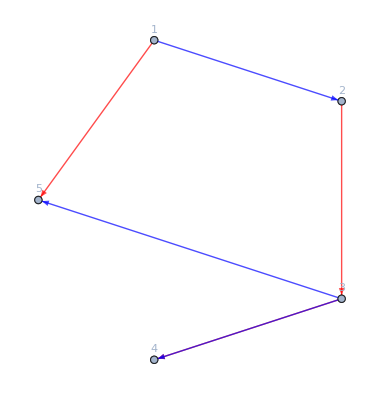
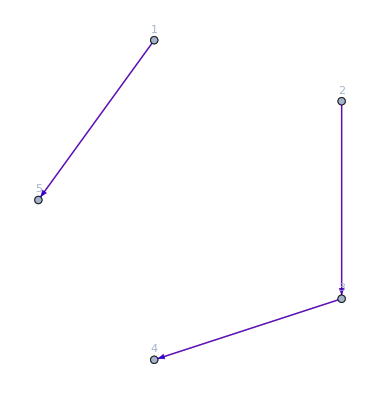
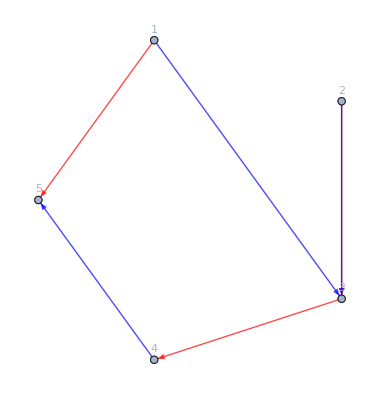
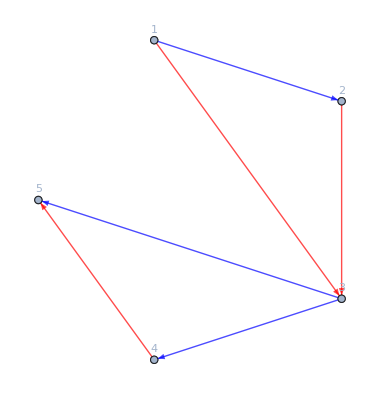
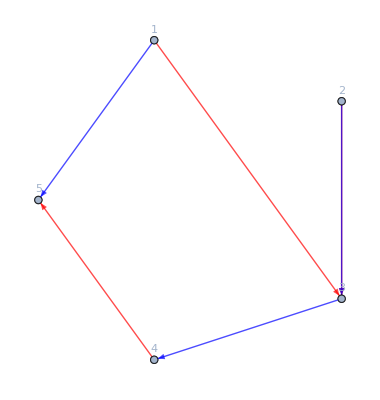
Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

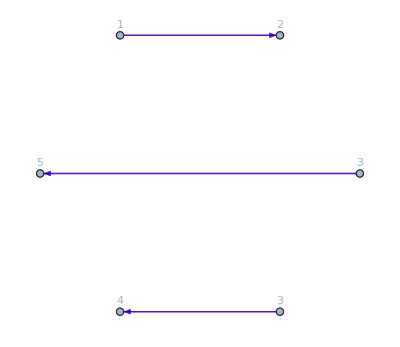
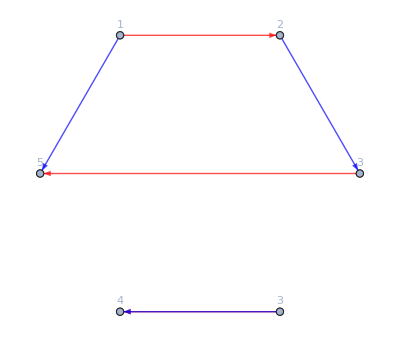
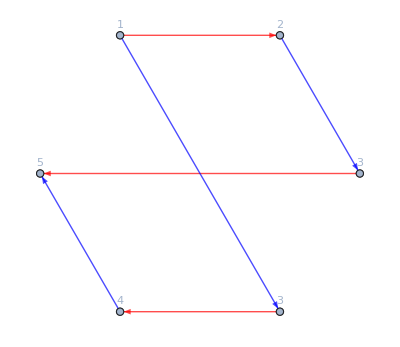
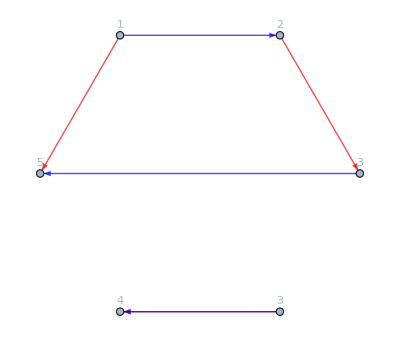
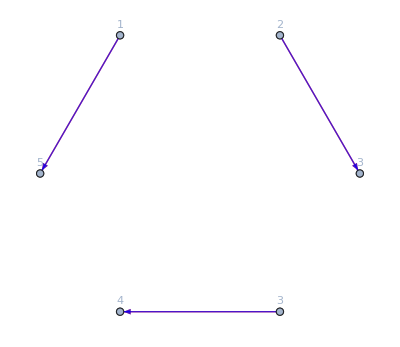
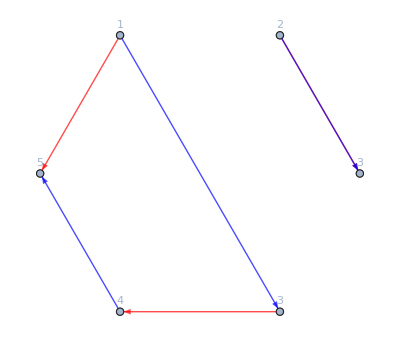
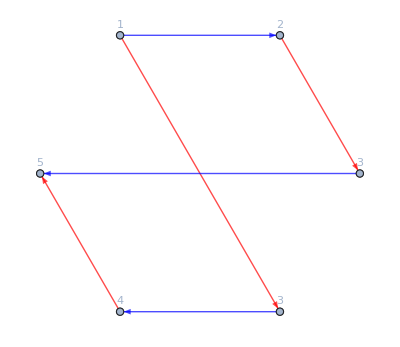
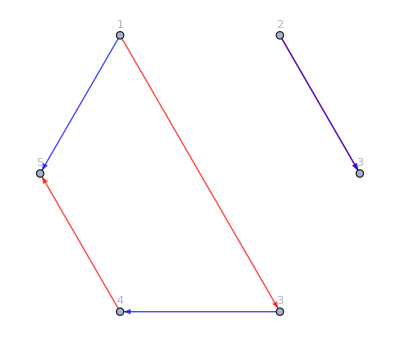
Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Graphs:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Momenta:  {0,0,0,1,0}

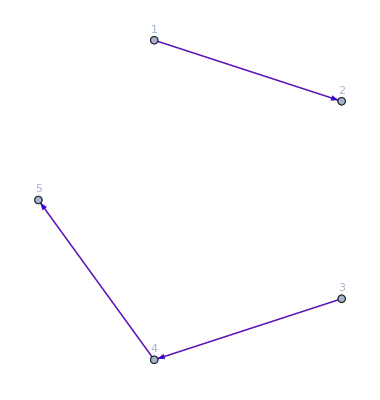
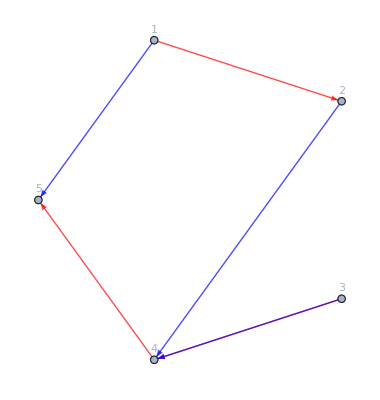
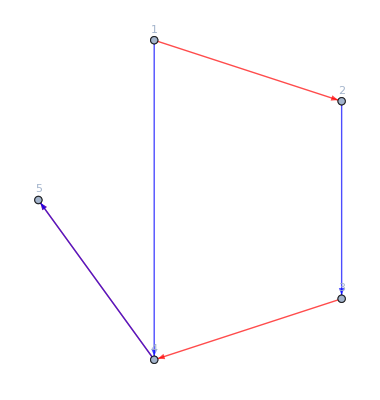
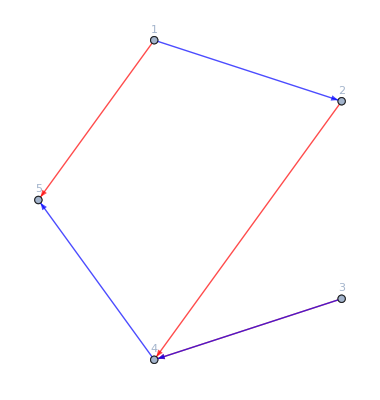
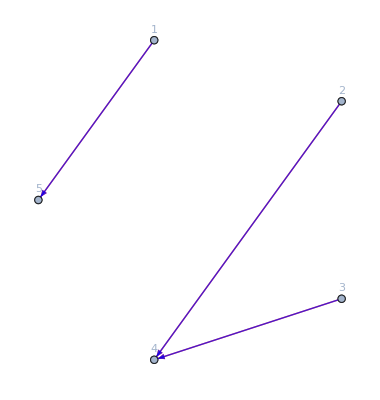
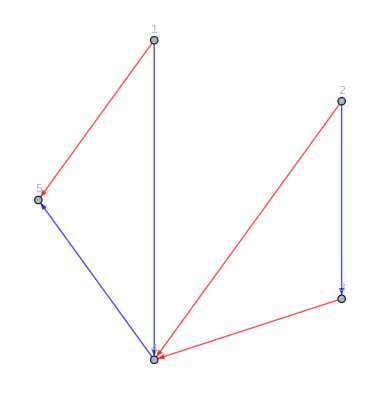
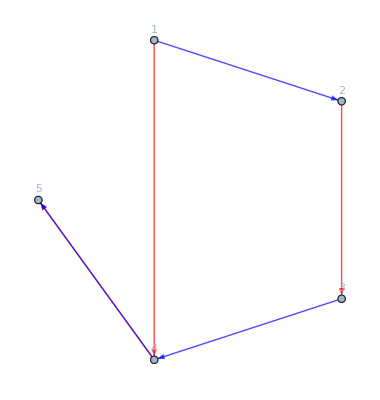
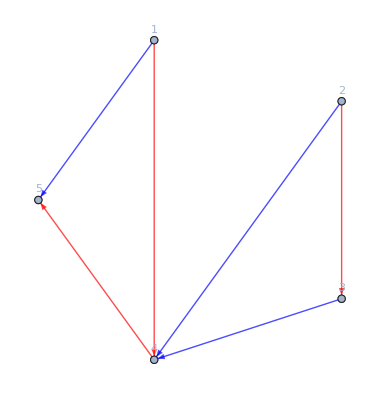
Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

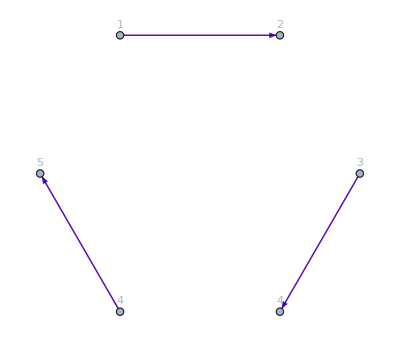
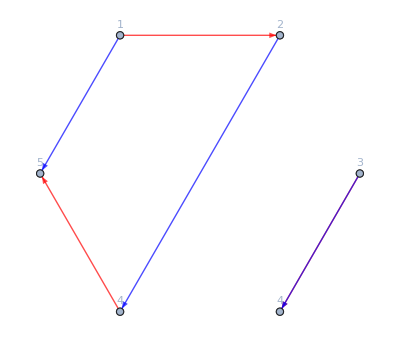
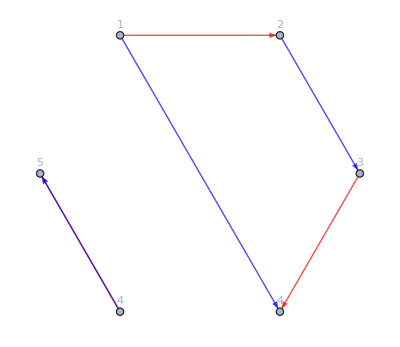
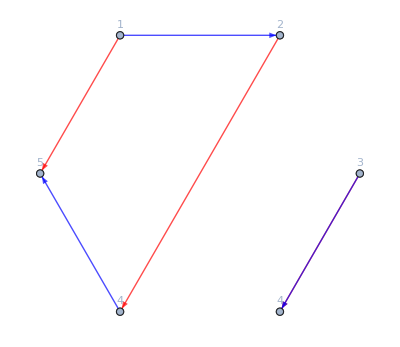
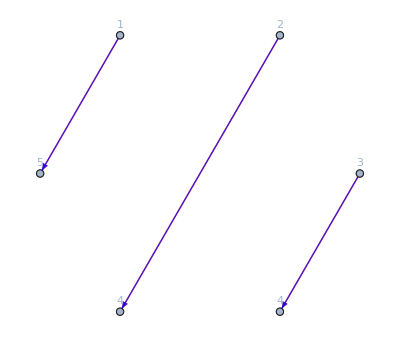
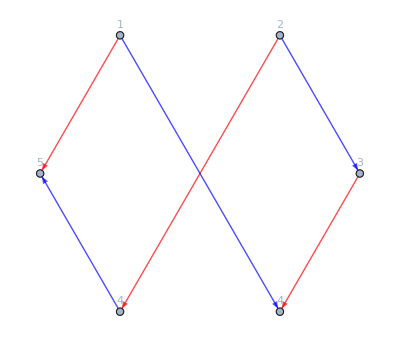
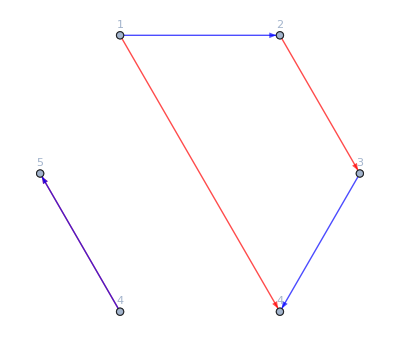
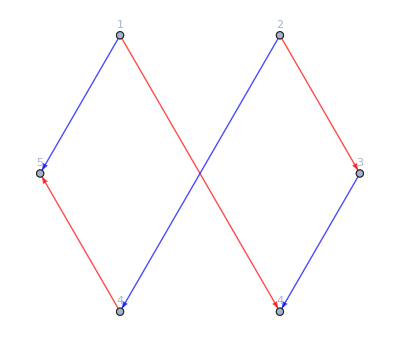
Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True}

True

Conditions:  {True}

True

Conditions:  {True}

True

Conditions:  {True}

True

Conditions:  {False}

False

Conditions:  {True}

True

Conditions:  {True}

True

Conditions:  {True}

True

Conditions:  {True}

True

Graphs:  {-Graphics-}

{-13 45 22p_1 15 34,-13 45 22p_1 13 45,-12 45 33p_2 12 45,-12 45 35p_2 12 34,-12 45 33p_2 15 24,-12 34 53p_2 12 45,-12 34 55p_2 12 34,-12 34 53p_2 15 24,-15 24 35p_2 12 34,-15 24 33p_2 15 24,-12 35 44p_3 12 35,-12 35 44p_3 15 23,12 35 41p_3 23 45,-15 23 44p_3 12 35,-15 23 44p_3 15 23,15 23 41p_3 23 45,23 45 14p_3 12 35,23 45 14p_3 15 23,-23 45 11p_3 23 45,-15 34 22p_4 15 34}

```mathematica
UniformMassStructres[6,"MomentumConservation"->True,"Echos"->True][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1,0}]
```

```mathematica
Length/@(UniformMassStructres[12,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,1,0},{2,1,0},{3,1},{4,-1}}]))
(Permutations[{{1,1,0},{2,1,0},{3,1},{4,-1}}]);
{%[[#]],%%[[#]]}&@-9
```

{5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}

{{{3,1},{2,1,0},{4,-1},{1,1,0}},5}

```mathematica
UniformMassStructres[8,"MomentumConservation"->True][{1,1},{2,1,0},{3,-1},{4,1,0}]
```

{-12 31p_2 34p_2 41p_2 12,24 31p_2 33p_2 34p_2 12,-12 34 11p_2 31p_2 12 14}

```mathematica
UniformMassStructres[9,"MomentumConservation"->True][{1,2,0},{2,1,0},{3,1,0},{4,1}]
%//Length
```

{-(11p_2)^2 22p_1 34p_2 43,14p_2 11p_2 22p_1 33p_2 41,-12 14p_2 33p_2 41 12 p_2p_3,-12 12p_3 33p_2 41^2 p_2p_3}

4

```mathematica
IndependentSpinStructres[9,"MomentumConservation"->True][{1,2,0},{2,1,0},{3,1,0},{4,1}]
```

{-(11p_2)^2 22p_1 34p_2 43,14p_2 11p_2 22p_1 33p_2 41,-12 14p_2 33p_2 41 12 p_2p_3,-12 12p_3 33p_2 41^2 p_2p_3,-12 (14p_2)^2 33p_2 1 12,-13 14p_2 11p_2 22p_1 1 43,-11p_3p_2 12 33p_2 1 41 42,-12 13 14p_2 13p_2 1^2 42,12p_2p_1 12 33p_2 2 41^2,-12p_2p_1 12 31p_2 2 41 43,12^2 33p_2 2 41^2 p_2p_3,-12^2 11p_2 34p_2 1 2 43,12^2 14p_2 33p_2 1 2 41,-12^2 13 14p_2 1^2 2 43,-12 11p_2 (34p_2)^2 3 12,-13p_3p_2 12 34p_2 3 41 12,13p_3p_2 23 12p_3 3 41^2,-12 13 14p_2 34p_2 1 3 12,-13p_3p_2 12 13 1 3 41 42,-12 13^2 14p_2 1^2 3 42,12^2 34p_2 31p_2 2 3 41,-13p_3p_2 12 23 2 3 41^2,12^2 13 34p_2 1 2 3 41,11p_2 22p_1 31p_2 1 41 43,-11p_2 22p_1 33p_2 1 41^2,12 33p_2 1 41^2 12 p_2p_3,-11p_3 22p_3 33p_2 1 41^2,-23p_1p_2 12 2 1 41^2 13,12 21p_3 33p_2 2 1 41^2,12 34p_2 31p_2 3 1 41 12,-13p_3p_2 23 3 1 41^2 12,12 23 31p_2 2 3 1 41^2,-23^2 11p_3 2 3 1 41^2,-22p_1 31p_2 1^2 41^2 13,21p_3 33p_2 1^2 41^2 12,-23 21p_3 2 1^2 41^2 13,23 31p_2 3 1^2 41^2 12,-(14p_2)^2 33p_2 2 12^2,13 14p_2 2 43 12 12p_2p_1,-11p_3p_2 33p_2 2 41 42 12,-(12p_3)^2 33p_2 2 41^2,-13 14p_2 13p_2 1 2 42 12,-13 13p_2 12p_3 1 2 41 42,-13 14p_2 34p_2 3 2 12^2,-13p_3p_2 13 3 2 41 42 12,-13^2 14p_2 1 3 2 42 12,-13^2 12p_3 1 3 2 41 42,-11p_2 34p_2 1 2 43 12^2,14p_2 33p_2 1 2 41 12^2,12p_3 33p_2 1 2 41^2 12,13 34p_2 3 1 2 41 12^2,31p_2 1^2 2 41 43 12^2,-33p_2 1^2 2 41^2 12^2,-(11p_2)^2 22p_1 3 43^2,-(13p_2)^2 22p_1 3 41^2,11p_2 13p_2 22p_1 3 41 43,-12 13p_2 3 41^2 23p_3p_2,12 (13p_2)^2 1 3 41 42,-12 14p_2 13p_2 1 3 43 12,-12 13p_2 23p_1 2 3 41^2,-12p_2p_1 12 2 3 41 43 13,-12^2 11p_2 1 2 3 43^2,12^2 13p_2 1 2 3 41 43,11p_2 22p_1 1 3 41 43 13,-13p_2 22p_1 1 3 41^2 13,-12 1 3 41^2 23 13p_3p_2,-12 23p_1 2 1 3 41^2 13,-22p_1 1^2 3 41^2 13^2,-21p_3 1^2 3 41^2 13 23,-14p_2 13p_2 2 3 43 12^2,(13p_2)^2 2 3 41 42 12,-13p_2 12p_3 2 3 41^2 23,-11p_2 1 2 3 43^2 12^2,13p_2 1 2 3 41^2 12 23,13p_2 1 2 3 41 43 12^2,-11p_3 1 2 3 41^2 23^2,1^2 2 3 41 43 12^2 13,1^2 2 3 41^2 12 13 23}

```mathematica
UniformMassStructres[9,"MomentumConservation"->True][{4,1},{3,1,0},{1,2,0},{2,1,0}]//Length
```

4

```mathematica
UniformMassStructres[7,"MomentumConservation"->True][{1,2,0},{2,1,0},{3,1,0},{4,1}]
UniformMassStructres[7,"MomentumConservation"->True][{1,1},{2,1,0},{3,1,0},{4,2,0}]
```

{-12 11p_2 34p_2 43 12,12 14p_2 33p_2 41 12,12 12p_3 33p_2 41^2}

{-24 34p_2 41p_2 12 34,24 33p_2 44p_2 12 14,14 24 31p_2 12 14 34}

```mathematica
IndependentSpinStructres[17,"MomentumConservation"->True][{4,2,0},{3,1,0},{2,1,0},{1,1}]//Length
IndependentSpinStructres[17,"MomentumConservation"->True][{1,1},{2,1,0},{3,1,0},{4,2,0}]//Length
```

258

258

```mathematica
list={{1,1},{2,1,0},{3,1,0},{4,2,0}}

massivespins=Table[If[Length[i]==2(*if massless*),0,i[[2]]],{i,list}];(*a list of all the spins, for massless particles is zero*)
x= Table[If[Length[i]==2,0,i[[3]]],{i,list}]; (*a list of all the transversality, for massless particles is zero*)
momenta=9-Sum[i[[2]],{i,list}]; (*the number of momenta insertions in the structures*)
n=Length[list];

massivespins=Tuples[(Range[-#,#,1])&/@massivespins]; (*all the possible transversality combinations for the spins*)
massivespins={Abs[#-x],#}&/@massivespins;(*for each transversality configuration gives the difference (in absolute value, it does not distinguish between m and OverTilde[m])*)
massivespins={
(*Product[Mass[list[[i,1]]]^#[[1,i]],{i,n}],*)(*the masses to compensate the mass dimensions*)
Total@#[[1]],(*the total difference*)
Table[If[Length[list[[i]]]==2,list[[i]],{list[[i,1]],list[[i,2]],#[[2,i]]}],{i,n}](*if massive, changes the original transversalities in all their possible combinations*)
}&/@massivespins
If[Length[UniformMassStructres[9-#[[1]]][Sequence@@#[[2]]]]==Length[UniformMassStructres[9-#[[1]]][Sequence@@Reverse@#[[2]]]],Nothing,#]&/@massivespins
```

{{1,1},{2,1,0},{3,1,0},{4,2,0}}

{{4,{{1,1},{2,1,-1},{3,1,-1},{4,2,-2}}},{3,{{1,1},{2,1,-1},{3,1,-1},{4,2,-1}}},{2,{{1,1},{2,1,-1},{3,1,-1},{4,2,0}}},{3,{{1,1},{2,1,-1},{3,1,-1},{4,2,1}}},{4,{{1,1},{2,1,-1},{3,1,-1},{4,2,2}}},{3,{{1,1},{2,1,-1},{3,1,0},{4,2,-2}}},{2,{{1,1},{2,1,-1},{3,1,0},{4,2,-1}}},{1,{{1,1},{2,1,-1},{3,1,0},{4,2,0}}},{2,{{1,1},{2,1,-1},{3,1,0},{4,2,1}}},{3,{{1,1},{2,1,-1},{3,1,0},{4,2,2}}},{4,{{1,1},{2,1,-1},{3,1,1},{4,2,-2}}},{3,{{1,1},{2,1,-1},{3,1,1},{4,2,-1}}},{2,{{1,1},{2,1,-1},{3,1,1},{4,2,0}}},{3,{{1,1},{2,1,-1},{3,1,1},{4,2,1}}},{4,{{1,1},{2,1,-1},{3,1,1},{4,2,2}}},{3,{{1,1},{2,1,0},{3,1,-1},{4,2,-2}}},{2,{{1,1},{2,1,0},{3,1,-1},{4,2,-1}}},{1,{{1,1},{2,1,0},{3,1,-1},{4,2,0}}},{2,{{1,1},{2,1,0},{3,1,-1},{4,2,1}}},{3,{{1,1},{2,1,0},{3,1,-1},{4,2,2}}},{2,{{1,1},{2,1,0},{3,1,0},{4,2,-2}}},{1,{{1,1},{2,1,0},{3,1,0},{4,2,-1}}},{0,{{1,1},{2,1,0},{3,1,0},{4,2,0}}},{1,{{1,1},{2,1,0},{3,1,0},{4,2,1}}},{2,{{1,1},{2,1,0},{3,1,0},{4,2,2}}},{3,{{1,1},{2,1,0},{3,1,1},{4,2,-2}}},{2,{{1,1},{2,1,0},{3,1,1},{4,2,-1}}},{1,{{1,1},{2,1,0},{3,1,1},{4,2,0}}},{2,{{1,1},{2,1,0},{3,1,1},{4,2,1}}},{3,{{1,1},{2,1,0},{3,1,1},{4,2,2}}},{4,{{1,1},{2,1,1},{3,1,-1},{4,2,-2}}},{3,{{1,1},{2,1,1},{3,1,-1},{4,2,-1}}},{2,{{1,1},{2,1,1},{3,1,-1},{4,2,0}}},{3,{{1,1},{2,1,1},{3,1,-1},{4,2,1}}},{4,{{1,1},{2,1,1},{3,1,-1},{4,2,2}}},{3,{{1,1},{2,1,1},{3,1,0},{4,2,-2}}},{2,{{1,1},{2,1,1},{3,1,0},{4,2,-1}}},{1,{{1,1},{2,1,1},{3,1,0},{4,2,0}}},{2,{{1,1},{2,1,1},{3,1,0},{4,2,1}}},{3,{{1,1},{2,1,1},{3,1,0},{4,2,2}}},{4,{{1,1},{2,1,1},{3,1,1},{4,2,-2}}},{3,{{1,1},{2,1,1},{3,1,1},{4,2,-1}}},{2,{{1,1},{2,1,1},{3,1,1},{4,2,0}}},{3,{{1,1},{2,1,1},{3,1,1},{4,2,1}}},{4,{{1,1},{2,1,1},{3,1,1},{4,2,2}}}}

{}

```mathematica
UniformMassStructres[8][{1,1},{2,1,0},{3,1,-1},{4,2,0}]//Length
UniformMassStructres[8][Sequence@@Reverse@{{1,1},{2,1,0},{3,1,-1},{4,2,0}}]//Length
```

3

3

```mathematica
UniformMassStructres[9,"MomentumConservation"->True][{1,2,0},{2,1,0},{3,1,0},{4,1}]//Length
UniformMassStructres[9,"MomentumConservation"->True][{1,1},{2,1,0},{3,1,0},{4,2,0}]//Length
```

4

4

```mathematica
UniformMassStructres[6,"MomentumConservation"->True][{1,2,0},{2,1,1},{3,1,0},{4,1}]//Length
UniformMassStructres[6,"MomentumConservation"->True(*,"Echos"->True*)][{1,1},{2,1,1},{3,1,0},{4,2,0}]//Length
```

3

3

```mathematica
UniformMassStructres[7,"MomentumConservation"->True(*,"Echos"->True*)][{1,2,0},{2,1,0},{3,1,0},{4,1}]//Length
UniformMassStructres[7,"MomentumConservation"->True(*,"Echos"->True*)][{1,1},{2,1,0},{3,1,0},{4,2,0}]//Length
```

3

3

```mathematica
UniformMassStructres[6,"MomentumConservation"->True(*,"Echos"->True*)][{1,1},{2,1,1},{3,1,0},{4,2,2}]
UniformMassStructres[6,"MomentumConservation"->True(*,"Echos"->True*)][{1,2,2},{2,1,1},{3,1,0},{4,1}]
```

{-33p_2 14^2 24^2,-34p_2 12 14 24 34}

{31p_2 41 43 12^2,-33p_2 41^2 12^2}

```mathematica
Length/@(UniformMassStructres[9,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,2,0},{2,1,0},{3,1,0},{4,1}}]))
```

{4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}

```mathematica
UniformMassStructres[11,"MomentumConservation"->True][{1,2,0},{2,1},{3,1},{4,1}]//Length
UniformMassStructres[11,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2,0}]//Length
```

5

5

```mathematica
UniformMassStructres[10,"MomentumConservation"->True][{1,1,0},{2,1},{3,1,0},{4,1}]//Length
UniformMassStructres[10,"MomentumConservation"->True(*,"Echos"->True*)][{1,1,0},{2,1},{3,1},{4,1,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True(*,"Echos"->True*)][{1,1},{2,1},{3,1,0},{4,1,0}]//Length
```

5

5

5

```mathematica
If[Length[UniformMassStructres[10,"MomentumConservation"->True][Sequence@@#]]==56,#,Nothing]&/@Permutations[{{1,2,0},{2,1},{3,1,0},{4,1},{5,2}}]
```

{}

```mathematica
UniformMassStructres[10,"MomentumConservation"->True][{1,1},{2,1},{3,2},{4,2,0},{5,1,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,1},{2,2,0},{3,2},{4,1},{5,1,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,1},{2,2,0},{3,1,0},{4,1},{5,2}]//Length
```

47

47

47

```mathematica
UniformMassStructres[12,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,2,0},{4,2,0}]//Length
UniformMassStructres[12,"MomentumConservation"->True][{1,1,0},{2,2,0},{3,1,0},{4,2,0}]//Length
```

7

7

```mathematica
UniformMassStructres[8,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,2,0},{4,2,0}]//Length
UniformMassStructres[8,"MomentumConservation"->True][{1,1,0},{3,2,0},{2,1,0},{4,2,0}]//Length
```

5

5

```mathematica
UniformMassStructres[6,"MomentumConservation"->True][{1,1,0},{2,0,0},{3,2,0},{4,2,0}]//Length
UniformMassStructres[6,"MomentumConservation"->True][{2,0,0},{3,2,0},{1,1,0},{4,2,0}]//Length
```

3

3

```mathematica
Length/@(UniformMassStructres[10,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,3,0},{2,2,0},{3,2,0},{4,0}}]))
```

{6,6,6,6,10,10,6,6,6,6,10,9,6,6,6,6,10,9,6,6,6,6,6,6}

```mathematica
Length/@(UniformMassStructres[10,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,3,0},{2,0,0},{3,2,0},{4,2,0}}]))
```

{10,10,6,6,6,6,6,6,6,6,6,6,6,6,10,9,6,6,6,6,10,9,6,6}

```mathematica
Length/@(UniformMassStructres[10,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,3,0},{2,1,0},{3,2,0},{4,2,0}}]))
If[Length[UniformMassStructres[10,"MomentumConservation"->True][Sequence@@#]]==5,#,Nothing]&/@Permutations[{{1,3,0},{2,1,0},{3,2,0},{4,2,0}}]
```

{10,10,6,7,6,7,6,6,6,5,6,5,6,6,10,9,7,6,6,6,10,9,7,6}

{{{2,1,0},{3,2,0},{4,2,0},{1,3,0}},{{2,1,0},{4,2,0},{3,2,0},{1,3,0}}}

```mathematica
Length/@(UniformMassStructres[6,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,1,0},{2,0,0},{3,2,0},{4,2,0}}]))
If[Length[UniformMassStructres[6,"MomentumConservation"->True][Sequence@@#]]==4,#,Nothing]&/@Permutations[{{1,1,0},{2,0,0},{3,2,0},{4,2,0}}]
```

{4,4,3,3,3,3,3,3,3,3,3,3,3,3,4,4,3,3,3,3,4,4,3,3}

{{{1,1,0},{2,0,0},{3,2,0},{4,2,0}},{{1,1,0},{2,0,0},{4,2,0},{3,2,0}},{{3,2,0},{2,0,0},{1,1,0},{4,2,0}},{{3,2,0},{2,0,0},{4,2,0},{1,1,0}},{{4,2,0},{2,0,0},{1,1,0},{3,2,0}},{{4,2,0},{2,0,0},{3,2,0},{1,1,0}}}

```mathematica
IndependentSpinStructres[6,"MomentumConservation"->True][{1,1,0},{2,0,0},{3,2,0},{4,2,0}]
IndependentSpinStructres[4,"MomentumConservation"->True][{1,1,0},{2,0,0},{3,1,0},{4,1,0}]
```

{-34^2 11p_2 34^2,34^2 13p_2 14 34,14 34 31p_2 34^2,-14 34 33p_2 14 34,13 14 34 1 34^2,13 34^2 3 14 34,14 34^2 4 13 34,34^2 1 13 14 34,14 34 3 13 34^2,13 34 4 14 34^2}

{-34 11p_2 34,34 13p_2 14,14 31p_2 34,-14 33p_2 14,13 14 1 34,13 34 3 14,14 34 4 13,34 1 13 14,14 3 13 34,13 4 14 34}

```mathematica
Length/@(UniformMassStructres[4,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,1,0},{2,0,0},{3,1,0},{4,1,0}}]))
```

{4,4,3,3,3,3,3,3,3,3,3,3,3,3,4,4,3,3,3,3,4,4,3,3}

3

Momenta:  {1,0,0,0}

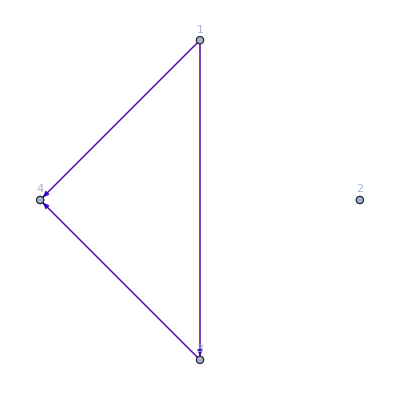
Graphs before momentum conservation:  {-Graphics-}

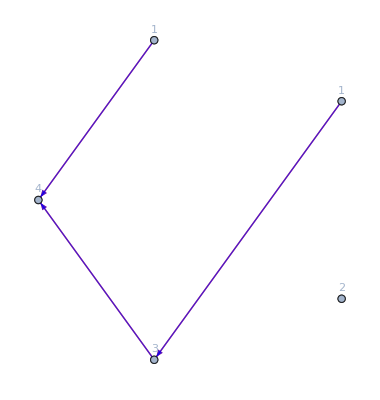
Graphs with momenta:  {-Graphics-}

Conditions:  {True,True}

True

Extra momentum conservatin:  {-Graphics-,-Graphics-,-Graphics-}

Extra momentum conservatin:  {}

No graph survided.

Momenta:  {0,1,0,0}

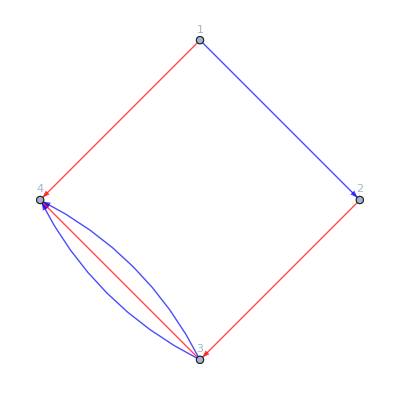
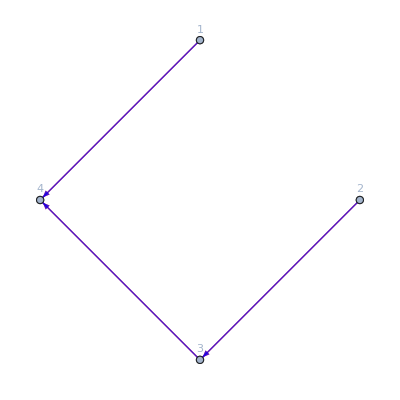
Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

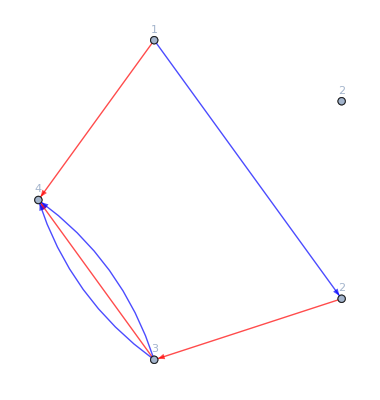
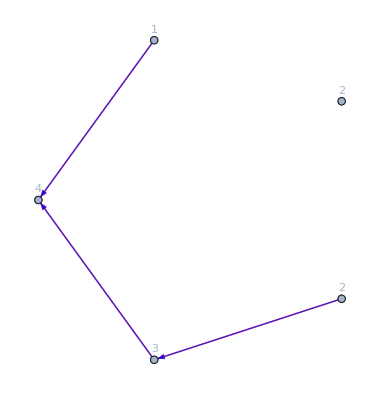
Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Graphs:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Momenta:  {0,0,1,0}

Graphs before momentum conservation:  {-Graphics-}

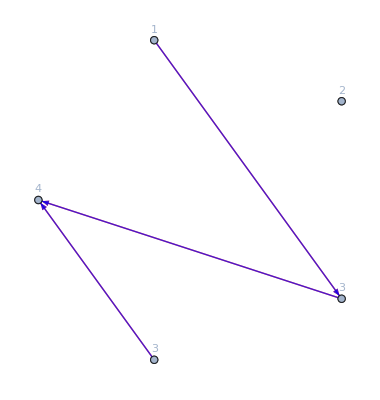
Graphs with momenta:  {-Graphics-}

Conditions:  {True}

True

No graph survided.

4

Momenta:  {1,0,0,0}

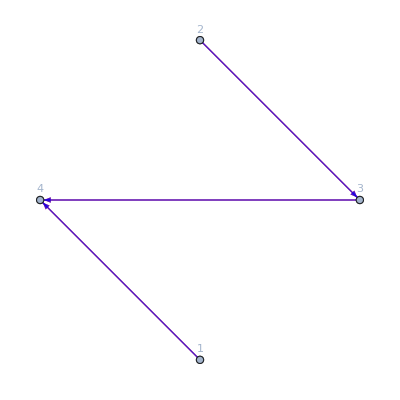
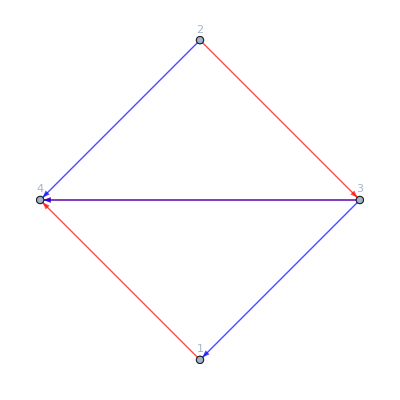
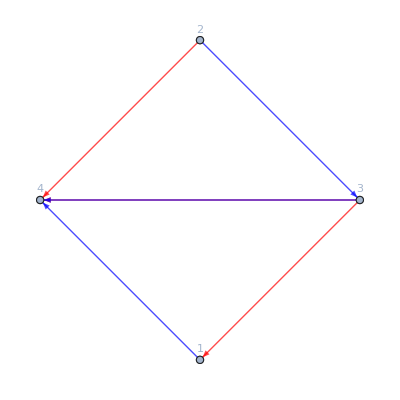
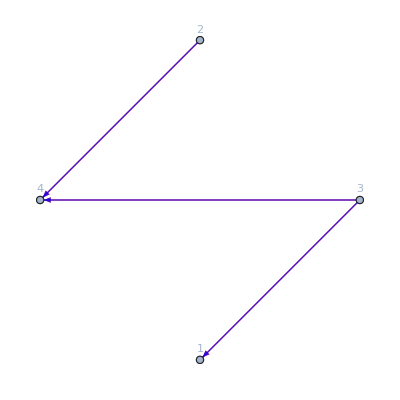
Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Extra momentum conservatin:  {-Graphics-,-Graphics-}

Extra momentum conservatin:  {-Graphics-,-Graphics-}

Graphs:  {-Graphics-,-Graphics-}

Momenta:  {0,1,0,0}

Graphs before momentum conservation:  {-Graphics-}

Graphs with momenta:  {-Graphics-}

Conditions:  {}

False

Graphs:  {-Graphics-}

Momenta:  {0,0,1,0}

Graphs before momentum conservation:  {-Graphics-}

Graphs with momenta:  {-Graphics-}

Conditions:  {True}

True

No graph survided.

3

```mathematica
UniformMassStructres[6,"MomentumConservation"->True][{3,2,0},{1,1,0},{4,2,0},{2,0,0}]//Length
UniformMassStructres[6,"MomentumConservation"->True,"Echos"->True][{1,1,0},{2,0,0},{3,2,0},{4,2,0}]//Length
UniformMassStructres[6,"MomentumConservation"->True,"Echos"->True][{2,0,0},{3,2,0},{1,1,0},{4,2,0}]//Length
```

```mathematica
If[Length[UniformMassStructres[10,"MomentumConservation"->True][Sequence@@#]]==10,#,Nothing]&/@Permutations[{{1,1,0},{2,1,0},{3,2,0},{4,2,0}}]
```

{}

```mathematica
UniformMassStructres[10,"MomentumConservation"->True][{1,2,0},{2,1},{3,1,0},{4,1},{5,2}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,1},{2,2},{3,1},{4,2,0},{5,1,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,1},{2,2,0},{3,1,0},{4,1},{5,2}]//Length
```

47

47

47

```mathematica
UniformMassStructres[6,"MomentumConservation"->True][{1,1,0},{2,2,0},{3,1,0},{a,1,0},{b,2},{4,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,2},{2,2,0},{3,1,0},{a,1,0},{b,1,0},{4,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,2},{2,1,0},{3,1,0},{a,2,0},{b,1,0},{4,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,2},{2,0},{3,1,0},{a,2,0},{b,1,0},{4,1,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,2},{2,0},{3,1,0},{a,1,0},{b,1,0},{4,2,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,1,0},{2,0},{3,1,0},{a,2},{b,1,0},{4,2,0}]//Length
```

0

240

240

240

«1 more identical outputs»

236

```mathematica
UniformMassStructres[13,"MomentumConservation"->True][{1,1,0},{2,2,1},{3,1,0},{4,0}]//Length
UniformMassStructres[13,"MomentumConservation"->True][{1,1,0},{2,2,1},{3,0},{4,1,0}]//Length
UniformMassStructres[13,"MomentumConservation"->True][{1,1,0},{2,0},{3,2,1},{4,1,0}]//Length
```

6

6

6

```mathematica
UniformMassStructres[8,"MomentumConservation"->True][{1,1},{2,1,1},{3,1,0},{4,1,1},{5,1}]//Length
UniformMassStructres[8,"MomentumConservation"->True(*,"Echos"->True*)][{1,1,1},{2,1},{3,1},{4,1,1},{5,1,0}]//Length
```

39

39

```mathematica
UniformMassStructres[9,"MomentumConservation"->True][{1,2},{2,1},{3,1},{4,1},{5,1},{6,2},{7,1}]//Length
UniformMassStructres[9,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2},{5,1},{6,1},{7,2}]//Length
```

50

50

```mathematica
Length/@(UniformMassStructres[21,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,2,1},{2,1,0},{3,1,0},{4,1,0}}]))
```

{10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}

```mathematica
UniformMassStructres[7,"MomentumConservation"->True,"Echos"->True][{1,2,1},{2,1,0},{3,1,0},{4,1,0}]//Length
UniformMassStructres[7,"MomentumConservation"->True,"Echos"->True][{1,1,0},{2,1,0},{3,1,0},{4,2,1}]//Length
```

Momenta:  {0,2,0,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {}

False

Conditions:  {}

False

Graphs:  {-Graphics-,-Graphics-}

Momenta:  {0,0,2,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True}

True

Conditions:  {True}

True

No graph survided.

Momenta:  {1,1,0,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {False,False}

False

Conditions:  {False,True}

True

Extra momentum conservatin:  {-Graphics-,-Graphics-}

Extra momentum conservatin:  {-Graphics-}

No graph survided.

Momenta:  {1,0,1,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True,True,False,True}

True

Conditions:  {False,True,True,True}

True

Extra momentum conservatin:  {-Graphics-,-Graphics-,-Graphics-}

Extra momentum conservatin:  {}

No graph survided.

Momenta:  {0,1,1,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True}

True

Conditions:  {False}

False

Conditions:  {True}

True

Conditions:  {True}

True

Graphs:  {-Graphics-}

3

Momenta:  {2,0,0,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True,False}

True

Conditions:  {True,False}

True

Extra momentum conservatin:  {-Graphics-,-Graphics-}

Extra momentum conservatin:  {-Graphics-}

No graph survided.

Momenta:  {0,2,0,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {}

False

Conditions:  {}

False

Graphs:  {-Graphics-,-Graphics-}

Momenta:  {0,0,2,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True}

True

Conditions:  {True}

True

No graph survided.

Momenta:  {1,1,0,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Extra momentum conservatin:  {-Graphics-,-Graphics-,-Graphics-}

Extra momentum conservatin:  {-Graphics-,-Graphics-,-Graphics-}

Graphs:  {-Graphics-}

Momenta:  {1,0,1,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True,True,False,False}

True

Conditions:  {True,True,False,False}

True

Conditions:  {True,True,False,False}

True

Conditions:  {True,True,False,False}

True

Extra momentum conservatin:  {}

Extra momentum conservatin:  {}

No graph survided.

Momenta:  {0,1,1,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True}

True

Conditions:  {True}

True

Conditions:  {True}

True

Conditions:  {True}

True

No graph survided.

3

```mathematica
UniformMassStructres[7,"MomentumConservation"->True][{1,2,0},{2,1},{3,1},{4,1}]
(*UniformMassStructres[6,"MomentumConservation"->True][{4,2,1},{2,1},{3,1},{1,1}]
UniformMassStructres[5,"MomentumConservation"->True][{4,2,2},{2,1},{3,1},{1,1}]
UniformMassStructres[6,"MomentumConservation"->True][{4,2,-1},{2,1},{3,1},{1,1}]//Length
UniformMassStructres[5,"MomentumConservation"->True][{4,2,-2},{2,1},{3,1},{1,1}]//Length*)
```

{21^2 23 24 21^2 34,21^2 23^2 24 21 41,21 31 23^3 41^2}

```mathematica
UniformMassStructres[7,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2,0}]
(*UniformMassStructres[6,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2,1}]
UniformMassStructres[5,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2,2}]
UniformMassStructres[6,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2,-1}]//Length
UniformMassStructres[5,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2,-2}]//Length*)
```

{24^2 12^2 23 24 34,24^2 12 14 23^2 24,14 24 12^2 14 23 34}

```mathematica
IndependentSpinStructres [7,"MomentumConservation"->True][{1,1},{2,1,0},{3,1,0},{4,0,0}]
```

{-12 11p_2 31p_2 12 13,-21p_3 33p_2 12 p_2p_3,12 33p_2 12 11p_2p_3,-(21p_3)^2 33p_2 2,-12 21p_3 31p_2 2 13,12 (31p_2)^2 3 12,-23p_3p_2 31p_2 3 12,-23 21p_3 31p_2 2 3,-13 11p_2 2 12^2 13,11p_2 33p_2 2 12^2,33p_2 2 12^2 p_2p_3,13 31p_2 3 2 12^2,-12 11p_2 3 12 13^2,21p_3 3 23 13p_3p_2,-12 3 12 13 13p_3p_2,-12 21p_3 2 3 13^2,13p_2 2 3 12^2 13,-2 3 12 23 13p_3p_2}

## Numerical evaluations and extra relations

```mathematica
GenerateKinematics[4,"Masses"->{2,3},"Echos"->True]
TraceChain[{2,3,4,1}]//NEvaluate
-AngleSquareChain[SpinorMV[$up][2,1],{3,4,1},SpinorMV[$up][2,2]]+AngleSquareChain[SpinorMV[$up][2,2],{3,4,1},SpinorMV[$up][2,1]]//NEvaluate
```

{1→{0,5},21→{2,0},22→{2,4},31→{3,4},32→{3,5},4→{1,3},1→{-31/50,-17/50},21→{11/8,-9/8},22→{9/40,3/40},31→{-4/3,-7/12},32→{-1/6,-2/3},4→{6/5,43/20},1→{{0,0},{-31/10,-17/10}},2→{{23/10,-12/5},{11/2,-9/2}},3→{{-7/2,1/4},{-6,-1/4}},4→{{6/5,43/20},{18/5,129/20}}}

629/16

629/16

### Case study: (1^(J=1), 2^(J=0), 3^(J=1), 4^(J=1))^(Δ=4)

```mathematica
IndependentSpinStructres[4,"MomentumConservation"->True][{1,1,0},{2,0,0},{3,1,0},{4,1,0}]
```

{-34 11p_2 34,34 13p_2 14,14 31p_2 34,-14 33p_2 14,13 14 1 34,13 34 3 14,14 34 4 13,34 1 13 14,14 3 13 34,13 4 14 34}

```mathematica
UniformMassStructres[4,"MomentumConservation"->True][{1,1,0},{2,0,0},{3,1,0},{4,1,0}]
UniformMassStructres[4,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,1,0},{4,0,0}]
```

{-34 11p_2 34,34 13p_2 14,-14 33p_2 14}

{-13 22p_1 13,-12 33p_2 12,-23 11p_3 23}

```mathematica
GenerateKinematics[4,"Masses"->{1,2,3,4}]
```

{11→{0,5},12→{4,5},21→{1,2},22→{3,4},31→{2,1},32→{4,1},41→{5,5},42→{5,3},11→{-37/60,-1/3},12→{73/500,-2/25},21→{1/10,11/10},22→{-1/6,7/6},31→{-41/30,7/15},32→{-31/10,7/5},41→{-1/25,0},42→{-22/75,-2/75},1→{{-37/15,-4/3},{-286/75,-19/15}},2→{{7/15,32/15},{11/15,31/15}},3→{{11/15,-14/15},{26/15,-14/15}},4→{{19/15,2/15},{101/75,2/15}}}

```mathematica
AngleSquareChain[SpinorMV[$up][1,1],{2},SpinorMV[$up][2,1]]
%//NEvaluate
MassTilde[2]*AngleB[SpinorMV[$up][1,1],SpinorMV[$up][2,1]]
%//NEvaluate
```

1121p_2

-35/32

1121 2

-35/32

```mathematica
GenerateKinematics[4,"Masses"->{1,2,3,4}]
IndependentSpinStructres[4,"MomentumConservation"->True][{1,1,0},{2,0,0},{3,1,0},{4,1,0}]
sum=Sum[%[[i]]*a[i],{i,Length@%}]
SpinorComponents[%]//NEvaluate;
sum/.Flatten@Solve[%==0]
%/.a[2]->1
```

{11→{4,1},12→{2,5},21→{0,2},22→{3,0},31→{5,2},32→{3,2},41→{4,4},42→{3,4},11→{35/36,-11/36},12→{17/234,17/117},21→{-16/9,0},22→{67/24,-7/8},31→{-7/4,1/2},32→{-7/6,-1/4},41→{-59/52,-1/52},42→{-13/8,3/8},1→{{43/26,-31/26},{249/52,-87/52}},2→{{-16/3,0},{-67/12,7/4}},3→{{7/12,11/4},{-7/6,3/2}},4→{{161/52,-81/52},{51/26,-41/26}}}

{-34 11p_2 34,34 13p_2 14,14 31p_2 34,-14 33p_2 14,13 14 1 34,13 34 3 14,14 34 4 13,34 1 13 14,14 3 13 34,13 4 14 34}

a[7] 14 34 4 13+a[2] 34 13p_2 14-a[4] 14 33p_2 14+a[6] 13 34 3 14+a[8] 34 1 13 14-a[1] 34 11p_2 34+a[3] 14 31p_2 34+a[5] 13 14 1 34+a[9] 14 3 13 34+a[10] 13 4 14 34

a[2] 14 34 4 13+a[2] 34 13p_2 14+a[2] 13 34 3 14-a[2] 34 1 13 14-a[2] 14 31p_2 34+a[2] 13 14 1 34-a[2] 14 3 13 34-a[2] 13 4 14 34

14 34 4 13+34 13p_2 14+13 34 3 14-34 1 13 14-14 31p_2 34+13 14 1 34-14 3 13 34-13 4 14 34

This relation does not depend on the mass of the 2nd state

```mathematica
(*GenerateKinematics[4,"Masses"->{1,3,4}]
IndependentSpinStructres[4,"MomentumConservation"->True][{1,1,0},{2,0},{3,1,0},{4,1,0}]
sum=Sum[%[[i]]*a[i],{i,Length@%}]
SpinorComponents[%]//NEvaluate;
sum/.Flatten@Solve[%==0]
%/.a[2]->1*)
```

### Case study:(1^(h=0),2^(J=0),3^(J=1),4^(J=1))^(Δ=4)

```mathematica
UniformMassStructres[4,"MomentumConservation"->True][{1,0},{2,0,0},{3,1,0},{4,1,0}]
UniformMassStructres[4,"MomentumConservation"->True][{1,0},{4,1,0},{3,1,0},{2,0,0}]
```

{33p_2 44p_2,-34 11p_2 34,-14 33p_2 14}

{13 14 13 14,-14 33p_4 14,33p_4 44p_3}

```mathematica
UniformMassStructres[4,"MomentumConservation"->True][Sequence@@#]&/@Permutations[{{1,0},{2,0,0},{3,1,0},{4,1,0}}];
Length/@%
```

{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

### Case study: (1^(J=1), 2^(J=1), 3^(J=1), 4^(J=1))^(Δ=6,8)

```mathematica
429/3^4//N
```

5.2963

```mathematica
struc=IndependentSpinStructres[8,"MomentumConservation"->True,"MassSquared"->True][{1,1,0},{2,1,0},{3,1,0},{4,1,0}]
n=Length@struc
sum=Sum[struc[[i]]*a[i],{i,n}];
num={};
component=Take[#,1]&@SpinorComponents[sum]
Do[
GenerateKinematics[4,"Masses"->{1,2,3,4},"HighestNumber"->20,"Echos"->False];
num=Flatten@Join[num, NEvaluate[component]],
{i,430}
];
Solve[%==0]
sum/.Flatten@%;
DeleteCases[Coefficient[#,Table[a[i],{i,n}]]&/@%,0]
%/.{MassUntilde[_]:>0,MassTilde[_]:>0}
```

{11p_2 22p_1 33p_2 44p_2,-12 33p_2 44p_2 12 p_2p_3,-34 11p_2 22p_1 34 p_1p_2,-14 22p_1 33p_2 14 p_1p_2,-14 22p_3 33p_2 14 p_2p_3,-34 13p_2 14p_2 22p_1 1,14 14p_2 22p_1 33p_2 1,12 14 33p_2 1 24 p_2p_3,-24p_1p_2 12 31p_2 2 34,372,12 34 2 4 2 4 12 34,12 34 2 4 2 4 14 23,14 23 2 4 2 4 12 34,14 23 2 4 2 4 14 23,12 34 3 4 3 4 12 34,12 34 3 4 3 4 14 23,14 23 3 4 3 4 12 34,14 23 3 4 3 4 14 23}
 |  |  |  |

389

{a[1] 1212p_2 2222p_1 3232p_2 4242p_2-a[6] 3242 1232p_2 1242p_2 2222p_1 1+a[7] 1242 1242p_2 2222p_1 3232p_2 1+a[14] 1222 1242 2242p_1 3232p_2 1 2+a[12] 1222^2 3232p_2 4242p_2 1 2-a[16] 3242 1212p_2 2222p_1 3242p_2 3+504+a[11] 1222 2242 3232p_2 2 1242 p_2p_3+a[49] 2242 3232p_2 1 1222 1242 p_2p_3+a[8] 1222 1242 3232p_2 1 2242 p_2p_3+a[61] 1242 3232p_2 2 1222 2242 p_2p_3+a[105] 1222 3232p_2 4 1242 2242 p_2p_3}
 |  |  |  |

{11→{18,8},12→{19,19},21→{3,7},22→{12,2},31→{11,8},32→{14,1},41→{17,16},42→{3,0},11→{343/3610,-29/190},12→{-403/2280,-17/240},21→{911/5772,4/39},22→{49/741,-10/39},31→{-653/6969,-1675/20907},32→{1239/7474,-4/101},41→{-43/72,5/72},42→{19/184,-5/828},1→{{379/76,-13/8},{367/114,-7/3}},2→{{1192/703,2},{-207/1406,2}},3→{{-16009/5106,-142/207},{-3625/2553,49/207}},4→{{-979/276,515/1656},{-38/23,20/207}}}

{11→{1,1},12→{3,13},21→{2,6},22→{8,20},31→{5,1},32→{18,20},41→{0,8},42→{20,2},11→{1,29/40},12→{143/6,17/90},21→{-91/184,83/92},22→{-25/8,69/16},31→{25/656,-235/1476},32→{-487/3772,-1055/3772},41→{413/480,2/45},42→{51/640,-127/720},1→{{-125/6,143/72},{-65/6,665/72}},2→{{211/92,-259/184},{815/92,-1441/184}},3→{{245/184,-135/92},{41/46,-2405/828}},4→{{413/24,8/9},{13/12,3/2}}}

{{a[1]→0,a[2]→0,a[3]→0,a[4]→0,a[5]→0,a[6]→0,a[7]→0,a[8]→0,a[9]→0,a[10]→0,a[11]→0,a[12]→0,a[13]→0,a[14]→0,a[15]→0,a[16]→0,a[17]→0,a[18]→0,a[19]→0,a[20]→0,a[21]→0,a[22]→0,a[23]→0,a[24]→0,a[25]→0,a[26]→0,a[27]→0,a[28]→0,a[29]→0,a[30]→0,a[31]→0,a[32]→0,a[33]→0,a[34]→0,a[35]→0,a[36]→0,a[37]→0,a[38]→0,a[39]→0,a[40]→0,a[41]→0,a[42]→0,a[43]→0,a[44]→0,a[45]→0,a[46]→0,a[47]→0,a[48]→0,a[49]→0,a[50]→0,a[51]→0,a[52]→0,a[53]→0,a[54]→0,a[55]→0,a[56]→0,a[57]→0,a[58]→0,a[59]→0,a[60]→0,a[61]→0,a[62]→0,a[63]→0,a[64]→0,a[65]→0,a[66]→0,a[67]→0,a[68]→0,a[69]→0,a[70]→0,a[71]→0,a[72]→0,a[73]→0,a[74]→0,a[75]→0,a[76]→0,a[77]→0,a[78]→0,a[79]→0,a[80]→0,a[81]→0,a[82]→0,a[83]→0,a[84]→0,a[85]→0,a[86]→0,a[87]→0,a[88]→0,a[89]→0,a[90]→0,a[91]→0,a[92]→0,a[93]→0,a[94]→0,a[95]→0,a[96]→0,a[97]→0,a[98]→0,a[99]→0,a[100]→0,a[101]→0,a[102]→0,a[103]→0,a[104]→0,a[105]→0,a[106]→0,a[107]→0,a[108]→0,a[109]→0,a[110]→0,a[111]→0,a[112]→0,a[113]→0,a[114]→0,a[115]→0,a[116]→0,a[117]→0,a[118]→0,a[119]→0,a[120]→0,a[121]→0,a[122]→0,a[123]→0,a[124]→0,a[125]→0,a[126]→0,a[127]→0,a[128]→0,a[129]→0,a[130]→0,a[131]→0,a[132]→0,a[133]→0,a[134]→0,a[135]→0,a[136]→0,a[137]→0,a[138]→0,a[139]→0,a[140]→0,a[141]→0,a[142]→0,a[143]→0,a[144]→0,a[145]→0,a[146]→0,a[147]→0,a[148]→0,a[149]→0,a[150]→0,a[151]→0,a[152]→0,a[153]→0,a[154]→0,a[155]→0,a[156]→0,a[157]→0,a[158]→0,a[159]→0,a[160]→0,a[161]→0,a[162]→0,a[163]→0,a[164]→0,a[165]→0,a[166]→0,a[167]→0,a[168]→0,a[169]→0,a[170]→0,a[171]→0,a[172]→0,a[173]→0,a[174]→0,a[175]→0,a[176]→0,a[177]→0,a[178]→0,a[179]→0,a[180]→0,a[181]→0,a[182]→0,a[183]→0,a[184]→0,a[185]→0,a[186]→0,a[187]→0,a[188]→0,a[189]→0,a[190]→0,a[191]→0,a[192]→0,a[193]→0,a[194]→0,a[195]→0,a[196]→0,a[197]→0,a[198]→0,a[199]→0,a[200]→0,a[201]→0,a[202]→0,a[203]→0,a[204]→0,a[205]→0,a[206]→0,a[207]→0,a[208]→0,a[209]→0,a[210]→0,a[211]→0,a[212]→0,a[213]→0,a[214]→0,a[215]→0,a[216]→0,a[217]→0,a[218]→0,a[219]→0,a[220]→0,a[221]→0,a[222]→0,a[223]→0,a[224]→0,a[225]→0,a[226]→0,a[227]→0,a[228]→0,a[229]→0,a[230]→0,a[231]→0,a[232]→0,a[233]→0,a[234]→0,a[235]→0,a[236]→0,a[237]→0,a[238]→0,a[239]→0,a[240]→0,a[241]→0,a[242]→0,a[243]→0,a[244]→0,a[245]→0,a[246]→0,a[247]→0,a[248]→0,a[249]→0,a[250]→0,a[251]→0,a[252]→0,a[253]→0,a[254]→0,a[255]→0,a[256]→0,a[257]→0,a[258]→0,a[259]→0,a[260]→0,a[261]→0,a[262]→0,a[263]→0,a[264]→0,a[265]→0,a[266]→0,a[267]→0,a[268]→0,a[269]→0,a[270]→0,a[271]→0,a[272]→0,a[273]→0,a[274]→0,a[275]→0,a[276]→0,a[277]→0,a[278]→0,a[279]→0,a[280]→0,a[281]→0,a[282]→0,a[283]→0,a[284]→0,a[285]→0,a[286]→0,a[287]→0,a[288]→0,a[289]→0,a[290]→0,a[291]→0,a[292]→0,a[293]→0,a[294]→0,a[295]→0,a[296]→0,a[297]→0,a[298]→0,a[299]→0,a[300]→0,a[301]→0,a[302]→0,a[303]→0,a[304]→0,a[305]→0,a[306]→0,a[307]→0,a[308]→0,a[309]→0,a[310]→0,a[311]→0,a[312]→0,a[313]→0,a[314]→0,a[315]→0,a[316]→0,a[317]→0,a[318]→0,a[319]→0,a[320]→0,a[321]→0,a[322]→0,a[323]→0,a[324]→0,a[325]→0,a[326]→0,a[327]→0,a[328]→0,a[329]→0,a[330]→0,a[331]→0,a[332]→0,a[333]→0,a[334]→0,a[335]→0,a[336]→0,a[337]→0,a[338]→0,a[339]→0,a[340]→0,a[341]→0,a[342]→0,a[343]→0,a[344]→0,a[345]→0,a[346]→0,a[347]→0,a[348]→0,a[349]→0,a[350]→0,a[351]→0,a[352]→0,a[353]→0,a[354]→0,a[355]→0,a[356]→0,a[357]→0,a[358]→0,a[359]→0,a[360]→0,a[361]→0,a[362]→0,a[363]→0,a[364]→0,a[365]→0,a[366]→0,a[367]→0,a[368]→0,a[369]→0,a[370]→0,a[371]→0,a[372]→0,a[373]→0,a[374]→0,a[375]→0,a[376]→0,a[377]→0,a[378]→0,a[379]→0,a[380]→0,a[381]→0,a[382]→0,a[383]→0,a[384]→0,a[385]→0,a[386]→0,a[387]→0,a[388]→0,a[389]→0}}

0

0

```mathematica
DeleteCases[Counts[struc],_?(#==1&)]
```

<||>

```mathematica
IndependentSpinStructres[8,"MomentumConservation"->True,"MassSquared"->False][{1,1,0},{2,1,0},{3,1,0},{4,1,0}];
DeleteCases[Counts[%],_?(#==1&)]
```

<||>

```mathematica
IndependentSpinStructres[8,"MomentumConservation"->True,"MassSquared"->False][{1,1,0},{2,1,0},{3,1,0},{4,1,0}];
IndependentSpinStructres[8,"MomentumConservation"->True,"MassSquared"->True][{1,1,0},{2,1,0},{3,1,0},{4,1,0}];
Complement[%,%%];
DeleteCases[Counts[struc],_?(#==1&)]
```

<|12 34 1 2 1 2 12 34→2,12 34 1 2 1 2 14 23→2,14 23 1 2 1 2 12 34→2,14 23 1 2 1 2 14 23→2,12 34 1 3 1 3 12 34→2,12 34 1 3 1 3 14 23→2,14 23 1 3 1 3 12 34→2,14 23 1 3 1 3 14 23→2,12 34 1 4 1 4 12 34→2,12 34 1 4 1 4 14 23→2,14 23 1 4 1 4 12 34→2,14 23 1 4 1 4 14 23→2,12 34 2 3 2 3 12 34→2,12 34 2 3 2 3 14 23→2,14 23 2 3 2 3 12 34→2,14 23 2 3 2 3 14 23→2,12 34 2 4 2 4 12 34→2,12 34 2 4 2 4 14 23→2,14 23 2 4 2 4 12 34→2,14 23 2 4 2 4 14 23→2,12 34 3 4 3 4 12 34→2,12 34 3 4 3 4 14 23→2,14 23 3 4 3 4 12 34→2,14 23 3 4 3 4 14 23→2|>

### Case study: (1^(J=1), 2^(J=1), 3^(J=0), 4^(J=1)(,5^(J=1)))^(Δ=6)

```mathematica
Length/@(IndependentSpinStructres[6,"MomentumConservation"->True][Sequence@@#]&/@Permutations[{{1,1,0},{2,1,0},{3,0,0},{4,1,0},{5,1,0}}])
```

{124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124}

```mathematica
Length@IndependentSpinStructres[6,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,0,0},{4,1,0},{5,1,0}]
Length@IndependentSpinStructres[6,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,1,0},{4,0,0},{5,1,0}]
```

124

124

```mathematica
Length@UniformMassStructres[8,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,0,0},{4,1,0},{5,1,0}]
Length@UniformMassStructres[8,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,1,0},{4,0,0},{5,1,0}]
```

65

65

```mathematica
Length@UniformMassStructres[10,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,0,0},{4,1,0},{5,1,0}]
Length@UniformMassStructres[10,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,1,0},{4,0,0},{5,1,0}]
```

137

137

```mathematica
If[FreeQ[#,1|4|5],#,Nothing]&/@UniformMassStructres[2,"MomentumConservation"->True][{1,0,0},{2,1,0},{3,0,0},{4,0,0},{5,0,0}]
If[FreeQ[#,1|4|5],#,Nothing]&/@UniformMassStructres[4,"MomentumConservation"->True][{1,0,0},{2,1,0},{3,0,0},{4,0,0},{5,0,0}]
If[FreeQ[#,1|4|5],#,Nothing]&/@UniformMassStructres[6,"MomentumConservation"->True][{1,0,0},{2,1,0},{3,0,0},{4,0,0},{5,0,0}]
```

{-22p_3}

{22p_3 p_2p_3}

{-22p_3 p_2p_3^2}

```mathematica
struc=IndependentSpinStructres[6,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,0,0},{4,1,0},{5,1,0}]
n=Length@struc;
sum=Sum[struc[[i]]*a[i],{i,n}];
num={};
Do[
GenerateKinematics[5,"Masses"->{1,2,3,4,5},"HighestNumber"->20,"Echos"->False];
num=Flatten@Join[num, NEvaluate[SpinorComponents[sum]]],
{i,6}
];
Solve[%==0]
sum/.Flatten@%;
DeleteCases[Coefficient[#,Table[a[i],{i,n}]]&/@%,0]
%/.{MassUntilde[_]:>0,MassTilde[_]:>0}
```

{12 44p_2 55p_2 12,12 44p_3 55p_3 12,-12 44p_3 52p_3 15,12 41p_3 52p_3 45,-15 25p_3 44p_3 12,15 22p_3 44p_3 15,-15 22p_3 41p_3 45,45 14p_3 25p_3 12,-45 14p_3 22p_3 15,45 11p_3 22p_3 45,45 11p_2 22p_1 45,15 22p_1 44p_2 15,-45 14p_3 22p_1 15,45 11p_3 22p_1 45,-15 24 15 24 p_2p_3,15 24 12 45p_3p_2,-15 24 12 45 p_2p_3,45p_3p_2 12 15 24,12 44p_3 55p_2 12,45p_3p_2 12 12 45,-12 45 15 24 p_2p_3,12 45 12 45p_3p_2,-12 45 12 45 p_2p_3,15 22p_4 44p_2 15,15 22p_4 44p_3 15,12 45 14p_2 1 25,-12 15 44p_2 1 25,-14 15 22p_3 1 45,14 15 24p_3 1 25,12 15 42p_3 1 45,-12 15 44p_3 1 25,-12 45 12p_3 1 45,12 45 14p_3 1 25,12 25 41p_2 2 45,-12 25 44p_2 2 15,-15 24 21p_3 2 45,15 24 24p_3 2 15,12 25 41p_3 2 45,-12 25 44p_3 2 15,-12 45 21p_3 2 45,12 45 24p_3 2 15,12^2 45 1 2 45,12 15 24 1 2 45,-15 24 45p_2 4 12,-12 45 45p_2 4 12,-12 45 45p_3 4 12,12 45 42p_3 4 15,-15 24 45p_3 4 12,15 24 42p_3 4 15,14 45 25p_3 4 12,-14 45 22p_3 4 15,12 14 45 1 4 25,14 15 24 1 4 25,15 24^2 2 4 15,12 24 45 2 4 15,-12 45 54p_2 5 12,-15 25 44p_2 5 12,-12 45 54p_3 5 12,12 45 52p_3 5 14,15 45 24p_3 5 12,-15 45 22p_3 5 14,-15 25 44p_3 5 12,15 25 42p_3 5 14,15^2 24 1 5 24,12 15 45 1 5 24,12 25 45 2 5 14,15 24 25 2 5 14,12 45^2 4 5 12,15 24 45 4 5 12,25 41p_2 1 12 45,-25 44p_2 1 12 15,-45 22p_3 1 14 15,45 24p_3 1 12 15,-45 21p_3 1 12 45,25 42p_3 1 14 15,-25 44p_3 1 12 15,25 41p_3 1 12 45,24 25 2 1 14 15,24 45 4 1 12 15,25 45 5 1 12 14,45 14p_2 2 12 25,-15 44p_2 2 12 25,-45 12p_3 2 15 24,45 14p_3 2 12 25,-45 12p_3 2 12 45,15 42p_3 2 15 24,-15 44p_3 2 12 25,15 42p_3 2 12 45,14 15 1 2 24 25,14 45 4 2 12 25,15 45 5 2 12 24,45 1 2 12^2 45,45 1 2 12 15 24,-12 54p_2 4 15 24,-12 54p_2 4 12 45,-12 54p_3 4 12 45,-12 54p_3 4 15 24,12 52p_3 4 14 45,15 24p_3 4 12 45,15 24p_3 4 15 24,-15 22p_3 4 14 45,12 15 1 4 24 45,12 25 2 4 14 45,15 25 5 4 14 24,25 1 4 12 14 45,25 1 4 14 15 24,15 2 4 15 24^2,15 2 4 12 24 45,-12 45p_2 5 12 45,-12 44p_2 5 15 25,-12 45p_3 5 12 45,12 42p_3 5 15 45,-12 44p_3 5 15 25,14 25p_3 5 12 45,-14 22p_3 5 15 45,14 24p_3 5 15 25,12 14 1 5 25 45,12 24 2 5 15 45,14 24 4 5 15 25,24 1 5 15^2 24,24 1 5 12 15 45,14 2 5 12 25 45,14 2 5 15 24 25,12 4 5 12 45^2,12 4 5 15 24 45}

{{a[1]→0,a[2]→0,a[3]→0,a[4]→0,a[5]→0,a[6]→0,a[8]→0,a[9]→-a[7],a[10]→0,a[11]→0,a[12]→0,a[13]→0,a[14]→0,a[15]→0,a[16]→0,a[17]→a[7],a[18]→0,a[19]→0,a[20]→0,a[21]→-a[7],a[22]→0,a[23]→0,a[24]→0,a[25]→0,a[26]→0,a[27]→0,a[28]→-a[7],a[29]→0,a[30]→0,a[31]→0,a[32]→0,a[33]→0,a[34]→0,a[35]→0,a[36]→-a[7],a[37]→0,a[38]→0,a[39]→0,a[40]→0,a[41]→a[7],a[42]→0,a[43]→0,a[44]→0,a[45]→0,a[46]→0,a[47]→0,a[48]→0,a[49]→0,a[50]→0,a[51]→-a[7],a[52]→0,a[53]→0,a[54]→0,a[55]→0,a[56]→0,a[57]→0,a[58]→0,a[59]→0,a[60]→0,a[61]→-a[7],a[62]→0,a[63]→0,a[64]→0,a[65]→0,a[66]→0,a[67]→0,a[68]→0,a[69]→0,a[70]→0,a[71]→0,a[72]→a[7],a[73]→0,a[74]→0,a[75]→0,a[76]→0,a[77]→0,a[78]→0,a[79]→0,a[80]→0,a[81]→0,a[82]→0,a[83]→a[7],a[84]→0,a[85]→0,a[86]→0,a[87]→0,a[88]→-a[7],a[89]→0,a[90]→0,a[91]→0,a[92]→0,a[93]→0,a[94]→0,a[95]→0,a[96]→0,a[97]→0,a[98]→0,a[99]→0,a[100]→0,a[101]→a[7],a[102]→0,a[103]→0,a[104]→0,a[105]→0,a[106]→0,a[107]→0,a[108]→0,a[109]→0,a[110]→0,a[111]→0,a[112]→0,a[113]→0,a[114]→0,a[115]→a[7],a[116]→0,a[117]→0,a[118]→0,a[119]→0,a[120]→0,a[121]→0,a[122]→0,a[123]→0,a[124]→0,a[125]→0}}

{15 45 22p_3 5 14+45 14p_3 22p_3 15+12 45 24p_3 2 15+14 45 22p_3 4 15-45 22p_3 1 14 15-45 12p_3 2 15 24-15 22p_3 41p_3 45+14 15 22p_3 1 45+15 24 21p_3 2 45-15 42p_3 2 12 45-15 22p_3 4 14 45-14 22p_3 5 15 45+12 45 15 24 p_2p_3-15 24 12 45 p_2p_3}

{45 14p_3 22p_3 15-15 22p_3 41p_3 45+12 45 15 24 p_2p_3-15 24 12 45 p_2p_3}

### Case study: (1^(J=1), 2^(J=2), 3^(J=2), 4^(J=1))^(Δ=8)

```mathematica
struc=IndependentSpinStructres[8,"MomentumConservation"->True][{1,1,0},{2,2,0},{3,2,0},{4,1,0}]
n=Length@struc;
sum=Sum[struc[[i]]*a[i],{i,n}];
num={};
Do[
GenerateKinematics[5,"Masses"->{1,2,3,4,5},"HighestNumber"->20,"Echos"->True];
num=Flatten@Join[num, NEvaluate[SpinorComponents[sum]]],
{i,2}
];
Solve[%==0]
sum/.Flatten@%;
DeleteCases[Coefficient[#,Table[a[i],{i,n}]]&/@%,0]
%/.{MassUntilde[_]:>0,MassTilde[_]:>0}
```

{13 34 (22p_1)^2 13 34,12 24 (33p_2)^2 12 24,12 34 22p_1 33p_2 14 23,12 34 22p_1 33p_2 12 34,14 23 22p_3 33p_2 14 23,-12 13 34 22p_1 1 23 34,-12^2 34 33p_2 1 23 24,-12 14 23 33p_2 1 23 24,-12 23 34 22p_1 2 13 34,-12 23 24 33p_2 2 14 23,-12 23 24 33p_2 2 12 34,12 14 23^2 1 2 23 34,12^2 23 34 1 2 23 34,12 23^2 24 2^2 13 34,-13 23 34 22p_1 3 12 34,-14 23^2 33p_2 3 12 24,-12 23 34 33p_2 3 12 24,13 14 23^2 1 3 23 24,12 13 23 34 1 3 23 24,14 23^3 2 3 12 34,14 23^3 2 3 14 23,12 23^2 34 2 3 12 34,12 23^2 34 2 3 14 23,13 23^2 34 3^2 12 24,-12 34^2 22p_1 4 13 23,-14 23 24 33p_2 4 12 23,-12 24 34 33p_2 4 12 23,12^2 34^2 1 4 23^2,14^2 23^2 1 4 23^2,12 14 23 34 1 4 23^2,14 23^2 24 2 4 13 23,12 23 24 34 2 4 13 23,12 23 34^2 3 4 12 23,14 23^2 34 3 4 12 23,-23 34 22p_1 1 12 13 34,-23 24 33p_2 1 12^2 34,-23 24 33p_2 1 12 14 23,23^2 24 2 1 12 13 34,23^2 24 2 1 13 14 23,23^2 34 3 1 12^2 34,23^2 34 3 1 12 14 23,23 24 34 4 1 12 13 23,-13 34 22p_1 2 12 23 34,-14 23 33p_2 2 12 23 24,-12 34 33p_2 2 12 23 24,12 13 34 1 2 23^2 24,13 14 23 1 2 23^2 24,13 23 34 3 2 12 23 24,12 34^2 4 2 12 23^2,14 23 34 4 2 12 23^2,23 34 1 2 12 14 23^2,23 34 1 2 12^2 23 34,13 34 2^2 12 23^2 24,-12 34 22p_1 3 13 23 34,-12 24 33p_2 3 14 23^2,-12 24 33p_2 3 12 23 34,12^2 34 1 3 23^2 34,12 14 23 1 3 23^2 34,12 23 24 2 3 13 23 34,12 24 34 4 3 13 23^2,14 23 24 4 3 13 23^2,23 24 1 3 13 14 23^2,23 24 1 3 12 13 23 34,12 34 2 3 14 23^3,12 34 2 3 12 23^2 34,14 23 2 3 14 23^3,14 23 2 3 12 23^2 34,12 24 3^2 13 23^2 34,-13 23 22p_1 4 12 34^2,-12 23 33p_2 4 14 23 24,-12 23 33p_2 4 12 24 34,12 13 23 1 4 23 24 34,12 23^2 2 4 12 34^2,12 23^2 2 4 14 23 34,13 23^2 3 4 12 24 34,13 23^2 3 4 14 23 24,23^2 1 4 12^2 34^2,23^2 1 4 14^2 23^2,23^2 1 4 12 14 23 34,13 23 2 4 14 23^2 24,13 23 2 4 12 23 24 34,12 23 3 4 12 23 34^2,12 23 3 4 14 23^2 34}

{11→{3,19},12→{19,19},21→{16,15},22→{10,13},31→{17,3},32→{17,20},41→{0,4},42→{4,18},51→{14,3},52→{16,9},11→{391/1444,-101/1444},12→{265/21052,441/21052},21→{-777/11078,1027/5539},22→{333/1102,-1/551},31→{117/578,-88/289},32→{-565/55199,73/55199},41→{-403/480,497/480},42→{-373/136,851/272},51→{365/3601,-1669/10803},52→{323/3120,-677/3120},1→{{26878/5263,-7325/5263},{25818/5263,-9089/5263}},2→{{-20091/3629,6834/3629},{-19758/3629,8846/3629}},3→{{1381/382,-993/191},{13245/3247,-19787/3247}},4→{{-403/120,497/120},{-5633/1360,8327/1360}},5→{{5731/33240,18811/33240},{13333/22160,-16387/22160}}}

{11→{3,1},12→{19,16},21→{15,9},22→{0,10},31→{14,0},32→{1,6},41→{5,15},42→{11,6},51→{10,7},52→{5,20},11→{214/667,-107/667},12→{615/319,-1784/1595},21→{-1/10,-199/3500},22→{-4/69,119/1725},31→{73/30,-341/420},32→{-1/12,583/5880},41→{-722/2295,-149/2295},42→{134/135,-52/135},51→{-31/165,46/825},52→{-257/561,-403/2805},1→{{79/253,389/1265},{811/253,-1832/1265}},2→{{20/23,-119/115},{-11/23,-383/322}},3→{{18/5,-11/5},{73/5,-341/70}},4→{{-716/85,103/85},{-1426/85,458/85}},5→{{681/187,1604/935},{-103/187,1983/935}}}

{{a[1]→0,a[2]→0,a[3]→0,a[4]→0,a[5]→0,a[6]→0,a[7]→0,a[8]→0,a[9]→0,a[10]→0,a[11]→0,a[12]→0,a[13]→0,a[14]→0,a[15]→0,a[16]→0,a[17]→0,a[18]→0,a[19]→0,a[20]→0,a[21]→0,a[22]→0,a[23]→0,a[24]→0,a[25]→0,a[26]→0,a[27]→0,a[28]→0,a[29]→0,a[30]→0,a[31]→0,a[32]→0,a[33]→0,a[34]→0,a[35]→0,a[36]→0,a[37]→0,a[38]→0,a[39]→0,a[40]→0,a[41]→0,a[42]→0,a[43]→0,a[44]→0,a[45]→0,a[46]→0,a[47]→0,a[48]→0,a[49]→0,a[50]→0,a[51]→0,a[52]→0,a[53]→0,a[54]→0,a[55]→0,a[56]→0,a[57]→0,a[58]→0,a[59]→0,a[60]→0,a[61]→0,a[62]→0,a[63]→0,a[64]→0,a[65]→0,a[66]→0,a[67]→0,a[68]→0,a[69]→0,a[70]→0,a[71]→0,a[72]→0,a[73]→0,a[74]→0,a[75]→0,a[76]→0,a[77]→0,a[78]→0,a[79]→0,a[80]→0,a[81]→0,a[82]→0,a[83]→0}}

0

0

```mathematica
SpinorComponents[13 34 (22Subscript[p, 1])^2 13 34]
```

{1232 3242 (2222p_1)^2 1232 3242,1232 3242 (2222p_1)^2 1232 3241+1232 3241 (2222p_1)^2 1232 3242,1232 3241 (2222p_1)^2 1232 3241,1232 3242 (2222p_1)^2 1232 3142+1232 3242 (2222p_1)^2 1231 3242+1232 3142 (2222p_1)^2 1232 3242+1231 3242 (2222p_1)^2 1232 3242,218,1131 3142 (2121p_1)^2 1131 3142,1131 3142 (2121p_1)^2 1131 3141+1131 3141 (2121p_1)^2 1131 3142,1131 3141 (2121p_1)^2 1131 3141}
 |  |  |  |

```mathematica
SpinorComponents[sum];//AbsoluteTiming
```

{48.1009,Null}

{47.6615,Null}

```mathematica
UniformMassStructres[4,"MomentumConservation"->True][{1,0,0},{2,2,0},{3,1,0},{4,0,0}]
```

{-23 22p_1 23,-23 22p_3 23}

### Non-linear relations between different structures

```mathematica
GenerateKinematics[4,"Masses"->{2,3,4},"HighestNumber"->10]
IndependentSpinStructres[5,"MomentumConservation"->True][{1,1},{2,0,0},{3,1,0},{4,1,0}]
sum=Sum[%[[i]]*a[i],{i,Echo@Length@%}]
SpinorComponents[%];
Echo@Length[%];
%%//NEvaluate;
sum/.Flatten@Solve[%==0]
```

{1→{1,1},21→{9,6},22→{3,9},31→{9,4},32→{7,3},41→{6,9},42→{10,2},1→{11/3,-53/4},21→{11/207,4/69},22→{7/9,-7/3},31→{23/9,41/15},32→{43/23,49/23},41→{17/78,-87/104},42→{4/351,-47/585},1→{{11/3,-53/4},{11/3,-53/4}},2→{{-472/69,487/23},{-289/69,334/23}},3→{{220/207,-14/345},{13/69,-37/115}},4→{{19/9,-473/60},{1/3,-19/20}}}

{31p_2 41p_2 34,-33p_2 41p_2 14,34 31p_2 3 14,34 41p_2 4 13,41p_2 3 13 34,-43p_2 3 13 14,-33p_2 4 14^2,31p_2 4 14 34,3 4 13 14 34}

9

a[4] 34 41p_2 4 13-a[2] 33p_2 41p_2 14+a[3] 34 31p_2 3 14-a[6] 43p_2 3 13 14-a[7] 33p_2 4 14^2+a[1] 31p_2 41p_2 34+a[5] 41p_2 3 13 34+a[8] 31p_2 4 14 34+a[9] 3 4 13 14 34

9

-a[1] 34 41p_2 4 13+(135 a[1] 33p_2 41p_2 14)/18596-(18731 a[1] 34 31p_2 3 14)/18596+(135 a[1] 43p_2 3 13 14)/18596+(135 a[1] 33p_2 4 14^2)/18596+a[1] 31p_2 41p_2 34+a[1] 41p_2 3 13 34+a[1] 31p_2 4 14 34

```mathematica
GenerateKinematics[4,"Masses"->{1,2,3,4},"HighestNumber"->10]
Det/@Table[NMomentum[i],{i,4}]
IndependentSpinStructres[6,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,1,0},{4,1,0}]
Echo[3^4];
sum=Sum[%%[[i]]*a[i],{i,Echo@Length@%%}];
SpinorComponents[%]//NEvaluate;
sum/.Flatten@Solve[%==0];
%/.{a[1]->0,a[2]->0,a[3]->0}
(*Coefficient[#,Table[a[i],{i,56}]]&/@NEvaluate[SpinorComponents[sum]]
RowReduce[%]*)
```

{11→{6,2},12→{10,6},21→{8,2},22→{6,1},31→{4,7},32→{6,0},41→{0,2},42→{4,9},11→{1/28,-11/56},12→{-41/92,-21/184},21→{17/38,-42/19},22→{17/28,-55/28},31→{26/63,-71/126},32→{16/399,71/798},41→{-73/92,59/92},42→{-85/24,71/24},1→{{488/161,-206/161},{178/161,-153/161}},2→{{-289/133,326/133},{-102/133,457/266}},3→{{44/19,-71/19},{-16/57,-71/114}},4→{{-73/23,59/23},{-4/69,-10/69}}}

{-236/161,-493/266,-142/57,14/23}

{12 33p_2 44p_2 12,34 11p_2 22p_1 34,14 22p_1 33p_2 14,14 22p_3 33p_2 14,12 34 13p_2 1 24,-12 14 33p_2 1 24,12 24 31p_2 2 34,-12 24 33p_2 2 14,12^2 34 1 2 34,12 14 23 1 2 34,-14 23 34p_2 3 12,-12 34 34p_2 3 12,12 13 34 1 3 24,13 14 23 1 3 24,14 23^2 2 3 14,12 23 34 2 3 14,-12 34 43p_2 4 12,-14 24 33p_2 4 12,14^2 23 1 4 23,12 14 34 1 4 23,12 24 34 2 4 13,14 23 24 2 4 13,12 34^2 3 4 12,14 23 34 3 4 12,24 31p_2 1 12 34,-24 33p_2 1 12 14,23 24 2 1 13 14,23 34 3 1 12 14,24 34 4 1 12 13,34 13p_2 2 12 24,-14 33p_2 2 12 24,13 14 1 2 23 24,13 34 3 2 12 24,14 34 4 2 12 23,34 1 2 12^2 34,34 1 2 12 14 23,-12 43p_2 3 14 23,-12 43p_2 3 12 34,12 14 1 3 23 34,12 24 2 3 13 34,14 24 4 3 13 23,24 1 3 12 13 34,24 1 3 13 14 23,14 2 3 14 23^2,14 2 3 12 23 34,-12 34p_2 4 12 34,-12 33p_2 4 14 24,12 13 1 4 24 34,12 23 2 4 14 34,13 23 3 4 14 24,23 1 4 14^2 23,23 1 4 12 14 34,13 2 4 12 24 34,13 2 4 14 23 24,12 3 4 12 34^2,12 3 4 14 23 34}

81

56

(10571 a[5] 14 23 34p_2 3 12)/19297-a[5] 12 34 34p_2 3 12+(10571 a[5] 14 24 33p_2 4 12)/19297-a[5] 12 34 43p_2 4 12-a[5] 12 24 34 2 4 13+(10571 a[5] 12 24 33p_2 2 14)/19297-(29868 a[5] 12 23 34 2 3 14)/19297-(10571 a[5] 24 33p_2 1 12 14)/19297-a[5] 14 34 4 2 12 23-(10571 a[5] 12 43p_2 3 14 23)/19297+a[5] 34 1 2 12 14 23+a[5] 12 34 13p_2 1 24+(10571 a[5] 12 14 33p_2 1 24)/19297-a[5] 34 13p_2 2 12 24-(10571 a[5] 14 33p_2 2 12 24)/19297-a[5] 13 34 3 2 12 24-(10571 a[5] 12 33p_2 4 14 24)/19297+a[5] 12 24 31p_2 2 34-a[5] 12 14 23 1 2 34-a[5] 12^2 34 1 2 34-a[5] 24 31p_2 1 12 34+a[5] 12 43p_2 3 12 34+a[5] 12 34p_2 4 12 34+a[5] 34 1 2 12^2 34+a[5] 12 24 2 3 13 34+a[5] 12 23 2 4 14 34+(29868 a[5] 14 2 3 12 23 34)/19297+a[5] 13 2 4 12 24 34

## Physics examples

```mathematica
<<YoungSymm`
<<SUInvariants`
```

### ψψϕϕ

```mathematica
IndependentSpinStructres[1][{1,1/2,-1/2},{2,1/2,-1/2},{3,0,0},{4,0,0}]
IndependentSpinStructres[1][{1,1/2,1/2},{2,1/2,1/2},{3,0,0},{4,0,0}]
```

{12}

{12}

### D^(2n)F^4

#### ++++

```mathematica
invs=SimplifyInvariants[ContractSU3[#,5]&/@(Product[TauSU3[ALabel[i],bLabel[i],aLabel[i]],{i,{1,2,3,4}}]AllInvariantDeltas[{{1,0},{2,0},{3,0},{4,0}}])]
rel=AllIdentitiesSU3[{{1,0},{2,0},{3,0},{4,0}}]
```

{14 23,13 24,12 34,1234,1243,1324,1342,1423,1432}

{14 23→-13 24-12 34+4 1234+4 1243+4 1324+4 1342+4 1423+4 1432}

```mathematica
ClearAll[LinearIndependentQ,LinearIndependent]
```

This can be speeded up just by doing the numerical evaluation once for all

```mathematica
LinearIndependentQ[list_List,s_Integer,n_Integer(*,massive_List,identical_List*)]:=
Block[{last=list[[s]],others=list[[;;s]],a,num1,num2},
others=Sum[others[[i]]*a[i],{i,s-1}](*/.rel*);
others=Coefficient[others,invs];
last=Coefficient[last,invs];
num1={};
num2={};
Do[
QuietEcho[GenerateKinematics[n,"HighestNumber"->20,"Echos"->False]];
num1=Flatten@Join[num1, NEvaluate[others]];
num2=Flatten@Join[num2, NEvaluate[last]],
{i,Length@DeleteCases[others,0]}
];
If[MatchQ[#,{}],list,ReplacePart[list,s->0]]&@(Flatten@Solve[num1==num2])
]

LinearIndependent[list_List,n_Integer]:=
Block[{locallist=list},
Do[
locallist=LinearIndependentQ[locallist,i,n],
{i,2,Length@list}
];
Return[locallist]
]
```

```mathematica
UniformMassStructres[8][{1,1},{2,1},{3,1},{4,1}]
Length@%
struc=initial=Times@@@Tuples[{Reverse@%%,invs}];
struc=DeleteCases[MultipleSymmetrise[#,{1,2,3,4}]&/@struc,0];
(*n=Length@struc
sum=Sum[struc[[i]]*a[i],{i,n}](*/.rel*);
sum=Coefficient[sum,invs];
num={};
Do[
GenerateKinematics[4,"HighestNumber"->20,"Echos"->False];
num=Flatten@Join[num, NEvaluate[sum]],
{i,n+1}
];
Flatten@Solve[%==0];
ex=Extract[struc,List/@((#[[1]]&/@%)/.{a[x_]:>x})];
%//Length*)
LinearIndependent[struc,4];
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
(initial[[#]]&/@num)//.{AngleB[x_,y_]^a_.SquareB[x_,y_]^b_. :> S[x,y]^a *SquareB[x,y]^(b-a)}
```

{12^2 12^4 34^2,12^2 12^2 14^2 23^2,12^2 12^3 14 23 34,23^2 14^2 23^4,12 23 12 14^2 23^3}

5

{1,2,3,4,5,6}

6

{14 23 S[1,2] S[2,3] 14^2 23^2,13 24 S[1,2] S[2,3] 14^2 23^2,12 34 S[1,2] S[2,3] 14^2 23^2,S[1,2] S[2,3] 14^2 23^2 1234,S[1,2] S[2,3] 14^2 23^2 1243,S[1,2] S[2,3] 14^2 23^2 1324}

```mathematica
(*UniformMassStructres[14][{1,1},{2,1},{3,1},{4,1}]
Length@%
struc=Times@@@Tuples[{invs,%%}];
struc=DeleteCases[MultipleSymmetrise[#,{1,2,3,4}]&/@struc,0];
n=Length@struc;
sum=Sum[struc[[i]]*a[i],{i,n}](*/.rel*);
sum=Coefficient[sum,invs];
num={};
Do[
GenerateKinematics[4,"HighestNumber"->20,"Echos"->False];
num=Flatten@Join[num, NEvaluate[sum]],
{i,n+1}
];
Flatten@Solve[%==0];
Extract[struc,List/@((#[[1]]&/@%)/.{a[x_]:>x})]
%//Length*)
```

```mathematica
UniformMassStructres[4][{1,1},{2,1},{3,1},{4,1}]
UniformMassStructres[6][{1,1},{2,1},{3,1},{4,1}]
UniformMassStructres[8][{1,1},{2,1},{3,1},{4,1}]
UniformMassStructres[10][{1,1},{2,1},{3,1},{4,1}]
UniformMassStructres[12][{1,1},{2,1},{3,1},{4,1}]
UniformMassStructres[14][{1,1},{2,1},{3,1},{4,1}]
UniformMassStructres[16][{1,1},{2,1},{3,1},{4,1}]
UniformMassStructres[18][{1,1},{2,1},{3,1},{4,1}]
```

{12^2 34^2,14^2 23^2,12 14 23 34}

{12 12^3 34^2,12 12 14^2 23^2,12 12^2 14 23 34,23 14^2 23^3}

{12^2 12^4 34^2,12^2 12^2 14^2 23^2,12^2 12^3 14 23 34,23^2 14^2 23^4,12 23 12 14^2 23^3}

{12^3 12^5 34^2,12^3 12^3 14^2 23^2,12^3 12^4 14 23 34,23^3 14^2 23^5,12^2 23 12^2 14^2 23^3,12 23^2 12 14^2 23^4}

{12^4 12^6 34^2,12^4 12^4 14^2 23^2,12^4 12^5 14 23 34,23^4 14^2 23^6,12^3 23 12^3 14^2 23^3,12 23^3 12 14^2 23^5,12^2 23^2 12^2 14^2 23^4}

{12^5 12^7 34^2,12^5 12^5 14^2 23^2,12^5 12^6 14 23 34,23^5 14^2 23^7,12^4 23 12^4 14^2 23^3,12 23^4 12 14^2 23^6,12^3 23^2 12^3 14^2 23^4,12^2 23^3 12^2 14^2 23^5}

{12^6 12^8 34^2,12^6 12^6 14^2 23^2,12^6 12^7 14 23 34,23^6 14^2 23^8,12^5 23 12^5 14^2 23^3,12 23^5 12 14^2 23^7,12^4 23^2 12^4 14^2 23^4,12^2 23^4 12^2 14^2 23^6,12^3 23^3 12^3 14^2 23^5}

{12^7 12^9 34^2,12^7 12^7 14^2 23^2,12^7 12^8 14 23 34,23^7 14^2 23^9,12^6 23 12^6 14^2 23^3,12 23^6 12 14^2 23^8,12^5 23^2 12^5 14^2 23^4,12^2 23^5 12^2 14^2 23^7,12^4 23^3 12^4 14^2 23^5,12^3 23^4 12^3 14^2 23^6}

```mathematica
Symmetrise[12 34 12^7 12^(7+2) 34^2,{1,2,3,4}]//.{AngleB[x_,y_]^a_.SquareB[x_,y_]^b_. :> S[x,y]^a *SquareB[x,y]^(b-a)}
%/.{S[SpinorML[x_],SpinorML[y_]]:>S[x,y]};
%//.{S[1,4]->S[2,3],S[3,4]->S[1,2],S[2,4]->S[1,3]}
```

1/6 14 23 S[1,4]^7 14^2 23^2+1/6 14 23 S[2,3]^7 14^2 23^2+1/6 13 24 S[1,3]^7 13^2 24^2+1/6 13 24 S[2,4]^7 13^2 24^2+1/6 12 34 S[1,2]^7 12^2 34^2+1/6 12 34 S[3,4]^7 12^2 34^2

1/3 14 23 S[2,3]^7 14^2 23^2+1/3 13 24 S[1,3]^7 13^2 24^2+1/3 12 34 S[1,2]^7 12^2 34^2

```mathematica
UniformMassStructres[4][{1,1},{2,1},{3,1},{4,1}]//Length
UniformMassStructres[6][{1,1},{2,1},{3,1},{4,1}]//Length
UniformMassStructres[8][{1,1},{2,1},{3,1},{4,1}]//Length
UniformMassStructres[10][{1,1},{2,1},{3,1},{4,1}]//Length
UniformMassStructres[12][{1,1},{2,1},{3,1},{4,1}]//Length
UniformMassStructres[14][{1,1},{2,1},{3,1},{4,1}]//Length
UniformMassStructres[16][{1,1},{2,1},{3,1},{4,1}]//Length
UniformMassStructres[18][{1,1},{2,1},{3,1},{4,1}]//Length
```

3

4

5

6

7

8

9

10

#### +++-

```mathematica
UniformMassStructres[20][{1,1},{2,1},{3,1},{4,-1}]
Length@%
struc=initial=Times@@@Tuples[{Reverse@%%,invs}];
struc=DeleteCases[MultipleSymmetrise[#,{1,2,3}]&/@struc,0];
(*n=Length@struc
sum=Sum[struc[[i]]*a[i],{i,n}](*/.rel*);
sum=Coefficient[sum,invs];
num={};
Do[
GenerateKinematics[4,"HighestNumber"->20,"Echos"->False];
num=Flatten@Join[num, NEvaluate[sum]],
{i,n+1}
];
Flatten@Solve[%==0];
ex=Extract[struc,List/@((#[[1]]&/@%)/.{a[x_]:>x})];
%//Length*)
LinearIndependent[struc,4];
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
(initial[[#]]&/@num)//.{AngleB[x_,y_]^a_.SquareB[x_,y_]^b_. :> S[x,y]^a *SquareB[x,y]^(b-a)}
```

{12^7 24^2 12^9 23^2,23^7 24^2 12^2 23^9,12^6 23 24^2 12^8 23^3,12 23^6 24^2 12^3 23^8,12^5 23^2 24^2 12^7 23^4,12^2 23^5 24^2 12^4 23^7,12^4 23^3 24^2 12^6 23^5,12^3 23^4 24^2 12^5 23^6}

8

{1,2,3,4,5,6,7,8,9,19,22,23}

12

{24^2 14 23 S[1,2]^3 S[2,3]^4 12^2 23^2,24^2 13 24 S[1,2]^3 S[2,3]^4 12^2 23^2,24^2 12 34 S[1,2]^3 S[2,3]^4 12^2 23^2,24^2 S[1,2]^3 S[2,3]^4 12^2 23^2 1234,24^2 S[1,2]^3 S[2,3]^4 12^2 23^2 1243,24^2 S[1,2]^3 S[2,3]^4 12^2 23^2 1324,24^2 S[1,2]^3 S[2,3]^4 12^2 23^2 1342,24^2 S[1,2]^3 S[2,3]^4 12^2 23^2 1423,24^2 S[1,2]^3 S[2,3]^4 12^2 23^2 1432,24^2 14 23 S[1,2]^2 S[2,3]^5 12^2 23^2,24^2 S[1,2]^2 S[2,3]^5 12^2 23^2 1234,24^2 S[1,2]^2 S[2,3]^5 12^2 23^2 1243}

```mathematica
ClearAll[n]
n+(n+1)*n/2-n/2*(n/2+1)-(n-2)/2*((n-2)/2+1)//FullSimplify
n+(n+1)*n/2-(n-1)*((n-1)/2+1)//FullSimplify
```

(3 n)/2

1/2 (1+3 n)

```mathematica
Table[IntegerPart[(3n+1)/2],{n,1,10}]
```

{2,3,5,6,8,9,11,12,14,15}

```mathematica
UniformMassStructres[6][{1,1},{2,1},{3,1},{4,-1}]
UniformMassStructres[8][{1,1},{2,1},{3,1},{4,-1}]//.{AngleB[x_,y_]^a_.SquareB[x_,y_]^b_. :> S[x,y]^a *SquareB[x,y]^(b-a)}
UniformMassStructres[10][{1,1},{2,1},{3,1},{4,-1}]//.{AngleB[x_,y_]^a_.SquareB[x_,y_]^b_. :> S[x,y]^a *SquareB[x,y]^(b-a)}
UniformMassStructres[12][{1,1},{2,1},{3,1},{4,-1}]//.{AngleB[x_,y_]^a_.SquareB[x_,y_]^b_. :> S[x,y]^a *SquareB[x,y]^(b-a)}
UniformMassStructres[14][{1,1},{2,1},{3,1},{4,-1}]//.{AngleB[x_,y_]^a_.SquareB[x_,y_]^b_. :> S[x,y]^a *SquareB[x,y]^(b-a)}
UniformMassStructres[16][{1,1},{2,1},{3,1},{4,-1}]//.{AngleB[x_,y_]^a_.SquareB[x_,y_]^b_. :> S[x,y]^a *SquareB[x,y]^(b-a)}
UniformMassStructres[18][{1,1},{2,1},{3,1},{4,-1}]//.{AngleB[x_,y_]^a_.SquareB[x_,y_]^b_. :> S[x,y]^a *SquareB[x,y]^(b-a)}
UniformMassStructres[20][{1,1},{2,1},{3,1},{4,-1}]//.{AngleB[x_,y_]^a_.SquareB[x_,y_]^b_. :> S[x,y]^a *SquareB[x,y]^(b-a)}
UniformMassStructres[22][{1,1},{2,1},{3,1},{4,-1}]//.{AngleB[x_,y_]^a_.SquareB[x_,y_]^b_. :> S[x,y]^a *SquareB[x,y]^(b-a)}
UniformMassStructres[24][{1,1},{2,1},{3,1},{4,-1}]//.{AngleB[x_,y_]^a_.SquareB[x_,y_]^b_. :> S[x,y]^a *SquareB[x,y]^(b-a)}
```

{24^2 12^2 23^2}

{24^2 S[1,2] 12^2 23^2,24^2 S[2,3] 12^2 23^2}

{24^2 S[1,2]^2 12^2 23^2,24^2 S[2,3]^2 12^2 23^2,24^2 S[1,2] S[2,3] 12^2 23^2}

{24^2 S[1,2]^3 12^2 23^2,24^2 S[2,3]^3 12^2 23^2,24^2 S[1,2]^2 S[2,3] 12^2 23^2,24^2 S[1,2] S[2,3]^2 12^2 23^2}

{24^2 S[1,2]^4 12^2 23^2,24^2 S[2,3]^4 12^2 23^2,24^2 S[1,2]^3 S[2,3] 12^2 23^2,24^2 S[1,2] S[2,3]^3 12^2 23^2,24^2 S[1,2]^2 S[2,3]^2 12^2 23^2}

{24^2 S[1,2]^5 12^2 23^2,24^2 S[2,3]^5 12^2 23^2,24^2 S[1,2]^4 S[2,3] 12^2 23^2,24^2 S[1,2] S[2,3]^4 12^2 23^2,24^2 S[1,2]^3 S[2,3]^2 12^2 23^2,24^2 S[1,2]^2 S[2,3]^3 12^2 23^2}

{24^2 S[1,2]^6 12^2 23^2,24^2 S[2,3]^6 12^2 23^2,24^2 S[1,2]^5 S[2,3] 12^2 23^2,24^2 S[1,2] S[2,3]^5 12^2 23^2,24^2 S[1,2]^4 S[2,3]^2 12^2 23^2,24^2 S[1,2]^2 S[2,3]^4 12^2 23^2,24^2 S[1,2]^3 S[2,3]^3 12^2 23^2}

{24^2 S[1,2]^7 12^2 23^2,24^2 S[2,3]^7 12^2 23^2,24^2 S[1,2]^6 S[2,3] 12^2 23^2,24^2 S[1,2] S[2,3]^6 12^2 23^2,24^2 S[1,2]^5 S[2,3]^2 12^2 23^2,24^2 S[1,2]^2 S[2,3]^5 12^2 23^2,24^2 S[1,2]^4 S[2,3]^3 12^2 23^2,24^2 S[1,2]^3 S[2,3]^4 12^2 23^2}

{24^2 S[1,2]^8 12^2 23^2,24^2 S[2,3]^8 12^2 23^2,24^2 S[1,2]^7 S[2,3] 12^2 23^2,24^2 S[1,2] S[2,3]^7 12^2 23^2,24^2 S[1,2]^6 S[2,3]^2 12^2 23^2,24^2 S[1,2]^2 S[2,3]^6 12^2 23^2,24^2 S[1,2]^5 S[2,3]^3 12^2 23^2,24^2 S[1,2]^3 S[2,3]^5 12^2 23^2,24^2 S[1,2]^4 S[2,3]^4 12^2 23^2}

{24^2 S[1,2]^9 12^2 23^2,24^2 S[2,3]^9 12^2 23^2,24^2 S[1,2]^8 S[2,3] 12^2 23^2,24^2 S[1,2] S[2,3]^8 12^2 23^2,24^2 S[1,2]^7 S[2,3]^2 12^2 23^2,24^2 S[1,2]^2 S[2,3]^7 12^2 23^2,24^2 S[1,2]^6 S[2,3]^3 12^2 23^2,24^2 S[1,2]^3 S[2,3]^6 12^2 23^2,24^2 S[1,2]^5 S[2,3]^4 12^2 23^2,24^2 S[1,2]^4 S[2,3]^5 12^2 23^2}

#### MHV

```mathematica
UniformMassStructres[20][{1,1},{2,1},{3,-1},{4,-1}]
Length@%
struc=initial=Times@@@Tuples[{%%,invs}];
struc=DeleteCases[MultipleSymmetrise[#,{1,2},{3,4}]&/@struc,0];
(*n=Length@struc
sum=Sum[struc[[i]]*a[i],{i,n}](*/.rel*);
sum=Coefficient[sum,invs];
num={};
Do[
GenerateKinematics[4,"HighestNumber"->20,"Echos"->False];
num=Flatten@Join[num, NEvaluate[sum]],
{i,n+1}
];
Flatten@Solve[%==0];
ex=Extract[struc,List/@((#[[1]]&/@%)/.{a[x_]:>x})];
%//Length*)
LinearIndependent[struc,4];
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
x=(initial[[#]]&/@num)
```

{12^8 34^2 12^10,12^6 14^2 23^2 12^10,12^7 14 23 34 12^10,12^5 14^2 23^3 12^9 23,12^4 14^2 23^4 12^8 23^2,14^2 23^8 12^4 23^6,12^3 14^2 23^5 12^7 23^3,12 14^2 23^7 12^5 23^5,12^2 14^2 23^6 12^6 23^4}

9

{1,3,4,6,10,11,12,13,14,15,17,28,31,33,37,39,40,42,46,47,48,49,50,51,53,55,58,60,64,66,67,69}

32

{12^8 34^2 14 23 12^10,12^8 34^2 12 34 12^10,12^8 34^2 12^10 1234,12^8 34^2 12^10 1324,12^6 14^2 23^2 14 23 12^10,12^6 14^2 23^2 13 24 12^10,12^6 14^2 23^2 12 34 12^10,12^6 14^2 23^2 12^10 1234,12^6 14^2 23^2 12^10 1243,12^6 14^2 23^2 12^10 1324,12^6 14^2 23^2 12^10 1423,12^5 14^2 23^3 14 23 12^9 23,12^5 14^2 23^3 12^9 23 1234,12^5 14^2 23^3 12^9 23 1324,12^4 14^2 23^4 14 23 12^8 23^2,12^4 14^2 23^4 12 34 12^8 23^2,12^4 14^2 23^4 12^8 23^2 1234,12^4 14^2 23^4 12^8 23^2 1324,14^2 23^8 14 23 12^4 23^6,14^2 23^8 13 24 12^4 23^6,14^2 23^8 12 34 12^4 23^6,14^2 23^8 12^4 23^6 1234,14^2 23^8 12^4 23^6 1243,14^2 23^8 12^4 23^6 1324,14^2 23^8 12^4 23^6 1423,12^3 14^2 23^5 14 23 12^7 23^3,12^3 14^2 23^5 12^7 23^3 1234,12^3 14^2 23^5 12^7 23^3 1324,12 14^2 23^7 14 23 12^5 23^5,12 14^2 23^7 12 34 12^5 23^5,12 14^2 23^7 12^5 23^5 1234,12 14^2 23^7 12^5 23^5 1324}

```mathematica
UniformMassStructres[18][{1,1},{2,1},{3,-1},{4,-1}];
Length@%;
struc=initial=Times@@@Tuples[{%%,invs}];
struc=DeleteCases[MultipleSymmetrise[#,{1,2},{3,4}]&/@struc,0];
(*n=Length@struc
sum=Sum[struc[[i]]*a[i],{i,n}](*/.rel*);
sum=Coefficient[sum,invs];
num={};
Do[
GenerateKinematics[4,"HighestNumber"->20,"Echos"->False];
num=Flatten@Join[num, NEvaluate[sum]],
{i,n+1}
];
Flatten@Solve[%==0];
ex=Extract[struc,List/@((#[[1]]&/@%)/.{a[x_]:>x})];
%//Length*)
LinearIndependent[struc,4];
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}];
ex=DeleteCases[%%,0];
Length@%;
y=(initial[[#]]&/@num)
```

{12^7 34^2 14 23 12^9,12^7 34^2 12 34 12^9,12^7 34^2 12^9 1234,12^7 34^2 12^9 1324,12^5 14^2 23^2 14 23 12^9,12^5 14^2 23^2 13 24 12^9,12^5 14^2 23^2 12 34 12^9,12^5 14^2 23^2 12^9 1234,12^5 14^2 23^2 12^9 1243,12^5 14^2 23^2 12^9 1324,12^5 14^2 23^2 12^9 1423,12^4 14^2 23^3 14 23 12^8 23,12^4 14^2 23^3 12^8 23 1234,12^4 14^2 23^3 12^8 23 1324,12^3 14^2 23^4 14 23 12^7 23^2,12^3 14^2 23^4 12 34 12^7 23^2,12^3 14^2 23^4 12^7 23^2 1234,12^3 14^2 23^4 12^7 23^2 1324,14^2 23^7 14 23 12^4 23^5,14^2 23^7 13 24 12^4 23^5,14^2 23^7 12 34 12^4 23^5,14^2 23^7 12^4 23^5 1234,14^2 23^7 12^4 23^5 1243,14^2 23^7 12^4 23^5 1324,14^2 23^7 12^4 23^5 1423,12^2 14^2 23^5 14 23 12^6 23^3,12^2 14^2 23^5 12^6 23^3 1234,12^2 14^2 23^5 12^6 23^3 1324}

```mathematica
Table[x[[i]]/y[[i]],{i,Length@y}]
x[[Length[y]+1;;]]
```

{12 12,12 12,12 12,12 12,12 12,12 12,12 12,12 12,12 12,12 12,12 12,12 12,12 12,12 12,12 12,12 12,12 12,12 12,23 23,23 23,23 23,23 23,23 23,23 23,23 23,12 12,12 12,12 12}

{12 14^2 23^7 14 23 12^5 23^5,12 14^2 23^7 12 34 12^5 23^5,12 14^2 23^7 12^5 23^5 1234,12 14^2 23^7 12^5 23^5 1324}

```mathematica
(n+1)*(n+2)/2+3*n+4-n*(n/2+1)//FullSimplify
(n+1)*(n+2)/2+3*n+4-(n-1)/2*((n-1)/2+1)-(n+1)/2*((n+1)/2+1)//FullSimplify
```

5+(7 n)/2

1/2 (9+7 n)

```mathematica
Table[4+IntegerPart[(7*n)/2],{n,0,10}]
```

{4,7,11,14,18,21,25,28,32,35,39}

```mathematica
-(n-1)/2*((n-1)/2+1)-(n+1)/2*((n+1)/2+1)
```

1/2 (1+1/2 (-1+n)) (1-n)-1/2 (1+n) (1+(1+n)/2)

```mathematica
ClearAll[n]
n+(n+1)*n/2-n/2*(n/2+1)-(n-2)/2*((n-2)/2+1)//FullSimplify
n+(n+1)*n/2-(n-1)*((n-1)/2+1)//FullSimplify
```

(3 n)/2

1/2 (1+3 n)

```mathematica
Table[IntegerPart[(3n+1)/2],{n,1,10}]
```

{2,3,5,6,8,9,11,12,14,15}

```mathematica
Table[Length@UniformMassStructres[2*i+2][{1,1},{2,1},{3,-1},{4,-1}],{i,10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
UniformMassStructres[4][{1,1},{2,1},{3,-1},{4,-1}]
UniformMassStructres[6][{1,1},{2,1},{3,-1},{4,-1}]/(14 23 12)
UniformMassStructres[8][{1,1},{2,1},{3,-1},{4,-1}]/(14 23 12)
UniformMassStructres[10][{1,1},{2,1},{3,-1},{4,-1}]/(14 23 12)^2/(12^2)
UniformMassStructres[12][{1,1},{2,1},{3,-1},{4,-1}]/(14 23 12)^2/(12^2)
UniformMassStructres[14][{1,1},{2,1},{3,-1},{4,-1}]/(14 23 12)^2/(12^2)
UniformMassStructres[16][{1,1},{2,1},{3,-1},{4,-1}]/(14 23 12)^2
UniformMassStructres[18][{1,1},{2,1},{3,-1},{4,-1}]/(14 23 12)^2
UniformMassStructres[20][{1,1},{2,1},{3,-1},{4,-1}]/(14 23 12)^2
UniformMassStructres[22][{1,1},{2,1},{3,-1},{4,-1}]/(14 23 12)^2
UniformMassStructres[24][{1,1},{2,1},{3,-1},{4,-1}]/(14 23 12)^2
```

{34^2 12^2}

{(12 34^2 12^2)/(14 23),34 12^2}

{(12^2 34^2 12^3)/(14 23),14 23 12^3,12 34 12^3}

{(12^3 34^2 12)/(14^2 23^2),12 12,(12^2 34 12)/(14 23),23 23}

{(12^4 34^2 12^2)/(14^2 23^2),12^2 12^2,(12^3 34 12^2)/(14 23),12 23 12 23,23^2 23^2}

{(12^5 34^2 12^3)/(14^2 23^2),12^3 12^3,(12^4 34 12^3)/(14 23),12^2 23 12^2 23,12 23^2 12 23^2,23^3 23^3}

{(12^6 34^2 12^6)/(14^2 23^2),12^4 12^6,(12^5 34 12^6)/(14 23),12^3 23 12^5 23,12^2 23^2 12^4 23^2,23^4 12^2 23^4,12 23^3 12^3 23^3}

{(12^7 34^2 12^7)/(14^2 23^2),12^5 12^7,(12^6 34 12^7)/(14 23),12^4 23 12^6 23,12^3 23^2 12^5 23^2,23^5 12^2 23^5,12^2 23^3 12^4 23^3,12 23^4 12^3 23^4}

{(12^8 34^2 12^8)/(14^2 23^2),12^6 12^8,(12^7 34 12^8)/(14 23),12^5 23 12^7 23,12^4 23^2 12^6 23^2,23^6 12^2 23^6,12^3 23^3 12^5 23^3,12 23^5 12^3 23^5,12^2 23^4 12^4 23^4}

{(12^9 34^2 12^9)/(14^2 23^2),12^7 12^9,(12^8 34 12^9)/(14 23),12^6 23 12^8 23,12^5 23^2 12^7 23^2,23^7 12^2 23^7,12^4 23^3 12^6 23^3,12 23^6 12^3 23^6,12^3 23^4 12^5 23^4,12^2 23^5 12^4 23^5}

{(12^10 34^2 12^10)/(14^2 23^2),12^8 12^10,(12^9 34 12^10)/(14 23),12^7 23 12^9 23,12^6 23^2 12^8 23^2,23^8 12^2 23^8,12^5 23^3 12^7 23^3,12 23^7 12^3 23^7,12^4 23^4 12^6 23^4,12^2 23^6 12^4 23^6,12^3 23^5 12^5 23^5}

### WWWW

```mathematica
IndependentSpinStructres[4][{1,1,0},{2,1,0},{3,1,0},{4,1,0}]
struc=MultipleSymmetrise[#,{1,2},{3,4}]&/@%
n=Length@struc
sum=Sum[struc[[i]]*a[i],{i,n}];
num={};
component=Take[#,1]&@SpinorComponents[sum];
Do[
GenerateKinematics[4,"Masses"->{1,2,3,4},"HighestNumber"->20,"Echos"->False];
num=Flatten@Join[num, NEvaluate[component]],
{i,430}
];
Flatten@Solve[%==0]
Extract[struc,List/@((#[[1]]&/@%)/.{a[x_]:>x})]
```

{12 34 12 34,12 34 14 23,14 23 12 34,14 23 14 23}

{12 34 12 34,1/2 12 34 14 23-1/2 12 34 13 24,1/2 14 23 12 34-1/2 13 24 12 34,1/2 14 23 14 23+1/2 13 24 13 24}

4

{a[3]→2 a[1]-a[2],a[4]→0}

{1/2 14 23 12 34-1/2 13 24 12 34,1/2 14 23 14 23+1/2 13 24 13 24}

```mathematica
IndependentSpinStructres[6][{1,1,0},{2,1,0},{3,1,0},{4,1,0}]
struc=MultipleSymmetrise[#,{1,2},{3,4}]&/@%
n=Length@struc
sum=Sum[struc[[i]]*a[i],{i,n}];
num={};
component=Take[#,1]&@SpinorComponents[sum];
Do[
GenerateKinematics[4,"Masses"->{1,2,3,4},"HighestNumber"->20,"Echos"->False];
num=Flatten@Join[num, NEvaluate[component]],
{i,430}
];
Flatten@Solve[%==0]
Extract[struc,List/@((#[[1]]&/@%)/.{a[x_]:>x})]
```

{12 33p_2 44p_2 12,34 11p_2 22p_1 34,14 22p_1 33p_2 14,14 22p_3 33p_2 14,12 34 13p_2 1 24,-12 14 33p_2 1 24,12 24 31p_2 2 34,-12 24 33p_2 2 14,12^2 34 1 2 34,12 14 23 1 2 34,-14 23 34p_2 3 12,-12 34 34p_2 3 12,12 13 34 1 3 24,13 14 23 1 3 24,14 23^2 2 3 14,12 23 34 2 3 14,-12 34 43p_2 4 12,-14 24 33p_2 4 12,14^2 23 1 4 23,12 14 34 1 4 23,12 24 34 2 4 13,14 23 24 2 4 13,12 34^2 3 4 12,14 23 34 3 4 12,24 31p_2 1 12 34,-24 33p_2 1 12 14,23 24 2 1 13 14,23 34 3 1 12 14,24 34 4 1 12 13,34 13p_2 2 12 24,-14 33p_2 2 12 24,13 14 1 2 23 24,13 34 3 2 12 24,14 34 4 2 12 23,34 1 2 12^2 34,34 1 2 12 14 23,-12 43p_2 3 14 23,-12 43p_2 3 12 34,12 14 1 3 23 34,12 24 2 3 13 34,14 24 4 3 13 23,24 1 3 12 13 34,24 1 3 13 14 23,14 2 3 14 23^2,14 2 3 12 23 34,-12 34p_2 4 12 34,-12 33p_2 4 14 24,12 13 1 4 24 34,12 23 2 4 14 34,13 23 3 4 14 24,23 1 4 14^2 23,23 1 4 12 14 34,13 2 4 12 24 34,13 2 4 14 23 24,12 3 4 12 34^2,12 3 4 14 23 34}

{1/2 12 33p_1 44p_1 12+1/2 12 33p_2 44p_2 12,34 11p_2 22p_1 34,1/4 13 22p_1 44p_2 13+1/4 14 22p_1 33p_2 14+1/4 23 11p_2 44p_1 23+1/4 24 11p_2 33p_1 24,1/4 13 22p_4 44p_2 13+1/4 14 22p_3 33p_2 14+1/4 23 11p_4 44p_1 23+1/4 24 11p_3 33p_1 24,1/4 12 34 24p_1 2 13-1/4 12 34 23p_1 2 14-1/4 12 34 14p_2 1 23+1/4 12 34 13p_2 1 24,1/4 12 23 44p_1 2 13+1/4 12 24 33p_1 2 14-1/4 12 13 44p_2 1 23-1/4 12 14 33p_2 1 24,-1/4 12 14 32p_1 1 34+1/4 12 13 42p_1 1 34+1/4 12 24 31p_2 2 34-1/4 12 23 41p_2 2 34,-1/4 12 23 44p_2 2 13-1/4 12 24 33p_2 2 14+1/4 12 13 44p_1 1 23+1/4 12 14 33p_1 1 24,12^2 34 1 2 34,1/2 12 14 23 1 2 34-1/2 12 13 24 1 2 34,1/4 13 24 34p_1 3 12-1/4 14 23 34p_2 3 12+1/4 14 23 43p_1 4 12-1/4 13 24 43p_2 4 12,-1/4 12 34 34p_1 3 12-1/4 12 34 34p_2 3 12+1/4 12 34 43p_1 4 12+1/4 12 34 43p_2 4 12,1/4 12 24 34 2 4 13-1/4 12 23 34 2 3 14-1/4 12 14 34 1 4 23+1/4 12 13 34 1 3 24,1/4 14 23 24 2 4 13+1/4 13 23 24 2 3 14+1/4 13 14 24 1 4 23+1/4 13 14 23 1 3 24,1/4 13 24^2 2 4 13+1/4 14 23^2 2 3 14+1/4 14^2 23 1 4 23+1/4 13^2 24 1 3 24,-1/4 12 24 34 2 4 13+1/4 12 23 34 2 3 14+1/4 12 14 34 1 4 23-1/4 12 13 34 1 3 24,1/4 12 34 34p_1 3 12+1/4 12 34 34p_2 3 12-1/4 12 34 43p_1 4 12-1/4 12 34 43p_2 4 12,1/4 13 23 44p_1 3 12-1/4 13 23 44p_2 3 12+1/4 14 24 33p_1 4 12-1/4 14 24 33p_2 4 12,1/4 13 24^2 2 4 13+1/4 14 23^2 2 3 14+1/4 14^2 23 1 4 23+1/4 13^2 24 1 3 24,-1/4 12 24 34 2 4 13+1/4 12 23 34 2 3 14+1/4 12 14 34 1 4 23-1/4 12 13 34 1 3 24,1/4 12 24 34 2 4 13-1/4 12 23 34 2 3 14-1/4 12 14 34 1 4 23+1/4 12 13 34 1 3 24,1/4 14 23 24 2 4 13+1/4 13 23 24 2 3 14+1/4 13 14 24 1 4 23+1/4 13 14 23 1 3 24,12 34^2 3 4 12,1/2 14 23 34 3 4 12-1/2 13 24 34 3 4 12,1/4 24 31p_2 1 12 34-1/4 23 41p_2 1 12 34-1/4 14 32p_1 2 12 34+1/4 13 42p_1 2 12 34,-1/4 23 44p_2 1 12 13-1/4 24 33p_2 1 12 14+1/4 13 44p_1 2 12 23+1/4 14 33p_1 2 12 24,1/2 23 24 2 1 13 14+1/2 13 14 1 2 23 24,-1/4 24 34 4 1 12 13+1/4 23 34 3 1 12 14+1/4 14 34 4 2 12 23-1/4 13 34 3 2 12 24,1/4 24 34 4 1 12 13-1/4 23 34 3 1 12 14-1/4 14 34 4 2 12 23+1/4 13 34 3 2 12 24,1/4 34 24p_1 1 12 13-1/4 34 23p_1 1 12 14-1/4 34 14p_2 2 12 23+1/4 34 13p_2 2 12 24,1/4 23 44p_1 1 12 13+1/4 24 33p_1 1 12 14-1/4 13 44p_2 2 12 23-1/4 14 33p_2 2 12 24,1/2 23 24 2 1 13 14+1/2 13 14 1 2 23 24,1/4 24 34 4 1 12 13-1/4 23 34 3 1 12 14-1/4 14 34 4 2 12 23+1/4 13 34 3 2 12 24,-1/4 24 34 4 1 12 13+1/4 23 34 3 1 12 14+1/4 14 34 4 2 12 23-1/4 13 34 3 2 12 24,34 1 2 12^2 34,1/2 34 1 2 12 14 23-1/2 34 1 2 12 13 24,-1/4 12 43p_2 3 14 23+1/4 12 34p_1 4 14 23+1/4 12 43p_1 3 13 24-1/4 12 34p_2 4 13 24,-1/4 12 43p_1 3 12 34-1/4 12 43p_2 3 12 34+1/4 12 34p_1 4 12 34+1/4 12 34p_2 4 12 34,-1/4 12 24 2 3 13 34+1/4 12 23 2 4 14 34+1/4 12 14 1 3 23 34-1/4 12 13 1 4 24 34,1/4 12 24 2 3 13 34-1/4 12 23 2 4 14 34-1/4 12 14 1 3 23 34+1/4 12 13 1 4 24 34,1/2 14 24 4 3 13 23+1/2 13 23 3 4 14 24,1/4 24 1 3 12 13 34-1/4 23 1 4 12 14 34-1/4 14 2 3 12 23 34+1/4 13 2 4 12 24 34,1/4 24 1 3 13 14 23+1/4 23 1 4 13 14 24+1/4 14 2 3 13 23 24+1/4 13 2 4 14 23 24,1/4 23 1 4 14^2 23+1/4 14 2 3 14 23^2+1/4 24 1 3 13^2 24+1/4 13 2 4 13 24^2,-1/4 24 1 3 12 13 34+1/4 23 1 4 12 14 34+1/4 14 2 3 12 23 34-1/4 13 2 4 12 24 34,1/4 12 43p_1 3 12 34+1/4 12 43p_2 3 12 34-1/4 12 34p_1 4 12 34-1/4 12 34p_2 4 12 34,1/4 12 44p_1 3 13 23-1/4 12 44p_2 3 13 23+1/4 12 33p_1 4 14 24-1/4 12 33p_2 4 14 24,1/4 12 24 2 3 13 34-1/4 12 23 2 4 14 34-1/4 12 14 1 3 23 34+1/4 12 13 1 4 24 34,-1/4 12 24 2 3 13 34+1/4 12 23 2 4 14 34+1/4 12 14 1 3 23 34-1/4 12 13 1 4 24 34,1/2 14 24 4 3 13 23+1/2 13 23 3 4 14 24,1/4 23 1 4 14^2 23+1/4 14 2 3 14 23^2+1/4 24 1 3 13^2 24+1/4 13 2 4 13 24^2,-1/4 24 1 3 12 13 34+1/4 23 1 4 12 14 34+1/4 14 2 3 12 23 34-1/4 13 2 4 12 24 34,1/4 24 1 3 12 13 34-1/4 23 1 4 12 14 34-1/4 14 2 3 12 23 34+1/4 13 2 4 12 24 34,1/4 24 1 3 13 14 23+1/4 23 1 4 13 14 24+1/4 14 2 3 13 23 24+1/4 13 2 4 14 23 24,12 3 4 12 34^2,1/2 12 3 4 14 23 34-1/2 12 3 4 13 24 34}

56

{11→{8,5},12→{6,5},21→{14,20},22→{3,14},31→{7,1},32→{10,16},41→{0,3},42→{19,4},11→{26/25,-18/25},12→{173/210,-26/21},21→{-3109/12920,2179/6460},22→{-367/6800,733/3400},31→{36/85,-44/255},32→{1229/4845,-728/4845},41→{-15/133,-61/399},42→{154/95,-7/95},1→{{-184/525,2932/525},{227/210,272/105}},2→{{16/475,-953/475},{-87/38,39/95}},3→{{701/285,-64/95},{1859/285,-248/95}},4→{{-15/7,-61/21},{-186/35,-41/105}}}

{a[2]→-a[1]/2,a[3]→a[1],a[4]→0,a[8]→-a[1]-a[6],a[10]→a[5]-a[6]+2 a[9],a[18]→-a[11],a[21]→a[1]+a[6]-a[13]-a[15]+a[16]-a[19]+a[20],a[22]→-a[14]-a[15]-a[19],a[24]→-a[1]-a[11]+a[12]-a[17]+2 a[23],a[30]→-a[6]-a[7]-a[26],a[31]→-a[1]-a[26],a[32]→-a[27],a[34]→a[1]+a[11]+a[26]-a[28]+a[29]+a[33],a[36]→a[25]-a[26]+2 a[35],a[46]→-2 a[1]-a[11]+a[12]-a[17]-a[37]+a[38],a[47]→-a[37],a[49]→a[1]+a[6]+a[37]-a[39]+a[40]+a[48],a[50]→-a[41],a[53]→a[1]+a[26]-a[42]-a[44]+a[45]-a[51]+a[52],a[54]→-a[43]-a[44]-a[51],a[56]→a[1]+a[11]-a[12]+a[17]+2 a[55]}

{34 11p_2 22p_1 34,1/4 13 22p_1 44p_2 13+1/4 14 22p_1 33p_2 14+1/4 23 11p_2 44p_1 23+1/4 24 11p_2 33p_1 24,1/4 13 22p_4 44p_2 13+1/4 14 22p_3 33p_2 14+1/4 23 11p_4 44p_1 23+1/4 24 11p_3 33p_1 24,-1/4 12 23 44p_2 2 13-1/4 12 24 33p_2 2 14+1/4 12 13 44p_1 1 23+1/4 12 14 33p_1 1 24,1/2 12 14 23 1 2 34-1/2 12 13 24 1 2 34,1/4 13 23 44p_1 3 12-1/4 13 23 44p_2 3 12+1/4 14 24 33p_1 4 12-1/4 14 24 33p_2 4 12,1/4 12 24 34 2 4 13-1/4 12 23 34 2 3 14-1/4 12 14 34 1 4 23+1/4 12 13 34 1 3 24,1/4 14 23 24 2 4 13+1/4 13 23 24 2 3 14+1/4 13 14 24 1 4 23+1/4 13 14 23 1 3 24,1/2 14 23 34 3 4 12-1/2 13 24 34 3 4 12,1/4 34 24p_1 1 12 13-1/4 34 23p_1 1 12 14-1/4 34 14p_2 2 12 23+1/4 34 13p_2 2 12 24,1/4 23 44p_1 1 12 13+1/4 24 33p_1 1 12 14-1/4 13 44p_2 2 12 23-1/4 14 33p_2 2 12 24,1/2 23 24 2 1 13 14+1/2 13 14 1 2 23 24,-1/4 24 34 4 1 12 13+1/4 23 34 3 1 12 14+1/4 14 34 4 2 12 23-1/4 13 34 3 2 12 24,1/2 34 1 2 12 14 23-1/2 34 1 2 12 13 24,1/4 12 43p_1 3 12 34+1/4 12 43p_2 3 12 34-1/4 12 34p_1 4 12 34-1/4 12 34p_2 4 12 34,1/4 12 44p_1 3 13 23-1/4 12 44p_2 3 13 23+1/4 12 33p_1 4 14 24-1/4 12 33p_2 4 14 24,-1/4 12 24 2 3 13 34+1/4 12 23 2 4 14 34+1/4 12 14 1 3 23 34-1/4 12 13 1 4 24 34,1/2 14 24 4 3 13 23+1/2 13 23 3 4 14 24,1/4 24 1 3 12 13 34-1/4 23 1 4 12 14 34-1/4 14 2 3 12 23 34+1/4 13 2 4 12 24 34,1/4 24 1 3 13 14 23+1/4 23 1 4 13 14 24+1/4 14 2 3 13 23 24+1/4 13 2 4 14 23 24,1/2 12 3 4 14 23 34-1/2 12 3 4 13 24 34}

```mathematica
%//Length
```

21

### WWZZ

```mathematica
IndependentSpinStructres[4][{1,1,0},{2,1,0},{3,1,0},{4,1,0}]
struc=MultipleSymmetrise[#,{3,4}]&/@%
n=Length@struc
sum=Sum[struc[[i]]*a[i],{i,n}];
num={};
component=Take[#,1]&@SpinorComponents[sum];
Do[
GenerateKinematics[4,"Masses"->{1,2,3,4},"HighestNumber"->20,"Echos"->False];
num=Flatten@Join[num, NEvaluate[component]],
{i,430}
];
Flatten@Solve[%==0]
Extract[struc,List/@((#[[1]]&/@%)/.{a[x_]:>x})]
```

{12 34 12 34,12 34 14 23,14 23 12 34,14 23 14 23}

{12 34 12 34,1/2 12 34 14 23-1/2 12 34 13 24,1/2 14 23 12 34-1/2 13 24 12 34,1/2 14 23 14 23+1/2 13 24 13 24}

4

{11→{16,0},12→{11,7},21→{11,1},22→{7,11},31→{18,13},32→{10,3},41→{7,2},42→{12,3},11→{-761/3696,157/924},12→{185/1792,-111/448},21→{812/6099,-1133/4066},22→{-166/627,94/627},31→{-621/76,33/76},32→{211/8132,-1547/8132},41→{-119/48,-31/12},42→{-16,-3},1→{{-47/12,35/6},{-761/528,157/132}},2→{{1234/321,-2311/642},{6106/3531,-22705/7062}},3→{{-8793/107,831/107},{-2659/107,404/107}},4→{{329/4,-10},{393/16,-7/4}}}

{a[3]→2 a[1]-a[2],a[4]→0}

{1/2 14 23 12 34-1/2 13 24 12 34,1/2 14 23 14 23+1/2 13 24 13 24}

```mathematica
IndependentSpinStructres[6][{1,1,0},{2,1,0},{3,1,0},{4,1,0}]
struc=MultipleSymmetrise[#,{1,2},{3,4}]&/@%
n=Length@struc
sum=Sum[struc[[i]]*a[i],{i,n}];
num={};
component=Take[#,1]&@SpinorComponents[sum];
Do[
GenerateKinematics[4,"Masses"->{1,2,3,4},"HighestNumber"->20,"Echos"->False];
num=Flatten@Join[num, NEvaluate[component]],
{i,430}
];
Flatten@Solve[%==0]
Extract[struc,List/@((#[[1]]&/@%)/.{a[x_]:>x})]
%//Length
```

{12 33p_2 44p_2 12,34 11p_2 22p_1 34,14 22p_1 33p_2 14,14 22p_3 33p_2 14,12 34 13p_2 1 24,-12 14 33p_2 1 24,12 24 31p_2 2 34,-12 24 33p_2 2 14,12^2 34 1 2 34,12 14 23 1 2 34,-14 23 34p_2 3 12,-12 34 34p_2 3 12,12 13 34 1 3 24,13 14 23 1 3 24,14 23^2 2 3 14,12 23 34 2 3 14,-12 34 43p_2 4 12,-14 24 33p_2 4 12,14^2 23 1 4 23,12 14 34 1 4 23,12 24 34 2 4 13,14 23 24 2 4 13,12 34^2 3 4 12,14 23 34 3 4 12,24 31p_2 1 12 34,-24 33p_2 1 12 14,23 24 2 1 13 14,23 34 3 1 12 14,24 34 4 1 12 13,34 13p_2 2 12 24,-14 33p_2 2 12 24,13 14 1 2 23 24,13 34 3 2 12 24,14 34 4 2 12 23,34 1 2 12^2 34,34 1 2 12 14 23,-12 43p_2 3 14 23,-12 43p_2 3 12 34,12 14 1 3 23 34,12 24 2 3 13 34,14 24 4 3 13 23,24 1 3 12 13 34,24 1 3 13 14 23,14 2 3 14 23^2,14 2 3 12 23 34,-12 34p_2 4 12 34,-12 33p_2 4 14 24,12 13 1 4 24 34,12 23 2 4 14 34,13 23 3 4 14 24,23 1 4 14^2 23,23 1 4 12 14 34,13 2 4 12 24 34,13 2 4 14 23 24,12 3 4 12 34^2,12 3 4 14 23 34}

{1/2 12 33p_1 44p_1 12+1/2 12 33p_2 44p_2 12,34 11p_2 22p_1 34,1/4 13 22p_1 44p_2 13+1/4 14 22p_1 33p_2 14+1/4 23 11p_2 44p_1 23+1/4 24 11p_2 33p_1 24,1/4 13 22p_4 44p_2 13+1/4 14 22p_3 33p_2 14+1/4 23 11p_4 44p_1 23+1/4 24 11p_3 33p_1 24,1/4 12 34 24p_1 2 13-1/4 12 34 23p_1 2 14-1/4 12 34 14p_2 1 23+1/4 12 34 13p_2 1 24,1/4 12 23 44p_1 2 13+1/4 12 24 33p_1 2 14-1/4 12 13 44p_2 1 23-1/4 12 14 33p_2 1 24,-1/4 12 14 32p_1 1 34+1/4 12 13 42p_1 1 34+1/4 12 24 31p_2 2 34-1/4 12 23 41p_2 2 34,-1/4 12 23 44p_2 2 13-1/4 12 24 33p_2 2 14+1/4 12 13 44p_1 1 23+1/4 12 14 33p_1 1 24,12^2 34 1 2 34,1/2 12 14 23 1 2 34-1/2 12 13 24 1 2 34,1/4 13 24 34p_1 3 12-1/4 14 23 34p_2 3 12+1/4 14 23 43p_1 4 12-1/4 13 24 43p_2 4 12,-1/4 12 34 34p_1 3 12-1/4 12 34 34p_2 3 12+1/4 12 34 43p_1 4 12+1/4 12 34 43p_2 4 12,1/4 12 24 34 2 4 13-1/4 12 23 34 2 3 14-1/4 12 14 34 1 4 23+1/4 12 13 34 1 3 24,1/4 14 23 24 2 4 13+1/4 13 23 24 2 3 14+1/4 13 14 24 1 4 23+1/4 13 14 23 1 3 24,1/4 13 24^2 2 4 13+1/4 14 23^2 2 3 14+1/4 14^2 23 1 4 23+1/4 13^2 24 1 3 24,-1/4 12 24 34 2 4 13+1/4 12 23 34 2 3 14+1/4 12 14 34 1 4 23-1/4 12 13 34 1 3 24,1/4 12 34 34p_1 3 12+1/4 12 34 34p_2 3 12-1/4 12 34 43p_1 4 12-1/4 12 34 43p_2 4 12,1/4 13 23 44p_1 3 12-1/4 13 23 44p_2 3 12+1/4 14 24 33p_1 4 12-1/4 14 24 33p_2 4 12,1/4 13 24^2 2 4 13+1/4 14 23^2 2 3 14+1/4 14^2 23 1 4 23+1/4 13^2 24 1 3 24,-1/4 12 24 34 2 4 13+1/4 12 23 34 2 3 14+1/4 12 14 34 1 4 23-1/4 12 13 34 1 3 24,1/4 12 24 34 2 4 13-1/4 12 23 34 2 3 14-1/4 12 14 34 1 4 23+1/4 12 13 34 1 3 24,1/4 14 23 24 2 4 13+1/4 13 23 24 2 3 14+1/4 13 14 24 1 4 23+1/4 13 14 23 1 3 24,12 34^2 3 4 12,1/2 14 23 34 3 4 12-1/2 13 24 34 3 4 12,1/4 24 31p_2 1 12 34-1/4 23 41p_2 1 12 34-1/4 14 32p_1 2 12 34+1/4 13 42p_1 2 12 34,-1/4 23 44p_2 1 12 13-1/4 24 33p_2 1 12 14+1/4 13 44p_1 2 12 23+1/4 14 33p_1 2 12 24,1/2 23 24 2 1 13 14+1/2 13 14 1 2 23 24,-1/4 24 34 4 1 12 13+1/4 23 34 3 1 12 14+1/4 14 34 4 2 12 23-1/4 13 34 3 2 12 24,1/4 24 34 4 1 12 13-1/4 23 34 3 1 12 14-1/4 14 34 4 2 12 23+1/4 13 34 3 2 12 24,1/4 34 24p_1 1 12 13-1/4 34 23p_1 1 12 14-1/4 34 14p_2 2 12 23+1/4 34 13p_2 2 12 24,1/4 23 44p_1 1 12 13+1/4 24 33p_1 1 12 14-1/4 13 44p_2 2 12 23-1/4 14 33p_2 2 12 24,1/2 23 24 2 1 13 14+1/2 13 14 1 2 23 24,1/4 24 34 4 1 12 13-1/4 23 34 3 1 12 14-1/4 14 34 4 2 12 23+1/4 13 34 3 2 12 24,-1/4 24 34 4 1 12 13+1/4 23 34 3 1 12 14+1/4 14 34 4 2 12 23-1/4 13 34 3 2 12 24,34 1 2 12^2 34,1/2 34 1 2 12 14 23-1/2 34 1 2 12 13 24,-1/4 12 43p_2 3 14 23+1/4 12 34p_1 4 14 23+1/4 12 43p_1 3 13 24-1/4 12 34p_2 4 13 24,-1/4 12 43p_1 3 12 34-1/4 12 43p_2 3 12 34+1/4 12 34p_1 4 12 34+1/4 12 34p_2 4 12 34,-1/4 12 24 2 3 13 34+1/4 12 23 2 4 14 34+1/4 12 14 1 3 23 34-1/4 12 13 1 4 24 34,1/4 12 24 2 3 13 34-1/4 12 23 2 4 14 34-1/4 12 14 1 3 23 34+1/4 12 13 1 4 24 34,1/2 14 24 4 3 13 23+1/2 13 23 3 4 14 24,1/4 24 1 3 12 13 34-1/4 23 1 4 12 14 34-1/4 14 2 3 12 23 34+1/4 13 2 4 12 24 34,1/4 24 1 3 13 14 23+1/4 23 1 4 13 14 24+1/4 14 2 3 13 23 24+1/4 13 2 4 14 23 24,1/4 23 1 4 14^2 23+1/4 14 2 3 14 23^2+1/4 24 1 3 13^2 24+1/4 13 2 4 13 24^2,-1/4 24 1 3 12 13 34+1/4 23 1 4 12 14 34+1/4 14 2 3 12 23 34-1/4 13 2 4 12 24 34,1/4 12 43p_1 3 12 34+1/4 12 43p_2 3 12 34-1/4 12 34p_1 4 12 34-1/4 12 34p_2 4 12 34,1/4 12 44p_1 3 13 23-1/4 12 44p_2 3 13 23+1/4 12 33p_1 4 14 24-1/4 12 33p_2 4 14 24,1/4 12 24 2 3 13 34-1/4 12 23 2 4 14 34-1/4 12 14 1 3 23 34+1/4 12 13 1 4 24 34,-1/4 12 24 2 3 13 34+1/4 12 23 2 4 14 34+1/4 12 14 1 3 23 34-1/4 12 13 1 4 24 34,1/2 14 24 4 3 13 23+1/2 13 23 3 4 14 24,1/4 23 1 4 14^2 23+1/4 14 2 3 14 23^2+1/4 24 1 3 13^2 24+1/4 13 2 4 13 24^2,-1/4 24 1 3 12 13 34+1/4 23 1 4 12 14 34+1/4 14 2 3 12 23 34-1/4 13 2 4 12 24 34,1/4 24 1 3 12 13 34-1/4 23 1 4 12 14 34-1/4 14 2 3 12 23 34+1/4 13 2 4 12 24 34,1/4 24 1 3 13 14 23+1/4 23 1 4 13 14 24+1/4 14 2 3 13 23 24+1/4 13 2 4 14 23 24,12 3 4 12 34^2,1/2 12 3 4 14 23 34-1/2 12 3 4 13 24 34}

56

{11→{8,4},12→{0,4},21→{1,15},22→{8,19},31→{19,7},32→{19,4},41→{2,17},42→{18,10},11→{-21/8,1/32},12→{-27/8,79/32},21→{-2327/30805,6706/30805},22→{-367/404,135/404},31→{-137/1995,-1013/5985},32→{-1018/17385,-1991/17385},41→{-1721/1144,617/572},42→{499/30030,1511/90090},1→{{27,-79/4},{3,-39/4}},2→{{371/1220,1717/1220},{14873/1220,-1069/1220}},3→{{-1231/6405,-19982/19215},{866/6405,479/3843}},4→{{-11387/420,12211/630},{-6437/420,3308/315}}}

{a[2]→-a[1]/2,a[3]→a[1],a[4]→0,a[8]→-a[1]-a[6],a[10]→a[5]-a[6]+2 a[9],a[18]→-a[11],a[21]→a[1]+a[6]-a[13]-a[15]+a[16]-a[19]+a[20],a[22]→-a[14]-a[15]-a[19],a[24]→-a[1]-a[11]+a[12]-a[17]+2 a[23],a[30]→-a[6]-a[7]-a[26],a[31]→-a[1]-a[26],a[32]→-a[27],a[34]→a[1]+a[11]+a[26]-a[28]+a[29]+a[33],a[36]→a[25]-a[26]+2 a[35],a[46]→-2 a[1]-a[11]+a[12]-a[17]-a[37]+a[38],a[47]→-a[37],a[49]→a[1]+a[6]+a[37]-a[39]+a[40]+a[48],a[50]→-a[41],a[53]→a[1]+a[26]-a[42]-a[44]+a[45]-a[51]+a[52],a[54]→-a[43]-a[44]-a[51],a[56]→a[1]+a[11]-a[12]+a[17]+2 a[55]}

{34 11p_2 22p_1 34,1/4 13 22p_1 44p_2 13+1/4 14 22p_1 33p_2 14+1/4 23 11p_2 44p_1 23+1/4 24 11p_2 33p_1 24,1/4 13 22p_4 44p_2 13+1/4 14 22p_3 33p_2 14+1/4 23 11p_4 44p_1 23+1/4 24 11p_3 33p_1 24,-1/4 12 23 44p_2 2 13-1/4 12 24 33p_2 2 14+1/4 12 13 44p_1 1 23+1/4 12 14 33p_1 1 24,1/2 12 14 23 1 2 34-1/2 12 13 24 1 2 34,1/4 13 23 44p_1 3 12-1/4 13 23 44p_2 3 12+1/4 14 24 33p_1 4 12-1/4 14 24 33p_2 4 12,1/4 12 24 34 2 4 13-1/4 12 23 34 2 3 14-1/4 12 14 34 1 4 23+1/4 12 13 34 1 3 24,1/4 14 23 24 2 4 13+1/4 13 23 24 2 3 14+1/4 13 14 24 1 4 23+1/4 13 14 23 1 3 24,1/2 14 23 34 3 4 12-1/2 13 24 34 3 4 12,1/4 34 24p_1 1 12 13-1/4 34 23p_1 1 12 14-1/4 34 14p_2 2 12 23+1/4 34 13p_2 2 12 24,1/4 23 44p_1 1 12 13+1/4 24 33p_1 1 12 14-1/4 13 44p_2 2 12 23-1/4 14 33p_2 2 12 24,1/2 23 24 2 1 13 14+1/2 13 14 1 2 23 24,-1/4 24 34 4 1 12 13+1/4 23 34 3 1 12 14+1/4 14 34 4 2 12 23-1/4 13 34 3 2 12 24,1/2 34 1 2 12 14 23-1/2 34 1 2 12 13 24,1/4 12 43p_1 3 12 34+1/4 12 43p_2 3 12 34-1/4 12 34p_1 4 12 34-1/4 12 34p_2 4 12 34,1/4 12 44p_1 3 13 23-1/4 12 44p_2 3 13 23+1/4 12 33p_1 4 14 24-1/4 12 33p_2 4 14 24,-1/4 12 24 2 3 13 34+1/4 12 23 2 4 14 34+1/4 12 14 1 3 23 34-1/4 12 13 1 4 24 34,1/2 14 24 4 3 13 23+1/2 13 23 3 4 14 24,1/4 24 1 3 12 13 34-1/4 23 1 4 12 14 34-1/4 14 2 3 12 23 34+1/4 13 2 4 12 24 34,1/4 24 1 3 13 14 23+1/4 23 1 4 13 14 24+1/4 14 2 3 13 23 24+1/4 13 2 4 14 23 24,1/2 12 3 4 14 23 34-1/2 12 3 4 13 24 34}

21

### ZZZZ

```mathematica
IndependentSpinStructres[4][{1,1,0},{2,1,0},{3,1,0},{4,1,0}]
struc=MultipleSymmetrise[#,{1,2,3,4}]&/@%
n=Length@struc
sum=Sum[struc[[i]]*a[i],{i,n}];
num={};
component=Take[#,1]&@SpinorComponents[sum];
Do[
GenerateKinematics[4,"Masses"->{1,2,3,4},"HighestNumber"->20,"Echos"->False];
num=Flatten@Join[num, NEvaluate[component]],
{i,430}
];
Flatten@Solve[%==0]
Extract[struc,List/@((#[[1]]&/@%)/.{a[x_]:>x})]
```

{12 34 12 34,12 34 14 23,14 23 12 34,14 23 14 23}

{1/3 14 23 14 23+1/3 13 24 13 24+1/3 12 34 12 34,-1/6 13 24 14 23+1/6 12 34 14 23-1/6 14 23 13 24-1/6 12 34 13 24+1/6 14 23 12 34-1/6 13 24 12 34,-1/6 13 24 14 23+1/6 12 34 14 23-1/6 14 23 13 24-1/6 12 34 13 24+1/6 14 23 12 34-1/6 13 24 12 34,1/3 14 23 14 23+1/3 13 24 13 24+1/3 12 34 12 34}

4

{11→{11,14},12→{18,13},21→{17,5},22→{12,0},31→{18,4},32→{9,11},41→{7,13},42→{2,14},11→{1201/14279,3308/14279},12→{463/1962,1523/6867},21→{-47/480,-11/144},22→{-183/2620,29/786},31→{653/1620,521/1620},32→{11/1296,25/648},41→{3/16,65/504},42→{143/360,17/45},1→{{-2551/2358,14281/8253},{-2606/1179,-110/1179}},2→{{13/1048,-809/524},{183/524,-145/786}},3→{{139/40,11/5},{22/5,203/60}},4→{{-433/180,-3007/1260},{-457/180,-559/180}}}

{a[4]→-a[1]+a[2]/2+a[3]/2}

{1/3 14 23 14 23+1/3 13 24 13 24+1/3 12 34 12 34}

```mathematica
IndependentSpinStructres[6][{1,1,0},{2,1,0},{3,1,0},{4,1,0}]
struc=MultipleSymmetrise[#,{1,2,3,4}]&/@%
n=Length@struc
sum=Sum[struc[[i]]*a[i],{i,n}];
num={};
component=Take[#,1]&@SpinorComponents[sum];
Do[
GenerateKinematics[4,"Masses"->{1,2,3,4},"HighestNumber"->20,"Echos"->False];
num=Flatten@Join[num, NEvaluate[component]],
{i,430}
];
Flatten@Solve[%==0]
Extract[struc,List/@((#[[1]]&/@%)/.{a[x_]:>x})]
```

{12 33p_2 44p_2 12,34 11p_2 22p_1 34,14 22p_1 33p_2 14,14 22p_3 33p_2 14,12 34 13p_2 1 24,-12 14 33p_2 1 24,12 24 31p_2 2 34,-12 24 33p_2 2 14,12^2 34 1 2 34,12 14 23 1 2 34,-14 23 34p_2 3 12,-12 34 34p_2 3 12,12 13 34 1 3 24,13 14 23 1 3 24,14 23^2 2 3 14,12 23 34 2 3 14,-12 34 43p_2 4 12,-14 24 33p_2 4 12,14^2 23 1 4 23,12 14 34 1 4 23,12 24 34 2 4 13,14 23 24 2 4 13,12 34^2 3 4 12,14 23 34 3 4 12,24 31p_2 1 12 34,-24 33p_2 1 12 14,23 24 2 1 13 14,23 34 3 1 12 14,24 34 4 1 12 13,34 13p_2 2 12 24,-14 33p_2 2 12 24,13 14 1 2 23 24,13 34 3 2 12 24,14 34 4 2 12 23,34 1 2 12^2 34,34 1 2 12 14 23,-12 43p_2 3 14 23,-12 43p_2 3 12 34,12 14 1 3 23 34,12 24 2 3 13 34,14 24 4 3 13 23,24 1 3 12 13 34,24 1 3 13 14 23,14 2 3 14 23^2,14 2 3 12 23 34,-12 34p_2 4 12 34,-12 33p_2 4 14 24,12 13 1 4 24 34,12 23 2 4 14 34,13 23 3 4 14 24,23 1 4 14^2 23,23 1 4 12 14 34,13 2 4 12 24 34,13 2 4 14 23 24,12 3 4 12 34^2,12 3 4 14 23 34}

{1/12 12 33p_1 44p_1 12+1/12 12 33p_2 44p_2 12+1/12 13 22p_1 44p_1 13+1/12 13 22p_3 44p_3 13+1/12 14 22p_1 33p_1 14+1/12 14 22p_4 33p_4 14+1/12 23 11p_2 44p_2 23+1/12 23 11p_3 44p_3 23+1/12 24 11p_2 33p_2 24+1/12 24 11p_4 33p_4 24+1/12 34 11p_3 22p_3 34+1/12 34 11p_4 22p_4 34,54,15+1/12 12 3 4 14 23 34-1/12 13 2 4 12 24 34-1/12 12 3 4 13 24 34}
 |  |  |  |

56

{11→{17,18},12→{9,14},21→{3,15},22→{10,1},31→{15,16},32→{15,17},41→{13,6},42→{12,13},11→{397/1767,-381/2356},12→{329/95,-67/380},21→{-2236/21315,-1/145},22→{2747/13671,-8/93},31→{-1196/1965,-734/1965},32→{-322/435,-41/87},41→{2257/485,-124/485},42→{-671/12707,126/12707},1→{{-8812/155,239/155},{-27524/465,141/155}},2→{{-1485/899,170/899},{-42059/13485,5769/4495}},3→{{7498/3799,5569/3799},{28428/18995,22606/18995}},4→{{37027/655,-2094/655},{39833/655,-2216/655}}}

{11→{9,5},12→{17,9},21→{19,14},22→{1,13},31→{7,9},32→{16,20},41→{6,18},42→{10,9},11→{-1001/268,955/268},12→{-969/124,863/124},21→{-1187/19106,-1149/19106},22→{949/15611,30/15611},31→{-169/84,-5/6},32→{-196/41,-305/164},41→{-1310/1953,367/1953},42→{23/756,-149/1512},1→{{14195/2077,-4276/2077},{11334/2077,-5665/2077}},2→{{-6687/5494,-531/5494},{-9113/5494,-4443/5494}},3→{{1096/861,-155/492},{2399/861,35/492}},4→{{-8971/1302,919/372},{-8573/1302,1289/372}}}

{a[4]→-a[1]-a[2]+a[3]/2,a[24]→-2 a[1]+a[5]-2 a[6]+2 a[9]-a[10]+a[11]+a[12]+a[13]+a[14]+2 a[15]-a[16]-a[17]+2 a[18]+2 a[19]-a[20]+a[21]+a[22]+2 a[23],a[47]→2 a[1]+a[6]+a[7]-a[12]+a[17]-a[18]+a[26]+a[30]-a[38]+a[46],a[50]→a[7]-a[12]+a[17]-a[27]+a[28]-a[29]+a[30]-a[32]-a[33]+a[34]-a[38]+a[39]-a[40]-a[41]+a[46]-a[48]+a[49],a[56]→2 a[1]+2 a[6]+2 a[7]-2 a[12]+2 a[17]-2 a[18]+a[25]+2 a[30]+2 a[35]-a[36]+a[37]-a[38]+a[42]+a[43]+2 a[44]-a[45]+a[46]+2 a[51]-a[52]+a[53]+a[54]+2 a[55]}

{1/6 12 33p_4 44p_3 12+1/6 13 22p_4 44p_2 13+1/6 14 22p_3 33p_2 14+1/6 23 11p_4 44p_1 23+1/6 24 11p_3 33p_1 24+1/6 34 11p_2 22p_1 34,1/12 14 23 34 3 4 12-1/12 13 24 34 3 4 12-1/12 14 23 24 2 4 13-1/12 12 24 34 2 4 13-1/12 13 23 24 2 3 14+1/12 12 23 34 2 3 14-1/12 13 14 24 1 4 23+1/12 12 14 34 1 4 23-1/12 13 14 23 1 3 24-1/12 12 13 34 1 3 24+1/12 12 14 23 1 2 34-1/12 12 13 24 1 2 34,1/24 23 44p_2 1 12 13-1/24 23 44p_3 1 12 13+1/24 24 33p_2 1 12 14-1/24 24 33p_4 1 12 14+1/24 34 22p_3 1 13 14-1/24 34 22p_4 1 13 14-1/24 13 44p_1 2 12 23+1/24 13 44p_3 2 12 23+1/24 12 44p_1 3 13 23-1/24 12 44p_2 3 13 23-1/24 14 33p_1 2 12 24+1/24 14 33p_4 2 12 24+1/24 12 33p_1 4 14 24-1/24 12 33p_2 4 14 24+1/24 34 11p_3 2 23 24-1/24 34 11p_4 2 23 24-1/24 14 22p_1 3 13 34+1/24 14 22p_4 3 13 34+1/24 13 22p_1 4 14 34-1/24 13 22p_3 4 14 34-1/24 24 11p_2 3 23 34+1/24 24 11p_4 3 23 34+1/24 23 11p_2 4 24 34-1/24 23 11p_3 4 24 34,1/12 24 34 4 1 12 13-1/12 23 34 3 1 12 14+1/12 23 24 2 1 13 14-1/12 14 34 4 2 12 23+1/12 14 24 4 3 13 23+1/12 13 34 3 2 12 24+1/12 13 23 3 4 14 24+1/12 13 14 1 2 23 24+1/12 12 24 2 3 13 34-1/12 12 23 2 4 14 34-1/12 12 14 1 3 23 34+1/12 12 13 1 4 24 34,1/12 34 1 2 12 14 23-1/12 24 1 3 13 14 23-1/12 34 1 2 12 13 24-1/12 23 1 4 13 14 24-1/12 14 2 3 13 23 24-1/12 13 2 4 14 23 24-1/12 24 1 3 12 13 34+1/12 23 1 4 12 14 34+1/12 14 2 3 12 23 34+1/12 12 3 4 14 23 34-1/12 13 2 4 12 24 34-1/12 12 3 4 13 24 34}

```mathematica
%//Length
```

5

### ZZγγ

```mathematica
IndependentSpinStructres[4][{1,1,0},{2,1,0},{3,1},{4,1}]
struc=MultipleSymmetrise[#,{1,2},{3,4}]&/@%
n=Length@struc
sum=Sum[struc[[i]]*a[i],{i,n}];
num={};
component=Take[#,1]&@SpinorComponents[sum];
Do[
GenerateKinematics[4,"Masses"->{1,2},"HighestNumber"->20,"Echos"->False];
num=Flatten@Join[num, NEvaluate[component]],
{i,430}
];
Flatten@Solve[%==0]
Extract[struc,List/@((#[[1]]&/@%)/.{a[x_]:>x})]
%//Length
```

{12 34^2 12,12 34 32 41}

{12 34^2 12,1/2 12 34 32 41-1/2 12 34 31 42}

2

{a[2]→2 a[1]}

{1/2 12 34 32 41-1/2 12 34 31 42}

1

```mathematica
IndependentSpinStructres[4][{1,1,0},{2,1,0},{3,1},{4,-1}]
struc=MultipleSymmetrise[#,{1,2}]&/@%
n=Length@struc
sum=Sum[struc[[i]]*a[i],{i,n}];
num={};
component=Take[#,1]&@SpinorComponents[sum];
Do[
GenerateKinematics[4,"Masses"->{1,2},"HighestNumber"->20,"Echos"->False];
num=Flatten@Join[num, NEvaluate[component]],
{i,430}
];
Flatten@Solve[%==0]
Extract[struc,List/@((#[[1]]&/@%)/.{a[x_]:>x})]
%//Length
```

{41 42 31 32}

{41 42 31 32}

1

{a[1]→0}

{41 42 31 32}

1

```mathematica
IndependentSpinStructres[6][{1,1,0},{2,1,0},{3,1},{4,-1}];
struc=MultipleSymmetrise[#,{1,2}]&/@%
n=Length@struc;
sum=Sum[struc[[i]]*a[i],{i,n}];
num={};
component=Take[#,1]&@SpinorComponents[sum];
Do[
GenerateKinematics[4,"Masses"->{1,2},"HighestNumber"->20,"Echos"->False];
num=Flatten@Join[num, NEvaluate[component]],
{i,430}
];
Flatten@Solve[%==0]
Extract[struc,List/@((#[[1]]&/@%)/.{a[x_]:>x})]
%//Length
```

{1/2 12 (43p_1)^2 12+1/2 12 (43p_2)^2 12,-1/2 41 42 33p_1 31 32-1/2 41 42 33p_2 31 32,1/2 42 12 43p_1 2 31-1/2 41 12 43p_2 1 32,-1/2 42 12 43p_2 2 31+1/2 41 12 43p_1 1 32,-1/2 42 43p_2 1 31 12+1/2 41 43p_1 2 32 12,1/2 42^2 2 1 31^2+1/2 41^2 1 2 32^2,1/2 42 43p_1 1 31 12-1/2 41 43p_2 2 32 12,1/2 42^2 2 1 31^2+1/2 41^2 1 2 32^2}

{a[1]→0,a[2]→0,a[4]→-a[3],a[7]→-a[5],a[8]→-a[6]}

{1/2 12 (43p_1)^2 12+1/2 12 (43p_2)^2 12,-1/2 41 42 33p_1 31 32-1/2 41 42 33p_2 31 32,-1/2 42 12 43p_2 2 31+1/2 41 12 43p_1 1 32,1/2 42 43p_1 1 31 12-1/2 41 43p_2 2 32 12,1/2 42^2 2 1 31^2+1/2 41^2 1 2 32^2}

5

### WWWWZ

```mathematica
ClearAll[LinearIndependentQ,LinearIndependent]
```

This can be speeded up just by doing the numerical evaluation once for all

```mathematica
LinearIndependentQ[list_List,s_Integer,n_Integer,massive_List,identical_List]:=
Block[{last=list[[s]],others=list[[;;s]],a,num1,num2},
others=Sum[others[[i]]*a[i],{i,s-1}](*/.rel*);
others=others/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]};
last=last/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]};
num1={};
num2={};
Do[
If[MatchQ[identical,{}],
GenerateKinematics[n,"HighestNumber"->10,"Masses"->massive,"Echos"->False],
ClearKinematics[];
While[¬MatchQ[NMomentum[identical[[1,2]]],{{_?NumberQ,_?NumberQ},{_?NumberQ,_?NumberQ}}],
QuietEcho[Quiet[GenerateKinematics[n,"HighestNumber"->10,"Masses"->massive,"Identical"->identical,"Echos"->False]]];
]
];
num1=Append[num1, NEvaluate[others]];
num2=Append[num2, NEvaluate[last]],
{i,Length@DeleteCases[others,0]+1}
];
If[MatchQ[#,{}],list,ReplacePart[list,s->0]]&@(Flatten@Solve[num1==num2])
]

LinearIndependent[list_List,n_Integer,massive_List,identical_List]:=
Block[{locallist=list},
Do[
locallist=LinearIndependentQ[locallist,i,n,massive,identical],
{i,2,Length@list}
];
Return[locallist]
]
```

```mathematica
(*IndependentSpinStructres[6][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1,0}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%*)
```

```mathematica
(*UniformMassStructres[6][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1,0}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%
struc=MultipleSymmetrise[#,{1,2},{3,4}]&/@initial
GenerateKinematics[5,"Masses"->{1,2,3,4,5},"Identical"->{{1,2},{3,4}},"HighestNumber"->20,"Echos"->False]
Position[NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]}),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
(*sum=Sum[struc[[i]]*a[i],{i,n}];
num={};(*component=Take[#,1]&@SpinorComponents[sum];*)
component={sum}/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]};
Do[
GenerateKinematics[5,"Masses"->{1,2,3,4,5},"Identical"->{{1,2},{3,4}},"HighestNumber"->20,"Echos"->False];
num=Flatten@Join[num, NEvaluate[component]],
{i,n+1}
];
Flatten@Solve[%==0]
(If[MatchQ[#,Rule[_,0]],#[[1]],Nothing]&/@%)/.{a[x_]:>x}
initial[[#]]&/@%
(*Extract[struc,List/@((#[[1]]&/@%)/.{a[x_]:>x})]*)
%//Length*)
LinearIndependent[struc,5,{1,2,3,4,5},{{1,2},{3,4}}];
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num*)
```

```mathematica
dim=6
initial=IndependentSpinStructres[dim,"MassSquared"->True][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1,0}];
initial=Join[Complement[initial,#],#]&@UniformMassStructres[dim][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1,0}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@initial(*;
initial=DeleteDuplicates[initial/.{MassTilde[5]->MassTilde[3],MassUntilde[5]->MassUntilde[3],MassTilde[4]->MassTilde[3],MassUntilde[4]->MassUntilde[3]}]*)
struc=MultipleSymmetrise[#,{1,2},{3,4}]&/@initial;
GenerateKinematics[5,"Masses"->{1,2,3,4,5},"Identical"->{{1,2},{3,4}},"HighestNumber"->50,"Echos"->False]
Position[(*Echo@*)(NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]})),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,5,{1,2,3,4,5},{{1,2},{3,4}}]
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
final=initial[[#]]&/@num
```

6

{15 25 34 5 14 23,15 23 45 5 14 23,12 35 45 5 14 23,15 24 34 4 15 23,14 23 45 4 15 23,12 34 45 4 15 23,25 34 1 14 15 23,23 45 1 14 15 23,15 23 34 3 15 24,12 34 35 3 15 24,13 23 45 3 15 24,15 34 2 15 23 24,13 45 2 15 23 24,15 25 34 5 12 34,15 23 45 5 12 34,12 35 45 5 12 34,15 23 24 2 15 34,12 25 34 2 15 34,12 23 45 2 15 34,25 34 1 12 15 34,23 45 1 12 15 34,15 24 3 15 23 34,12 45 3 15 23 34,15 23 4 15 24 34,12 35 4 15 24 34,14 15 23 1 25 34,12 15 34 1 25 34,12 13 45 1 25 34,15 34 2 12 25 34,13 45 2 12 25 34,14 23 5 15 25 34,12 34 5 15 25 34,15 24 34 4 12 35,14 23 45 4 12 35,12 34 45 4 12 35,15 24 3 12 34 35,12 45 3 12 34 35,15 23 34 3 12 45,12 34 35 3 12 45,13 23 45 3 12 45,15 23 24 2 13 45,12 25 34 2 13 45,12 23 45 2 13 45,25 34 1 12 13 45,23 45 1 12 13 45,14 15 23 1 23 45,12 15 34 1 23 45,12 13 45 1 23 45,15 34 2 12 23 45,13 45 2 12 23 45,15 24 3 13 23 45,12 45 3 13 23 45,15 23 4 14 23 45,12 35 4 14 23 45,14 23 5 15 23 45,12 34 5 15 23 45,15 23 4 12 34 45,12 35 4 12 34 45,14 23 5 12 35 45,12 34 5 12 35 45,13 45 22p_1 15 34,13 45 22p_1 13 45,12 45 33p_2 12 45,12 45 35p_2 12 34,12 45 33p_2 15 24,12 34 53p_2 12 45,12 34 55p_2 12 34,12 34 53p_2 15 24,15 24 35p_2 12 34,15 24 33p_2 15 24,12 35 44p_3 12 35,12 35 44p_3 15 23,12 35 41p_3 23 45,15 23 44p_3 12 35,15 23 44p_3 15 23,15 23 41p_3 23 45,23 45 14p_3 12 35,23 45 14p_3 15 23,23 45 11p_3 23 45,15 34 22p_4 15 34}

{{1},{3},{12},{14},{15},{16},{17},{31},{32},{40},{52},{56},{59},{60}}

66

{1/4 14 25 35 5 14 23+1/4 15 23 45 5 14 23+1/4 15 24 35 5 13 24+1/4 13 25 45 5 13 24,1/4 15 24 34 4 15 23-1/4 15 23 34 3 15 24+1/4 14 25 34 4 13 25-1/4 13 25 34 3 14 25,1/4 14 23 45 4 15 23+1/4 13 24 35 3 15 24+1/4 13 24 45 4 13 25+1/4 14 23 35 3 14 25,1/4 12 34 45 4 15 23-1/4 12 34 35 3 15 24-1/4 12 34 45 4 13 25+1/4 12 34 35 3 14 25,1/4 25 34 1 14 15 23-1/4 25 34 1 13 15 24-1/4 15 34 2 14 23 25+1/4 15 34 2 13 24 25,1/4 23 45 1 14 15 23+1/4 24 35 1 13 15 24+1/4 14 35 2 14 23 25+1/4 13 45 2 13 24 25,0,0,0,1/4 14 35 2 15 23 24+1/4 13 45 2 15 23 24+1/4 24 35 1 13 14 25+1/4 23 45 1 13 14 25,1/2 12 25 34 2 15 34-1/2 12 15 34 1 25 34,0,0,0,1/4 15 24 3 15 23 34-1/4 15 23 4 15 24 34+1/4 14 25 3 13 25 34-1/4 13 25 4 14 25 34,1/4 12 45 3 15 23 34-1/4 12 35 4 15 24 34-1/4 12 45 3 13 25 34+1/4 12 35 4 14 25 34,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/4 15 23 24 2 14 35+1/4 13 14 25 1 24 35+1/4 15 23 24 2 13 45+1/4 13 14 25 1 23 45,0,1/4 12 24 35 2 14 35-1/4 12 14 35 1 24 35+1/4 12 23 45 2 13 45-1/4 12 13 45 1 23 45,0,0,0,0,0,0,0,1/4 15 23 4 14 24 35+1/4 13 25 4 14 24 35+1/4 15 24 3 13 23 45+1/4 14 25 3 13 23 45,0,0,1/4 13 24 5 15 24 35+1/4 14 23 5 14 25 35+1/4 14 23 5 15 23 45+1/4 13 24 5 13 25 45,0,0,-1/4 14 35 22p_1 15 34+1/4 13 45 22p_1 15 34-1/4 24 35 11p_2 25 34+1/4 23 45 11p_2 25 34,1/4 14 35 22p_1 14 35+1/4 24 35 11p_2 24 35+1/4 13 45 22p_1 13 45+1/4 23 45 11p_2 23 45,0,0,1/4 12 35 44p_2 15 23+1/4 12 45 33p_2 15 24-1/4 12 35 44p_1 13 25-1/4 12 45 33p_1 14 25,0,0,0,0,1/4 15 23 44p_2 15 23+1/4 15 24 33p_2 15 24+1/4 13 25 44p_1 13 25+1/4 14 25 33p_1 14 25,0,0,0,0,1/4 15 23 44p_3 15 23+1/4 15 24 33p_4 15 24+1/4 13 25 44p_3 13 25+1/4 14 25 33p_4 14 25,1/4 14 25 32p_4 14 35+1/4 15 24 31p_4 24 35+1/4 13 25 42p_3 13 45+1/4 15 23 41p_3 23 45,0,0,0,0}

{1,2,3,4,5,6,10,11,15,16,31,33,41,44,47,48,51,56,61,62}

20

{15 23 45 5 14 23,15 24 34 4 15 23,14 23 45 4 15 23,12 34 45 4 15 23,25 34 1 14 15 23,23 45 1 14 15 23,13 45 2 15 23 24,12 25 34 2 15 34,15 24 3 15 23 34,12 45 3 15 23 34,15 23 24 2 13 45,12 23 45 2 13 45,15 24 3 13 23 45,14 23 5 15 23 45,13 45 22p_1 15 34,13 45 22p_1 13 45,12 45 33p_2 15 24,15 24 33p_2 15 24,15 23 44p_3 15 23,15 23 41p_3 23 45}

```mathematica
final/.{MassTilde[i_]:>M[i],MassUntilde[i_]:>M[i]};
(%(*/(Product[M[i],{i,5}])*))/.{M[3]->MW,M[4]->MW,M[5]->MZ,M[1]->MW,M[2]->MW}
%//.{SquareB[SpinorMV[][x_],SpinorMV[][y_]]:>Sqr[x][y],AngleB[SpinorMV[][x_],SpinorMV[][y_]]:>Agl[x][y]}
%//TeXForm
```

{MZ 15 23 45 14 23,MW 15 24 34 15 23,MW 14 23 45 15 23,MW 12 34 45 15 23,MW 25 34 14 15 23,MW 23 45 14 15 23,MW 13 45 15 23 24,MW 12 25 34 15 34,MW 15 24 15 23 34,MW 12 45 15 23 34,MW 15 23 24 13 45,MW 12 23 45 13 45,MW 15 24 13 23 45,MZ 14 23 15 23 45,13 45 22p_1 15 34,13 45 22p_1 13 45,12 45 33p_2 15 24,15 24 33p_2 15 24,15 23 44p_3 15 23,15 23 41p_3 23 45}

{MZ Agl[1][5] Agl[2][3] Agl[4][5] Sqr[1][4] Sqr[2][3],MW Agl[1][5] Agl[2][4] Agl[3][4] Sqr[1][5] Sqr[2][3],MW Agl[1][4] Agl[2][3] Agl[4][5] Sqr[1][5] Sqr[2][3],MW Agl[1][2] Agl[3][4] Agl[4][5] Sqr[1][5] Sqr[2][3],MW Agl[2][5] Agl[3][4] Sqr[1][4] Sqr[1][5] Sqr[2][3],MW Agl[2][3] Agl[4][5] Sqr[1][4] Sqr[1][5] Sqr[2][3],MW Agl[1][3] Agl[4][5] Sqr[1][5] Sqr[2][3] Sqr[2][4],MW Agl[1][2] Agl[2][5] Agl[3][4] Sqr[1][5] Sqr[3][4],MW Agl[1][5] Agl[2][4] Sqr[1][5] Sqr[2][3] Sqr[3][4],MW Agl[1][2] Agl[4][5] Sqr[1][5] Sqr[2][3] Sqr[3][4],MW Agl[1][5] Agl[2][3] Agl[2][4] Sqr[1][3] Sqr[4][5],MW Agl[1][2] Agl[2][3] Agl[4][5] Sqr[1][3] Sqr[4][5],MW Agl[1][5] Agl[2][4] Sqr[1][3] Sqr[2][3] Sqr[4][5],MZ Agl[1][4] Agl[2][3] Sqr[1][5] Sqr[2][3] Sqr[4][5],22p_1 Agl[1][3] Agl[4][5] Sqr[1][5] Sqr[3][4],22p_1 Agl[1][3] Agl[4][5] Sqr[1][3] Sqr[4][5],33p_2 Agl[1][2] Agl[4][5] Sqr[1][5] Sqr[2][4],33p_2 Agl[1][5] Agl[2][4] Sqr[1][5] Sqr[2][4],44p_3 Agl[1][5] Agl[2][3] Sqr[1][5] Sqr[2][3],41p_3 Agl[1][5] Agl[2][3] Sqr[2][3] Sqr[4][5]}

TeXForm::unspt: TeXForm of TemplateSlotSequence[{3,3}] is not supported.

General::stop: Further output of TeXForm::unspt will be suppressed during this calculation.

\left\{\text{MZ} \text{Agl}(1)(5) \text{Agl}(2)(3) \text{Agl}(4)(5) \text{Sqr}(1)(4) \text{Sqr}(2)(3),\text{MW} \text{Agl}(1)(5) \text{Agl}(2)(4) \text{Agl}(3)(4) \text{Sqr}(1)(5) \text{Sqr}(2)(3),\text{MW} \text{Agl}(1)(4)
   \text{Agl}(2)(3) \text{Agl}(4)(5) \text{Sqr}(1)(5) \text{Sqr}(2)(3),\text{MW} \text{Agl}(1)(2) \text{Agl}(3)(4) \text{Agl}(4)(5) \text{Sqr}(1)(5) \text{Sqr}(2)(3),\text{MW} \text{Agl}(2)(5) \text{Agl}(3)(4) \text{Sqr}(1)(4)
   \text{Sqr}(1)(5) \text{Sqr}(2)(3),\text{MW} \text{Agl}(2)(3) \text{Agl}(4)(5) \text{Sqr}(1)(4) \text{Sqr}(1)(5) \text{Sqr}(2)(3),\text{MW} \text{Agl}(1)(3) \text{Agl}(4)(5) \text{Sqr}(1)(5) \text{Sqr}(2)(3)
   \text{Sqr}(2)(4),\text{MW} \text{Agl}(1)(2) \text{Agl}(2)(5) \text{Agl}(3)(4) \text{Sqr}(1)(5) \text{Sqr}(3)(4),\text{MW} \text{Agl}(1)(5) \text{Agl}(2)(4) \text{Sqr}(1)(5) \text{Sqr}(2)(3) \text{Sqr}(3)(4),\text{MW}
   \text{Agl}(1)(2) \text{Agl}(4)(5) \text{Sqr}(1)(5) \text{Sqr}(2)(3) \text{Sqr}(3)(4),\text{MW} \text{Agl}(1)(5) \text{Agl}(2)(3) \text{Agl}(2)(4) \text{Sqr}(1)(3) \text{Sqr}(4)(5),\text{MW} \text{Agl}(1)(2) \text{Agl}(2)(3)
   \text{Agl}(4)(5) \text{Sqr}(1)(3) \text{Sqr}(4)(5),\text{MW} \text{Agl}(1)(5) \text{Agl}(2)(4) \text{Sqr}(1)(3) \text{Sqr}(2)(3) \text{Sqr}(4)(5),\text{MZ} \text{Agl}(1)(4) \text{Agl}(2)(3) \text{Sqr}(1)(5) \text{Sqr}(2)(3)
   \text{Sqr}(4)(5),\text{Agl}(1)(3) \text{Agl}(4)(5) \text{Sqr}(1)(5) \text{Sqr}(3)(4) \langle 2||2],\text{Agl}(1)(3) \text{Agl}(4)(5) \text{Sqr}(1)(3) \text{Sqr}(4)(5) \langle 2||2],\text{Agl}(1)(2) \text{Agl}(4)(5)
   \text{Sqr}(1)(5) \text{Sqr}(2)(4) \langle 3||3],\text{Agl}(1)(5) \text{Agl}(2)(4) \text{Sqr}(1)(5) \text{Sqr}(2)(4) \langle 3||3],\text{Agl}(1)(5) \text{Agl}(2)(3) \text{Sqr}(1)(5) \text{Sqr}(2)(3) \langle
   4||4],\text{Agl}(1)(5) \text{Agl}(2)(3) \text{Sqr}(2)(3) \text{Sqr}(4)(5) \langle 4||1]\right\}

```mathematica
MultipleSymmetrise[ 15 23 45 14 23,{1,2},{3,4}]//.{SquareB[SpinorMV[][x_],SpinorMV[][y_]]:>Sqr[x][y],AngleB[SpinorMV[][x_],SpinorMV[][y_]]:>Agl[x][y]}
%//TeXForm
```

1/4 Agl[1][4] Agl[2][5] Agl[3][5] Sqr[1][4] Sqr[2][3]+1/4 Agl[1][5] Agl[2][3] Agl[4][5] Sqr[1][4] Sqr[2][3]+1/4 Agl[1][5] Agl[2][4] Agl[3][5] Sqr[1][3] Sqr[2][4]+1/4 Agl[1][3] Agl[2][5] Agl[4][5] Sqr[1][3] Sqr[2][4]

\frac{1}{4} \text{Agl}(1)(4) \text{Agl}(2)(5) \text{Agl}(3)(5) \text{Sqr}(1)(4) \text{Sqr}(2)(3)+\frac{1}{4} \text{Agl}(1)(5) \text{Agl}(2)(3) \text{Agl}(4)(5) \text{Sqr}(1)(4) \text{Sqr}(2)(3)+\frac{1}{4} \text{Agl}(1)(5)
   \text{Agl}(2)(4) \text{Agl}(3)(5) \text{Sqr}(1)(3) \text{Sqr}(2)(4)+\frac{1}{4} \text{Agl}(1)(3) \text{Agl}(2)(5) \text{Agl}(4)(5) \text{Sqr}(1)(3) \text{Sqr}(2)(4)

```mathematica
list=Times@@@Tuples[{UniformMassStructres[2][{1,0},{2,-1/2},{3,-1/2},{4,-1/2},{5,-1/2}],UniformMassStructres[3][{1,1},{2,1/2},{3,1/2},{4,1/2},{5,1/2}]}]
MultipleSymmetrise[#,(*{1,2},*){3,4}]&/@%
LinearIndependent[%,5,{},{}]
```

{23 45 14 15 23,23 45 12 15 34,23 45 12 13 45,25 34 14 15 23,25 34 12 15 34,25 34 12 13 45}

{1/2 23 45 14 15 23+1/2 24 35 13 15 24,-1/2 24 35 12 15 34+1/2 23 45 12 15 34,1/2 24 35 12 14 35+1/2 23 45 12 13 45,1/2 25 34 14 15 23-1/2 25 34 13 15 24,25 34 12 15 34,-1/2 25 34 12 14 35+1/2 25 34 12 13 45}

{1/2 23 45 14 15 23+1/2 24 35 13 15 24,-1/2 24 35 12 15 34+1/2 23 45 12 15 34,1/2 24 35 12 14 35+1/2 23 45 12 13 45,0,0,0}

### WWZZZ

```mathematica
dim=6
initial=IndependentSpinStructres[dim,"MassSquared"->True][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1,0}];
initial=Join[Complement[initial,#],#]&@UniformMassStructres[dim][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1,0}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@initial(*;
initial=DeleteDuplicates[initial/.{MassTilde[5]->MassTilde[3],MassUntilde[5]->MassUntilde[3],MassTilde[4]->MassTilde[3],MassUntilde[4]->MassUntilde[3]}]*)
struc=MultipleSymmetrise[#,{3,4,5}]&/@initial;
GenerateKinematics[5,"Masses"->{1,2,3,4,5},"Identical"->{{3,4,5}},"HighestNumber"->50,"Echos"->False]
Position[(*Echo@*)(NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]})),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,5,{1,2,3,4,5},{{3,4,5}}]
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
final=initial[[#]]&/@num
```

6

{15 25 34 5 14 23,15 23 45 5 14 23,12 35 45 5 14 23,15 24 34 4 15 23,14 23 45 4 15 23,12 34 45 4 15 23,25 34 1 14 15 23,23 45 1 14 15 23,15 23 34 3 15 24,12 34 35 3 15 24,13 23 45 3 15 24,15 34 2 15 23 24,13 45 2 15 23 24,15 25 34 5 12 34,15 23 45 5 12 34,12 35 45 5 12 34,15 23 24 2 15 34,12 25 34 2 15 34,12 23 45 2 15 34,25 34 1 12 15 34,23 45 1 12 15 34,15 24 3 15 23 34,12 45 3 15 23 34,15 23 4 15 24 34,12 35 4 15 24 34,14 15 23 1 25 34,12 15 34 1 25 34,12 13 45 1 25 34,15 34 2 12 25 34,13 45 2 12 25 34,14 23 5 15 25 34,12 34 5 15 25 34,15 24 34 4 12 35,14 23 45 4 12 35,12 34 45 4 12 35,15 24 3 12 34 35,12 45 3 12 34 35,15 23 34 3 12 45,12 34 35 3 12 45,13 23 45 3 12 45,15 23 24 2 13 45,12 25 34 2 13 45,12 23 45 2 13 45,25 34 1 12 13 45,23 45 1 12 13 45,14 15 23 1 23 45,12 15 34 1 23 45,12 13 45 1 23 45,15 34 2 12 23 45,13 45 2 12 23 45,15 24 3 13 23 45,12 45 3 13 23 45,15 23 4 14 23 45,12 35 4 14 23 45,14 23 5 15 23 45,12 34 5 15 23 45,15 23 4 12 34 45,12 35 4 12 34 45,14 23 5 12 35 45,12 34 5 12 35 45,13 45 22p_1 15 34,13 45 22p_1 13 45,12 45 33p_2 12 45,12 45 35p_2 12 34,12 45 33p_2 15 24,12 34 53p_2 12 45,12 34 55p_2 12 34,12 34 53p_2 15 24,15 24 35p_2 12 34,15 24 33p_2 15 24,12 35 44p_3 12 35,12 35 44p_3 15 23,12 35 41p_3 23 45,15 23 44p_3 12 35,15 23 44p_3 15 23,15 23 41p_3 23 45,23 45 14p_3 12 35,23 45 14p_3 15 23,23 45 11p_3 23 45,15 34 22p_4 15 34}

{{8},{12},{16},{17},{35},{37},{39},{46},{58},{60}}

70

{1/6 15 25 34 5 14 23+1/6 14 24 35 4 15 23-1/6 15 25 34 5 13 24+1/6 13 23 45 3 15 24-1/6 14 24 35 4 13 25-1/6 13 23 45 3 14 25,1/6 15 23 45 5 14 23-1/6 14 23 45 4 15 23+1/6 15 24 35 5 13 24-1/6 13 24 35 3 15 24+1/6 14 25 34 4 13 25-1/6 13 25 34 3 14 25,1/6 12 35 45 5 14 23-1/6 12 34 45 4 15 23+1/6 12 35 45 5 13 24+1/6 12 34 35 3 15 24-1/6 12 34 45 4 13 25+1/6 12 34 35 3 14 25,0,0,0,1/6 25 34 1 14 15 23+1/6 24 35 1 14 15 23-1/6 25 34 1 13 15 24+1/6 23 45 1 13 15 24-1/6 24 35 1 13 14 25-1/6 23 45 1 13 14 25,0,0,0,1/6 14 35 2 15 23 24+1/6 13 45 2 15 23 24+1/6 15 34 2 14 23 25-1/6 13 45 2 14 23 25-1/6 15 34 2 13 24 25-1/6 14 35 2 13 24 25,0,0,1/3 12 25 34 2 15 34+1/3 12 24 35 2 14 35+1/3 12 23 45 2 13 45,0,0,0,1/6 15 24 3 15 23 34-1/6 15 23 4 15 24 34+1/6 14 25 3 14 23 35-1/6 14 23 5 14 25 35+1/6 13 25 4 13 24 45-1/6 13 24 5 13 25 45,1/6 12 45 3 15 23 34-1/6 12 35 4 15 24 34-1/6 12 45 3 14 23 35-1/6 12 34 5 14 25 35-1/6 12 35 4 13 24 45+1/6 12 34 5 13 25 45,0,0,1/6 14 15 23 1 25 34-1/6 13 15 24 1 25 34+1/6 14 15 23 1 24 35-1/6 13 14 25 1 24 35+1/6 13 15 24 1 23 45-1/6 13 14 25 1 23 45,0,0,0,0,0,0,0,0,1/6 15 24 3 12 34 35+1/6 14 25 3 12 34 35-1/6 15 23 4 12 34 45-1/6 13 25 4 12 34 45+1/6 14 23 5 12 35 45+1/6 13 24 5 12 35 45,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/6 14 35 22p_1 15 34+1/6 13 45 22p_1 15 34-1/6 15 34 22p_1 14 35-1/6 13 45 22p_1 14 35+1/6 15 34 22p_1 13 45-1/6 14 35 22p_1 13 45,0,1/3 12 34 55p_2 12 34+1/3 12 35 44p_2 12 35+1/3 12 45 33p_2 12 45,0,0,0,0,0,0,1/6 14 23 55p_2 14 23+1/6 15 23 44p_2 15 23+1/6 13 24 55p_2 13 24+1/6 15 24 33p_2 15 24+1/6 13 25 44p_2 13 25+1/6 14 25 33p_2 14 25,0,0,0,0,1/6 14 23 55p_3 14 23+1/6 15 23 44p_3 15 23+1/6 13 24 55p_4 13 24+1/6 15 24 33p_4 15 24+1/6 13 25 44p_5 13 25+1/6 14 25 33p_5 14 25,0,0,0,0,0}

{1,2,3,7,11,14,18,19,22,31,51,53,60,65}

14

{15 25 34 5 14 23,15 23 45 5 14 23,12 35 45 5 14 23,25 34 1 14 15 23,13 45 2 15 23 24,12 25 34 2 15 34,15 24 3 15 23 34,12 45 3 15 23 34,14 15 23 1 25 34,15 24 3 12 34 35,13 45 22p_1 15 34,12 45 33p_2 12 45,15 24 33p_2 15 24,15 23 44p_3 15 23}

```mathematica
final/.{MassTilde[i_]:>M[i],MassUntilde[i_]:>M[i]};
(%(*/(Product[M[i],{i,5}])*))/.{M[3]->MZ,M[4]->MZ,M[5]->MZ,M[1]->MW,M[2]->MW}
%//.{SquareB[SpinorMV[][x_],SpinorMV[][y_]]:>Sqr[x][y],AngleB[SpinorMV[][x_],SpinorMV[][y_]]:>Agl[x][y]}
%//TeXForm
```

{MZ 15 25 34 14 23,MZ 15 23 45 14 23,MZ 12 35 45 14 23,MW 25 34 14 15 23,MW 13 45 15 23 24,MW 12 25 34 15 34,MZ 15 24 15 23 34,MZ 12 45 15 23 34,MW 14 15 23 25 34,MZ 15 24 12 34 35,13 45 22p_1 15 34,12 45 33p_2 12 45,15 24 33p_2 15 24,15 23 44p_3 15 23}

{MZ Agl[1][5] Agl[2][5] Agl[3][4] Sqr[1][4] Sqr[2][3],MZ Agl[1][5] Agl[2][3] Agl[4][5] Sqr[1][4] Sqr[2][3],MZ Agl[1][2] Agl[3][5] Agl[4][5] Sqr[1][4] Sqr[2][3],MW Agl[2][5] Agl[3][4] Sqr[1][4] Sqr[1][5] Sqr[2][3],MW Agl[1][3] Agl[4][5] Sqr[1][5] Sqr[2][3] Sqr[2][4],MW Agl[1][2] Agl[2][5] Agl[3][4] Sqr[1][5] Sqr[3][4],MZ Agl[1][5] Agl[2][4] Sqr[1][5] Sqr[2][3] Sqr[3][4],MZ Agl[1][2] Agl[4][5] Sqr[1][5] Sqr[2][3] Sqr[3][4],MW Agl[1][4] Agl[1][5] Agl[2][3] Sqr[2][5] Sqr[3][4],MZ Agl[1][5] Agl[2][4] Sqr[1][2] Sqr[3][4] Sqr[3][5],22p_1 Agl[1][3] Agl[4][5] Sqr[1][5] Sqr[3][4],33p_2 Agl[1][2] Agl[4][5] Sqr[1][2] Sqr[4][5],33p_2 Agl[1][5] Agl[2][4] Sqr[1][5] Sqr[2][4],44p_3 Agl[1][5] Agl[2][3] Sqr[1][5] Sqr[2][3]}

TeXForm::unspt: TeXForm of TemplateSlotSequence[{3,3}] is not supported.

General::stop: Further output of TeXForm::unspt will be suppressed during this calculation.

\left\{\text{MZ} \text{Agl}(1)(5) \text{Agl}(2)(5) \text{Agl}(3)(4) \text{Sqr}(1)(4) \text{Sqr}(2)(3),\text{MZ} \text{Agl}(1)(5) \text{Agl}(2)(3) \text{Agl}(4)(5) \text{Sqr}(1)(4) \text{Sqr}(2)(3),\text{MZ} \text{Agl}(1)(2)
   \text{Agl}(3)(5) \text{Agl}(4)(5) \text{Sqr}(1)(4) \text{Sqr}(2)(3),\text{MW} \text{Agl}(2)(5) \text{Agl}(3)(4) \text{Sqr}(1)(4) \text{Sqr}(1)(5) \text{Sqr}(2)(3),\text{MW} \text{Agl}(1)(3) \text{Agl}(4)(5) \text{Sqr}(1)(5)
   \text{Sqr}(2)(3) \text{Sqr}(2)(4),\text{MW} \text{Agl}(1)(2) \text{Agl}(2)(5) \text{Agl}(3)(4) \text{Sqr}(1)(5) \text{Sqr}(3)(4),\text{MZ} \text{Agl}(1)(5) \text{Agl}(2)(4) \text{Sqr}(1)(5) \text{Sqr}(2)(3)
   \text{Sqr}(3)(4),\text{MZ} \text{Agl}(1)(2) \text{Agl}(4)(5) \text{Sqr}(1)(5) \text{Sqr}(2)(3) \text{Sqr}(3)(4),\text{MW} \text{Agl}(1)(4) \text{Agl}(1)(5) \text{Agl}(2)(3) \text{Sqr}(2)(5) \text{Sqr}(3)(4),\text{MZ}
   \text{Agl}(1)(5) \text{Agl}(2)(4) \text{Sqr}(1)(2) \text{Sqr}(3)(4) \text{Sqr}(3)(5),\text{Agl}(1)(3) \text{Agl}(4)(5) \text{Sqr}(1)(5) \text{Sqr}(3)(4) \langle 2||2],\text{Agl}(1)(2) \text{Agl}(4)(5) \text{Sqr}(1)(2)
   \text{Sqr}(4)(5) \langle 3||3],\text{Agl}(1)(5) \text{Agl}(2)(4) \text{Sqr}(1)(5) \text{Sqr}(2)(4) \langle 3||3],\text{Agl}(1)(5) \text{Agl}(2)(3) \text{Sqr}(1)(5) \text{Sqr}(2)(3) \langle 4||4]\right\}

```mathematica
(*UniformMassStructres[6][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1,0}]
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%
struc=MultipleSymmetrise[#,{3,4,5}]&/@initial;
n=Length@struc
sum=Sum[struc[[i]]*a[i],{i,n}];
num={};
(*component=Take[#,1]&@SpinorComponents[sum];*)
component={sum}/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]};
Do[
GenerateKinematics[5,"Masses"->{1,2,3,4,5},"Identical"->{{3,4,5}},"HighestNumber"->20,"Echos"->False];
num=Flatten@Join[num, NEvaluate[component]],
{i,n+1}
];
Flatten@Solve[%==0]
(If[MatchQ[#,Rule[_,0]],#[[1]],Nothing]&/@%)/.{a[x_]:>x}
initial[[#]]&/@%
(*Extract[struc,List/@((#[[1]]&/@%)/.{a[x_]:>x})]*)
%//Length*)
```

```mathematica
(*UniformMassStructres[6][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1,0}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%
struc=MultipleSymmetrise[#,{3,4,5}]&/@initial
GenerateKinematics[5,"Masses"->{1,2,3,4,5},"Identical"->{{3,4,5}},"HighestNumber"->20,"Echos"->False]
Position[NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]}),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,5,{1,2,3,4,5},{{3,4,5}}];
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num*)
```

### ZZZZZ

```mathematica
(*UniformMassStructres[6][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1,0}]
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%
struc=MultipleSymmetrise[#,{1,2,3,4,5}]&/@initial;
n=Length@struc
sum=Sum[struc[[i]]*a[i],{i,n}];
num={};
component={sum}/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]}
Do[
GenerateKinematics[5,"Masses"->{1,2,3,4,5},"Identical"->{{1,2,3,4,5}},"HighestNumber"->20,"Echos"->False];
num=Flatten@Join[num, NEvaluate[component]];
If[EvenQ[i/2],Echo[num]],
{i,n+1}
];
Flatten@Solve[%==0]
(If[MatchQ[#,Rule[_,0]],#[[1]],Nothing]&/@%)/.{a[x_]:>x}
initial[[#]]&/@%
(*Extract[struc,List/@((#[[1]]&/@%)/.{a[x_]:>x})]*)
%//Length*)
```

```mathematica
IndependentSpinStructres[6,"MassSquared"->True][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1,0}]
```

{-13 45 22p_1 15 34,-13 45 22p_1 13 45,-12 45 33p_2 12 45,-12 45 35p_2 12 34,-12 45 33p_2 15 24,-12 34 53p_2 12 45,-12 34 55p_2 12 34,-12 34 53p_2 15 24,-15 24 35p_2 12 34,-15 24 33p_2 15 24,-12 35 44p_3 12 35,-12 35 44p_3 15 23,12 35 41p_3 23 45,-15 23 44p_3 12 35,-15 23 44p_3 15 23,15 23 41p_3 23 45,23 45 14p_3 12 35,23 45 14p_3 15 23,-23 45 11p_3 23 45,-15 34 22p_4 15 34,14 15 23 1 23 45,14 15 23 1 25 34,12 15 34 1 23 45,12 15 34 1 25 34,12 13 45 1 23 45,12 13 45 1 25 34,15 23 24 2 13 45,15 23 24 2 15 34,12 25 34 2 13 45,12 25 34 2 15 34,12 23 45 2 13 45,12 23 45 2 15 34,12 34 35 3 12 45,12 34 35 3 15 24,15 23 34 3 12 45,15 23 34 3 15 24,13 23 45 3 12 45,13 23 45 3 15 24,12 34 45 4 12 35,12 34 45 4 15 23,15 24 34 4 12 35,15 24 34 4 15 23,14 23 45 4 12 35,14 23 45 4 15 23,12 35 45 5 12 34,12 35 45 5 14 23,15 23 45 5 12 34,15 23 45 5 14 23,15 25 34 5 12 34,15 25 34 5 14 23,23 45 1 14 15 23,23 45 1 12 15 34,23 45 1 12 13 45,25 34 1 14 15 23,25 34 1 12 15 34,25 34 1 12 13 45,13 45 2 15 23 24,13 45 2 12 25 34,13 45 2 12 23 45,15 34 2 15 23 24,15 34 2 12 25 34,15 34 2 12 23 45,12 45 3 12 34 35,12 45 3 15 23 34,12 45 3 13 23 45,15 24 3 12 34 35,15 24 3 15 23 34,15 24 3 13 23 45,12 35 4 12 34 45,12 35 4 15 24 34,12 35 4 14 23 45,15 23 4 12 34 45,15 23 4 15 24 34,15 23 4 14 23 45,12 34 5 12 35 45,12 34 5 15 23 45,12 34 5 15 25 34,14 23 5 12 35 45,14 23 5 15 23 45,14 23 5 15 25 34}

```mathematica
dim=6
initial=IndependentSpinStructres[dim,"MassSquared"->True][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1,0}];
initial=Join[Complement[initial,#],#]&@UniformMassStructres[dim][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1,0}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@initial;
struc=MultipleSymmetrise[#,{1,2,3,4,5}]&/@initial;
GenerateKinematics[5,"Masses"->{1,2,3,4,5},"Identical"->{{1,2,3,4,5}},"HighestNumber"->50,"Echos"->False]
Position[(*Echo@*)(NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]})),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,5,{1,2,3,4,5},{{1,2,3,4,5}}]
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num
```

6

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},{50},{51},{52},{53},{54},{55},{56},{57},{58},{59},{60},{61},{62},{63},{64},{65},{66},{67},{68},{69},{70},{71},{72},{73},{74},{75},{76},{77},{78},{79},{80}}

0

{}

{}

0

{}

```mathematica
UniformMassStructres[6][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1,0}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%
struc=MultipleSymmetrise[#,{1,2,3,4,5}]&/@initial
GenerateKinematics[5,"Masses"->{1,2,3,4,5},"Identical"->{{1,2,3,4,5}},"HighestNumber"->20,"Echos"->False]
Position[NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]}),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,5,{1,2,3,4,5},{{1,2,3,4,5}}];
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num
```

{13 45 22p_1 15 34,13 45 22p_1 13 45,12 45 33p_2 12 45,12 45 35p_2 12 34,12 45 33p_2 15 24,12 34 53p_2 12 45,12 34 55p_2 12 34,12 34 53p_2 15 24,15 24 35p_2 12 34,15 24 33p_2 15 24,12 35 44p_3 12 35,12 35 44p_3 15 23,12 35 41p_3 23 45,15 23 44p_3 12 35,15 23 44p_3 15 23,15 23 41p_3 23 45,23 45 14p_3 12 35,23 45 14p_3 15 23,23 45 11p_3 23 45,15 34 22p_4 15 34}

{-1/120 13 24 55p_1 14 23+1/120 12 34 55p_1 14 23-1/120 13 24 55p_2 14 23+1/120 12 34 55p_2 14 23-1/120 13 24 55p_3 14 23+1/120 12 34 55p_3 14 23-1/120 13 24 55p_4 14 23+177+1/120 25 34 11p_2 23 45-1/120 24 35 11p_2 23 45+1/120 25 34 11p_3 23 45-1/120 24 35 11p_3 23 45+1/120 25 34 11p_4 23 45-1/120 24 35 11p_4 23 45+1/120 25 34 11p_5 23 45-1/120 24 35 11p_5 23 45,1,16,1,1}
 |  |  |  |

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20}}

0

{}

0

{}

```mathematica
SpinorComponents[MultipleSymmetrise[13 45 22Subscript[p, 1] 15 34,{1,2,3,4,5}]][[1]]//NEvaluate
```

0

```mathematica
MultipleSymmetrise[13 45 22Subscript[p, 1] 15 34,{1,2,3,4,5}]
%/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]}
NEvaluate[%]
```

-1/120 13 24 55p_1 14 23+1/120 12 34 55p_1 14 23-1/120 13 24 55p_2 14 23+1/120 12 34 55p_2 14 23-1/120 13 24 55p_3 14 23+1/120 12 34 55p_3 14 23-1/120 13 24 55p_4 14 23+1/120 12 34 55p_4 14 23-1/120 13 25 44p_1 15 23+1/120 12 35 44p_1 15 23-1/120 13 25 44p_2 15 23+1/120 12 35 44p_2 15 23-1/120 13 25 44p_3 15 23+1/120 12 35 44p_3 15 23-1/120 13 25 44p_5 15 23+1/120 12 35 44p_5 15 23-1/120 14 23 55p_1 13 24-1/120 12 34 55p_1 13 24-1/120 14 23 55p_2 13 24-1/120 12 34 55p_2 13 24-1/120 14 23 55p_3 13 24-1/120 12 34 55p_3 13 24-1/120 14 23 55p_4 13 24-1/120 12 34 55p_4 13 24-1/120 14 25 33p_1 15 24+1/120 12 45 33p_1 15 24-1/120 14 25 33p_2 15 24+1/120 12 45 33p_2 15 24-1/120 14 25 33p_4 15 24+1/120 12 45 33p_4 15 24-1/120 14 25 33p_5 15 24+1/120 12 45 33p_5 15 24-1/120 15 23 44p_1 13 25-1/120 12 35 44p_1 13 25-1/120 15 23 44p_2 13 25-1/120 12 35 44p_2 13 25-1/120 15 23 44p_3 13 25-1/120 12 35 44p_3 13 25-1/120 15 23 44p_5 13 25-1/120 12 35 44p_5 13 25-1/120 15 24 33p_1 14 25-1/120 12 45 33p_1 14 25-1/120 15 24 33p_2 14 25-1/120 12 45 33p_2 14 25-1/120 15 24 33p_4 14 25-1/120 12 45 33p_4 14 25-1/120 15 24 33p_5 14 25-1/120 12 45 33p_5 14 25+1/120 14 23 55p_1 12 34-1/120 13 24 55p_1 12 34+1/120 14 23 55p_2 12 34-1/120 13 24 55p_2 12 34+1/120 14 23 55p_3 12 34-1/120 13 24 55p_3 12 34+1/120 14 23 55p_4 12 34-1/120 13 24 55p_4 12 34-1/120 14 35 22p_1 15 34+1/120 13 45 22p_1 15 34-1/120 14 35 22p_3 15 34+1/120 13 45 22p_3 15 34-1/120 14 35 22p_4 15 34+1/120 13 45 22p_4 15 34-1/120 14 35 22p_5 15 34+1/120 13 45 22p_5 15 34-1/120 24 35 11p_2 25 34+1/120 23 45 11p_2 25 34-1/120 24 35 11p_3 25 34+1/120 23 45 11p_3 25 34-1/120 24 35 11p_4 25 34+1/120 23 45 11p_4 25 34-1/120 24 35 11p_5 25 34+1/120 23 45 11p_5 25 34+1/120 15 23 44p_1 12 35-1/120 13 25 44p_1 12 35+1/120 15 23 44p_2 12 35-1/120 13 25 44p_2 12 35+1/120 15 23 44p_3 12 35-1/120 13 25 44p_3 12 35+1/120 15 23 44p_5 12 35-1/120 13 25 44p_5 12 35-1/120 15 34 22p_1 14 35-1/120 13 45 22p_1 14 35-1/120 15 34 22p_3 14 35-1/120 13 45 22p_3 14 35-1/120 15 34 22p_4 14 35-1/120 13 45 22p_4 14 35-1/120 15 34 22p_5 14 35-1/120 13 45 22p_5 14 35-1/120 25 34 11p_2 24 35-1/120 23 45 11p_2 24 35-1/120 25 34 11p_3 24 35-1/120 23 45 11p_3 24 35-1/120 25 34 11p_4 24 35-1/120 23 45 11p_4 24 35-1/120 25 34 11p_5 24 35-1/120 23 45 11p_5 24 35+1/120 15 24 33p_1 12 45-1/120 14 25 33p_1 12 45+1/120 15 24 33p_2 12 45-1/120 14 25 33p_2 12 45+1/120 15 24 33p_4 12 45-1/120 14 25 33p_4 12 45+1/120 15 24 33p_5 12 45-1/120 14 25 33p_5 12 45+1/120 15 34 22p_1 13 45-1/120 14 35 22p_1 13 45+1/120 15 34 22p_3 13 45-1/120 14 35 22p_3 13 45+1/120 15 34 22p_4 13 45-1/120 14 35 22p_4 13 45+1/120 15 34 22p_5 13 45-1/120 14 35 22p_5 13 45+1/120 25 34 11p_2 23 45-1/120 24 35 11p_2 23 45+1/120 25 34 11p_3 23 45-1/120 24 35 11p_3 23 45+1/120 25 34 11p_4 23 45-1/120 24 35 11p_4 23 45+1/120 25 34 11p_5 23 45-1/120 24 35 11p_5 23 45

-1/120 1232 2242 5252p_1 1242 2232+1/120 1222 3242 5252p_1 1242 2232-1/120 1232 2242 5252p_2 1242 2232+1/120 1222 3242 5252p_2 1242 2232-1/120 1232 2242 5252p_3 1242 2232+1/120 1222 3242 5252p_3 1242 2232-1/120 1232 2242 5252p_4 1242 2232+1/120 1222 3242 5252p_4 1242 2232-1/120 1232 2252 4242p_1 1252 2232+1/120 1222 3252 4242p_1 1252 2232-1/120 1232 2252 4242p_2 1252 2232+1/120 1222 3252 4242p_2 1252 2232-1/120 1232 2252 4242p_3 1252 2232+1/120 1222 3252 4242p_3 1252 2232-1/120 1232 2252 4242p_5 1252 2232+1/120 1222 3252 4242p_5 1252 2232-1/120 1242 2232 5252p_1 1232 2242-1/120 1222 3242 5252p_1 1232 2242-1/120 1242 2232 5252p_2 1232 2242-1/120 1222 3242 5252p_2 1232 2242-1/120 1242 2232 5252p_3 1232 2242-1/120 1222 3242 5252p_3 1232 2242-1/120 1242 2232 5252p_4 1232 2242-1/120 1222 3242 5252p_4 1232 2242-1/120 1242 2252 3232p_1 1252 2242+1/120 1222 4252 3232p_1 1252 2242-1/120 1242 2252 3232p_2 1252 2242+1/120 1222 4252 3232p_2 1252 2242-1/120 1242 2252 3232p_4 1252 2242+1/120 1222 4252 3232p_4 1252 2242-1/120 1242 2252 3232p_5 1252 2242+1/120 1222 4252 3232p_5 1252 2242-1/120 1252 2232 4242p_1 1232 2252-1/120 1222 3252 4242p_1 1232 2252-1/120 1252 2232 4242p_2 1232 2252-1/120 1222 3252 4242p_2 1232 2252-1/120 1252 2232 4242p_3 1232 2252-1/120 1222 3252 4242p_3 1232 2252-1/120 1252 2232 4242p_5 1232 2252-1/120 1222 3252 4242p_5 1232 2252-1/120 1252 2242 3232p_1 1242 2252-1/120 1222 4252 3232p_1 1242 2252-1/120 1252 2242 3232p_2 1242 2252-1/120 1222 4252 3232p_2 1242 2252-1/120 1252 2242 3232p_4 1242 2252-1/120 1222 4252 3232p_4 1242 2252-1/120 1252 2242 3232p_5 1242 2252-1/120 1222 4252 3232p_5 1242 2252+1/120 1242 2232 5252p_1 1222 3242-1/120 1232 2242 5252p_1 1222 3242+1/120 1242 2232 5252p_2 1222 3242-1/120 1232 2242 5252p_2 1222 3242+1/120 1242 2232 5252p_3 1222 3242-1/120 1232 2242 5252p_3 1222 3242+1/120 1242 2232 5252p_4 1222 3242-1/120 1232 2242 5252p_4 1222 3242-1/120 1242 3252 2222p_1 1252 3242+1/120 1232 4252 2222p_1 1252 3242-1/120 1242 3252 2222p_3 1252 3242+1/120 1232 4252 2222p_3 1252 3242-1/120 1242 3252 2222p_4 1252 3242+1/120 1232 4252 2222p_4 1252 3242-1/120 1242 3252 2222p_5 1252 3242+1/120 1232 4252 2222p_5 1252 3242-1/120 2242 3252 1212p_2 2252 3242+1/120 2232 4252 1212p_2 2252 3242-1/120 2242 3252 1212p_3 2252 3242+1/120 2232 4252 1212p_3 2252 3242-1/120 2242 3252 1212p_4 2252 3242+1/120 2232 4252 1212p_4 2252 3242-1/120 2242 3252 1212p_5 2252 3242+1/120 2232 4252 1212p_5 2252 3242+1/120 1252 2232 4242p_1 1222 3252-1/120 1232 2252 4242p_1 1222 3252+1/120 1252 2232 4242p_2 1222 3252-1/120 1232 2252 4242p_2 1222 3252+1/120 1252 2232 4242p_3 1222 3252-1/120 1232 2252 4242p_3 1222 3252+1/120 1252 2232 4242p_5 1222 3252-1/120 1232 2252 4242p_5 1222 3252-1/120 1252 3242 2222p_1 1242 3252-1/120 1232 4252 2222p_1 1242 3252-1/120 1252 3242 2222p_3 1242 3252-1/120 1232 4252 2222p_3 1242 3252-1/120 1252 3242 2222p_4 1242 3252-1/120 1232 4252 2222p_4 1242 3252-1/120 1252 3242 2222p_5 1242 3252-1/120 1232 4252 2222p_5 1242 3252-1/120 2252 3242 1212p_2 2242 3252-1/120 2232 4252 1212p_2 2242 3252-1/120 2252 3242 1212p_3 2242 3252-1/120 2232 4252 1212p_3 2242 3252-1/120 2252 3242 1212p_4 2242 3252-1/120 2232 4252 1212p_4 2242 3252-1/120 2252 3242 1212p_5 2242 3252-1/120 2232 4252 1212p_5 2242 3252+1/120 1252 2242 3232p_1 1222 4252-1/120 1242 2252 3232p_1 1222 4252+1/120 1252 2242 3232p_2 1222 4252-1/120 1242 2252 3232p_2 1222 4252+1/120 1252 2242 3232p_4 1222 4252-1/120 1242 2252 3232p_4 1222 4252+1/120 1252 2242 3232p_5 1222 4252-1/120 1242 2252 3232p_5 1222 4252+1/120 1252 3242 2222p_1 1232 4252-1/120 1242 3252 2222p_1 1232 4252+1/120 1252 3242 2222p_3 1232 4252-1/120 1242 3252 2222p_3 1232 4252+1/120 1252 3242 2222p_4 1232 4252-1/120 1242 3252 2222p_4 1232 4252+1/120 1252 3242 2222p_5 1232 4252-1/120 1242 3252 2222p_5 1232 4252+1/120 2252 3242 1212p_2 2232 4252-1/120 2242 3252 1212p_2 2232 4252+1/120 2252 3242 1212p_3 2232 4252-1/120 2242 3252 1212p_3 2232 4252+1/120 2252 3242 1212p_4 2232 4252-1/120 2242 3252 1212p_4 2232 4252+1/120 2252 3242 1212p_5 2232 4252-1/120 2242 3252 1212p_5 2232 4252

0

### WWWWγ

```mathematica
(*UniformMassStructres[5][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%
struc=MultipleSymmetrise[#,{1,2},{3,4}]&/@initial
GenerateKinematics[5,"Masses"->{1,2,3,4},"Identical"->{{1,2},{3,4}},"HighestNumber"->20,"Echos"->False]
Position[NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]}),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,5,{1,2,3,4},{{1,2},{3,4}}];
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num*)
```

```mathematica
dim=5
initial=IndependentSpinStructres[dim,"MassSquared"->True][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1}];
initial=Join[Complement[initial,#],#]&@UniformMassStructres[dim][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@initial(*;
initial=DeleteDuplicates[initial/.{MassTilde[5]->MassTilde[3],MassUntilde[5]->MassUntilde[3],MassTilde[4]->MassTilde[3],MassUntilde[4]->MassUntilde[3]}]*)
struc=MultipleSymmetrise[#,{1,2},{3,4}]&/@initial;
GenerateKinematics[5,"Masses"->{1,2,3,4},"Identical"->{{1,2},{3,4}},"HighestNumber"->50,"Echos"->False]
Position[(*Echo@*)(NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]})),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,5,{1,2,3,4},{{1,2},{3,4}}]
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
final=initial[[#]]&/@num
```

5

{12 34 53 54 12,12 34 51 54 23,12 34 51 52 34,14 23 53 54 12,14 23 51 54 23,14 23 51 52 34}

{{1},{2},{3},{4},{6}}

1

{1/4 13 24 52 54 13+1/4 14 23 52 53 14+1/4 14 23 51 54 23+1/4 13 24 51 53 24}

{1}

1

{14 23 51 54 23}

```mathematica
IndependentSpinStructres[dim,"MassSquared"->True][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1}]
%//.{SquareB[SpinorMV[][x_],SpinorMV[][y_]]:>Sqr[x][y],AngleB[SpinorMV[][x_],SpinorMV[][y_]]:>Agl[x][y],SquareB[SpinorML[x_],SpinorMV[][y_]]:>Sqr[x][y]}
%//TeXForm
```

{12 34 53 54 12,12 34 51 54 23,12 34 51 52 34,14 23 53 54 12,14 23 51 54 23,14 23 51 52 34}

{Agl[1][2] Agl[3][4] Sqr[1][2] Sqr[5][3] Sqr[5][4],Agl[1][2] Agl[3][4] Sqr[2][3] Sqr[5][1] Sqr[5][4],Agl[1][2] Agl[3][4] Sqr[3][4] Sqr[5][1] Sqr[5][2],Agl[1][4] Agl[2][3] Sqr[1][2] Sqr[5][3] Sqr[5][4],Agl[1][4] Agl[2][3] Sqr[2][3] Sqr[5][1] Sqr[5][4],Agl[1][4] Agl[2][3] Sqr[3][4] Sqr[5][1] Sqr[5][2]}

\{\text{Agl}(1)(2) \text{Agl}(3)(4) \text{Sqr}(1)(2) \text{Sqr}(5)(3) \text{Sqr}(5)(4),\text{Agl}(1)(2) \text{Agl}(3)(4) \text{Sqr}(2)(3) \text{Sqr}(5)(1) \text{Sqr}(5)(4),\text{Agl}(1)(2) \text{Agl}(3)(4) \text{Sqr}(3)(4)
   \text{Sqr}(5)(1) \text{Sqr}(5)(2),\text{Agl}(1)(4) \text{Agl}(2)(3) \text{Sqr}(1)(2) \text{Sqr}(5)(3) \text{Sqr}(5)(4),\text{Agl}(1)(4) \text{Agl}(2)(3) \text{Sqr}(2)(3) \text{Sqr}(5)(1) \text{Sqr}(5)(4),\text{Agl}(1)(4)
   \text{Agl}(2)(3) \text{Sqr}(3)(4) \text{Sqr}(5)(1) \text{Sqr}(5)(2)\}

### WWZZγ

```mathematica
dim=5
initial=IndependentSpinStructres[dim,"MassSquared"->True][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1}];
initial=Join[Complement[initial,#],#]&@UniformMassStructres[dim][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@initial(*;
initial=DeleteDuplicates[initial/.{MassTilde[5]->MassTilde[3],MassUntilde[5]->MassUntilde[3],MassTilde[4]->MassTilde[3],MassUntilde[4]->MassUntilde[3]}]*)
struc=MultipleSymmetrise[#,{3,4}]&/@initial;
GenerateKinematics[5,"Masses"->{1,2,3,4},"Identical"->{{3,4}},"HighestNumber"->50,"Echos"->False]
Position[(*Echo@*)(NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]})),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,5,{1,2,3,4},{{3,4}}]
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
final=initial[[#]]&/@num
```

5

{12 34 53 54 12,12 34 51 54 23,12 34 51 52 34,14 23 53 54 12,14 23 51 54 23,14 23 51 52 34}

{{1}}

5

{1/2 12 34 51 54 23-1/2 12 34 51 53 24,0,1/2 14 23 53 54 12+1/2 13 24 53 54 12,1/2 14 23 51 54 23+1/2 13 24 51 53 24,0}

{1,3,4}

3

{12 34 51 54 23,14 23 53 54 12,14 23 51 54 23}

```mathematica
(*UniformMassStructres[5][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%
struc=MultipleSymmetrise[#,{3,4}]&/@initial
GenerateKinematics[5,"Masses"->{1,2,3,4},"Identical"->{{3,4}},"HighestNumber"->20,"Echos"->False]
Position[NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]}),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,5,{1,2,3,4},{{3,4}}];
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num*)
```

### ZZZZγ

```mathematica
dim=5
initial=IndependentSpinStructres[dim,"MassSquared"->True][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1}];
initial=Join[Complement[initial,#],#]&@UniformMassStructres[dim][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@initial(*;
initial=DeleteDuplicates[initial/.{MassTilde[5]->MassTilde[3],MassUntilde[5]->MassUntilde[3],MassTilde[4]->MassTilde[3],MassUntilde[4]->MassUntilde[3]}]*)
struc=MultipleSymmetrise[#,{1,2,3,4}]&/@initial;
GenerateKinematics[5,"Masses"->{1,2,3,4},"Identical"->{{1,2,3,4}},"HighestNumber"->50,"Echos"->False]
Position[(*Echo@*)(NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]})),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,5,{1,2,3,4},{{1,2,3,4}}]
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
final=initial[[#]]&/@num
```

5

{12 34 53 54 12,12 34 51 54 23,12 34 51 52 34,14 23 53 54 12,14 23 51 54 23,14 23 51 52 34}

{{1},{2},{3},{4},{5},{6}}

0

{}

{}

0

{}

```mathematica
(*UniformMassStructres[5][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%
struc=MultipleSymmetrise[#,{1,2,3,4}]&/@initial
GenerateKinematics[5,"Masses"->{1,2,3,4},"Identical"->{{1,2,3,4}},"HighestNumber"->20,"Echos"->False]
Position[NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]}),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,5,{1,2,3,4},{{1,2,3,4}}];
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num*)
```

### WWγγγ

```mathematica
UniformMassStructres[5][{1,1,0},{2,1,0},{3,1},{4,1},{5,1}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%
struc=MultipleSymmetrise[#,{3,4,5}]&/@initial
GenerateKinematics[5,"Masses"->{1,2},"Identical"->{},"HighestNumber"->20,"Echos"->False]
Position[NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]}),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,5,{1,2},{}];
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num
```

{12 34 35 45 12,12 31 32 45^2,12 34 32 45 51,12 34^2 51 52}

{0,1/3 12 31 32 45^2+1/3 12 35^2 41 42+1/3 12 34^2 51 52,-1/6 12 35 32 45 41-1/6 12 35 31 45 42+1/6 12 34 32 45 51-1/6 12 34 35 42 51+1/6 12 34 31 45 52-1/6 12 34 35 41 52,1/3 12 31 32 45^2+1/3 12 35^2 41 42+1/3 12 34^2 51 52}

{{1}}

3

{1}

1

{12 31 32 45^2}

### ZZγγγ

```mathematica
UniformMassStructres[5][{1,1,0},{2,1,0},{3,1},{4,1},{5,1}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%
struc=MultipleSymmetrise[#,{1,2},{3,4,5}]&/@initial
GenerateKinematics[5,"Masses"->{1,2},"Identical"->{{1,2}},"HighestNumber"->20,"Echos"->False]
Position[NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]}),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,5,{1,2},{{1,2}}];
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num
```

{12 34 35 45 12,12 31 32 45^2,12 34 32 45 51,12 34^2 51 52}

{0,0,0,0}

{{1},{2},{3},{4}}

0

{}

0

{}

### ZZγγγ

```mathematica
UniformMassStructres[5][{1,1},{2,1},{3,1},{4,1},{5,1}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%
struc=MultipleSymmetrise[#,{1,2,3,4,5}]&/@initial
GenerateKinematics[5,"Masses"->{},"Identical"->{},"HighestNumber"->20,"Echos"->False]
Position[NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]}),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,5,{},{}];
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num
```

{12^2 34 35 45,15^2 23 24 34,12 13 23 45^2,12 15 23 34 45,12 15 25 34^2,14 15 23^2 45}

{0,0,0,0,0,0}

{{1},{2},{3},{4},{5},{6}}

0

{}

0

{}

## Spin-tidal interactions

```mathematica
ClearAll[LinearIndependentQ,LinearIndependent]
```

This can be speeded up just by doing the numerical evaluation once for all

```mathematica
LinearIndependentQ[list_List,s_Integer,n_Integer,massive_List,identical_List]:=
Block[{last=list[[s]],others=list[[;;s]],a,num1,num2},
others=Sum[others[[i]]*a[i],{i,s-1}](*/.rel*);
others=others/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]};
last=last/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]};
num1={};
num2={};
Do[
If[MatchQ[identical,{}],
GenerateKinematics[n,"HighestNumber"->10,"Masses"->massive,"Echos"->False],
ClearKinematics[];
While[¬MatchQ[NMomentum[identical[[1,2]]],{{_?NumberQ,_?NumberQ},{_?NumberQ,_?NumberQ}}],
QuietEcho[Quiet[GenerateKinematics[n,"HighestNumber"->10,"Masses"->massive,"Identical"->identical,"Echos"->False]]];
]
];
num1=Append[num1, NEvaluate[others]];
num2=Append[num2, NEvaluate[last]],
{i,Length@DeleteCases[others,0]+1}
];
If[MatchQ[#,{}],list,ReplacePart[list,s->0]]&@(Flatten@Solve[num1==num2])
]

LinearIndependent[list_List,n_Integer,massive_List,identical_List]:=
Block[{locallist=list},
Do[
locallist=LinearIndependentQ[locallist,i,n,massive,identical],
{i,2,Length@list}
];
Return[locallist]
]
```

```mathematica
LinearRelation[exp_,list_List,n_,massive_]:=
Block[{localexp,locallist,a,s=Length@list,num1,num2},
locallist=Sum[list[[i]]*a[i],{i,s}];
locallist=locallist/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]};
localexp=exp/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]};
num1={};
num2={};
Do[
QuietEcho[Quiet[GenerateKinematics[n,"HighestNumber"->10,"Masses"->massive,"Echos"->False]]];
num1=Append[num1, NEvaluate[locallist]];
num2=Append[num2, NEvaluate[localexp]],
{i,s+1}
];
{exp->(Sum[list[[i]]*a[i],{i,s}]/.Flatten@Solve[num1==num2])}
]
```

```mathematica
LinearRelation[11Subscript[p, 3]*TraceChain[{1,2}],IndependentSpinStructres[4,"MassSquared"->True][{1,1,0},{2,0,0},{3,0,0},{4,0,0}],4,{1,2,3,4}]
```

{11p_3 p_1p_2→11p_3p_2 1-11p_2 1 1-11p_2 2 2-11p_2 3 3+11p_2 4 4-1 11p_2p_3-11p_2 p_1p_2-11p_2 p_2p_3}

#### Spin-0

```mathematica
UniformMassStructres[14][{1,0,0},{2,0,0},{3,2},{4,2}]
```

{-34^4 p_1p_2^5,-(34p_2p_1)^4 p_1p_2,34^3 34p_2p_1 p_1p_2^4,34 (34p_2p_1)^3 p_1p_2^2,-34^2 (34p_2p_1)^2 p_1p_2^3,-33p_2 (34p_2p_1)^4}

```mathematica
LinearRelation[33Subscript[p, 1] (34Subscript[p, 1]Subscript[p, 2])^4,IndependentSpinStructres[14,"MassSquared"->True][{1,0,0},{2,0,0},{3,2},{4,2}],4,{1,2}]
(*%/.{MassUntilde[_]->0,MassTilde[_]->0}
LinearRelation[33Subscript[p, 1] (34Subscript[p, 1]Subscript[p, 2])^4,IndependentSpinStructres[14,"MassSquared"->True][{1,0},{2,0},{3,2},{4,2}],4,{}]*)
```

{33p_1 (34p_1p_2)^4→-33p_2 (34p_2p_1)^4-1 1 (34p_2p_1)^4-2 2 (34p_2p_1)^4+4 1 1 34 (34p_2p_1)^3 p_1p_2-5 (34p_2p_1)^4 p_1p_2-6 1 1 34^2 (34p_2p_1)^2 p_1p_2^2+10 34 (34p_2p_1)^3 p_1p_2^2+4 1 1 34^3 34p_2p_1 p_1p_2^3-10 34^2 (34p_2p_1)^2 p_1p_2^3-1 1 34^4 p_1p_2^4+5 34^3 34p_2p_1 p_1p_2^4-34^4 p_1p_2^5}

```mathematica
dim=10
initial=Reverse@IndependentSpinStructres[dim,"MassSquared"->True][{1,0,0},{2,0,0},{3,2},{4,2}]
initial=Join[Complement[initial,#],#]&@UniformMassStructres[dim][{1,0,0},{2,0,0},{3,2},{4,2}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@initial
struc=Symmetrise[Symmetrise[#,{3,4}],{1,2}]&/@initial;
GenerateKinematics[4,"Masses"->{1,2},"Identical"->{{1,2}},"HighestNumber"->50,"Echos"->False]
Position[(*Echo@*)(NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]})),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,4,{1,2},{{1,2}}](*/.{MassTilde[_]->0,MassUntilde[_]->0}*)
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num
{Length[#],#}&@Intersection[%,IndependentSpinStructres[dim,"MassSquared"->False][{1,0,0},{2,0,0},{3,2},{4,2}]]
```

10

{1 2^2 1 2^2 34^4,1^2 2 1^2 2 34^4,2^3 2^3 34^4,1^3 1^3 34^4,1 2 1 2 34^3 34p_2p_1,-1 2 1 2 34^4 p_1p_2,2^2 2^2 34^3 34p_2p_1,-2^2 2^2 34^4 p_1p_2,1^2 1^2 34^3 34p_2p_1,-1^2 1^2 34^4 p_1p_2,-2 2 34^3 34p_2p_1 p_1p_2,2 2 34^2 (34p_2p_1)^2,2 2 34^4 p_1p_2^2,-1 1 34^3 34p_2p_1 p_1p_2,1 1 34^2 (34p_2p_1)^2,1 1 34^4 p_1p_2^2,-34^2 (34p_2p_1)^2 p_1p_2,34^3 34p_2p_1 p_1p_2^2,34 (34p_2p_1)^3,-34^4 p_1p_2^3}

{1^3 1^3 34^4,1^2 2 1^2 2 34^4,1 2^2 1 2^2 34^4,2^3 2^3 34^4,1^2 1^2 34^3 34p_2p_1,1 2 1 2 34^3 34p_2p_1,2^2 2^2 34^3 34p_2p_1,1 1 34^2 (34p_2p_1)^2,2 2 34^2 (34p_2p_1)^2,1^2 1^2 34^4 p_1p_2,1 2 1 2 34^4 p_1p_2,2^2 2^2 34^4 p_1p_2,1 1 34^3 34p_2p_1 p_1p_2,2 2 34^3 34p_2p_1 p_1p_2,1 1 34^4 p_1p_2^2,2 2 34^4 p_1p_2^2,34^4 p_1p_2^3,34 (34p_2p_1)^3,34^3 34p_2p_1 p_1p_2^2,34^2 (34p_2p_1)^2 p_1p_2}

{}

20

{1/2 1^3 1^3 34^4+1/2 2^3 2^3 34^4,0,0,0,1/4 1^2 1^2 34^3 34p_1p_2+1/4 2^2 2^2 34^3 34p_1p_2+1/4 1^2 1^2 34^3 34p_2p_1+1/4 2^2 2^2 34^3 34p_2p_1,0,0,1/4 1 1 34^2 (34p_1p_2)^2+1/4 2 2 34^2 (34p_1p_2)^2+1/4 1 1 34^2 (34p_2p_1)^2+1/4 2 2 34^2 (34p_2p_1)^2,0,0,0,0,1/4 1 1 34^3 34p_1p_2 p_1p_2+1/4 1 1 34^3 34p_2p_1 p_1p_2+1/4 2 2 34^3 34p_1p_2 p_2p_1+1/4 2 2 34^3 34p_2p_1 p_2p_1,0,0,0,1/2 34^4 p_1p_2^3+1/2 34^4 p_2p_1^3,1/2 34 (34p_1p_2)^3+1/2 34 (34p_2p_1)^3,0,0}

{1,5,8,13,17,18}

6

{1^3 1^3 34^4,1^2 1^2 34^3 34p_2p_1,1 1 34^2 (34p_2p_1)^2,1 1 34^3 34p_2p_1 p_1p_2,34^4 p_1p_2^3,34 (34p_2p_1)^3}

{1,{34 (34p_2p_1)^3}}

```mathematica
LinearRelation[SquareB[SpinorML[3],SpinorML[4]]^4 TraceChain[{1,2}]^3,IndependentSpinStructres[10,"MassSquared"->True][{1,0,0},{2,0,0},{3,2},{4,2}],4,{1,2}]
```

{34^4 p_1p_2^3→34^4 p_1p_2^3}

```mathematica
dim=10
initial=Reverse@IndependentSpinStructres[dim,"MassSquared"->True][{1,0,0},{2,0,0},{3,2},{4,-2}];
initial=Join[Complement[initial,#],#]&@UniformMassStructres[dim][{1,0,0},{2,0,0},{3,2},{4,-2}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@initial
struc=Symmetrise[#,{1,2}]&/@initial;
GenerateKinematics[4,"Masses"->{1,2},"Identical"->{{1,2}},"HighestNumber"->50,"Echos"->False]
Position[(*Echo@*)(NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]})),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,4,{1,2},{{1,2}}](*/.{MassTilde[_]->0,MassUntilde[_]->0}*)
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num
{Length[#],#}&@Intersection[%,If[MatchQ[#,Times[-1,__]],-#,#]&/@IndependentSpinStructres[dim,"MassSquared"->False][{1,0,0},{2,0,0},{3,2},{4,-2}]]
```

10

{(43p_2)^4 1 1,(43p_2)^4 2 2,(43p_2)^4 p_1p_2,33p_2 (43p_2)^4}

{}

4

{1/2 (43p_2)^4 1 1+1/2 (43p_1)^4 2 2,0,1/2 (43p_2)^4 p_1p_2+1/2 (43p_1)^4 p_2p_1,0}

{1,3}

2

{(43p_2)^4 1 1,(43p_2)^4 p_1p_2}

{1,{(43p_2)^4 p_1p_2}}

```mathematica
33Subscript[p, 1] (43Subscript[p, 1])^4//InputForm
```

AngleSquareChain[SpinorML[3], {2}, SpinorML[3]]*AngleSquareChain[SpinorML[4], {2}, SpinorML[3]]^4

```mathematica
LinearRelation[AngleSquareChain[SpinorML[3],{1},SpinorML[3]]*AngleSquareChain[SpinorML[4],{2},SpinorML[3]]^4,IndependentSpinStructres[dim,"MassSquared"->True][{1,0,0},{2,0,0},{3,2},{4,-2}],4,{1,2}]
```

{33p_1 (43p_2)^4→-33p_2 (43p_2)^4-(43p_2)^4 1 1-(43p_2)^4 2 2-(43p_2)^4 p_1p_2}

```mathematica
(*UniformMassStructres[8][{1,0,0},{2,0,0},{3,2},{4,-2}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%
struc=MultipleSymmetrise[#,{1,2}]&/@initial
GenerateKinematics[4,"Masses"->{1,2},"Identical"->{{1,2}},"HighestNumber"->20,"Echos"->False]
Position[NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]}),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,4,{1,2},{{1,2}}];
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num*)
```

```mathematica
(*Reverse@IndependentSpinStructres[14,"MassSquared"->True][{1,0,0},{2,0,0},{3,2},{4,2}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%
struc=MultipleSymmetrise[#,{1,2},{3,4}]&/@initial;
GenerateKinematics[4,"Masses"->{1,2},"Identical"->{{1,2}},"HighestNumber"->50,"Echos"->False]
Position[(*Echo@*)(NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]})),0];
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,4,{1,2},{{1,2}}]/.{MassTilde[_]->0,MassUntilde[_]->0}
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num*)
```

```mathematica
(*Reverse@IndependentSpinStructres[16,"MassSquared"->True][{1,0},{2,0},{3,2},{4,2}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%
struc=MultipleSymmetrise[#,{1,2},{3,4}]&/@initial;
GenerateKinematics[4,"Masses"->{},"Identical"->{},"HighestNumber"->20,"Echos"->False]
Position[(*Echo@*)(NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]})),0];
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,4,{},{}]/.{MassTilde[_]->0,MassUntilde[_]->0}
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num*)
```

```mathematica
(*UniformMassStructres[14][{1,0,0},{2,0,0},{3,2},{4,2}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%
struc=MultipleSymmetrise[#,{1,2},{3,4}]&/@initial
newstructures=Flatten[List@@@struc];
newstructures=If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@newstructures;
newstructures=Complement[newstructures,initial]
basis=IndependentSpinStructres[14,"MassSquared"->True][{1,0,0},{2,0,0},{3,2},{4,2}]
newstructures=Flatten[LinearRelation[#,basis,4,{1,2}]&/@newstructures]
struc=(struc/.newstructures//Expand)/.{MassTilde[_]->0,MassUntilde[_]->0}
GenerateKinematics[4,"Masses"->{1,2},"Identical"->{{1,2}},"HighestNumber"->20,"Echos"->False]
Position[(*Echo@*)(NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]})),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,4,{1,2},{{1,2}}];
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num*)
```

```mathematica
(*UniformMassStructres[14][{1,0},{2,0},{3,2},{4,2}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%
struc=MultipleSymmetrise[#,{1,2},{3,4}]&/@initial
(*newstructures=Flatten[List@@@struc];
newstructures=If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@newstructures;
newstructures=Complement[newstructures,initial]
basis=IndependentSpinStructres[12,"MassSquared"->True][{1,0,0},{2,0,0},{3,2},{4,2}]
newstructures=Flatten[LinearRelation[#,basis,{1,2}]&/@newstructures]
struc=struc/.newstructures//Expand*)
GenerateKinematics[4,"Masses"->{},"Identical"->{},"HighestNumber"->20,"Echos"->False]
Position[(*Echo@*)(NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]})),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,4,{},{}];
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num*)
```

```mathematica
f[n_]:=If[2*#[[1]]+4#[[2]]==n,#,Nothing]&/@Flatten[Table[{i,j},{i,0,n/2},{j,0,(n/2-i)/2}],1]
```

```mathematica
Table[Length@f[2i],{i,0,10}]
```

{1,1,2,2,3,3,4,4,5,5,6}

```mathematica
(*UniformMassStructres[20][{1,0,0},{2,0,0},{3,2},{4,-2}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%
struc=MultipleSymmetrise[#,{1,2}]&/@initial
GenerateKinematics[4,"Masses"->{1,2},"Identical"->{{1,2}},"HighestNumber"->20,"Echos"->False]
Position[NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]}),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,4,{1,2},{{1,2}}];
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num*)
```

#### Spin-1/2

```mathematica
UniformMassStructres[5][{1,1/2,1/2},{2,1/2,1/2},{3,2},{4,2}]
UniformMassStructres[7][{1,1/2,1/2},{2,1/2,1/2},{3,2},{4,2}]
UniformMassStructres[9][{1,1/2,1/2},{2,1/2,1/2},{3,2},{4,2}]
UniformMassStructres[11][{1,1/2,1/2},{2,1/2,1/2},{3,2},{4,2}]
```

{34^4 12,34^3 32 41}

{-34^4 12p_2p_1,34^2 32 41 34p_2p_1,-34^3 41 32p_2p_1}

{34^4 12p_2p_1p_2p_1,34 32 41 (34p_2p_1)^2,34^3 41 32p_2p_1p_2p_1,-34^2 41 34p_2p_1 32p_2p_1}

{-34^4 12p_2p_1p_2p_1p_2p_1,32 41 (34p_2p_1)^3,-34^3 41 32p_2p_1p_2p_1p_2p_1,-34 41 (34p_2p_1)^2 32p_2p_1,34^2 41 34p_2p_1 32p_2p_1p_2p_1}

```mathematica
UniformMassStructres[6][{1,1/2,1/2},{2,1/2,-1/2},{3,2},{4,2}]
UniformMassStructres[8][{1,1/2,1/2},{2,1/2,-1/2},{3,2},{4,2}]
UniformMassStructres[10][{1,1/2,1/2},{2,1/2,-1/2},{3,2},{4,2}]
UniformMassStructres[12][{1,1/2,1/2},{2,1/2,-1/2},{3,2},{4,2}]
```

{23p_1 34^3 41}

{-23p_1p_2p_1 34^3 41,23p_1 34^2 41 34p_2p_1}

{23p_1p_2p_1p_2p_1 34^3 41,23p_1 34 41 (34p_2p_1)^2,-23p_1p_2p_1 34^2 41 34p_2p_1}

{23p_1 41 (34p_2p_1)^3,-23p_1p_2p_1p_2p_1p_2p_1 34^3 41,-23p_1p_2p_1 34 41 (34p_2p_1)^2,23p_1p_2p_1p_2p_1 34^2 41 34p_2p_1}

```mathematica
UniformMassStructres[5][{1,1/2,-1/2},{2,1/2,-1/2},{3,2},{4,2}]
UniformMassStructres[7][{1,1/2,-1/2},{2,1/2,-1/2},{3,2},{4,2}]
UniformMassStructres[9][{1,1/2,-1/2},{2,1/2,-1/2},{3,2},{4,2}]
UniformMassStructres[11][{1,1/2,-1/2},{2,1/2,-1/2},{3,2},{4,2}]
```

{12 34^4}

{-12p_2p_1 34^4,-13p_2 24p_1 34^3}

{12p_2p_1p_2p_1 34^4,-13p_2 24p_1 34^2 34p_2p_1,13p_2 24p_1p_2p_1 34^3}

{-12p_2p_1p_2p_1p_2p_1 34^4,-13p_2 24p_1 34 (34p_2p_1)^2,-13p_2 24p_1p_2p_1p_2p_1 34^3,13p_2 24p_1p_2p_1 34^2 34p_2p_1}

```mathematica
UniformMassStructres[9][{1,1/2,1/2},{2,1/2,1/2},{3,2},{4,-2}]
UniformMassStructres[11][{1,1/2,1/2},{2,1/2,1/2},{3,2},{4,-2}]
UniformMassStructres[13][{1,1/2,1/2},{2,1/2,1/2},{3,2},{4,-2}]
UniformMassStructres[15][{1,1/2,1/2},{2,1/2,1/2},{3,2},{4,-2}]
```

{(43p_2)^4 12}

{-(43p_2)^4 12p_2p_1,-33p_2 (43p_2)^4 12}

{(43p_2)^4 12p_2p_1p_2p_1,(33p_2)^2 (43p_2)^4 12,33p_2 (43p_2)^4 12p_2p_1}

{-(43p_2)^4 12p_2p_1p_2p_1p_2p_1,-(33p_2)^3 (43p_2)^4 12,-33p_2 (43p_2)^4 12p_2p_1p_2p_1,-(33p_2)^2 (43p_2)^4 12p_2p_1}

```mathematica
UniformMassStructres[8][{1,1/2,1/2},{2,1/2,-1/2},{3,2},{4,-2}]
UniformMassStructres[10][{1,1/2,1/2},{2,1/2,-1/2},{3,2},{4,-2}]
UniformMassStructres[12][{1,1/2,1/2},{2,1/2,-1/2},{3,2},{4,-2}]
UniformMassStructres[14][{1,1/2,1/2},{2,1/2,-1/2},{3,2},{4,-2}]
```

{-42 (43p_2)^3 31}

{42p_2p_1 (43p_2)^3 31,42 33p_2 (43p_2)^3 31}

{-42p_2p_1p_2p_1 (43p_2)^3 31,-42 (33p_2)^2 (43p_2)^3 31,-42p_2p_1 33p_2 (43p_2)^3 31}

{42p_2p_1p_2p_1p_2p_1 (43p_2)^3 31,42 (33p_2)^3 (43p_2)^3 31,42p_2p_1p_2p_1 33p_2 (43p_2)^3 31,42p_2p_1 (33p_2)^2 (43p_2)^3 31}

```mathematica
dim=9
initial=Reverse@IndependentSpinStructres[dim,"MassSquared"->True][{1,1/2,1/2},{2,1/2,1/2},{3,2},{4,2}]
initial=Join[Complement[initial,#],#]&@UniformMassStructres[dim][{1,1/2,1/2},{2,1/2,1/2},{3,2},{4,2}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@initial
struc=Symmetrise[Symmetrise[#,{3,4}],{1,2},"AntiSymmetric"->True]&/@initial;
GenerateKinematics[4,"Masses"->{1,2},"Identical"->{{1,2},{3,4}},"HighestNumber"->50,"Echos"->False]
Position[(*Echo@*)(NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]})),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,4,{1,2},{{1,2},{3,4}}](*/.{MassTilde[_]->0,MassUntilde[_]->0}*)
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num
{Length[#],#}&@Intersection[%,If[MatchQ[#,Times[-1,__]],-#,#]&/@IndependentSpinStructres[dim,"MassSquared"->False][{1,1/2,1/2},{2,1/2,1/2},{3,2},{4,2}]]
```

9

{1 2 1 2 34^3 32 41,1 2 1 2 34^4 12,2^2 2^2 34^3 32 41,2^2 2^2 34^4 12,1^2 1^2 34^3 32 41,1^2 1^2 34^4 12,12 1 2^2 2 34^4,23p_1 2^2 2 34^3 41,-13p_2 1 2 2 34^3 42,-2 2 34^3 41 32p_2p_1,2 2 34^2 32 41 34p_2p_1,-2 2 34^4 12p_2p_1,12 1^2 2 1 34^4,23p_1 1 2 1 34^3 41,-13p_2 1^2 1 34^3 42,-1 1 34^3 41 32p_2p_1,1 1 34^2 32 41 34p_2p_1,-1 1 34^4 12p_2p_1,-13p_2 24p_1 1 2 34^3,-12p_2p_1 1 2 34^4,23p_1 2 34^2 41 34p_2p_1,-23p_1p_2p_1 2 34^3 41,-13p_2 1 34^2 42 34p_2p_1,13p_2 1 34^3 42p_2p_1,-34^2 41 34p_2p_1 32p_2p_1,34^3 41 32p_2p_1p_2p_1,34 32 41 (34p_2p_1)^2,34^4 12p_2p_1p_2p_1}

{13p_2 24p_1 1 2 34^3,12p_2p_1 1 2 34^4,12 1^2 2 1 34^4,12 1 2^2 2 34^4,23p_1p_2p_1 2 34^3 41,23p_1 1 2 1 34^3 41,23p_1 2^2 2 34^3 41,1^2 1^2 34^3 32 41,1 2 1 2 34^3 32 41,2^2 2^2 34^3 32 41,13p_2 1^2 1 34^3 42,13p_2 1 2 2 34^3 42,1^2 1^2 34^4 12,1 2 1 2 34^4 12,2^2 2^2 34^4 12,23p_1 2 34^2 41 34p_2p_1,1 1 34^2 32 41 34p_2p_1,2 2 34^2 32 41 34p_2p_1,13p_2 1 34^2 42 34p_2p_1,1 1 34^3 41 32p_2p_1,2 2 34^3 41 32p_2p_1,13p_2 1 34^3 42p_2p_1,1 1 34^4 12p_2p_1,2 2 34^4 12p_2p_1,34^4 12p_2p_1p_2p_1,34 32 41 (34p_2p_1)^2,34^3 41 32p_2p_1p_2p_1,34^2 41 34p_2p_1 32p_2p_1}

{}

28

{-1/2 14p_2 23p_1 1 2 34^3+1/2 13p_2 24p_1 1 2 34^3,0,1/2 12 1^2 2 1 34^4+1/2 12 1 2^2 2 34^4,0,0,0,0,1/4 1^2 1^2 34^3 32 41+1/4 2^2 2^2 34^3 32 41-1/4 1^2 1^2 34^3 31 42-1/4 2^2 2^2 34^3 31 42,0,0,0,0,0,0,0,-1/4 24p_1 2 34^2 31 34p_1p_2-1/4 13p_2 1 34^2 42 34p_1p_2+1/4 14p_2 1 34^2 32 34p_2p_1+1/4 23p_1 2 34^2 41 34p_2p_1,-1/4 1 1 34^2 31 42 34p_1p_2-1/4 2 2 34^2 31 42 34p_1p_2+1/4 1 1 34^2 32 41 34p_2p_1+1/4 2 2 34^2 32 41 34p_2p_1,0,0,-1/4 2 2 34^3 42 31p_1p_2+1/4 1 1 34^3 41 32p_2p_1+1/4 2 2 34^3 32 41p_1p_2-1/4 1 1 34^3 31 42p_2p_1,0,0,0,0,34^4 12p_2p_1p_2p_1,-1/2 34 31 42 (34p_1p_2)^2+1/2 34 32 41 (34p_2p_1)^2,0,0}

{1,3,8,16,17,20,25,26}

8

{13p_2 24p_1 1 2 34^3,12 1^2 2 1 34^4,1^2 1^2 34^3 32 41,23p_1 2 34^2 41 34p_2p_1,1 1 34^2 32 41 34p_2p_1,1 1 34^3 41 32p_2p_1,34^4 12p_2p_1p_2p_1,34 32 41 (34p_2p_1)^2}

{4,{13p_2 24p_1 1 2 34^3,23p_1 2 34^2 41 34p_2p_1,34 32 41 (34p_2p_1)^2,34^4 12p_2p_1p_2p_1}}

```mathematica
(*UniformMassStructres[19][{1,1/2,1/2},{2,1/2,1/2},{3,2},{4,-2}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%
struc=Symmetrise[#,{1,2},"AntiSymmetric"->True]&/@initial
GenerateKinematics[4,"Masses"->{1,2},"Identical"->{{1,2}},"HighestNumber"->20,"Echos"->False]
Position[NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]}),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,4,{1,2},{{1,2}}];
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num*)
```

```mathematica
GenerateKinematics[4,"Masses"->{1,2},"Identical"->{{1,2}},"HighestNumber"->100,"Echos"->True]
```

{11→{84,43},12→{89,4},21→{18,10},22→{31,42},3→{35,25},4→{9,98},11→{94298/1427819,-150975/1427819},12→{-16277/27386895,-63517/5477379},21→{13071064427/122861070615,-22063/154985},22→{11847443632631/20100071152614,-66373/91207},3→{13815969994/353156709705,-1677/445495},4→{8114/5028645,-65671/5028645},1→{{6339974/1069535,-1804651/213907},{929629/3208605,48569/641721}},2→{{-1647564742594/225337120545,2469011/284255},{-321306484703/225337120545,369032/284255}},3→{{96711789958/70631341941,-11739/89099},{69079849970/70631341941,-8385/89099}},4→{{24342/1676215,-197013/1676215},{795172/5028645,-6435758/5028645}}}

```mathematica
(*dim=15
initial=Reverse@IndependentSpinStructres[dim,"MassSquared"->True][{1,1/2,1/2},{2,1/2,1/2},{3,2},{4,2}];
initial=Join[Complement[initial,#],#]&@UniformMassStructres[dim][{1,1/2,1/2},{2,1/2,1/2},{3,2},{4,2}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@initial
struc=Symmetrise[Symmetrise[#,{3,4}],{1,2},"AntiSymmetric"->True]&/@initial;
GenerateKinematics[4,"Masses"->{1,2},"Identical"->{{1,2}},"HighestNumber"->50,"Echos"->False]
Position[(*Echo@*)(NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]})),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,4,{1,2},{{1,2}}]/.{MassTilde[_]->0,MassUntilde[_]->0}
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num*)
```

```mathematica
(*UniformMassStructres[20][{1,1/2,1/2},{2,1/2,-1/2},{3,2},{4,-2}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%
struc=Symmetrise[#,{1,2},"AntiSymmetric"->True]&/@initial
GenerateKinematics[4,"Masses"->{1,2},"Identical"->{{1,2}},"HighestNumber"->20,"Echos"->False]
Position[NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]}),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,4,{1,2},{{1,2}}];
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num*)
```

```mathematica
(*UniformMassStructres[19][{1,1/2,1/2},{2,1/2,1/2},{3,2},{4,2}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%
struc=Symmetrise[Symmetrise[#,{3,4}],{1,2},"AntiSymmetric"->True]&/@initial
GenerateKinematics[4,"Masses"->{1,2},"Identical"->{{1,2}},"HighestNumber"->20,"Echos"->False]
Position[NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]}),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,4,{1,2},{{1,2}}];
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num*)
```

```mathematica
(*UniformMassStructres[19][{1,1/2,1/2},{2,1/2,1/2},{3,-2},{4,-2}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%
struc=Symmetrise[Symmetrise[#,{3,4}],{1,2},"AntiSymmetric"->True]&/@initial
GenerateKinematics[4,"Masses"->{1,2},"Identical"->{{1,2}},"HighestNumber"->20,"Echos"->False]
Position[NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]}),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,4,{1,2},{{1,2}}];
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num*)
```

```mathematica
(*UniformMassStructres[20][{1,1/2,1/2},{2,1/2,-1/2},{3,2},{4,2}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%
struc=Symmetrise[Symmetrise[#,{3,4}],{1,2},"AntiSymmetric"->True]&/@initial
GenerateKinematics[4,"Masses"->{1,2},"Identical"->{{1,2}},"HighestNumber"->20,"Echos"->False]
Position[NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]}),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,4,{1,2},{{1,2}}];
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num*)
```

```mathematica
(*UniformMassStructres[20][{1,1/2,1/2},{2,1/2,-1/2},{3,2},{4,-2}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%
struc=Symmetrise[#,{3,4}]&/@initial
GenerateKinematics[4,"Masses"->{1,2},"Identical"->{{1,2}},"HighestNumber"->20,"Echos"->False]
Position[NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]}),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,4,{1,2},{{1,2}}];
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num*)
```

### Spin-1 (++)-gravitons

#### Attempts

```mathematica
(*dim=18
initial=IndependentSpinStructres[dim,"MassSquared"->True][{1,1,0},{2,1,0},{3,2},{4,2}];
initial=Join[Complement[initial,#],#]&@UniformMassStructres[dim][{1,1,0},{2,1,0},{3,2},{4,2}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@initial;
initial=DeleteDuplicates[initial/.{MassTilde[2]->MassTilde[1],MassUntilde[2]->MassUntilde[1]}]
struc=Symmetrise[Symmetrise[#,{3,4}],{1,2}]&/@initial;
GenerateKinematics[4,"Masses"->{1,2},"Identical"->{{1,2}},"HighestNumber"->50,"Echos"->False]
Position[(*Echo@*)(NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]})),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,4,{1,2},{{1,2}}]/.{MassTilde[_]->0,MassUntilde[_]->0}
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num*)
```

```mathematica
(*TraceChain[{1,2}]*UniformMassStructres[20][{1,1,0},{2,1,0},{3,2},{4,2}]
UniformMassStructres[22][{1,1,0},{2,1,0},{3,2},{4,2}]
{Complement[%,%%],Complement[%%,%]}*)
```

```mathematica
(*UniformMassStructres[20][{1,1,0},{2,1,0},{3,1},{4,1}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%
struc=MultipleSymmetrise[#,{1,2},{3,4}]&/@initial
GenerateKinematics[4,"Masses"->{1,2},"Identical"->{{1,2}},"HighestNumber"->20,"Echos"->False]
Position[NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]}),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,5,{1,2},{{1,2}}];
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num*)
```

```mathematica
(*UniformMassStructres[20][{1,1,0},{2,1,0},{3,1},{4,-1}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%
struc=MultipleSymmetrise[#,{1,2},{3,4}]&/@initial
GenerateKinematics[4,"Masses"->{1,2},"Identical"->{{1,2}},"HighestNumber"->20,"Echos"->False]
Position[NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]}),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,5,{1,2},{{1,2}}];
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num*)
```

```mathematica
(*UniformMassStructres[19][{1,1,0},{2,1,-1},{3,1},{4,1}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@%
struc=MultipleSymmetrise[#,{1,2},{3,4}]&/@initial
GenerateKinematics[4,"Masses"->{1,2},"Identical"->{{1,2}},"HighestNumber"->20,"Echos"->False]
Position[NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]}),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,5,{1,2},{{1,2}}];
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num*)
```

```mathematica
UniformMassStructres[6][{1,1,0},{2,1,0},{3,2},{4,2}]
UniformMassStructres[8][{1,1,0},{2,1,0},{3,2},{4,2}]
UniformMassStructres[10][{1,1,0},{2,1,0},{3,2},{4,2}]
UniformMassStructres[12][{1,1,0},{2,1,0},{3,2},{4,2}]
```

{12 34^4 12,12 34^3 32 41}

{11p_2 22p_1 34^4,-13p_2 24p_1 34^2 32 41,13p_2 22p_1 34^3 41}

{-11p_2 22p_1 34^4 p_1p_2,-13p_2 24p_1 34 32 41 34p_2p_1,-13p_2 22p_1 34^3 41 p_1p_2,13p_2 22p_1 34^2 41 34p_2p_1}

{11p_2 22p_1 34^4 p_1p_2^2,-13p_2 24p_1 32 41 (34p_2p_1)^2,13p_2 22p_1 34^3 41 p_1p_2^2,13p_2 22p_1 34 41 (34p_2p_1)^2,-13p_2 22p_1 34^2 41 34p_2p_1 p_1p_2}

```mathematica
UniformMassStructres[6][{1,1,1},{2,1,1},{3,2},{4,2}]
UniformMassStructres[8][{1,1,1},{2,1,1},{3,2},{4,2}]
UniformMassStructres[10][{1,1,1},{2,1,1},{3,2},{4,2}]
UniformMassStructres[12][{1,1,1},{2,1,1},{3,2},{4,2}]
```

{34^4 12^2,34^2 32^2 41^2,34^3 32 41 12}

{-34^4 12 12p_2p_1,34 32^2 41^2 34p_2p_1,-34^3 41 12 32p_2p_1,-34^2 32 41^2 32p_2p_1}

{34^4 (12p_2p_1)^2,32^2 41^2 (34p_2p_1)^2,34^3 41 32p_2p_1 12p_2p_1,-34 32 41^2 34p_2p_1 32p_2p_1,34^2 41^2 (32p_2p_1)^2}

{-34^4 12p_2p_1 12p_2p_1p_2p_1,-32 41^2 (34p_2p_1)^2 32p_2p_1,-34^3 41 32p_2p_1p_2p_1 12p_2p_1,34 41^2 34p_2p_1 (32p_2p_1)^2,-34^2 41^2 32p_2p_1 32p_2p_1p_2p_1,-33p_2 32^2 41^2 (34p_2p_1)^2}

```mathematica
UniformMassStructres[7][{1,1,1},{2,1,0},{3,2},{4,2}]
UniformMassStructres[9][{1,1,1},{2,1,0},{3,2},{4,2}]
UniformMassStructres[11][{1,1,1},{2,1,0},{3,2},{4,2}]
UniformMassStructres[13][{1,1,1},{2,1,0},{3,2},{4,2}]

UniformMassStructres[7][{1,1,0},{2,1,1},{3,2},{4,2}]
UniformMassStructres[9][{1,1,0},{2,1,1},{3,2},{4,2}]
```

{-22p_1 34^3 31 41,23p_1 34^2 32 41^2}

{22p_1 34^3 31 41 p_1p_2,23p_1 34 32 41^2 34p_2p_1,22p_1 34^2 41^2 33p_1p_2}

{23p_1 32 41^2 (34p_2p_1)^2,-22p_1 34^3 31 41 p_1p_2^2,22p_1 34 41^2 33p_1p_2 34p_2p_1,-22p_1 34^2 41^2 33p_1p_2 p_1p_2}

{22p_1 34^3 31 41 p_1p_2^3,22p_1 41^2 33p_1p_2 (34p_2p_1)^2,22p_1 34^2 41^2 33p_1p_2 p_1p_2^2,-22p_1 34 41^2 33p_1p_2 34p_2p_1 p_1p_2,-33p_2 23p_1 32 41^2 (34p_2p_1)^2}

{-13p_2 34^3 42 12,-13p_2 34^2 32 41 42}

{13p_2 34^3 12 42p_2p_1,-13p_2 34 32 41 42 34p_2p_1,13p_2 34^2 41 42 32p_2p_1}

```mathematica
LinearRelation[22Subscript[p, 1] 34^3 31 41 TraceChain[{2,3}],IndependentSpinStructres[9,"MassSquared"->True][{1,1,1},{2,1,0},{3,2},{4,2}],4,{1,2}]
```

{22p_1 34^3 31 41 p_2p_3→-13p_2 22p_1 1 34^3 41-22p_1 2 2 34^3 31 41+22p_1 34^2 41^2 33p_1p_2}

```mathematica
UniformMassStructres[8][{1,1,1},{2,1,-1},{3,2},{4,2}]
UniformMassStructres[10][{1,1,1},{2,1,-1},{3,2},{4,2}]
UniformMassStructres[12][{1,1,1},{2,1,-1},{3,2},{4,2}]
UniformMassStructres[14][{1,1,1},{2,1,-1},{3,2},{4,2}]
```

{(23p_1)^2 34^2 41^2}

{(23p_1)^2 34 41^2 34p_2p_1,-23p_1 23p_1p_2p_1 34^2 41^2}

{(23p_1)^2 41^2 (34p_2p_1)^2,(23p_1p_2p_1)^2 34^2 41^2,-23p_1 23p_1p_2p_1 34 41^2 34p_2p_1}

{-23p_1p_2p_1 23p_1p_2p_1p_2p_1 34^2 41^2,-23p_1 23p_1p_2p_1 41^2 (34p_2p_1)^2,(23p_1p_2p_1)^2 34 41^2 34p_2p_1,-33p_2 (23p_1)^2 41^2 (34p_2p_1)^2}

```mathematica
UniformMassStructres[7][{1,1,0},{2,1,-1},{3,2},{4,2}]
UniformMassStructres[9][{1,1,0},{2,1,-1},{3,2},{4,2}]
UniformMassStructres[11][{1,1,0},{2,1,-1},{3,2},{4,2}]
UniformMassStructres[13][{1,1,0},{2,1,-1},{3,2},{4,2}]
```

{12 23p_1 34^3 41}

{-12p_2p_1 23p_1 34^3 41,-13p_2 23p_1 24p_1 34^2 41}

{12p_2p_1 23p_1p_2p_1 34^3 41,-13p_2 23p_1 24p_1 34 41 34p_2p_1,13p_2 23p_1 24p_1p_2p_1 34^2 41}

{-13p_2 23p_1 24p_1 41 (34p_2p_1)^2,-12p_2p_1p_2p_1 23p_1p_2p_1 34^3 41,13p_2 23p_1 24p_1p_2p_1 34 41 34p_2p_1,-13p_2 23p_1p_2p_1 24p_1p_2p_1 34^2 41}

```mathematica
UniformMassStructres[6][{1,1,-1},{2,1,-1},{3,2},{4,2}]
UniformMassStructres[8][{1,1,-1},{2,1,-1},{3,2},{4,2}]
UniformMassStructres[10][{1,1,-1},{2,1,-1},{3,2},{4,2}]
UniformMassStructres[12][{1,1,-1},{2,1,-1},{3,2},{4,2}]
```

{12^2 34^4}

{-12p_2p_1 12 34^4,-12 13p_2 24p_1 34^3}

{(12p_2p_1)^2 34^4,(13p_2)^2 (24p_1)^2 34^2,12p_2p_1 13p_2 24p_1 34^3}

{-12p_2p_1 12p_2p_1p_2p_1 34^4,(13p_2)^2 (24p_1)^2 34 34p_2p_1,-12p_2p_1 13p_2 24p_1p_2p_1 34^3,-(13p_2)^2 24p_1 24p_1p_2p_1 34^2}

```mathematica
dim=10
initial=Reverse@IndependentSpinStructres[dim,"MassSquared"->True][{1,1,0},{2,1,0},{3,2},{4,2}]
initial=Join[Complement[initial,#],#]&@UniformMassStructres[dim][{1,1,0},{2,1,0},{3,2},{4,2}];
initial=If[MatchQ[#,Times[-1,__]],-#,#]&/@initial
struc=Symmetrise[Symmetrise[#,{3,4}],{1,2}]&/@initial;
GenerateKinematics[4,"Masses"->{1,2},"Identical"->{{1,2},{3,4}},"HighestNumber"->50,"Echos"->False]
Position[(*Echo@*)(NEvaluate/@(struc/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]})),0]
{initial,struc}={Delete[initial,%],Delete[struc,%]};
n=Length@struc
LinearIndependent[struc,4,{1,2},{{1,2},{3,4}}](*/.{MassTilde[_]->0,MassUntilde[_]->0}*)
num=Table[If[MatchQ[%[[i]],0],Nothing,i],{i,Length@%}]
ex=DeleteCases[%%,0];
Length@%
initial[[#]]&/@num
{Length[#],#}&@Intersection[%,If[MatchQ[#,Times[-1,__]],-#,#]&/@IndependentSpinStructres[dim,"MassSquared"->False][{1,1,0},{2,1,0},{3,2},{4,2}]]
(*DeleteCases[Flatten[CoefficientList[#,{MassTilde[1],MassUntilde[1],MassTilde[2],MassUntilde[2]}],3],{0}]*)
```

10

{12 1 2 1 2 34^3 32 41,12 1 2 1 2 34^4 12,12 2^2 2^2 34^3 32 41,12 2^2 2^2 34^4 12,12 1^2 1^2 34^3 32 41,12 1^2 1^2 34^4 12,2 1 2^2 34^3 32 41 12,2 1 2^2 34^2 32^2 41^2,2 1 2^2 34^4 12^2,-13p_2 2 2^2 34^2 32 41 42,-13p_2 2 2^2 34^3 42 12,23p_1 2 1 2 34^2 32 41^2,-22p_1 2 1 2 34^3 31 41,12^2 1 2^2 2 34^4,12 23p_1 2^2 2 34^3 41,-12 13p_2 1 2 2 34^3 42,13p_2 22p_1 2 2 34^3 41,-13p_2 24p_1 2 2 34^2 32 41,11p_2 22p_1 2 2 34^4,1 1^2 2 34^3 32 41 12,1 1^2 2 34^2 32^2 41^2,1 1^2 2 34^4 12^2,-13p_2 1 1 2 34^2 32 41 42,-13p_2 1 1 2 34^3 42 12,23p_1 1 1^2 34^2 32 41^2,-22p_1 1 1^2 34^3 31 41,12^2 1^2 2 1 34^4,12 23p_1 1 2 1 34^3 41,-12 13p_2 1^2 1 34^3 42,13p_2 22p_1 1 1 34^3 41,-13p_2 24p_1 1 1 34^2 32 41,11p_2 22p_1 1 1 34^4,-1 2 34^2 32 41^2 32p_2p_1,-1 2 34^3 41 12 32p_2p_1,1 2 34 32^2 41^2 34p_2p_1,-1 2 34^4 12 12p_2p_1,(13p_2)^2 1 2 34^2 42^2,13p_2 2 34^2 41 42 32p_2p_1,-13p_2 2 34 32 41 42 34p_2p_1,13p_2 2 34^3 12 42p_2p_1,(23p_1)^2 2 1 34^2 41^2,22p_1 1 34^2 41^2 33p_1p_2,23p_1 1 34 32 41^2 34p_2p_1,22p_1 1 34^3 31 41 p_1p_2,-12 13p_2 24p_1 1 2 34^3,-12p_2p_1 12 1 2 34^4,-13p_2 23p_1 24p_1 2 34^2 41,-12p_2p_1 23p_1 2 34^3 41,(13p_2)^2 24p_1 1 34^2 42,-13p_2 14p_2 22p_1 1 34^3,13p_2 22p_1 34^2 41 34p_2p_1,-13p_2 22p_1 34^3 41 p_1p_2,-13p_2 24p_1 34 32 41 34p_2p_1,-11p_2 22p_1 34^4 p_1p_2}

{13p_2 14p_2 22p_1 1 34^3,12 13p_2 24p_1 1 2 34^3,12p_2p_1 12 1 2 34^4,11p_2 22p_1 1 1 34^4,12^2 1^2 2 1 34^4,11p_2 22p_1 2 2 34^4,12^2 1 2^2 2 34^4,13p_2 23p_1 24p_1 2 34^2 41,12p_2p_1 23p_1 2 34^3 41,13p_2 22p_1 1 1 34^3 41,12 23p_1 1 2 1 34^3 41,13p_2 22p_1 2 2 34^3 41,12 23p_1 2^2 2 34^3 41,22p_1 1 1^2 34^3 31 41,22p_1 2 1 2 34^3 31 41,13p_2 24p_1 1 1 34^2 32 41,13p_2 24p_1 2 2 34^2 32 41,12 1^2 1^2 34^3 32 41,12 1 2 1 2 34^3 32 41,12 2^2 2^2 34^3 32 41,(23p_1)^2 2 1 34^2 41^2,23p_1 1 1^2 34^2 32 41^2,23p_1 2 1 2 34^2 32 41^2,1 1^2 2 34^2 32^2 41^2,2 1 2^2 34^2 32^2 41^2,(13p_2)^2 24p_1 1 34^2 42,12 13p_2 1^2 1 34^3 42,12 13p_2 1 2 2 34^3 42,13p_2 1 1 2 34^2 32 41 42,13p_2 2 2^2 34^2 32 41 42,(13p_2)^2 1 2 34^2 42^2,12 1^2 1^2 34^4 12,12 1 2 1 2 34^4 12,12 2^2 2^2 34^4 12,1 1^2 2 34^3 32 41 12,2 1 2^2 34^3 32 41 12,13p_2 1 1 2 34^3 42 12,13p_2 2 2^2 34^3 42 12,1 1^2 2 34^4 12^2,2 1 2^2 34^4 12^2,22p_1 1 34^2 41^2 33p_1p_2,23p_1 1 34 32 41^2 34p_2p_1,1 2 34 32^2 41^2 34p_2p_1,13p_2 2 34 32 41 42 34p_2p_1,1 2 34^2 32 41^2 32p_2p_1,13p_2 2 34^2 41 42 32p_2p_1,1 2 34^3 41 12 32p_2p_1,13p_2 2 34^3 12 42p_2p_1,1 2 34^4 12 12p_2p_1,22p_1 1 34^3 31 41 p_1p_2,11p_2 22p_1 34^4 p_1p_2,13p_2 24p_1 34 32 41 34p_2p_1,13p_2 22p_1 34^3 41 p_1p_2,13p_2 22p_1 34^2 41 34p_2p_1}

{{1},{14},{15},{50}}

50

{-1/2 12 14p_2 23p_1 1 2 34^3+1/2 12 13p_2 24p_1 1 2 34^3,0,1/2 11p_2 22p_1 1 1 34^4+1/2 11p_2 22p_1 2 2 34^4,1/2 12^2 1^2 2 1 34^4+1/2 12^2 1 2^2 2 34^4,0,0,1/4 14p_2 23p_1 24p_1 2 34^2 31+1/4 13p_2 14p_2 24p_1 1 34^2 32+1/4 13p_2 23p_1 24p_1 2 34^2 41+1/4 13p_2 14p_2 23p_1 1 34^2 42,0,0,0,0,0,1/4 13p_2 24p_1 1 1 34^2 32 41+1/4 13p_2 24p_1 2 2 34^2 32 41+1/4 14p_2 23p_1 1 1 34^2 31 42+1/4 14p_2 23p_1 2 2 34^2 31 42,0,1/4 12 1^2 1^2 34^3 32 41+1/4 12 2^2 2^2 34^3 32 41-1/4 12 1^2 1^2 34^3 31 42-1/4 12 2^2 2^2 34^3 31 42,0,0,1/4 (24p_1)^2 2 1 34^2 31^2+1/4 (14p_2)^2 1 2 34^2 32^2+1/4 (23p_1)^2 2 1 34^2 41^2+1/4 (13p_2)^2 1 2 34^2 42^2,1/4 14p_2 2 2^2 34^2 32^2 41+1/4 23p_1 1 1^2 34^2 32 41^2+1/4 24p_1 1 1^2 34^2 31^2 42+1/4 13p_2 2 2^2 34^2 31 42^2,0,1/4 1 1^2 2 34^2 32^2 41^2+1/4 2 1 2^2 34^2 32^2 41^2+1/4 1 1^2 2 34^2 31^2 42^2+1/4 2 1 2^2 34^2 31^2 42^2,0,0,0,0,0,0,0,0,0,0,1/4 1 1^2 2 34^3 32 41 12+1/4 2 1 2^2 34^3 32 41 12-1/4 1 1^2 2 34^3 31 42 12-1/4 2 1 2^2 34^3 31 42 12,0,0,0,0,0,1/4 22p_1 1 34^2 41^2 33p_1p_2+1/4 11p_2 2 34^2 42^2 33p_2p_1+1/4 22p_1 1 34^2 31^2 44p_1p_2+1/4 11p_2 2 34^2 32^2 44p_2p_1,0,1/2 1 2 34 31^2 42^2 34p_1p_2+1/2 1 2 34 32^2 41^2 34p_2p_1,0,1/4 1 2 34^2 31 42^2 31p_1p_2+1/4 1 2 34^2 32 41^2 32p_2p_1+1/4 1 2 34^2 32^2 41 41p_1p_2+1/4 1 2 34^2 31^2 42 42p_2p_1,0,0,0,0,1/2 11p_2 22p_1 34^4 p_1p_2+1/2 11p_2 22p_1 34^4 p_2p_1,1/2 14p_2 23p_1 34 31 42 34p_1p_2+1/2 13p_2 24p_1 34 32 41 34p_2p_1,0,0}

{1,3,4,7,13,15,18,19,21,32,38,40,42,47,48}

15

{12 13p_2 24p_1 1 2 34^3,11p_2 22p_1 1 1 34^4,12^2 1^2 2 1 34^4,13p_2 23p_1 24p_1 2 34^2 41,13p_2 24p_1 1 1 34^2 32 41,12 1^2 1^2 34^3 32 41,(23p_1)^2 2 1 34^2 41^2,23p_1 1 1^2 34^2 32 41^2,1 1^2 2 34^2 32^2 41^2,1 1^2 2 34^3 32 41 12,22p_1 1 34^2 41^2 33p_1p_2,1 2 34 32^2 41^2 34p_2p_1,1 2 34^2 32 41^2 32p_2p_1,11p_2 22p_1 34^4 p_1p_2,13p_2 24p_1 34 32 41 34p_2p_1}

{8,{12 13p_2 24p_1 1 2 34^3,13p_2 23p_1 24p_1 2 34^2 41,(23p_1)^2 2 1 34^2 41^2,22p_1 1 34^2 41^2 33p_1p_2,13p_2 24p_1 34 32 41 34p_2p_1,1 2 34 32^2 41^2 34p_2p_1,1 2 34^2 32 41^2 32p_2p_1,11p_2 22p_1 34^4 p_1p_2}}

#### Helicity category (00++)

```mathematica
UniformMassStructres[8][{1,1,0},{2,1,0},{3,2},{4,2}]
%//Length
Flatten@(LinearRelation[12 34^4 12*#,IndependentSpinStructres[8,"MassSquared"->True][{1,1,0},{2,1,0},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(1-k)TraceChain[{2,3}]^(k),{k,0,1}])
%/.{MassTilde[_]->0,MassUntilde[_]->0};
If[MatchQ[#[[1]],Times[-1,__]],Rule[-#[[1]],-#[[2]]],#]&/@(Reverse/@Flatten[%]);
Flatten@(LinearRelation[12 34^3 32 41*#,IndependentSpinStructres[8,"MassSquared"->True][{1,1,0},{2,1,0},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(1-k)TraceChain[{2,3}]^(k),{k,0,1}])
%/.{MassTilde[_]->0,MassUntilde[_]->0};
%/.%%%
```

{11p_2 22p_1 34^4,-13p_2 24p_1 34^2 32 41,13p_2 22p_1 34^3 41}

3

{12 34^4 12 p_1p_2→-11p_2 22p_1 34^4-12^2 1 2 34^4-1 2 34^4 12^2,12 34^4 12 p_2p_3→-13p_2 22p_1 34^3 41-12 13p_2 1 34^3 42-12 2 2 34^4 12-1 2 34^3 32 41 12}

{12 34^3 32 41 p_1p_2→-13p_2 22p_1 34^3 41+12 23p_1 2 34^3 41-1 2 34^3 32 41 12,12 34^3 32 41 p_2p_3→13p_2 24p_1 34^2 32 41-12 2 2 34^3 32 41-1 2 34^2 32^2 41^2}

{12 34^3 32 41 p_1p_2→12 34^4 12 p_2p_3,12 34^3 32 41 p_2p_3→13p_2 24p_1 34^2 32 41}

```mathematica
LinearRelation[-12 34^4 12 Subscript[p, 2]Subscript[p, 3]+12 34^3 32 41 Subscript[p, 1]Subscript[p, 2],IndependentSpinStructres[8,"MassSquared"->True][{1,1,0},{2,1,0},{3,2},{4,2}],4,{1,2}]
```

{12 34^3 32 41 p_1p_2-12 34^4 12 p_2p_3→12 23p_1 2 34^3 41+12 13p_2 1 34^3 42+12 2 2 34^4 12}

```mathematica
UniformMassStructres[6][{1,1,0},{2,1,0},{3,2},{4,2}][[2]]
MultipleSymmetrise[%,{1,2},{3,4}]
LinearRelation[%,IndependentSpinStructres[6,"MassSquared"->True][{1,1,0},{2,1,0},{3,2},{4,2}],4,{1,2}]
```

12 34^3 32 41

1/2 12 34^3 32 41-1/2 12 34^3 31 42

{1/2 12 34^3 32 41-1/2 12 34^3 31 42→-1/2 12 34^4 12}

```mathematica
GenerateKinematics[4,"Masses"->{1,2}]
-12 34^4 12 Subscript[p, 2]Subscript[p, 3]+12 34^3 32 41 Subscript[p, 1]Subscript[p, 2]-12 23Subscript[p, 1] MassTilde[2] 34^3 41-12 13Subscript[p, 2] MassTilde[1] 34^3 42-12 MassTilde[2] MassUntilde[2] 34^4 12
%/.{SpinorMV[][i_]:>SpinorMV[$up][i,2]}
%//NEvaluate
```

{11→{4,0},12→{3,2},21→{3,3},22→{5,4},3→{0,5},4→{3,1},11→{1/12,4/3},12→{7/16,1/2},21→{38/75,17/75},22→{7/9,13/9},3→{-22/375,9/125},4→{13/30,2/5},1→{{-3/2,2},{1/6,8/3}},2→{{1/5,-16/5},{-23/75,-257/75}},3→{{0,0},{-22/75,9/25}},4→{{13/10,6/5},{13/30,2/5}}}

-12 23p_1 2 34^3 41-12 13p_2 1 34^3 42-12 2 2 34^4 12+12 34^3 32 41 p_1p_2-12 34^4 12 p_2p_3

-1222 223p_1 2 34^3 412-1222 123p_2 1 34^3 422-1222 2 2 34^4 1222+1222 34^3 322 412 p_1p_2-1222 34^4 1222 p_2p_3

0

```mathematica
UniformMassStructres[10][{1,1,0},{2,1,0},{3,2},{4,2}]
%//Length
Flatten@(LinearRelation[12 34^4 12*#,IndependentSpinStructres[10,"MassSquared"->True][{1,1,0},{2,1,0},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(2-k)TraceChain[{2,3}]^(k),{k,0,2}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
If[MatchQ[#[[1]],Times[-1,__]],Rule[-#[[1]],-#[[2]]],#]&/@(Reverse/@Flatten[%])
Flatten@(LinearRelation[12 34^3 32 41*#,IndependentSpinStructres[10,"MassSquared"->True][{1,1,0},{2,1,0},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(2-k)TraceChain[{2,3}]^(k),{k,0,2}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
%/.%%%
```

{-11p_2 22p_1 34^4 p_1p_2,-13p_2 24p_1 34 32 41 34p_2p_1,-13p_2 22p_1 34^3 41 p_1p_2,13p_2 22p_1 34^2 41 34p_2p_1}

4

{12 34^4 12 p_1p_2^2→-12p_2p_1 12 1 2 34^4+2 12 1 2 1 2 34^4 12-1 2 34^4 12 12p_2p_1-11p_2 22p_1 34^4 p_1p_2,12 34^4 12 p_1p_2 p_2p_3→13p_2 14p_2 22p_1 1 34^3-12 13p_2 24p_1 1 2 34^3+11p_2 22p_1 2 2 34^4+12^2 1 2^2 2 34^4+22p_1 2 1 2 34^3 31 41+12 1 2 1 2 34^3 32 41+13p_2 1 1 2 34^3 42 12+2 1 2^2 34^4 12^2-1 2 34^3 41 12 32p_2p_1-13p_2 22p_1 34^3 41 p_1p_2,12 34^4 12 p_2p_3^2→2 13p_2 22p_1 2 2 34^3 41-(13p_2)^2 24p_1 1 34^2 42+2 12 13p_2 1 2 2 34^3 42+2 13p_2 1 1 2 34^2 32 41 42+12 2^2 2^2 34^4 12+2 2 1 2^2 34^3 32 41 12+13p_2 22p_1 34^2 41 34p_2p_1-1 2 34^2 32 41^2 32p_2p_1}

{12 34^4 12 p_1p_2^2→-11p_2 22p_1 34^4 p_1p_2,12 34^4 12 p_1p_2 p_2p_3→-13p_2 22p_1 34^3 41 p_1p_2,12 34^4 12 p_2p_3^2→13p_2 22p_1 34^2 41 34p_2p_1}

{11p_2 22p_1 34^4 p_1p_2→-12 34^4 12 p_1p_2^2,13p_2 22p_1 34^3 41 p_1p_2→-12 34^4 12 p_1p_2 p_2p_3,13p_2 22p_1 34^2 41 34p_2p_1→12 34^4 12 p_2p_3^2}

{12 34^3 32 41 p_1p_2^2→12p_2p_1 23p_1 2 34^3 41+2 22p_1 2 1 2 34^3 31 41+2 12 1 2 1 2 34^3 32 41-1 2 34^3 41 12 32p_2p_1-13p_2 22p_1 34^3 41 p_1p_2,12 34^3 32 41 p_1p_2 p_2p_3→13p_2 23p_1 24p_1 2 34^2 41+13p_2 22p_1 2 2 34^3 41-12 23p_1 2^2 2 34^3 41-23p_1 2 1 2 34^2 32 41^2+13p_2 1 1 2 34^2 32 41 42+2 1 2^2 34^3 32 41 12+13p_2 22p_1 34^2 41 34p_2p_1-1 2 34^2 32 41^2 32p_2p_1,12 34^3 32 41 p_2p_3^2→-2 13p_2 24p_1 2 2 34^2 32 41+12 2^2 2^2 34^3 32 41+2 2 1 2^2 34^2 32^2 41^2-13p_2 24p_1 34 32 41 34p_2p_1+1 2 34 32^2 41^2 34p_2p_1}

{12 34^3 32 41 p_1p_2^2→-13p_2 22p_1 34^3 41 p_1p_2,12 34^3 32 41 p_1p_2 p_2p_3→13p_2 22p_1 34^2 41 34p_2p_1,12 34^3 32 41 p_2p_3^2→-13p_2 24p_1 34 32 41 34p_2p_1}

{12 34^3 32 41 p_1p_2^2→12 34^4 12 p_1p_2 p_2p_3,12 34^3 32 41 p_1p_2 p_2p_3→12 34^4 12 p_2p_3^2,12 34^3 32 41 p_2p_3^2→-13p_2 24p_1 34 32 41 34p_2p_1}

```mathematica
UniformMassStructres[12][{1,1,0},{2,1,0},{3,2},{4,2}]
%//Length
(LinearRelation[12 34^4 12*#,IndependentSpinStructres[12,"MassSquared"->True][{1,1,0},{2,1,0},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(3-k)TraceChain[{2,3}]^(k),{k,0,3}])/.{MassTilde[_]->0,MassUntilde[_]->0}
If[MatchQ[#[[1]],Times[-1,__]],Rule[-#[[1]],-#[[2]]],#]&/@(Reverse/@Flatten[%])
(LinearRelation[12 34^3 32 41*#,IndependentSpinStructres[12,"MassSquared"->True][{1,1,0},{2,1,0},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(3-k)TraceChain[{2,3}]^(k),{k,0,3}])/.{MassTilde[_]->0,MassUntilde[_]->0}
Flatten[%]/.%%
```

{11p_2 22p_1 34^4 p_1p_2^2,-13p_2 24p_1 32 41 (34p_2p_1)^2,13p_2 22p_1 34^3 41 p_1p_2^2,13p_2 22p_1 34 41 (34p_2p_1)^2,-13p_2 22p_1 34^2 41 34p_2p_1 p_1p_2}

5

{{12 34^4 12 p_1p_2^3→-11p_2 22p_1 34^4 p_1p_2^2},{12 34^4 12 p_1p_2^2 p_2p_3→-13p_2 22p_1 34^3 41 p_1p_2^2},{12 34^4 12 p_1p_2 p_2p_3^2→13p_2 22p_1 34^2 41 34p_2p_1 p_1p_2},{12 34^4 12 p_2p_3^3→-13p_2 22p_1 34 41 (34p_2p_1)^2}}

{11p_2 22p_1 34^4 p_1p_2^2→-12 34^4 12 p_1p_2^3,13p_2 22p_1 34^3 41 p_1p_2^2→-12 34^4 12 p_1p_2^2 p_2p_3,13p_2 22p_1 34^2 41 34p_2p_1 p_1p_2→12 34^4 12 p_1p_2 p_2p_3^2,13p_2 22p_1 34 41 (34p_2p_1)^2→-12 34^4 12 p_2p_3^3}

{{12 34^3 32 41 p_1p_2^3→-13p_2 22p_1 34^3 41 p_1p_2^2},{12 34^3 32 41 p_1p_2^2 p_2p_3→13p_2 22p_1 34^2 41 34p_2p_1 p_1p_2},{12 34^3 32 41 p_1p_2 p_2p_3^2→-13p_2 22p_1 34 41 (34p_2p_1)^2},{12 34^3 32 41 p_2p_3^3→13p_2 24p_1 32 41 (34p_2p_1)^2}}

{12 34^3 32 41 p_1p_2^3→12 34^4 12 p_1p_2^2 p_2p_3,12 34^3 32 41 p_1p_2^2 p_2p_3→12 34^4 12 p_1p_2 p_2p_3^2,12 34^3 32 41 p_1p_2 p_2p_3^2→12 34^4 12 p_2p_3^3,12 34^3 32 41 p_2p_3^3→13p_2 24p_1 32 41 (34p_2p_1)^2}

```mathematica
basisHel[d_]:=Append[Table[12 34^4 12*TraceChain[{1,2}]^(IntegerPart[(d-6)/2]-k)*TraceChain[{2,3}]^k,{k,0,IntegerPart[(d-6)/2]}],12 34^3 32 41*TraceChain[{2,3}]^IntegerPart[(d-6)/2]]
basis[d_]:=Join[basisHel[d],Complement[IndependentSpinStructres[d,"MassSquared"->True][{1,1,0},{2,1,0},{3,2},{4,2}],UniformMassStructres[d][{1,1,0},{2,1,0},{3,2},{4,2}]]]
```

```mathematica
bas=basis[8];
basH=basisHel[8]
basS=MultipleSymmetrise[#,{1,2},{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{12 34^4 12 p_1p_2,12 34^4 12 p_2p_3,12 34^3 32 41 p_2p_3}

{12 34^4 12 p_1p_2,-1/2 12 34^4 12 p_1p_2,1/2 12 34^4 12 p_1p_2+12 34^3 32 41 p_2p_3+12 34^4 12 p_2p_3}

{12 34^4 12 p_1p_2,0,1/2 12 34^4 12 p_1p_2+12 34^3 32 41 p_2p_3+12 34^4 12 p_2p_3}

```mathematica
bas=basis[10];
basH=basisHel[10]
basS=MultipleSymmetrise[#,{1,2},{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{12 34^4 12 p_1p_2^2,12 34^4 12 p_1p_2 p_2p_3,12 34^4 12 p_2p_3^2,12 34^3 32 41 p_2p_3^2}

{12 34^4 12 p_1p_2^2,-1/2 12 34^4 12 p_1p_2^2,1/2 12 34^4 12 p_1p_2^2+12 34^4 12 p_1p_2 p_2p_3+12 34^4 12 p_2p_3^2,-1/2 12 34^4 12 p_1p_2^2-3/2 12 34^4 12 p_1p_2 p_2p_3-3/2 12 34^4 12 p_2p_3^2}

{12 34^4 12 p_1p_2^2,0,1/2 12 34^4 12 p_1p_2^2+12 34^4 12 p_1p_2 p_2p_3+12 34^4 12 p_2p_3^2,0}

```mathematica
bas=basis[12];
basH=basisHel[12]
basS=MultipleSymmetrise[#,{1,2},{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{12 34^4 12 p_1p_2^3,12 34^4 12 p_1p_2^2 p_2p_3,12 34^4 12 p_1p_2 p_2p_3^2,12 34^4 12 p_2p_3^3,12 34^3 32 41 p_2p_3^3}

{12 34^4 12 p_1p_2^3,-1/2 12 34^4 12 p_1p_2^3,1/2 12 34^4 12 p_1p_2^3+12 34^4 12 p_1p_2^2 p_2p_3+12 34^4 12 p_1p_2 p_2p_3^2,-1/2 12 34^4 12 p_1p_2^3-3/2 12 34^4 12 p_1p_2^2 p_2p_3-3/2 12 34^4 12 p_1p_2 p_2p_3^2,1/2 12 34^4 12 p_1p_2^3+2 12 34^4 12 p_1p_2^2 p_2p_3+3 12 34^4 12 p_1p_2 p_2p_3^2+12 34^3 32 41 p_2p_3^3+2 12 34^4 12 p_2p_3^3}

{12 34^4 12 p_1p_2^3,0,1/2 12 34^4 12 p_1p_2^3+12 34^4 12 p_1p_2^2 p_2p_3+12 34^4 12 p_1p_2 p_2p_3^2,0,1/2 12 34^4 12 p_1p_2^3+2 12 34^4 12 p_1p_2^2 p_2p_3+3 12 34^4 12 p_1p_2 p_2p_3^2+12 34^3 32 41 p_2p_3^3+2 12 34^4 12 p_2p_3^3}

```mathematica
bas=basis[14];
basH=basisHel[14]
basS=MultipleSymmetrise[#,{1,2},{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{12 34^4 12 p_1p_2^4,12 34^4 12 p_1p_2^3 p_2p_3,12 34^4 12 p_1p_2^2 p_2p_3^2,12 34^4 12 p_1p_2 p_2p_3^3,12 34^4 12 p_2p_3^4,12 34^3 32 41 p_2p_3^4}

{12 34^4 12 p_1p_2^4,-1/2 12 34^4 12 p_1p_2^4,1/2 12 34^4 12 p_1p_2^4+12 34^4 12 p_1p_2^3 p_2p_3+12 34^4 12 p_1p_2^2 p_2p_3^2,-1/2 12 34^4 12 p_1p_2^4-3/2 12 34^4 12 p_1p_2^3 p_2p_3-3/2 12 34^4 12 p_1p_2^2 p_2p_3^2,1/2 12 34^4 12 p_1p_2^4+2 12 34^4 12 p_1p_2^3 p_2p_3+3 12 34^4 12 p_1p_2^2 p_2p_3^2+2 12 34^4 12 p_1p_2 p_2p_3^3+12 34^4 12 p_2p_3^4,-1/2 12 34^4 12 p_1p_2^4-5/2 12 34^4 12 p_1p_2^3 p_2p_3-5 12 34^4 12 p_1p_2^2 p_2p_3^2-5 12 34^4 12 p_1p_2 p_2p_3^3-5/2 12 34^4 12 p_2p_3^4}

{12 34^4 12 p_1p_2^4,0,1/2 12 34^4 12 p_1p_2^4+12 34^4 12 p_1p_2^3 p_2p_3+12 34^4 12 p_1p_2^2 p_2p_3^2,0,1/2 12 34^4 12 p_1p_2^4+2 12 34^4 12 p_1p_2^3 p_2p_3+3 12 34^4 12 p_1p_2^2 p_2p_3^2+2 12 34^4 12 p_1p_2 p_2p_3^3+12 34^4 12 p_2p_3^4,0}

```mathematica
bas=basis[16];
basH=basisHel[16]
basS=MultipleSymmetrise[#,{1,2},{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{12 34^4 12 p_1p_2^5,12 34^4 12 p_1p_2^4 p_2p_3,12 34^4 12 p_1p_2^3 p_2p_3^2,12 34^4 12 p_1p_2^2 p_2p_3^3,12 34^4 12 p_1p_2 p_2p_3^4,12 34^4 12 p_2p_3^5,12 34^3 32 41 p_2p_3^5}

$Aborted

ReplaceAll::reps: {$Aborted} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{1/2 12 34^4 12 p_1p_2^5+1/2 12 34^4 12 p_2p_1^5,1/4 12 34^4 12 p_1p_3 p_2p_1^4+1/4 12 34^4 12 p_1p_4 p_2p_1^4+1/4 12 34^4 12 p_1p_2^4 p_2p_3+1/4 12 34^4 12 p_1p_2^4 p_2p_4,1/4 12 34^4 12 p_1p_3^2 p_2p_1^3+1/4 12 34^4 12 p_1p_4^2 p_2p_1^3+1/4 12 34^4 12 p_1p_2^3 p_2p_3^2+1/4 12 34^4 12 p_1p_2^3 p_2p_4^2,1/4 12 34^4 12 p_1p_3^3 p_2p_1^2+1/4 12 34^4 12 p_1p_4^3 p_2p_1^2+1/4 12 34^4 12 p_1p_2^2 p_2p_3^3+1/4 12 34^4 12 p_1p_2^2 p_2p_4^3,1/4 12 34^4 12 p_1p_3^4 p_2p_1+1/4 12 34^4 12 p_1p_4^4 p_2p_1+1/4 12 34^4 12 p_1p_2 p_2p_3^4+1/4 12 34^4 12 p_1p_2 p_2p_4^4,1/4 12 34^4 12 p_1p_3^5+1/4 12 34^4 12 p_1p_4^5+1/4 12 34^4 12 p_2p_3^5+1/4 12 34^4 12 p_2p_4^5,-1/4 12 34^3 31 42 p_1p_3^5+1/4 12 34^3 32 41 p_1p_4^5+1/4 12 34^3 32 41 p_2p_3^5-1/4 12 34^3 31 42 p_2p_4^5}/.$Aborted

LinearIndependent[{1/2 12 34^4 12 p_1p_2^5+1/2 12 34^4 12 p_2p_1^5,1/4 12 34^4 12 p_1p_3 p_2p_1^4+1/4 12 34^4 12 p_1p_4 p_2p_1^4+1/4 12 34^4 12 p_1p_2^4 p_2p_3+1/4 12 34^4 12 p_1p_2^4 p_2p_4,1/4 12 34^4 12 p_1p_3^2 p_2p_1^3+1/4 12 34^4 12 p_1p_4^2 p_2p_1^3+1/4 12 34^4 12 p_1p_2^3 p_2p_3^2+1/4 12 34^4 12 p_1p_2^3 p_2p_4^2,1/4 12 34^4 12 p_1p_3^3 p_2p_1^2+1/4 12 34^4 12 p_1p_4^3 p_2p_1^2+1/4 12 34^4 12 p_1p_2^2 p_2p_3^3+1/4 12 34^4 12 p_1p_2^2 p_2p_4^3,1/4 12 34^4 12 p_1p_3^4 p_2p_1+1/4 12 34^4 12 p_1p_4^4 p_2p_1+1/4 12 34^4 12 p_1p_2 p_2p_3^4+1/4 12 34^4 12 p_1p_2 p_2p_4^4,1/4 12 34^4 12 p_1p_3^5+1/4 12 34^4 12 p_1p_4^5+1/4 12 34^4 12 p_2p_3^5+1/4 12 34^4 12 p_2p_4^5,-1/4 12 34^3 31 42 p_1p_3^5+1/4 12 34^3 32 41 p_1p_4^5+1/4 12 34^3 32 41 p_2p_3^5-1/4 12 34^3 31 42 p_2p_4^5}/.$Aborted,4,{1,2},{{1,2},{3,4}}]

#### Helicity category (--++)

```mathematica
basis6=If[MatchQ[#,Times[-1,__]],-#,#]&/@UniformMassStructres[6][{1,1,-1},{2,1,-1},{3,2},{4,2}]
```

{12^2 34^4}

```mathematica
UniformMassStructres[8][{1,1,-1},{2,1,-1},{3,2},{4,2}]
%//Length
Flatten@(LinearRelation[basis6[[1]]*#,IndependentSpinStructres[8,"MassSquared"->True][{1,1,-1},{2,1,-1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(1-k)TraceChain[{2,3}]^(k),{k,0,1}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
```

{-12p_2p_1 12 34^4,-12 13p_2 24p_1 34^3}

2

{12^2 34^4 p_1p_2→12p_2p_1 12 34^4-12 1 2 34^4 12,12^2 34^4 p_2p_3→12 13p_2 24p_1 34^3-12^2 2 2 34^4-12 1 2 34^3 32 41}

{12^2 34^4 p_1p_2→12p_2p_1 12 34^4,12^2 34^4 p_2p_3→12 13p_2 24p_1 34^3}

```mathematica
UniformMassStructres[10][{1,1,-1},{2,1,-1},{3,2},{4,2}]
%//Length
Flatten@(LinearRelation[basis6[[1]]*#,IndependentSpinStructres[10,"MassSquared"->True][{1,1,-1},{2,1,-1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(2-k)TraceChain[{2,3}]^(k),{k,0,2}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
```

{(12p_2p_1)^2 34^4,(13p_2)^2 (24p_1)^2 34^2,12p_2p_1 13p_2 24p_1 34^3}

3

{12^2 34^4 p_1p_2^2→(12p_2p_1)^2 34^4+2 11p_2 22p_1 1 2 34^4+2 12^2 1 2 1 2 34^4+1^2 2^2 34^4 12^2,12^2 34^4 p_1p_2 p_2p_3→12p_2p_1 13p_2 24p_1 34^3-12p_2p_1 12 2 2 34^4+2 13p_2 22p_1 1 2 34^3 41-12 23p_1 2 1 2 34^3 41+12 13p_2 1 1 2 34^3 42+12 2 1 2^2 34^4 12+1^2 2^2 34^3 32 41 12,12^2 34^4 p_2p_3^2→(13p_2)^2 (24p_1)^2 34^2-2 12 13p_2 24p_1 2 2 34^3+12^2 2^2 2^2 34^4-2 13p_2 24p_1 1 2 34^2 32 41+2 12 2 1 2^2 34^3 32 41+1^2 2^2 34^2 32^2 41^2}

{12^2 34^4 p_1p_2^2→(12p_2p_1)^2 34^4,12^2 34^4 p_1p_2 p_2p_3→12p_2p_1 13p_2 24p_1 34^3,12^2 34^4 p_2p_3^2→(13p_2)^2 (24p_1)^2 34^2}

```mathematica
UniformMassStructres[12][{1,1,-1},{2,1,-1},{3,2},{4,2}]
%//Length
Flatten@(LinearRelation[basis6[[1]]*#,IndependentSpinStructres[12,"MassSquared"->True][{1,1,-1},{2,1,-1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(3-k)TraceChain[{2,3}]^(k),{k,0,3}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
```

{-12p_2p_1 12p_2p_1p_2p_1 34^4,(13p_2)^2 (24p_1)^2 34 34p_2p_1,-12p_2p_1 13p_2 24p_1p_2p_1 34^3,-(13p_2)^2 24p_1 24p_1p_2p_1 34^2}

4

{12^2 34^4 p_1p_2^3→12p_2p_1 12p_2p_1p_2p_1 34^4+3 12p_2p_1 12 1 2 1 2 34^4-3 12 1 2 1^2 2^2 34^4 12+1^2 2^2 34^4 12 12p_2p_1+2 11p_2 22p_1 1 2 34^4 p_1p_2,12^2 34^4 p_1p_2^2 p_2p_3→12p_2p_1 13p_2 24p_1p_2p_1 34^3-2 13p_2 14p_2 22p_1 1 1 2 34^3+2 12 13p_2 24p_1 1 2 1 2 34^3-(12p_2p_1)^2 2 2 34^4-2 11p_2 22p_1 2 1 2^2 34^4-2 12^2 1 2^2 1 2^2 34^4-12p_2p_1 23p_1 2 1 2 34^3 41-2 22p_1 2 1^2 2^2 34^3 31 41-2 12 1 2 1^2 2^2 34^3 32 41-13p_2 1 1^2 2^2 34^3 42 12-2 1^2 2^3 34^4 12^2+1^2 2^2 34^3 41 12 32p_2p_1+2 13p_2 22p_1 1 2 34^3 41 p_1p_2,12^2 34^4 p_1p_2 p_2p_3^2→(13p_2)^2 24p_1 24p_1p_2p_1 34^2-2 12p_2p_1 13p_2 24p_1 2 2 34^3+12p_2p_1 12 2^2 2^2 34^4-2 13p_2 23p_1 24p_1 2 1 2 34^2 41-4 13p_2 22p_1 2 1 2^2 34^3 41+2 12 23p_1 2^2 1 2^2 34^3 41+23p_1 2 1^2 2^2 34^2 32 41^2+(13p_2)^2 24p_1 1 1 2 34^2 42-2 12 13p_2 1 2 1 2^2 34^3 42-2 13p_2 1 1^2 2^2 34^2 32 41 42-12 2^2 1 2^3 34^4 12-2 2 1^2 2^3 34^3 32 41 12-2 13p_2 22p_1 1 2 34^2 41 34p_2p_1+1^2 2^2 34^2 32 41^2 32p_2p_1,12^2 34^4 p_2p_3^3→-3 (13p_2)^2 (24p_1)^2 2 2 34^2+3 12 13p_2 24p_1 2^2 2^2 34^3-12^2 2^3 2^3 34^4+6 13p_2 24p_1 2 1 2^2 34^2 32 41-3 12 2^2 1 2^3 34^3 32 41-3 2 1^2 2^3 34^2 32^2 41^2-(13p_2)^2 (24p_1)^2 34 34p_2p_1+2 13p_2 24p_1 1 2 34 32 41 34p_2p_1-1^2 2^2 34 32^2 41^2 34p_2p_1}

{12^2 34^4 p_1p_2^3→12p_2p_1 12p_2p_1p_2p_1 34^4,12^2 34^4 p_1p_2^2 p_2p_3→12p_2p_1 13p_2 24p_1p_2p_1 34^3,12^2 34^4 p_1p_2 p_2p_3^2→(13p_2)^2 24p_1 24p_1p_2p_1 34^2,12^2 34^4 p_2p_3^3→-(13p_2)^2 (24p_1)^2 34 34p_2p_1}

```mathematica
basisHel[d_]:=Table[12^2 34^4*TraceChain[{1,2}]^(IntegerPart[(d-6)/2]-k)*TraceChain[{2,3}]^k,{k,0,IntegerPart[(d-6)/2]}]
basis[d_]:=Join[basisHel[d],Complement[IndependentSpinStructres[d,"MassSquared"->True][{1,1,-1},{2,1,-1},{3,2},{4,2}],UniformMassStructres[d][{1,1,-1},{2,1,-1},{3,2},{4,2}]]]
```

```mathematica
bas=basis[8]
basH=basisHel[8]
basS=MultipleSymmetrise[#,{1,2},{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{12^2 34^4 p_1p_2,12^2 34^4 p_2p_3,12^2 1 1 34^4,12^2 2 2 34^4,12 23p_1 1 34^3 41,12 1 2 34^3 32 41,-12 13p_2 2 34^3 42,12 1 2 34^4 12}

{12^2 34^4 p_1p_2,12^2 34^4 p_2p_3}

{12^2 34^4 p_1p_2,-1/2 12^2 34^4 p_1p_2}

{12^2 34^4 p_1p_2,0}

```mathematica
bas=basis[10];
basH=basisHel[10]
basS=MultipleSymmetrise[#,{1,2},{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{12^2 34^4 p_1p_2^2,12^2 34^4 p_1p_2 p_2p_3,12^2 34^4 p_2p_3^2}

{12^2 34^4 p_1p_2^2,-1/2 12^2 34^4 p_1p_2^2,1/2 12^2 34^4 p_1p_2^2+12^2 34^4 p_1p_2 p_2p_3+12^2 34^4 p_2p_3^2}

{12^2 34^4 p_1p_2^2,0,1/2 12^2 34^4 p_1p_2^2+12^2 34^4 p_1p_2 p_2p_3+12^2 34^4 p_2p_3^2}

```mathematica
bas=basis[12];
basH=basisHel[12]
basS=MultipleSymmetrise[#,{1,2},{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{12^2 34^4 p_1p_2^3,12^2 34^4 p_1p_2^2 p_2p_3,12^2 34^4 p_1p_2 p_2p_3^2,12^2 34^4 p_2p_3^3}

{12^2 34^4 p_1p_2^3,-1/2 12^2 34^4 p_1p_2^3,1/2 12^2 34^4 p_1p_2^3+12^2 34^4 p_1p_2^2 p_2p_3+12^2 34^4 p_1p_2 p_2p_3^2,-1/2 12^2 34^4 p_1p_2^3-3/2 12^2 34^4 p_1p_2^2 p_2p_3-3/2 12^2 34^4 p_1p_2 p_2p_3^2}

{12^2 34^4 p_1p_2^3,0,1/2 12^2 34^4 p_1p_2^3+12^2 34^4 p_1p_2^2 p_2p_3+12^2 34^4 p_1p_2 p_2p_3^2,0}

```mathematica
bas=basis[14];
basH=basisHel[14]
basS=MultipleSymmetrise[#,{1,2},{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{12^2 34^4 p_1p_2^4,12^2 34^4 p_1p_2^3 p_2p_3,12^2 34^4 p_1p_2^2 p_2p_3^2,12^2 34^4 p_1p_2 p_2p_3^3,12^2 34^4 p_2p_3^4}

{12^2 34^4 p_1p_2^4,-1/2 12^2 34^4 p_1p_2^4,1/2 12^2 34^4 p_1p_2^4+12^2 34^4 p_1p_2^3 p_2p_3+12^2 34^4 p_1p_2^2 p_2p_3^2,-1/2 12^2 34^4 p_1p_2^4-3/2 12^2 34^4 p_1p_2^3 p_2p_3-3/2 12^2 34^4 p_1p_2^2 p_2p_3^2,1/2 12^2 34^4 p_1p_2^4+2 12^2 34^4 p_1p_2^3 p_2p_3+3 12^2 34^4 p_1p_2^2 p_2p_3^2+2 12^2 34^4 p_1p_2 p_2p_3^3+12^2 34^4 p_2p_3^4}

{12^2 34^4 p_1p_2^4,0,1/2 12^2 34^4 p_1p_2^4+12^2 34^4 p_1p_2^3 p_2p_3+12^2 34^4 p_1p_2^2 p_2p_3^2,0,1/2 12^2 34^4 p_1p_2^4+2 12^2 34^4 p_1p_2^3 p_2p_3+3 12^2 34^4 p_1p_2^2 p_2p_3^2+2 12^2 34^4 p_1p_2 p_2p_3^3+12^2 34^4 p_2p_3^4}

#### Helicity category (++++)

```mathematica
basis6=If[MatchQ[#,Times[-1,__]],-#,#]&/@UniformMassStructres[6][{1,1,1},{2,1,1},{3,2},{4,2}]
```

{34^4 12^2,34^2 32^2 41^2,34^3 32 41 12}

```mathematica
UniformMassStructres[8][{1,1,1},{2,1,1},{3,2},{4,2}]
%//Length
Flatten@(LinearRelation[basis6[[1]]*#,IndependentSpinStructres[8,"MassSquared"->True][{1,1,1},{2,1,1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(1-k)TraceChain[{2,3}]^(k),{k,0,1}]);
%/.{MassTilde[_]->0,MassUntilde[_]->0}
sub1=If[MatchQ[#[[1]],Times[-1,__]],Rule[-#[[1]],-#[[2]]],#]&/@(Reverse/@%);
Flatten@(LinearRelation[basis6[[2]]*#,IndependentSpinStructres[8,"MassSquared"->True][{1,1,1},{2,1,1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(1-k)TraceChain[{2,3}]^(k),{k,0,1}]);
%/.{MassTilde[_]->0,MassUntilde[_]->0};
%/.sub1
sub2=If[MatchQ[#[[1]],Times[-1,__]],Rule[-#[[1]],-#[[2]]],#]&/@(Reverse/@%);
Flatten@(LinearRelation[basis6[[3]]*#,IndependentSpinStructres[8,"MassSquared"->True][{1,1,1},{2,1,1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(1-k)TraceChain[{2,3}]^(k),{k,0,1}]);
%/.{MassTilde[_]->0,MassUntilde[_]->0};
%/.Join[sub1,sub2]
```

{-34^4 12 12p_2p_1,34 32^2 41^2 34p_2p_1,-34^3 41 12 32p_2p_1,-34^2 32 41^2 32p_2p_1}

4

{34^4 12^2 p_1p_2→34^4 12 12p_2p_1,34^4 12^2 p_2p_3→34^3 41 12 32p_2p_1}

{34^2 32^2 41^2 p_1p_2→34^2 32 41^2 32p_2p_1,34^2 32^2 41^2 p_2p_3→-34 32^2 41^2 34p_2p_1}

{34^3 32 41 12 p_1p_2→34^4 12^2 p_2p_3,34^3 32 41 12 p_2p_3→34^2 32^2 41^2 p_1p_2}

```mathematica
UniformMassStructres[10][{1,1,1},{2,1,1},{3,2},{4,2}]
%//Length
Flatten@(LinearRelation[basis6[[1]]*#,IndependentSpinStructres[10,"MassSquared"->True][{1,1,1},{2,1,1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(2-k)TraceChain[{2,3}]^(k),{k,0,2}]);
%/.{MassTilde[_]->0,MassUntilde[_]->0}
sub1=If[MatchQ[#[[1]],Times[-1,__]],Rule[-#[[1]],-#[[2]]],#]&/@(Reverse/@%);
Flatten@(LinearRelation[basis6[[2]]*#,IndependentSpinStructres[10,"MassSquared"->True][{1,1,1},{2,1,1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(2-k)TraceChain[{2,3}]^(k),{k,0,2}]);
%/.{MassTilde[_]->0,MassUntilde[_]->0};
%/.sub1
sub2=If[MatchQ[#[[1]],Times[-1,__]],Rule[-#[[1]],-#[[2]]],#]&/@(Reverse/@%);
Flatten@(LinearRelation[basis6[[3]]*#,IndependentSpinStructres[10,"MassSquared"->True][{1,1,1},{2,1,1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(2-k)TraceChain[{2,3}]^(k),{k,0,2}]);
%/.{MassTilde[_]->0,MassUntilde[_]->0};
%/.Join[sub1,sub2]
```

{34^4 (12p_2p_1)^2,32^2 41^2 (34p_2p_1)^2,34^3 41 32p_2p_1 12p_2p_1,-34 32 41^2 34p_2p_1 32p_2p_1,34^2 41^2 (32p_2p_1)^2}

5

{34^4 12^2 p_1p_2^2→34^4 (12p_2p_1)^2,34^4 12^2 p_1p_2 p_2p_3→34^3 41 32p_2p_1 12p_2p_1,34^4 12^2 p_2p_3^2→34^2 41^2 (32p_2p_1)^2}

{34^2 32^2 41^2 p_1p_2^2→34^4 12^2 p_2p_3^2,34^2 32^2 41^2 p_1p_2 p_2p_3→-34 32 41^2 34p_2p_1 32p_2p_1,34^2 32^2 41^2 p_2p_3^2→32^2 41^2 (34p_2p_1)^2}

{34^3 32 41 12 p_1p_2^2→34^4 12^2 p_1p_2 p_2p_3,34^3 32 41 12 p_1p_2 p_2p_3→34^4 12^2 p_2p_3^2,34^3 32 41 12 p_2p_3^2→34^2 32^2 41^2 p_1p_2 p_2p_3}

```mathematica
UniformMassStructres[12][{1,1,1},{2,1,1},{3,2},{4,2}]
%//Length
Flatten@(LinearRelation[basis6[[1]]*#,IndependentSpinStructres[12,"MassSquared"->True][{1,1,1},{2,1,1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(3-k)TraceChain[{2,3}]^(k),{k,0,3}]);
%/.{MassTilde[_]->0,MassUntilde[_]->0}
sub1=If[MatchQ[#[[1]],Times[-1,__]],Rule[-#[[1]],-#[[2]]],#]&/@(Reverse/@%);
Flatten@(LinearRelation[basis6[[2]]*#,IndependentSpinStructres[12,"MassSquared"->True][{1,1,1},{2,1,1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(3-k)TraceChain[{2,3}]^(k),{k,0,3}]);
%/.{MassTilde[_]->0,MassUntilde[_]->0};
%/.sub1
sub2=If[MatchQ[#[[1]],Times[-1,__]],Rule[-#[[1]],-#[[2]]],#]&/@(Reverse/@%);
Flatten@(LinearRelation[basis6[[3]]*#,IndependentSpinStructres[12,"MassSquared"->True][{1,1,1},{2,1,1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(3-k)TraceChain[{2,3}]^(k),{k,0,3}]);
%/.{MassTilde[_]->0,MassUntilde[_]->0};
%/.Join[sub1,sub2]
```

{-34^4 12p_2p_1 12p_2p_1p_2p_1,-32 41^2 (34p_2p_1)^2 32p_2p_1,-34^3 41 32p_2p_1p_2p_1 12p_2p_1,34 41^2 34p_2p_1 (32p_2p_1)^2,-34^2 41^2 32p_2p_1 32p_2p_1p_2p_1,-33p_2 32^2 41^2 (34p_2p_1)^2}

6

{34^4 12^2 p_1p_2^3→34^4 12p_2p_1 12p_2p_1p_2p_1,34^4 12^2 p_1p_2^2 p_2p_3→34^3 41 32p_2p_1p_2p_1 12p_2p_1,34^4 12^2 p_1p_2 p_2p_3^2→34^2 41^2 32p_2p_1 32p_2p_1p_2p_1,34^4 12^2 p_2p_3^3→-34 41^2 34p_2p_1 (32p_2p_1)^2}

{34^2 32^2 41^2 p_1p_2^3→34^4 12^2 p_1p_2 p_2p_3^2,34^2 32^2 41^2 p_1p_2^2 p_2p_3→34^4 12^2 p_2p_3^3,34^2 32^2 41^2 p_1p_2 p_2p_3^2→32 41^2 (34p_2p_1)^2 32p_2p_1,34^2 32^2 41^2 p_2p_3^3→33p_2 32^2 41^2 (34p_2p_1)^2}

{34^3 32 41 12 p_1p_2^3→34^4 12^2 p_1p_2^2 p_2p_3,34^3 32 41 12 p_1p_2^2 p_2p_3→34^4 12^2 p_1p_2 p_2p_3^2,34^3 32 41 12 p_1p_2 p_2p_3^2→34^4 12^2 p_2p_3^3,34^3 32 41 12 p_2p_3^3→34^2 32^2 41^2 p_1p_2 p_2p_3^2}

```mathematica
UniformMassStructres[14][{1,1,1},{2,1,1},{3,2},{4,2}]
Length[%]
Flatten@(LinearRelation[basis6[[1]]*#,IndependentSpinStructres[14,"MassSquared"->True][{1,1,1},{2,1,1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(4-k)TraceChain[{2,3}]^(k),{k,0,4}]);
%/.{MassTilde[_]->0,MassUntilde[_]->0}
sub1=If[MatchQ[#[[1]],Times[-1,__]],Rule[-#[[1]],-#[[2]]],#]&/@(Reverse/@%);
Flatten@(LinearRelation[basis6[[2]]*#,IndependentSpinStructres[14,"MassSquared"->True][{1,1,1},{2,1,1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(4-k)TraceChain[{2,3}]^(k),{k,0,4}]);
%/.{MassTilde[_]->0,MassUntilde[_]->0};
%/.sub1
sub2=If[MatchQ[#[[1]],Times[-1,__]],Rule[-#[[1]],-#[[2]]],#]&/@(Reverse/@%);
Flatten@(LinearRelation[basis6[[3]]*#,IndependentSpinStructres[14,"MassSquared"->True][{1,1,1},{2,1,1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(4-k)TraceChain[{2,3}]^(k),{k,0,4}]);
%/.{MassTilde[_]->0,MassUntilde[_]->0};
%/.Join[sub1,sub2]
```

{34^4 (12p_2p_1p_2p_1)^2,41^2 (34p_2p_1)^2 (32p_2p_1)^2,34^3 41 32p_2p_1p_2p_1 12p_2p_1p_2p_1,-34 41^2 34p_2p_1 32p_2p_1 32p_2p_1p_2p_1,34^2 41^2 (32p_2p_1p_2p_1)^2,33p_2 32 41^2 (34p_2p_1)^2 32p_2p_1,(33p_2)^2 32^2 41^2 (34p_2p_1)^2}

7

{34^4 12^2 p_1p_2^4→34^4 (12p_2p_1p_2p_1)^2,34^4 12^2 p_1p_2^3 p_2p_3→34^3 41 32p_2p_1p_2p_1 12p_2p_1p_2p_1,34^4 12^2 p_1p_2^2 p_2p_3^2→34^2 41^2 (32p_2p_1p_2p_1)^2,34^4 12^2 p_1p_2 p_2p_3^3→-34 41^2 34p_2p_1 32p_2p_1 32p_2p_1p_2p_1,34^4 12^2 p_2p_3^4→41^2 (34p_2p_1)^2 (32p_2p_1)^2}

{34^2 32^2 41^2 p_1p_2^4→34^4 12^2 p_1p_2^2 p_2p_3^2,34^2 32^2 41^2 p_1p_2^3 p_2p_3→34^4 12^2 p_1p_2 p_2p_3^3,34^2 32^2 41^2 p_1p_2^2 p_2p_3^2→34^4 12^2 p_2p_3^4,34^2 32^2 41^2 p_1p_2 p_2p_3^3→33p_2 32 41^2 (34p_2p_1)^2 32p_2p_1,34^2 32^2 41^2 p_2p_3^4→(33p_2)^2 32^2 41^2 (34p_2p_1)^2}

{34^3 32 41 12 p_1p_2^4→34^4 12^2 p_1p_2^3 p_2p_3,34^3 32 41 12 p_1p_2^3 p_2p_3→34^4 12^2 p_1p_2^2 p_2p_3^2,34^3 32 41 12 p_1p_2^2 p_2p_3^2→34^4 12^2 p_1p_2 p_2p_3^3,34^3 32 41 12 p_1p_2 p_2p_3^3→34^4 12^2 p_2p_3^4,34^3 32 41 12 p_2p_3^4→34^2 32^2 41^2 p_1p_2 p_2p_3^3}

```mathematica
basisHel[d_]:=Join[Table[basis6[[1]]TraceChain[{1,2}]^(IntegerPart[(d-6)/2]-k)*TraceChain[{2,3}]^k,{k,0,IntegerPart[(d-6)/2]}],{basis6[[2]]*TraceChain[{2,3}]^IntegerPart[(d-6)/2],basis6[[2]]*TraceChain[{1,2}]*TraceChain[{2,3}]^IntegerPart[(d-6)/2-1]}]
basis[d_]:=Join[basisHel[d],Complement[IndependentSpinStructres[d,"MassSquared"->True][{1,1,+1},{2,1,+1},{3,2},{4,2}],UniformMassStructres[d][{1,1,+1},{2,1,+1},{3,2},{4,2}]]]
```

```mathematica
bas=basis[8]
basH=basisHel[8]
basS=MultipleSymmetrise[#,{1,2},{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{34^4 12^2 p_1p_2,34^4 12^2 p_2p_3,34^2 32^2 41^2 p_2p_3,34^2 32^2 41^2 p_1p_2,-22p_1 2 34^3 31 41,12 1 2 34^3 32 41,23p_1 2 34^2 32 41^2,1 1 34^2 32^2 41^2,2 2 34^2 32^2 41^2,-13p_2 1 34^2 32 41 42,12 1 2 34^4 12,1 1 34^3 32 41 12,2 2 34^3 32 41 12,-13p_2 1 34^3 42 12,1 1 34^4 12^2,2 2 34^4 12^2}

{34^4 12^2 p_1p_2,34^4 12^2 p_2p_3,34^2 32^2 41^2 p_2p_3,34^2 32^2 41^2 p_1p_2}

{34^4 12^2 p_1p_2,-1/2 34^4 12^2 p_1p_2,-3/2 34^2 32^2 41^2 p_1p_2-1/2 34^4 12^2 p_1p_2-3/2 34^4 12^2 p_2p_3,34^2 32^2 41^2 p_1p_2+1/2 34^4 12^2 p_1p_2+34^4 12^2 p_2p_3}

{34^4 12^2 p_1p_2,0,-3/2 34^2 32^2 41^2 p_1p_2-1/2 34^4 12^2 p_1p_2-3/2 34^4 12^2 p_2p_3,0}

```mathematica
bas=basis[10]
basH=basisHel[10]
basS=MultipleSymmetrise[#,{1,2},{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0};
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{34^4 12^2 p_1p_2^2,34^4 12^2 p_1p_2 p_2p_3,34^4 12^2 p_2p_3^2,34^2 32^2 41^2 p_2p_3^2,34^2 32^2 41^2 p_1p_2 p_2p_3,11p_2 22p_1 1 2 34^4,12^2 1^2 2^2 34^4,13p_2 22p_1 1 2 34^3 41,12 23p_1 1 2^2 34^3 41,-22p_1 1 2 1 34^3 31 41,-22p_1 2^2 2 34^3 31 41,-13p_2 24p_1 1 2 34^2 32 41,12 1^2 2 1 34^3 32 41,12 1 2^2 2 34^3 32 41,(23p_1)^2 2^2 34^2 41^2,23p_1 1 2 1 34^2 32 41^2,23p_1 2^2 2 34^2 32 41^2,1^2 1^2 34^2 32^2 41^2,1 2 1 2 34^2 32^2 41^2,2^2 2^2 34^2 32^2 41^2,-12 13p_2 1^2 2 34^3 42,-13p_2 1^2 1 34^2 32 41 42,-13p_2 1 2 2 34^2 32 41 42,(13p_2)^2 1^2 34^2 42^2,12 1^2 2 1 34^4 12,12 1 2^2 2 34^4 12,1^2 1^2 34^3 32 41 12,1 2 1 2 34^3 32 41 12,2^2 2^2 34^3 32 41 12,-13p_2 1^2 1 34^3 42 12,-13p_2 1 2 2 34^3 42 12,1^2 1^2 34^4 12^2,1 2 1 2 34^4 12^2,2^2 2^2 34^4 12^2,22p_1 2 34^2 41^2 33p_1p_2,23p_1 2 34 32 41^2 34p_2p_1,1 1 34 32^2 41^2 34p_2p_1,2 2 34 32^2 41^2 34p_2p_1,-13p_2 1 34 32 41 42 34p_2p_1,-1 1 34^2 32 41^2 32p_2p_1,-2 2 34^2 32 41^2 32p_2p_1,13p_2 1 34^2 41 42 32p_2p_1,-1 1 34^3 41 12 32p_2p_1,-2 2 34^3 41 12 32p_2p_1,13p_2 1 34^3 12 42p_2p_1,-1 1 34^4 12 12p_2p_1,-2 2 34^4 12 12p_2p_1,22p_1 2 34^3 31 41 p_1p_2}

{34^4 12^2 p_1p_2^2,34^4 12^2 p_1p_2 p_2p_3,34^4 12^2 p_2p_3^2,34^2 32^2 41^2 p_2p_3^2,34^2 32^2 41^2 p_1p_2 p_2p_3}

{34^4 12^2 p_1p_2^2,0,1/2 34^4 12^2 p_1p_2^2+34^4 12^2 p_1p_2 p_2p_3+34^4 12^2 p_2p_3^2,1/2 34^4 12^2 p_1p_2^2+2 34^2 32^2 41^2 p_1p_2 p_2p_3+2 34^4 12^2 p_1p_2 p_2p_3+34^2 32^2 41^2 p_2p_3^2+3 34^4 12^2 p_2p_3^2,0}

```mathematica
bas=basis[12];
basH=basisHel[12]
basS=MultipleSymmetrise[#,{1,2},{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0};
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{34^4 12^2 p_1p_2^3,34^4 12^2 p_1p_2^2 p_2p_3,34^4 12^2 p_1p_2 p_2p_3^2,34^4 12^2 p_2p_3^3,34^2 32^2 41^2 p_2p_3^3,34^2 32^2 41^2 p_1p_2 p_2p_3^2}

{34^4 12^2 p_1p_2^3,0,1/2 34^4 12^2 p_1p_2^3+34^4 12^2 p_1p_2^2 p_2p_3+34^4 12^2 p_1p_2 p_2p_3^2,0,-1/2 34^4 12^2 p_1p_2^3-5/2 34^4 12^2 p_1p_2^2 p_2p_3-5/2 34^2 32^2 41^2 p_1p_2 p_2p_3^2-5 34^4 12^2 p_1p_2 p_2p_3^2-5 34^4 12^2 p_2p_3^3,0}

```mathematica
bas=basis[14];
basH=basisHel[14]
basS=MultipleSymmetrise[#,{1,2},{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0};
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{34^4 12^2 p_1p_2^4,34^4 12^2 p_1p_2^3 p_2p_3,34^4 12^2 p_1p_2^2 p_2p_3^2,34^4 12^2 p_1p_2 p_2p_3^3,34^4 12^2 p_2p_3^4,34^2 32^2 41^2 p_2p_3^4,34^2 32^2 41^2 p_1p_2 p_2p_3^3}

{34^4 12^2 p_1p_2^4,0,1/2 34^4 12^2 p_1p_2^4+34^4 12^2 p_1p_2^3 p_2p_3+34^4 12^2 p_1p_2^2 p_2p_3^2,0,1/2 34^4 12^2 p_1p_2^4+2 34^4 12^2 p_1p_2^3 p_2p_3+3 34^4 12^2 p_1p_2^2 p_2p_3^2+2 34^4 12^2 p_1p_2 p_2p_3^3+34^4 12^2 p_2p_3^4,1/2 34^4 12^2 p_1p_2^4+3 34^4 12^2 p_1p_2^3 p_2p_3+15/2 34^4 12^2 p_1p_2^2 p_2p_3^2+3 34^2 32^2 41^2 p_1p_2 p_2p_3^3+10 34^4 12^2 p_1p_2 p_2p_3^3+34^2 32^2 41^2 p_2p_3^4+15/2 34^4 12^2 p_2p_3^4,0}

#### Helicity category (0-++)

```mathematica
basis7=If[MatchQ[#,Times[-1,__]],-#,#]&/@UniformMassStructres[7][{1,1,-1},{2,1,0},{3,2},{4,2}]
```

{12 13p_2 34^3 42}

```mathematica
basis7=If[MatchQ[#,Times[-1,__]],-#,#]&/@UniformMassStructres[7][{1,1,0},{2,1,-1},{3,2},{4,2}]
```

{12 23p_1 34^3 41}

```mathematica
UniformMassStructres[9][{1,1,0},{2,1,-1},{3,2},{4,2}]
%//Length
Flatten@(LinearRelation[basis7[[1]]*#,IndependentSpinStructres[9,"MassSquared"->True][{1,1,0},{2,1,-1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(1-k)TraceChain[{2,3}]^(k),{k,0,1}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
```

{-12p_2p_1 23p_1 34^3 41,-13p_2 23p_1 24p_1 34^2 41}

2

{12 23p_1 34^3 41 p_1p_2→12p_2p_1 23p_1 34^3 41+22p_1 1 2 34^3 31 41+12 1 1 2 34^3 32 41,12 23p_1 34^3 41 p_2p_3→13p_2 23p_1 24p_1 34^2 41-12 23p_1 2 2 34^3 41-23p_1 1 2 34^2 32 41^2}

{12 23p_1 34^3 41 p_1p_2→12p_2p_1 23p_1 34^3 41,12 23p_1 34^3 41 p_2p_3→13p_2 23p_1 24p_1 34^2 41}

```mathematica
UniformMassStructres[11][{1,1,0},{2,1,-1},{3,2},{4,2}]
%//Length
Flatten@(LinearRelation[basis7[[1]]*#,IndependentSpinStructres[11,"MassSquared"->True][{1,1,0},{2,1,-1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(2-k)TraceChain[{2,3}]^(k),{k,0,2}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
```

{12p_2p_1 23p_1p_2p_1 34^3 41,-13p_2 23p_1 24p_1 34 41 34p_2p_1,13p_2 23p_1 24p_1p_2p_1 34^2 41}

3

{12 23p_1 34^3 41 p_1p_2^2→12p_2p_1 23p_1p_2p_1 34^3 41-2 13p_2 22p_1 1 1 2 34^3 41+2 12 23p_1 1 2 1 2 34^3 41-1 1^2 2^2 34^3 32 41 12+22p_1 1 2 34^3 31 41 p_1p_2,12 23p_1 34^3 41 p_1p_2 p_2p_3→13p_2 23p_1 24p_1p_2p_1 34^2 41-12p_2p_1 23p_1 2 2 34^3 41-13p_2 22p_1 1 1 2 34^3 41-22p_1 2 1 2^2 34^3 31 41+13p_2 24p_1 1 1 2 34^2 32 41-12 1 2 1 2^2 34^3 32 41-(23p_1)^2 2 1 2 34^2 41^2-1 1^2 2^2 34^2 32^2 41^2+22p_1 1 2 34^2 41^2 33p_1p_2,12 23p_1 34^3 41 p_2p_3^2→-2 13p_2 23p_1 24p_1 2 2 34^2 41+12 23p_1 2^2 2^2 34^3 41+2 23p_1 2 1 2^2 34^2 32 41^2-13p_2 23p_1 24p_1 34 41 34p_2p_1+23p_1 1 2 34 32 41^2 34p_2p_1}

{12 23p_1 34^3 41 p_1p_2^2→12p_2p_1 23p_1p_2p_1 34^3 41,12 23p_1 34^3 41 p_1p_2 p_2p_3→13p_2 23p_1 24p_1p_2p_1 34^2 41,12 23p_1 34^3 41 p_2p_3^2→-13p_2 23p_1 24p_1 34 41 34p_2p_1}

```mathematica
UniformMassStructres[13][{1,1,0},{2,1,-1},{3,2},{4,2}]
%//Length
Flatten@(LinearRelation[basis7[[1]]*#,IndependentSpinStructres[13,"MassSquared"->True][{1,1,0},{2,1,-1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(3-k)TraceChain[{2,3}]^(k),{k,0,3}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
```

{-13p_2 23p_1 24p_1 41 (34p_2p_1)^2,-12p_2p_1p_2p_1 23p_1p_2p_1 34^3 41,13p_2 23p_1 24p_1p_2p_1 34 41 34p_2p_1,-13p_2 23p_1p_2p_1 24p_1p_2p_1 34^2 41}

4

{12 23p_1 34^3 41 p_1p_2^3→12p_2p_1p_2p_1 23p_1p_2p_1 34^3 41+3 12p_2p_1 23p_1 1 2 1 2 34^3 41+4 22p_1 1 2 1^2 2^2 34^3 31 41+3 12 1^2 2 1^2 2^2 34^3 32 41-1 1^2 2^2 34^3 41 12 32p_2p_1-2 13p_2 22p_1 1 1 2 34^3 41 p_1p_2+22p_1 1 2 34^3 31 41 p_1p_2^2,12 23p_1 34^3 41 p_1p_2^2 p_2p_3→13p_2 23p_1p_2p_1 24p_1p_2p_1 34^2 41+2 13p_2 23p_1 24p_1 1 2 1 2 34^2 41-12p_2p_1 23p_1p_2p_1 2 2 34^3 41+2 13p_2 22p_1 1 2 1 2^2 34^3 41-2 12 23p_1 1 2^2 1 2^2 34^3 41-23p_1 23p_1p_2p_1 2 1 2 34^2 41^2-2 23p_1 1 2 1^2 2^2 34^2 32 41^2+13p_2 1^2 1^2 2^2 34^2 32 41 42+1 2 1^2 2^3 34^3 32 41 12+2 13p_2 22p_1 1 1 2 34^2 41 34p_2p_1-1 1^2 2^2 34^2 32 41^2 32p_2p_1-13p_2 22p_1 1 1 2 34^3 41 p_1p_2-22p_1 2 1 2^2 34^3 31 41 p_1p_2+22p_1 1 2 34^2 41^2 33p_1p_2 p_1p_2,12 23p_1 34^3 41 p_1p_2 p_2p_3^2→-2 13p_2 23p_1 24p_1p_2p_1 2 2 34^2 41+12p_2p_1 23p_1 2^2 2^2 34^3 41+2 13p_2 22p_1 1 2 1 2^2 34^3 41+22p_1 2^2 1 2^3 34^3 31 41-2 13p_2 24p_1 1 2 1 2^2 34^2 32 41+12 1 2^2 1 2^3 34^3 32 41+2 (23p_1)^2 2^2 1 2^2 34^2 41^2+2 1 2 1^2 2^3 34^2 32^2 41^2-2 22p_1 2 1 2^2 34^2 41^2 33p_1p_2-13p_2 23p_1 24p_1p_2p_1 34 41 34p_2p_1+13p_2 22p_1 1 1 2 34^2 41 34p_2p_1-13p_2 24p_1 1 1 2 34 32 41 34p_2p_1+(23p_1)^2 2 1 2 34 41^2 34p_2p_1+1 1^2 2^2 34 32^2 41^2 34p_2p_1-22p_1 1 2 34 41^2 33p_1p_2 34p_2p_1,12 23p_1 34^3 41 p_2p_3^3→3 13p_2 23p_1 24p_1 2^2 2^2 34^2 41-12 23p_1 2^3 2^3 34^3 41-3 23p_1 2^2 1 2^3 34^2 32 41^2+3 13p_2 23p_1 24p_1 2 2 34 41 34p_2p_1-3 23p_1 2 1 2^2 34 32 41^2 34p_2p_1+13p_2 23p_1 24p_1 41 (34p_2p_1)^2-23p_1 1 2 32 41^2 (34p_2p_1)^2}

{12 23p_1 34^3 41 p_1p_2^3→12p_2p_1p_2p_1 23p_1p_2p_1 34^3 41,12 23p_1 34^3 41 p_1p_2^2 p_2p_3→13p_2 23p_1p_2p_1 24p_1p_2p_1 34^2 41,12 23p_1 34^3 41 p_1p_2 p_2p_3^2→-13p_2 23p_1 24p_1p_2p_1 34 41 34p_2p_1,12 23p_1 34^3 41 p_2p_3^3→13p_2 23p_1 24p_1 41 (34p_2p_1)^2}

```mathematica
basisHel[d_]:=Table[basis7[[1]]TraceChain[{1,2}]^(IntegerPart[(d-7)/2]-k)*TraceChain[{2,3}]^k,{k,0,IntegerPart[(d-7)/2]}]
basis[d_]:=Join[basisHel[d],Complement[IndependentSpinStructres[d,"MassSquared"->True][{1,1,0},{2,1,-1},{3,2},{4,2}],UniformMassStructres[d][{1,1,0},{2,1,-1},{3,2},{4,2}]]]
```

```mathematica
bas=basis[7]
basH=basisHel[7]
basS=MultipleSymmetrise[#,{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{12 23p_1 34^3 41,12^2 1 34^4,12 2 34^3 32 41,12 2 34^4 12}

{12 23p_1 34^3 41}

{0}

{0}

```mathematica
bas=basis[9]
basH=basisHel[9]
basS=MultipleSymmetrise[#,{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{12 23p_1 34^3 41 p_1p_2,12 23p_1 34^3 41 p_2p_3,-12 13p_2 24p_1 1 34^3,-12p_2p_1 12 1 34^4,12^2 1^2 1 34^4,11p_2 22p_1 2 34^4,12^2 1 2 2 34^4,12 23p_1 1 1 34^3 41,13p_2 22p_1 2 34^3 41,12 23p_1 2 2 34^3 41,-22p_1 1 2 34^3 31 41,-13p_2 24p_1 2 34^2 32 41,12 1 1 2 34^3 32 41,12 2 2^2 34^3 32 41,(23p_1)^2 1 34^2 41^2,23p_1 1 2 34^2 32 41^2,1 2^2 34^2 32^2 41^2,-12 13p_2 1 2 34^3 42,-13p_2 2^2 34^2 32 41 42,12 1 1 2 34^4 12,12 2 2^2 34^4 12,1 2^2 34^3 32 41 12,-13p_2 2^2 34^3 42 12,1 2^2 34^4 12^2}

{12 23p_1 34^3 41 p_1p_2,12 23p_1 34^3 41 p_2p_3}

{0,1/2 12 23p_1 34^3 41 p_1p_2+12 23p_1 34^3 41 p_2p_3}

{0,1/2 12 23p_1 34^3 41 p_1p_2+12 23p_1 34^3 41 p_2p_3}

```mathematica
bas=basis[11];
basH=basisHel[11]
basS=MultipleSymmetrise[#,{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{12 23p_1 34^3 41 p_1p_2^2,12 23p_1 34^3 41 p_1p_2 p_2p_3,12 23p_1 34^3 41 p_2p_3^2}

{0,1/2 12 23p_1 34^3 41 p_1p_2^2+12 23p_1 34^3 41 p_1p_2 p_2p_3,-1/2 12 23p_1 34^3 41 p_1p_2^2-12 23p_1 34^3 41 p_1p_2 p_2p_3}

{0,1/2 12 23p_1 34^3 41 p_1p_2^2+12 23p_1 34^3 41 p_1p_2 p_2p_3,0}

```mathematica
bas=basis[13];
basH=basisHel[13]
basS=MultipleSymmetrise[#,{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{12 23p_1 34^3 41 p_1p_2^3,12 23p_1 34^3 41 p_1p_2^2 p_2p_3,12 23p_1 34^3 41 p_1p_2 p_2p_3^2,12 23p_1 34^3 41 p_2p_3^3}

{0,1/2 12 23p_1 34^3 41 p_1p_2^3+12 23p_1 34^3 41 p_1p_2^2 p_2p_3,-1/2 12 23p_1 34^3 41 p_1p_2^3-12 23p_1 34^3 41 p_1p_2^2 p_2p_3,1/2 12 23p_1 34^3 41 p_1p_2^3+3/2 12 23p_1 34^3 41 p_1p_2^2 p_2p_3+3/2 12 23p_1 34^3 41 p_1p_2 p_2p_3^2+12 23p_1 34^3 41 p_2p_3^3}

{0,1/2 12 23p_1 34^3 41 p_1p_2^3+12 23p_1 34^3 41 p_1p_2^2 p_2p_3,0,1/2 12 23p_1 34^3 41 p_1p_2^3+3/2 12 23p_1 34^3 41 p_1p_2^2 p_2p_3+3/2 12 23p_1 34^3 41 p_1p_2 p_2p_3^2+12 23p_1 34^3 41 p_2p_3^3}

```mathematica
bas=basis[15];
basH=basisHel[15]
basS=MultipleSymmetrise[#,{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{12 23p_1 34^3 41 p_1p_2^4,12 23p_1 34^3 41 p_1p_2^3 p_2p_3,12 23p_1 34^3 41 p_1p_2^2 p_2p_3^2,12 23p_1 34^3 41 p_1p_2 p_2p_3^3,12 23p_1 34^3 41 p_2p_3^4}

{0,1/2 12 23p_1 34^3 41 p_1p_2^4+12 23p_1 34^3 41 p_1p_2^3 p_2p_3,-1/2 12 23p_1 34^3 41 p_1p_2^4-12 23p_1 34^3 41 p_1p_2^3 p_2p_3,1/2 12 23p_1 34^3 41 p_1p_2^4+3/2 12 23p_1 34^3 41 p_1p_2^3 p_2p_3+3/2 12 23p_1 34^3 41 p_1p_2^2 p_2p_3^2+12 23p_1 34^3 41 p_1p_2 p_2p_3^3,-1/2 12 23p_1 34^3 41 p_1p_2^4-2 12 23p_1 34^3 41 p_1p_2^3 p_2p_3-3 12 23p_1 34^3 41 p_1p_2^2 p_2p_3^2-2 12 23p_1 34^3 41 p_1p_2 p_2p_3^3}

{0,1/2 12 23p_1 34^3 41 p_1p_2^4+12 23p_1 34^3 41 p_1p_2^3 p_2p_3,0,1/2 12 23p_1 34^3 41 p_1p_2^4+3/2 12 23p_1 34^3 41 p_1p_2^3 p_2p_3+3/2 12 23p_1 34^3 41 p_1p_2^2 p_2p_3^2+12 23p_1 34^3 41 p_1p_2 p_2p_3^3,0}

#### Helicity category (+0++)

```mathematica
basis7=If[MatchQ[#,Times[-1,__]],-#,#]&/@UniformMassStructres[7][{1,1,1},{2,1,0},{3,2},{4,2}]
```

{22p_1 34^3 31 41,23p_1 34^2 32 41^2}

```mathematica
UniformMassStructres[9][{1,1,1},{2,1,0},{3,2},{4,2}]
%//Length
Flatten@(LinearRelation[basis7[[1]]*#,IndependentSpinStructres[9,"MassSquared"->True][{1,1,1},{2,1,0},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(1-k)TraceChain[{2,3}]^(k),{k,0,1}]);
%/.{MassTilde[_]->0,MassUntilde[_]->0}
If[MatchQ[#[[1]],Times[-1,__]],Rule[-#[[1]],-#[[2]]],#]&/@(Reverse/@%);
Flatten@(LinearRelation[basis7[[2]]*#,IndependentSpinStructres[9,"MassSquared"->True][{1,1,1},{2,1,0},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(1-k)TraceChain[{2,3}]^(k),{k,0,1}]);
%/.{MassTilde[_]->0,MassUntilde[_]->0};
%/.%%%
```

{22p_1 34^3 31 41 p_1p_2,23p_1 34 32 41^2 34p_2p_1,22p_1 34^2 41^2 33p_1p_2}

3

{22p_1 34^3 31 41 p_1p_2→22p_1 34^3 31 41 p_1p_2,22p_1 34^3 31 41 p_2p_3→22p_1 34^2 41^2 33p_1p_2}

{23p_1 34^2 32 41^2 p_1p_2→-22p_1 34^3 31 41 p_2p_3,23p_1 34^2 32 41^2 p_2p_3→-23p_1 34 32 41^2 34p_2p_1}

```mathematica
UniformMassStructres[11][{1,1,1},{2,1,0},{3,2},{4,2}]
%//Length
Flatten@(LinearRelation[basis7[[1]]*#,IndependentSpinStructres[11,"MassSquared"->True][{1,1,1},{2,1,0},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(2-k)TraceChain[{2,3}]^(k),{k,0,2}]);
%/.{MassTilde[_]->0,MassUntilde[_]->0}
If[MatchQ[#[[1]],Times[-1,__]],Rule[-#[[1]],-#[[2]]],#]&/@(Reverse/@%);
Flatten@(LinearRelation[basis7[[2]]*#,IndependentSpinStructres[11,"MassSquared"->True][{1,1,1},{2,1,0},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(2-k)TraceChain[{2,3}]^(k),{k,0,2}]);
%/.{MassTilde[_]->0,MassUntilde[_]->0};
%/.%%%
```

{23p_1 32 41^2 (34p_2p_1)^2,-22p_1 34^3 31 41 p_1p_2^2,22p_1 34 41^2 33p_1p_2 34p_2p_1,-22p_1 34^2 41^2 33p_1p_2 p_1p_2}

4

{22p_1 34^3 31 41 p_1p_2^2→22p_1 34^3 31 41 p_1p_2^2,22p_1 34^3 31 41 p_1p_2 p_2p_3→22p_1 34^2 41^2 33p_1p_2 p_1p_2,22p_1 34^3 31 41 p_2p_3^2→-22p_1 34 41^2 33p_1p_2 34p_2p_1}

{23p_1 34^2 32 41^2 p_1p_2^2→-22p_1 34^3 31 41 p_1p_2 p_2p_3,23p_1 34^2 32 41^2 p_1p_2 p_2p_3→-22p_1 34^3 31 41 p_2p_3^2,23p_1 34^2 32 41^2 p_2p_3^2→23p_1 32 41^2 (34p_2p_1)^2}

```mathematica
UniformMassStructres[13][{1,1,1},{2,1,0},{3,2},{4,2}]
%//Length
Flatten@(LinearRelation[basis7[[1]]*#,IndependentSpinStructres[13,"MassSquared"->True][{1,1,1},{2,1,0},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(3-k)TraceChain[{2,3}]^(k),{k,0,3}]);
%/.{MassTilde[_]->0,MassUntilde[_]->0}
If[MatchQ[#[[1]],Times[-1,__]],Rule[-#[[1]],-#[[2]]],#]&/@(Reverse/@%);
Flatten@(LinearRelation[basis7[[2]]*#,IndependentSpinStructres[13,"MassSquared"->True][{1,1,1},{2,1,0},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(3-k)TraceChain[{2,3}]^(k),{k,0,3}]);
%/.{MassTilde[_]->0,MassUntilde[_]->0};
%/.%%%
```

{22p_1 34^3 31 41 p_1p_2^3,22p_1 41^2 33p_1p_2 (34p_2p_1)^2,22p_1 34^2 41^2 33p_1p_2 p_1p_2^2,-22p_1 34 41^2 33p_1p_2 34p_2p_1 p_1p_2,-33p_2 23p_1 32 41^2 (34p_2p_1)^2}

5

{22p_1 34^3 31 41 p_1p_2^3→22p_1 34^3 31 41 p_1p_2^3,22p_1 34^3 31 41 p_1p_2^2 p_2p_3→22p_1 34^2 41^2 33p_1p_2 p_1p_2^2,22p_1 34^3 31 41 p_1p_2 p_2p_3^2→-22p_1 34 41^2 33p_1p_2 34p_2p_1 p_1p_2,22p_1 34^3 31 41 p_2p_3^3→22p_1 41^2 33p_1p_2 (34p_2p_1)^2}

{23p_1 34^2 32 41^2 p_1p_2^3→-22p_1 34^3 31 41 p_1p_2^2 p_2p_3,23p_1 34^2 32 41^2 p_1p_2^2 p_2p_3→-22p_1 34^3 31 41 p_1p_2 p_2p_3^2,23p_1 34^2 32 41^2 p_1p_2 p_2p_3^2→-22p_1 34^3 31 41 p_2p_3^3,23p_1 34^2 32 41^2 p_2p_3^3→33p_2 23p_1 32 41^2 (34p_2p_1)^2}

```mathematica
basisHel[d_]:=Append[Table[basis7[[1]]TraceChain[{1,2}]^(IntegerPart[(d-7)/2]-k)*TraceChain[{2,3}]^k,{k,0,IntegerPart[(d-7)/2]}],basis7[[2]]TraceChain[{2,3}]^(IntegerPart[(d-7)/2])]
basis[d_]:=Join[basisHel[d],Complement[IndependentSpinStructres[d,"MassSquared"->True][{1,1,1},{2,1,0},{3,2},{4,2}],UniformMassStructres[d][{1,1,1},{2,1,0},{3,2},{4,2}]]]
```

```mathematica
bas=basis[7];
basH=basisHel[7]
basS=MultipleSymmetrise[#,{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]]
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{22p_1 34^3 31 41,23p_1 34^2 32 41^2}

{0→0,24p_1 34^2 31^2 42→-22p_1 34^3 31 41-2 12 1 34^3 32 41+23p_1 34^2 32 41^2-12 1 34^4 12}

{0,-1/2 22p_1 34^3 31 41+23p_1 34^2 32 41^2}

{0,-1/2 22p_1 34^3 31 41+23p_1 34^2 32 41^2}

```mathematica
bas=basis[9]
basH=basisHel[9]
basS=MultipleSymmetrise[#,{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]]
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{22p_1 34^3 31 41 p_1p_2,22p_1 34^3 31 41 p_2p_3,23p_1 34^2 32 41^2 p_2p_3,11p_2 22p_1 1 34^4,12^2 1^2 2 34^4,13p_2 22p_1 1 34^3 41,12 23p_1 1 2 34^3 41,-22p_1 1 1 34^3 31 41,-22p_1 2 2 34^3 31 41,-13p_2 24p_1 1 34^2 32 41,12 1^2 1 34^3 32 41,12 1 2 2 34^3 32 41,(23p_1)^2 2 34^2 41^2,23p_1 1 1 34^2 32 41^2,23p_1 2 2 34^2 32 41^2,1 1 2 34^2 32^2 41^2,2 2^2 34^2 32^2 41^2,-12 13p_2 1^2 34^3 42,-13p_2 1 2 34^2 32 41 42,12 1^2 1 34^4 12,12 1 2 2 34^4 12,1 1 2 34^3 32 41 12,2 2^2 34^3 32 41 12,-13p_2 1 2 34^3 42 12,1 1 2 34^4 12^2,2 2^2 34^4 12^2,2 34 32^2 41^2 34p_2p_1,-2 34^2 32 41^2 32p_2p_1,-2 34^3 41 12 32p_2p_1,-2 34^4 12 12p_2p_1}

{22p_1 34^3 31 41 p_1p_2,22p_1 34^3 31 41 p_2p_3,23p_1 34^2 32 41^2 p_2p_3}

{0→0,22p_1 34^3 31 41 p_2p_4→-2 22p_1 2 2 34^3 31 41-22p_1 34^3 31 41 p_1p_2-22p_1 34^3 31 41 p_2p_3,24p_1 34^2 31^2 42 p_2p_4→-11p_2 22p_1 1 34^4-12^2 1^2 2 34^4-2 13p_2 22p_1 1 34^3 41+2 12 23p_1 1 2 34^3 41+3 22p_1 2 2 34^3 31 41+2 13p_2 24p_1 1 34^2 32 41+2 12 1 2 2 34^3 32 41-(23p_1)^2 2 34^2 41^2-2 23p_1 2 2 34^2 32 41^2-3 1 1 2 34^2 32^2 41^2-12 13p_2 1^2 34^3 42+12 1 2 2 34^4 12-3 1 1 2 34^3 32 41 12-1 1 2 34^4 12^2+22p_1 34^3 31 41 p_1p_2+2 22p_1 34^3 31 41 p_2p_3-23p_1 34^2 32 41^2 p_2p_3}

{0,1/2 22p_1 34^3 31 41 p_1p_2+22p_1 34^3 31 41 p_2p_3,1/2 22p_1 34^3 31 41 p_1p_2+22p_1 34^3 31 41 p_2p_3}

{0,1/2 22p_1 34^3 31 41 p_1p_2+22p_1 34^3 31 41 p_2p_3,0}

```mathematica
GenerateKinematics[4,"Masses"->{1,2,3,4}]
AngleAngleChain[SpinorMV[$up][1,II],{2,2},SpinorMV[$up][3,JJ]]-MassTilde[2]MassUntilde[2]AngleB[SpinorMV[$up][1,II],SpinorMV[$up][3,JJ]]
(%/.{II->2,JJ->2})//NEvaluate
```

{11→{2,2},12→{2,4},21→{1,3},22→{2,3},31→{3,5},32→{4,5},41→{0,2},42→{2,0},11→{-1,-3/4},12→{-3/2,-5/4},21→{-7,2/3},22→{1/2,-1/6},31→{0,-1/10},32→{-5,1/5},41→{-3/4,-3/4},42→{3/4,1/4},1→{{1,1},{-1,-1/2}},2→{{-29/2,3/2},{-45/2,5/2}},3→{{15,-1},{25,-3/2}},4→{{-3/2,-3/2},{-3/2,-1/2}}}

1II3JJp_2p_2-1II3JJ 2 2

0

```mathematica
Symmetrise[DeltaAdjSU3[ALabel[1],ALabel[4]]DeltaAdjSU3[ALabel[2],ALabel[3]] 14^2 23^2,{1,2,3,4}]
```

1/3 14 23 14^2 23^2+1/3 13 24 13^2 24^2+1/3 12 34 12^2 34^2

```mathematica
bas=basis[11];
basH=basisHel[11]
basS=MultipleSymmetrise[#,{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{22p_1 34^3 31 41 p_1p_2^2,22p_1 34^3 31 41 p_1p_2 p_2p_3,22p_1 34^3 31 41 p_2p_3^2,23p_1 34^2 32 41^2 p_2p_3^2}

{0,1/2 22p_1 34^3 31 41 p_1p_2^2+22p_1 34^3 31 41 p_1p_2 p_2p_3,-1/2 22p_1 34^3 31 41 p_1p_2^2-22p_1 34^3 31 41 p_1p_2 p_2p_3,-1/2 22p_1 34^3 31 41 p_1p_2^2-3/2 22p_1 34^3 31 41 p_1p_2 p_2p_3-3/2 22p_1 34^3 31 41 p_2p_3^2+23p_1 34^2 32 41^2 p_2p_3^2}

{0,1/2 22p_1 34^3 31 41 p_1p_2^2+22p_1 34^3 31 41 p_1p_2 p_2p_3,0,-1/2 22p_1 34^3 31 41 p_1p_2^2-3/2 22p_1 34^3 31 41 p_1p_2 p_2p_3-3/2 22p_1 34^3 31 41 p_2p_3^2+23p_1 34^2 32 41^2 p_2p_3^2}

```mathematica
bas=basis[13];
basH=basisHel[13]
basS=MultipleSymmetrise[#,{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{22p_1 34^3 31 41 p_1p_2^3,22p_1 34^3 31 41 p_1p_2^2 p_2p_3,22p_1 34^3 31 41 p_1p_2 p_2p_3^2,22p_1 34^3 31 41 p_2p_3^3,23p_1 34^2 32 41^2 p_2p_3^3}

{0,1/2 22p_1 34^3 31 41 p_1p_2^3+22p_1 34^3 31 41 p_1p_2^2 p_2p_3,-1/2 22p_1 34^3 31 41 p_1p_2^3-22p_1 34^3 31 41 p_1p_2^2 p_2p_3,1/2 22p_1 34^3 31 41 p_1p_2^3+3/2 22p_1 34^3 31 41 p_1p_2^2 p_2p_3+3/2 22p_1 34^3 31 41 p_1p_2 p_2p_3^2+22p_1 34^3 31 41 p_2p_3^3,1/2 22p_1 34^3 31 41 p_1p_2^3+2 22p_1 34^3 31 41 p_1p_2^2 p_2p_3+3 22p_1 34^3 31 41 p_1p_2 p_2p_3^2+2 22p_1 34^3 31 41 p_2p_3^3}

{0,1/2 22p_1 34^3 31 41 p_1p_2^3+22p_1 34^3 31 41 p_1p_2^2 p_2p_3,0,1/2 22p_1 34^3 31 41 p_1p_2^3+3/2 22p_1 34^3 31 41 p_1p_2^2 p_2p_3+3/2 22p_1 34^3 31 41 p_1p_2 p_2p_3^2+22p_1 34^3 31 41 p_2p_3^3,0}

```mathematica
bas=basis[15];
basH=basisHel[15]
basS=MultipleSymmetrise[#,{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{22p_1 34^3 31 41 p_1p_2^4,22p_1 34^3 31 41 p_1p_2^3 p_2p_3,22p_1 34^3 31 41 p_1p_2^2 p_2p_3^2,22p_1 34^3 31 41 p_1p_2 p_2p_3^3,22p_1 34^3 31 41 p_2p_3^4,23p_1 34^2 32 41^2 p_2p_3^4}

{0,1/2 22p_1 34^3 31 41 p_1p_2^4+22p_1 34^3 31 41 p_1p_2^3 p_2p_3,-1/2 22p_1 34^3 31 41 p_1p_2^4-22p_1 34^3 31 41 p_1p_2^3 p_2p_3,1/2 22p_1 34^3 31 41 p_1p_2^4+3/2 22p_1 34^3 31 41 p_1p_2^3 p_2p_3+3/2 22p_1 34^3 31 41 p_1p_2^2 p_2p_3^2+22p_1 34^3 31 41 p_1p_2 p_2p_3^3,-1/2 22p_1 34^3 31 41 p_1p_2^4-2 22p_1 34^3 31 41 p_1p_2^3 p_2p_3-3 22p_1 34^3 31 41 p_1p_2^2 p_2p_3^2-2 22p_1 34^3 31 41 p_1p_2 p_2p_3^3,-1/2 22p_1 34^3 31 41 p_1p_2^4-5/2 22p_1 34^3 31 41 p_1p_2^3 p_2p_3-5 22p_1 34^3 31 41 p_1p_2^2 p_2p_3^2-5 22p_1 34^3 31 41 p_1p_2 p_2p_3^3-5/2 22p_1 34^3 31 41 p_2p_3^4+23p_1 34^2 32 41^2 p_2p_3^4}

{0,1/2 22p_1 34^3 31 41 p_1p_2^4+22p_1 34^3 31 41 p_1p_2^3 p_2p_3,0,1/2 22p_1 34^3 31 41 p_1p_2^4+3/2 22p_1 34^3 31 41 p_1p_2^3 p_2p_3+3/2 22p_1 34^3 31 41 p_1p_2^2 p_2p_3^2+22p_1 34^3 31 41 p_1p_2 p_2p_3^3,0,-1/2 22p_1 34^3 31 41 p_1p_2^4-5/2 22p_1 34^3 31 41 p_1p_2^3 p_2p_3-5 22p_1 34^3 31 41 p_1p_2^2 p_2p_3^2-5 22p_1 34^3 31 41 p_1p_2 p_2p_3^3-5/2 22p_1 34^3 31 41 p_2p_3^4+23p_1 34^2 32 41^2 p_2p_3^4}

#### Helicity category (0+++)

```mathematica
basis7=If[MatchQ[#,Times[-1,__]],-#,#]&/@UniformMassStructres[7][{1,1,0},{2,1,1},{3,2},{4,2}]
```

{13p_2 34^3 42 12,13p_2 34^2 32 41 42}

```mathematica
UniformMassStructres[9][{1,1,0},{2,1,1},{3,2},{4,2}]
%//Length
Flatten@(LinearRelation[basis7[[1]]*#,IndependentSpinStructres[9,"MassSquared"->True][{1,1,0},{2,1,1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(1-k)TraceChain[{2,3}]^(k),{k,0,1}]);
%/.{MassTilde[_]->0,MassUntilde[_]->0}
If[MatchQ[#[[1]],Times[-1,__]],Rule[-#[[1]],-#[[2]]],#]&/@(Reverse/@%);
Flatten@(LinearRelation[basis7[[2]]*#,IndependentSpinStructres[9,"MassSquared"->True][{1,1,0},{2,1,1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(1-k)TraceChain[{2,3}]^(k),{k,0,1}]);
%/.{MassTilde[_]->0,MassUntilde[_]->0};
%/.%%%
```

{13p_2 34^3 12 42p_2p_1,-13p_2 34 32 41 42 34p_2p_1,13p_2 34^2 41 42 32p_2p_1}

3

{13p_2 34^3 42 12 p_1p_2→13p_2 34^3 12 42p_2p_1,13p_2 34^3 42 12 p_2p_3→13p_2 34^2 41 42 32p_2p_1}

{13p_2 34^2 32 41 42 p_1p_2→13p_2 34^3 42 12 p_2p_3,13p_2 34^2 32 41 42 p_2p_3→-13p_2 34 32 41 42 34p_2p_1}

#### Helicity category (+-++)

```mathematica
basis8=If[MatchQ[#,Times[-1,__]],-#,#]&/@UniformMassStructres[8][{1,1,1},{2,1,-1},{3,2},{4,2}]
```

{(23p_1)^2 34^2 41^2}

```mathematica
UniformMassStructres[10][{1,1,1},{2,1,-1},{3,2},{4,2}]
%//Length
Flatten@(LinearRelation[basis8[[1]]*#,IndependentSpinStructres[10,"MassSquared"->True][{1,1,1},{2,1,-1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(1-k)TraceChain[{2,3}]^(k),{k,0,1}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
```

{(23p_1)^2 34 41^2 34p_2p_1,-23p_1 23p_1p_2p_1 34^2 41^2}

2

{(23p_1)^2 34^2 41^2 p_1p_2→23p_1 23p_1p_2p_1 34^2 41^2+23p_1 1 1 2 34^2 32 41^2,(23p_1)^2 34^2 41^2 p_2p_3→-(23p_1)^2 2 2 34^2 41^2-(23p_1)^2 34 41^2 34p_2p_1}

{(23p_1)^2 34^2 41^2 p_1p_2→23p_1 23p_1p_2p_1 34^2 41^2,(23p_1)^2 34^2 41^2 p_2p_3→-(23p_1)^2 34 41^2 34p_2p_1}

```mathematica
UniformMassStructres[12][{1,1,1},{2,1,-1},{3,2},{4,2}]
%//Length
Flatten@(LinearRelation[basis8[[1]]*#,IndependentSpinStructres[12,"MassSquared"->True][{1,1,1},{2,1,-1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(2-k)TraceChain[{2,3}]^(k),{k,0,2}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
```

{(23p_1)^2 41^2 (34p_2p_1)^2,(23p_1p_2p_1)^2 34^2 41^2,-23p_1 23p_1p_2p_1 34 41^2 34p_2p_1}

3

{(23p_1)^2 34^2 41^2 p_1p_2^2→(23p_1p_2p_1)^2 34^2 41^2+2 (23p_1)^2 1 2 1 2 34^2 41^2+1^2 1^2 2^2 34^2 32^2 41^2-2 22p_1 1 1 2 34^2 41^2 33p_1p_2,(23p_1)^2 34^2 41^2 p_1p_2 p_2p_3→-23p_1 23p_1p_2p_1 2 2 34^2 41^2-23p_1 1 2 1 2^2 34^2 32 41^2-23p_1 23p_1p_2p_1 34 41^2 34p_2p_1-23p_1 1 1 2 34 32 41^2 34p_2p_1,(23p_1)^2 34^2 41^2 p_2p_3^2→(23p_1)^2 2^2 2^2 34^2 41^2+2 (23p_1)^2 2 2 34 41^2 34p_2p_1+(23p_1)^2 41^2 (34p_2p_1)^2}

{(23p_1)^2 34^2 41^2 p_1p_2^2→(23p_1p_2p_1)^2 34^2 41^2,(23p_1)^2 34^2 41^2 p_1p_2 p_2p_3→-23p_1 23p_1p_2p_1 34 41^2 34p_2p_1,(23p_1)^2 34^2 41^2 p_2p_3^2→(23p_1)^2 41^2 (34p_2p_1)^2}

```mathematica
UniformMassStructres[14][{1,1,1},{2,1,-1},{3,2},{4,2}]
%//Length
Flatten@(LinearRelation[basis8[[1]]*#,IndependentSpinStructres[14,"MassSquared"->True][{1,1,1},{2,1,-1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(3-k)TraceChain[{2,3}]^(k),{k,0,3}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
```

{-23p_1p_2p_1 23p_1p_2p_1p_2p_1 34^2 41^2,-23p_1 23p_1p_2p_1 41^2 (34p_2p_1)^2,(23p_1p_2p_1)^2 34 41^2 34p_2p_1,-33p_2 (23p_1)^2 41^2 (34p_2p_1)^2}

4

{(23p_1)^2 34^2 41^2 p_1p_2^3→23p_1p_2p_1 23p_1p_2p_1p_2p_1 34^2 41^2+3 23p_1 23p_1p_2p_1 1 2 1 2 34^2 41^2+3 23p_1 1^2 2 1^2 2^2 34^2 32 41^2+1^2 1^2 2^2 34^2 32 41^2 32p_2p_1-2 22p_1 1 1 2 34^2 41^2 33p_1p_2 p_1p_2,(23p_1)^2 34^2 41^2 p_1p_2^2 p_2p_3→-(23p_1p_2p_1)^2 2 2 34^2 41^2-2 (23p_1)^2 1 2^2 1 2^2 34^2 41^2-1^2 2 1^2 2^3 34^2 32^2 41^2+2 22p_1 1 2 1 2^2 34^2 41^2 33p_1p_2-(23p_1p_2p_1)^2 34 41^2 34p_2p_1-2 (23p_1)^2 1 2 1 2 34 41^2 34p_2p_1-1^2 1^2 2^2 34 32^2 41^2 34p_2p_1+2 22p_1 1 1 2 34 41^2 33p_1p_2 34p_2p_1,(23p_1)^2 34^2 41^2 p_1p_2 p_2p_3^2→23p_1 23p_1p_2p_1 2^2 2^2 34^2 41^2+23p_1 1 2^2 1 2^3 34^2 32 41^2+2 23p_1 23p_1p_2p_1 2 2 34 41^2 34p_2p_1+2 23p_1 1 2 1 2^2 34 32 41^2 34p_2p_1+23p_1 23p_1p_2p_1 41^2 (34p_2p_1)^2+23p_1 1 1 2 32 41^2 (34p_2p_1)^2,(23p_1)^2 34^2 41^2 p_2p_3^3→-(23p_1)^2 2^3 2^3 34^2 41^2-3 (23p_1)^2 2^2 2^2 34 41^2 34p_2p_1+33p_2 (23p_1)^2 41^2 (34p_2p_1)^2-2 (23p_1)^2 2 2 41^2 (34p_2p_1)^2}

{(23p_1)^2 34^2 41^2 p_1p_2^3→23p_1p_2p_1 23p_1p_2p_1p_2p_1 34^2 41^2,(23p_1)^2 34^2 41^2 p_1p_2^2 p_2p_3→-(23p_1p_2p_1)^2 34 41^2 34p_2p_1,(23p_1)^2 34^2 41^2 p_1p_2 p_2p_3^2→23p_1 23p_1p_2p_1 41^2 (34p_2p_1)^2,(23p_1)^2 34^2 41^2 p_2p_3^3→33p_2 (23p_1)^2 41^2 (34p_2p_1)^2}

```mathematica
basis8=If[MatchQ[#,Times[-1,__]],-#,#]&/@UniformMassStructres[8][{1,1,-1},{2,1,+1},{3,2},{4,2}]
```

{(13p_2)^2 34^2 42^2}

```mathematica
UniformMassStructres[10][{1,1,-1},{2,1,1},{3,2},{4,2}]
%//Length
Flatten@(LinearRelation[basis8[[1]]*#,IndependentSpinStructres[10,"MassSquared"->True][{1,1,-1},{2,1,1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(1-k)TraceChain[{2,3}]^(k),{k,0,1}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
```

{(13p_2)^2 34 42^2 34p_2p_1,-(13p_2)^2 34^2 42 42p_2p_1}

2

{(13p_2)^2 34^2 42^2 p_1p_2→(13p_2)^2 24p_1 2 34^2 42+(13p_2)^2 34^2 42 42p_2p_1,(13p_2)^2 34^2 42^2 p_2p_3→-(13p_2)^2 2 2 34^2 42^2-(13p_2)^2 34 42^2 34p_2p_1}

{(13p_2)^2 34^2 42^2 p_1p_2→(13p_2)^2 34^2 42 42p_2p_1,(13p_2)^2 34^2 42^2 p_2p_3→-(13p_2)^2 34 42^2 34p_2p_1}

```mathematica
basisHel[d_]:=Table[basis8[[1]]TraceChain[{1,2}]^(IntegerPart[(d-8)/2]-k)*TraceChain[{2,3}]^k,{k,0,IntegerPart[(d-8)/2]}]
basis[d_]:=Join[basisHel[d],Complement[IndependentSpinStructres[d,"MassSquared"->True][{1,1,1},{2,1,-1},{3,2},{4,2}],UniformMassStructres[d][{1,1,1},{2,1,-1},{3,2},{4,2}]]]
```

```mathematica
bas=basis[8];
basH=basisHel[8]
basS=MultipleSymmetrise[#,{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]]
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{(23p_1)^2 34^2 41^2}

{(24p_1)^2 34^2 31^2→12^2 1^2 34^4-2 12 23p_1 1 34^3 41+(23p_1)^2 34^2 41^2}

{(23p_1)^2 34^2 41^2}

{(23p_1)^2 34^2 41^2}

```mathematica
bas=basis[10];
basH=basisHel[10]
basS=MultipleSymmetrise[#,{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]]
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{(23p_1)^2 34^2 41^2 p_1p_2,(23p_1)^2 34^2 41^2 p_2p_3}

{(24p_1)^2 34^2 31^2 p_1p_2→12p_2p_1 12 1^2 34^4-2 12p_2p_1 23p_1 1 34^3 41-2 22p_1 1 1 2 34^3 31 41-2 12 1^2 1 2 34^3 32 41-12 1^2 1 2 34^4 12+(23p_1)^2 34^2 41^2 p_1p_2,(24p_1)^2 34^2 31^2 p_2p_4→-12 13p_2 24p_1 1^2 34^3-12p_2p_1 12 1^2 34^4-12^2 1^2 2 2 34^4+2 13p_2 23p_1 24p_1 1 34^2 41+2 12p_2p_1 23p_1 1 34^3 41+2 12 23p_1 1 2 2 34^3 41+2 22p_1 1 1 2 34^3 31 41+3 12 1^2 1 2 34^3 32 41-2 (23p_1)^2 2 2 34^2 41^2-2 23p_1 1 1 2 34^2 32 41^2+12 1^2 1 2 34^4 12-(23p_1)^2 34^2 41^2 p_1p_2-(23p_1)^2 34^2 41^2 p_2p_3}

{(23p_1)^2 34^2 41^2 p_1p_2,-1/2 (23p_1)^2 34^2 41^2 p_1p_2}

{(23p_1)^2 34^2 41^2 p_1p_2,0}

```mathematica
bas=basis[12];
basH=basisHel[12]
basS=MultipleSymmetrise[#,{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]]
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{(23p_1)^2 34^2 41^2 p_1p_2^2,(23p_1)^2 34^2 41^2 p_1p_2 p_2p_3,(23p_1)^2 34^2 41^2 p_2p_3^2}

{(24p_1)^2 34^2 31^2 p_1p_2^2→(12p_2p_1)^2 1^2 34^4+2 11p_2 22p_1 1^2 1 2 34^4+2 12^2 1^3 2 1 2 34^4-2 12p_2p_1 23p_1p_2p_1 1 34^3 41+4 13p_2 22p_1 1^2 1 2 34^3 41-4 12 23p_1 1^2 2 1 2 34^3 41+2 1^2 1^2 2^2 34^3 32 41 12+1^2 1^2 2^2 34^4 12^2-2 22p_1 1 1 2 34^3 31 41 p_1p_2+(23p_1)^2 34^2 41^2 p_1p_2^2,(24p_1)^2 34^2 31^2 p_1p_2 p_2p_4→-12p_2p_1 13p_2 24p_1 1^2 34^3-(12p_2p_1)^2 1^2 34^4-12p_2p_1 12 1^2 2 2 34^4-2 11p_2 22p_1 1^2 1 2 34^4-2 12^2 1^3 2 1 2 34^4+2 13p_2 23p_1 24p_1p_2p_1 1 34^2 41+2 12p_2p_1 23p_1p_2p_1 1 34^3 41+2 12p_2p_1 23p_1 1 2 2 34^3 41-8 13p_2 22p_1 1^2 1 2 34^3 41+5 12 23p_1 1^2 2 1 2 34^3 41+2 22p_1 1 2 1 2^2 34^3 31 41+2 13p_2 24p_1 1^2 1 2 34^2 32 41+2 12 1^2 2 1 2^2 34^3 32 41-2 23p_1 23p_1p_2p_1 2 2 34^2 41^2-2 (23p_1)^2 1 2 1 2 34^2 41^2-2 23p_1 1 2 1 2^2 34^2 32 41^2-2 1^2 1^2 2^2 34^2 32^2 41^2-12 13p_2 1^3 1 2 34^3 42+12 1^2 2 1 2^2 34^4 12-3 1^2 1^2 2^2 34^3 32 41 12-1^2 1^2 2^2 34^4 12^2+2 22p_1 1 1 2 34^2 41^2 33p_1p_2+2 22p_1 1 1 2 34^3 31 41 p_1p_2-(23p_1)^2 34^2 41^2 p_1p_2^2-(23p_1)^2 34^2 41^2 p_1p_2 p_2p_3,(24p_1)^2 34^2 31^2 p_2p_4^2→(13p_2)^2 (24p_1)^2 1^2 34^2+2 12p_2p_1 13p_2 24p_1 1^2 34^3+2 12 13p_2 24p_1 1^2 2 2 34^3+(12p_2p_1)^2 1^2 34^4+2 12p_2p_1 12 1^2 2 2 34^4+2 11p_2 22p_1 1^2 1 2 34^4+2 12^2 1^3 2 1 2 34^4+12^2 1^2 2^2 2^2 34^4-4 13p_2 23p_1 24p_1p_2p_1 1 34^2 41-4 13p_2 23p_1 24p_1 1 2 2 34^2 41-2 12p_2p_1 23p_1p_2p_1 1 34^3 41-4 12p_2p_1 23p_1 1 2 2 34^3 41+12 13p_2 22p_1 1^2 1 2 34^3 41-6 12 23p_1 1^2 2 1 2 34^3 41-2 12 23p_1 1 2^2 2^2 34^3 41-4 22p_1 1 2 1 2^2 34^3 31 41-6 13p_2 24p_1 1^2 1 2 34^2 32 41-6 12 1^2 2 1 2^2 34^3 32 41+4 23p_1 23p_1p_2p_1 2 2 34^2 41^2+4 (23p_1)^2 1 2 1 2 34^2 41^2+8 23p_1 1 2 1 2^2 34^2 32 41^2+5 1^2 1^2 2^2 34^2 32^2 41^2+2 12 13p_2 1^3 1 2 34^3 42-2 12 1^2 2 1 2^2 34^4 12+4 1^2 1^2 2^2 34^3 32 41 12+1^2 1^2 2^2 34^4 12^2-4 22p_1 1 1 2 34^2 41^2 33p_1p_2+2 13p_2 23p_1 24p_1 1 34 41 34p_2p_1-4 (23p_1)^2 2 2 34 41^2 34p_2p_1-2 23p_1 1 1 2 34 32 41^2 34p_2p_1-2 22p_1 1 1 2 34^3 31 41 p_1p_2+(23p_1)^2 34^2 41^2 p_1p_2^2+2 (23p_1)^2 34^2 41^2 p_1p_2 p_2p_3+(23p_1)^2 34^2 41^2 p_2p_3^2}

{(23p_1)^2 34^2 41^2 p_1p_2^2,-1/2 (23p_1)^2 34^2 41^2 p_1p_2^2,1/2 (23p_1)^2 34^2 41^2 p_1p_2^2+(23p_1)^2 34^2 41^2 p_1p_2 p_2p_3+(23p_1)^2 34^2 41^2 p_2p_3^2}

{(23p_1)^2 34^2 41^2 p_1p_2^2,0,1/2 (23p_1)^2 34^2 41^2 p_1p_2^2+(23p_1)^2 34^2 41^2 p_1p_2 p_2p_3+(23p_1)^2 34^2 41^2 p_2p_3^2}

```mathematica
bas=basis[14];
basH=basisHel[14]
basS=MultipleSymmetrise[#,{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{(23p_1)^2 34^2 41^2 p_1p_2^3,(23p_1)^2 34^2 41^2 p_1p_2^2 p_2p_3,(23p_1)^2 34^2 41^2 p_1p_2 p_2p_3^2,(23p_1)^2 34^2 41^2 p_2p_3^3}

{(23p_1)^2 34^2 41^2 p_1p_2^3,-1/2 (23p_1)^2 34^2 41^2 p_1p_2^3,1/2 (23p_1)^2 34^2 41^2 p_1p_2^3+(23p_1)^2 34^2 41^2 p_1p_2^2 p_2p_3+(23p_1)^2 34^2 41^2 p_1p_2 p_2p_3^2,-1/2 (23p_1)^2 34^2 41^2 p_1p_2^3-3/2 (23p_1)^2 34^2 41^2 p_1p_2^2 p_2p_3-3/2 (23p_1)^2 34^2 41^2 p_1p_2 p_2p_3^2}

{(23p_1)^2 34^2 41^2 p_1p_2^3,0,1/2 (23p_1)^2 34^2 41^2 p_1p_2^3+(23p_1)^2 34^2 41^2 p_1p_2^2 p_2p_3+(23p_1)^2 34^2 41^2 p_1p_2 p_2p_3^2,0}

```mathematica
bas=basis[16];
basH=basisHel[16]
basS=MultipleSymmetrise[#,{3,4}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{(23p_1)^2 34^2 41^2 p_1p_2^4,(23p_1)^2 34^2 41^2 p_1p_2^3 p_2p_3,(23p_1)^2 34^2 41^2 p_1p_2^2 p_2p_3^2,(23p_1)^2 34^2 41^2 p_1p_2 p_2p_3^3,(23p_1)^2 34^2 41^2 p_2p_3^4}

{(23p_1)^2 34^2 41^2 p_1p_2^4,-1/2 (23p_1)^2 34^2 41^2 p_1p_2^4,1/2 (23p_1)^2 34^2 41^2 p_1p_2^4+(23p_1)^2 34^2 41^2 p_1p_2^3 p_2p_3+(23p_1)^2 34^2 41^2 p_1p_2^2 p_2p_3^2,-1/2 (23p_1)^2 34^2 41^2 p_1p_2^4-3/2 (23p_1)^2 34^2 41^2 p_1p_2^3 p_2p_3-3/2 (23p_1)^2 34^2 41^2 p_1p_2^2 p_2p_3^2,1/2 (23p_1)^2 34^2 41^2 p_1p_2^4+2 (23p_1)^2 34^2 41^2 p_1p_2^3 p_2p_3+3 (23p_1)^2 34^2 41^2 p_1p_2^2 p_2p_3^2+2 (23p_1)^2 34^2 41^2 p_1p_2 p_2p_3^3+(23p_1)^2 34^2 41^2 p_2p_3^4}

{(23p_1)^2 34^2 41^2 p_1p_2^4,0,1/2 (23p_1)^2 34^2 41^2 p_1p_2^4+(23p_1)^2 34^2 41^2 p_1p_2^3 p_2p_3+(23p_1)^2 34^2 41^2 p_1p_2^2 p_2p_3^2,0,1/2 (23p_1)^2 34^2 41^2 p_1p_2^4+2 (23p_1)^2 34^2 41^2 p_1p_2^3 p_2p_3+3 (23p_1)^2 34^2 41^2 p_1p_2^2 p_2p_3^2+2 (23p_1)^2 34^2 41^2 p_1p_2 p_2p_3^3+(23p_1)^2 34^2 41^2 p_2p_3^4}

#### Helicity category (--++)

```mathematica
basis6=If[MatchQ[#,Times[-1,__]],-#,#]&/@UniformMassStructres[6][{1,1,-1},{2,1,-1},{3,2},{4,2}]
```

{12^2 34^4}

```mathematica
UniformMassStructres[8][{1,1,-1},{2,1,-1},{3,2},{4,2}]
%//Length
Flatten@(LinearRelation[basis6[[1]]*#,IndependentSpinStructres[8,"MassSquared"->True][{1,1,-1},{2,1,-1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(1-k)TraceChain[{2,3}]^(k),{k,0,1}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
```

{-12p_2p_1 12 34^4,-12 13p_2 24p_1 34^3}

2

{12^2 34^4 p_1p_2→12p_2p_1 12 34^4-12 1 2 34^4 12,12^2 34^4 p_2p_3→12 13p_2 24p_1 34^3-12^2 2 2 34^4-12 1 2 34^3 32 41}

{12^2 34^4 p_1p_2→12p_2p_1 12 34^4,12^2 34^4 p_2p_3→12 13p_2 24p_1 34^3}

```mathematica
UniformMassStructres[10][{1,1,-1},{2,1,-1},{3,2},{4,2}]
%//Length
Flatten@(LinearRelation[basis6[[1]]*#,IndependentSpinStructres[10,"MassSquared"->True][{1,1,-1},{2,1,-1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(2-k)TraceChain[{2,3}]^(k),{k,0,2}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
```

{(12p_2p_1)^2 34^4,(13p_2)^2 (24p_1)^2 34^2,12p_2p_1 13p_2 24p_1 34^3}

3

{12^2 34^4 p_1p_2^2→(12p_2p_1)^2 34^4+2 11p_2 22p_1 1 2 34^4+2 12^2 1 2 1 2 34^4+1^2 2^2 34^4 12^2,12^2 34^4 p_1p_2 p_2p_3→12p_2p_1 13p_2 24p_1 34^3-12p_2p_1 12 2 2 34^4+2 13p_2 22p_1 1 2 34^3 41-12 23p_1 2 1 2 34^3 41+12 13p_2 1 1 2 34^3 42+12 2 1 2^2 34^4 12+1^2 2^2 34^3 32 41 12,12^2 34^4 p_2p_3^2→(13p_2)^2 (24p_1)^2 34^2-2 12 13p_2 24p_1 2 2 34^3+12^2 2^2 2^2 34^4-2 13p_2 24p_1 1 2 34^2 32 41+2 12 2 1 2^2 34^3 32 41+1^2 2^2 34^2 32^2 41^2}

{12^2 34^4 p_1p_2^2→(12p_2p_1)^2 34^4,12^2 34^4 p_1p_2 p_2p_3→12p_2p_1 13p_2 24p_1 34^3,12^2 34^4 p_2p_3^2→(13p_2)^2 (24p_1)^2 34^2}

```mathematica
UniformMassStructres[12][{1,1,-1},{2,1,-1},{3,2},{4,2}]
%//Length
Flatten@(LinearRelation[basis6[[1]]*#,IndependentSpinStructres[12,"MassSquared"->True][{1,1,-1},{2,1,-1},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(3-k)TraceChain[{2,3}]^(k),{k,0,3}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
```

{-12p_2p_1 12p_2p_1p_2p_1 34^4,(13p_2)^2 (24p_1)^2 34 34p_2p_1,-12p_2p_1 13p_2 24p_1p_2p_1 34^3,-(13p_2)^2 24p_1 24p_1p_2p_1 34^2}

4

{12^2 34^4 p_1p_2^3→12p_2p_1 12p_2p_1p_2p_1 34^4+3 12p_2p_1 12 1 2 1 2 34^4-3 12 1 2 1^2 2^2 34^4 12+1^2 2^2 34^4 12 12p_2p_1+2 11p_2 22p_1 1 2 34^4 p_1p_2,12^2 34^4 p_1p_2^2 p_2p_3→12p_2p_1 13p_2 24p_1p_2p_1 34^3-2 13p_2 14p_2 22p_1 1 1 2 34^3+2 12 13p_2 24p_1 1 2 1 2 34^3-(12p_2p_1)^2 2 2 34^4-2 11p_2 22p_1 2 1 2^2 34^4-2 12^2 1 2^2 1 2^2 34^4-12p_2p_1 23p_1 2 1 2 34^3 41-2 22p_1 2 1^2 2^2 34^3 31 41-2 12 1 2 1^2 2^2 34^3 32 41-13p_2 1 1^2 2^2 34^3 42 12-2 1^2 2^3 34^4 12^2+1^2 2^2 34^3 41 12 32p_2p_1+2 13p_2 22p_1 1 2 34^3 41 p_1p_2,12^2 34^4 p_1p_2 p_2p_3^2→(13p_2)^2 24p_1 24p_1p_2p_1 34^2-2 12p_2p_1 13p_2 24p_1 2 2 34^3+12p_2p_1 12 2^2 2^2 34^4-2 13p_2 23p_1 24p_1 2 1 2 34^2 41-4 13p_2 22p_1 2 1 2^2 34^3 41+2 12 23p_1 2^2 1 2^2 34^3 41+23p_1 2 1^2 2^2 34^2 32 41^2+(13p_2)^2 24p_1 1 1 2 34^2 42-2 12 13p_2 1 2 1 2^2 34^3 42-2 13p_2 1 1^2 2^2 34^2 32 41 42-12 2^2 1 2^3 34^4 12-2 2 1^2 2^3 34^3 32 41 12-2 13p_2 22p_1 1 2 34^2 41 34p_2p_1+1^2 2^2 34^2 32 41^2 32p_2p_1,12^2 34^4 p_2p_3^3→-3 (13p_2)^2 (24p_1)^2 2 2 34^2+3 12 13p_2 24p_1 2^2 2^2 34^3-12^2 2^3 2^3 34^4+6 13p_2 24p_1 2 1 2^2 34^2 32 41-3 12 2^2 1 2^3 34^3 32 41-3 2 1^2 2^3 34^2 32^2 41^2-(13p_2)^2 (24p_1)^2 34 34p_2p_1+2 13p_2 24p_1 1 2 34 32 41 34p_2p_1-1^2 2^2 34 32^2 41^2 34p_2p_1}

{12^2 34^4 p_1p_2^3→12p_2p_1 12p_2p_1p_2p_1 34^4,12^2 34^4 p_1p_2^2 p_2p_3→12p_2p_1 13p_2 24p_1p_2p_1 34^3,12^2 34^4 p_1p_2 p_2p_3^2→(13p_2)^2 24p_1 24p_1p_2p_1 34^2,12^2 34^4 p_2p_3^3→-(13p_2)^2 (24p_1)^2 34 34p_2p_1}

#### Helicity category (+++-)

```mathematica
basis10=If[MatchQ[#,Times[-1,__]],-#,#]&/@UniformMassStructres[10][{1,1,1},{2,1,1},{3,2},{4,-2}]
```

{(43p_2)^4 12^2}

```mathematica
UniformMassStructres[12][{1,1,1},{2,1,1},{3,2},{4,-2}]
%//Length
Flatten@(LinearRelation[basis6[[1]]*#,IndependentSpinStructres[12,"MassSquared"->True][{1,1,1},{2,1,1},{3,2},{4,-2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(1-k)TraceChain[{2,3}]^(k),{k,0,1}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
```

{-(43p_2)^4 12 12p_2p_1,-33p_2 (43p_2)^4 12^2}

2

{(43p_2)^4 12^2 p_1p_2→-12 (43p_2)^4 1 2 12+(43p_2)^4 12 12p_2p_1,(43p_2)^4 12^2 p_2p_3→33p_2 (43p_2)^4 12^2}

{(43p_2)^4 12^2 p_1p_2→(43p_2)^4 12 12p_2p_1,(43p_2)^4 12^2 p_2p_3→33p_2 (43p_2)^4 12^2}

```mathematica
UniformMassStructres[14][{1,1,1},{2,1,1},{3,2},{4,-2}]
%//Length
Flatten@(LinearRelation[basis6[[1]]*#,IndependentSpinStructres[14,"MassSquared"->True][{1,1,1},{2,1,1},{3,2},{4,-2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(2-k)TraceChain[{2,3}]^(k),{k,0,2}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
```

{(43p_2)^4 (12p_2p_1)^2,(33p_2)^2 (43p_2)^4 12^2,33p_2 (43p_2)^4 12 12p_2p_1}

3

{(43p_2)^4 12^2 p_1p_2^2→2 (43p_2)^4 11p_2 22p_1 1 2+12^2 (43p_2)^4 1^2 2^2+2 (43p_2)^4 1 2 1 2 12^2+(43p_2)^4 (12p_2p_1)^2,(43p_2)^4 12^2 p_1p_2 p_2p_3→-12 33p_2 (43p_2)^4 1 2 12+33p_2 (43p_2)^4 12 12p_2p_1,(43p_2)^4 12^2 p_2p_3^2→(33p_2)^2 (43p_2)^4 12^2}

{(43p_2)^4 12^2 p_1p_2^2→(43p_2)^4 (12p_2p_1)^2,(43p_2)^4 12^2 p_1p_2 p_2p_3→33p_2 (43p_2)^4 12 12p_2p_1,(43p_2)^4 12^2 p_2p_3^2→(33p_2)^2 (43p_2)^4 12^2}

```mathematica
basisHel[d_]:=Table[basis10[[1]]TraceChain[{1,2}]^(IntegerPart[(d-10)/2]-k)*TraceChain[{2,3}]^k,{k,0,IntegerPart[(d-10)/2]}]
basis[d_]:=Join[basisHel[d],Complement[IndependentSpinStructres[d,"MassSquared"->True][{1,1,1},{2,1,1},{3,2},{4,-2}],UniformMassStructres[d][{1,1,1},{2,1,1},{3,2},{4,-2}]]]
```

```mathematica
bas=basis[12];
basH=basisHel[12]
basS=MultipleSymmetrise[#,{1,2}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{(43p_2)^4 12^2 p_1p_2,(43p_2)^4 12^2 p_2p_3}

{(43p_2)^4 12^2 p_1p_2,-1/2 (43p_2)^4 12^2 p_1p_2}

{(43p_2)^4 12^2 p_1p_2,0}

```mathematica
bas=basis[14];
basH=basisHel[14]
basS=MultipleSymmetrise[#,{1,2}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{(43p_2)^4 12^2 p_1p_2^2,(43p_2)^4 12^2 p_1p_2 p_2p_3,(43p_2)^4 12^2 p_2p_3^2}

{(43p_2)^4 12^2 p_1p_2^2,-1/2 (43p_2)^4 12^2 p_1p_2^2,1/2 (43p_2)^4 12^2 p_1p_2^2+(43p_2)^4 12^2 p_1p_2 p_2p_3+(43p_2)^4 12^2 p_2p_3^2}

{(43p_2)^4 12^2 p_1p_2^2,0,1/2 (43p_2)^4 12^2 p_1p_2^2+(43p_2)^4 12^2 p_1p_2 p_2p_3+(43p_2)^4 12^2 p_2p_3^2}

```mathematica
bas=basis[16];
basH=basisHel[16]
basS=MultipleSymmetrise[#,{1,2}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{(43p_2)^4 12^2 p_1p_2^3,(43p_2)^4 12^2 p_1p_2^2 p_2p_3,(43p_2)^4 12^2 p_1p_2 p_2p_3^2,(43p_2)^4 12^2 p_2p_3^3}

{(43p_2)^4 12^2 p_1p_2^3,-1/2 (43p_2)^4 12^2 p_1p_2^3,1/2 (43p_2)^4 12^2 p_1p_2^3+(43p_2)^4 12^2 p_1p_2^2 p_2p_3+(43p_2)^4 12^2 p_1p_2 p_2p_3^2,-1/2 (43p_2)^4 12^2 p_1p_2^3-3/2 (43p_2)^4 12^2 p_1p_2^2 p_2p_3-3/2 (43p_2)^4 12^2 p_1p_2 p_2p_3^2}

{(43p_2)^4 12^2 p_1p_2^3,0,1/2 (43p_2)^4 12^2 p_1p_2^3+(43p_2)^4 12^2 p_1p_2^2 p_2p_3+(43p_2)^4 12^2 p_1p_2 p_2p_3^2,0}

```mathematica
bas=basis[18];
basH=basisHel[18]
basS=MultipleSymmetrise[#,{1,2}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{(43p_2)^4 12^2 p_1p_2^4,(43p_2)^4 12^2 p_1p_2^3 p_2p_3,(43p_2)^4 12^2 p_1p_2^2 p_2p_3^2,(43p_2)^4 12^2 p_1p_2 p_2p_3^3,(43p_2)^4 12^2 p_2p_3^4}

{(43p_2)^4 12^2 p_1p_2^4,-1/2 (43p_2)^4 12^2 p_1p_2^4,1/2 (43p_2)^4 12^2 p_1p_2^4+(43p_2)^4 12^2 p_1p_2^3 p_2p_3+(43p_2)^4 12^2 p_1p_2^2 p_2p_3^2,-1/2 (43p_2)^4 12^2 p_1p_2^4-3/2 (43p_2)^4 12^2 p_1p_2^3 p_2p_3-3/2 (43p_2)^4 12^2 p_1p_2^2 p_2p_3^2,1/2 (43p_2)^4 12^2 p_1p_2^4+2 (43p_2)^4 12^2 p_1p_2^3 p_2p_3+3 (43p_2)^4 12^2 p_1p_2^2 p_2p_3^2+2 (43p_2)^4 12^2 p_1p_2 p_2p_3^3+(43p_2)^4 12^2 p_2p_3^4}

{(43p_2)^4 12^2 p_1p_2^4,0,1/2 (43p_2)^4 12^2 p_1p_2^4+(43p_2)^4 12^2 p_1p_2^3 p_2p_3+(43p_2)^4 12^2 p_1p_2^2 p_2p_3^2,0,1/2 (43p_2)^4 12^2 p_1p_2^4+2 (43p_2)^4 12^2 p_1p_2^3 p_2p_3+3 (43p_2)^4 12^2 p_1p_2^2 p_2p_3^2+2 (43p_2)^4 12^2 p_1p_2 p_2p_3^3+(43p_2)^4 12^2 p_2p_3^4}

#### Helicity category (+0+-)

```mathematica
basis6=If[MatchQ[#,Times[-1,__]],-#,#]&/@UniformMassStructres[9][{1,1,1},{2,1,0},{3,2},{4,-2}]
```

{42 (43p_2)^3 31 12}

```mathematica
UniformMassStructres[11][{1,1,1},{2,1,0},{3,2},{4,-2}]
%//Length
Flatten@(LinearRelation[basis6[[1]]*#,IndependentSpinStructres[11,"MassSquared"->True][{1,1,1},{2,1,0},{3,2},{4,-2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(1-k)TraceChain[{2,3}]^(k),{k,0,1}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
```

{-(43p_2)^3 41p_2 22p_1 31,42 33p_2 (43p_2)^3 31 12}

2

{42 (43p_2)^3 31 12 p_1p_2→-(43p_2)^3 41p_2 22p_1 31-42 12 (43p_2)^3 1 2 31+41 (43p_2)^3 1 2 32 12+(43p_2)^4 2 12^2,42 (43p_2)^3 31 12 p_2p_3→42 33p_2 (43p_2)^3 31 12}

{42 (43p_2)^3 31 12 p_1p_2→-(43p_2)^3 41p_2 22p_1 31,42 (43p_2)^3 31 12 p_2p_3→42 33p_2 (43p_2)^3 31 12}

```mathematica
UniformMassStructres[13][{1,1,1},{2,1,0},{3,2},{4,-2}]
%//Length
Flatten@(LinearRelation[basis6[[1]]*#,IndependentSpinStructres[13,"MassSquared"->True][{1,1,1},{2,1,0},{3,2},{4,-2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(2-k)TraceChain[{2,3}]^(k),{k,0,2}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
```

{(43p_2)^3 41p_2 22p_1 31 p_1p_2,-42 (33p_2)^2 (43p_2)^3 31 12,33p_2 (43p_2)^3 41p_2 22p_1 31}

3

{42 (43p_2)^3 31 12 p_1p_2^2→-42p_2p_1 12 (43p_2)^3 1 2 31-41 12 (43p_2)^3 1^2 2 2 32-12 (43p_2)^4 1 2 2 12+42 (43p_2)^3 1 2 1 2 31 12+41 (43p_2)^3 1 2 12 32p_2p_1+(43p_2)^4 2 12 12p_2p_1-(43p_2)^3 41p_2 22p_1 31 p_1p_2,42 (43p_2)^3 31 12 p_1p_2 p_2p_3→-33p_2 (43p_2)^3 41p_2 22p_1 31-42 12 33p_2 (43p_2)^3 1 2 31+41 33p_2 (43p_2)^3 1 2 32 12+33p_2 (43p_2)^4 2 12^2,42 (43p_2)^3 31 12 p_2p_3^2→42 (33p_2)^2 (43p_2)^3 31 12}

{42 (43p_2)^3 31 12 p_1p_2^2→-(43p_2)^3 41p_2 22p_1 31 p_1p_2,42 (43p_2)^3 31 12 p_1p_2 p_2p_3→-33p_2 (43p_2)^3 41p_2 22p_1 31,42 (43p_2)^3 31 12 p_2p_3^2→42 (33p_2)^2 (43p_2)^3 31 12}

```mathematica
basis6=If[MatchQ[#,Times[-1,__]],-#,#]&/@UniformMassStructres[9][{1,1,0},{2,1,1},{3,2},{4,-2}]
```

{41 (43p_2)^3 32 12}

```mathematica
UniformMassStructres[11][{1,1,0},{2,1,1},{3,2},{4,-2}]
%//Length
Flatten@(LinearRelation[basis6[[1]]*#,IndependentSpinStructres[11,"MassSquared"->True][{1,1,0},{2,1,1},{3,2},{4,-2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(1-k)TraceChain[{2,3}]^(k),{k,0,1}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
```

{41 (43p_2)^3 12 32p_2p_1,41 33p_2 (43p_2)^3 32 12}

2

{41 (43p_2)^3 32 12 p_1p_2→12 (43p_2)^4 2 12+42 (43p_2)^3 2 1 31 12+41 (43p_2)^3 12 32p_2p_1,41 (43p_2)^3 32 12 p_2p_3→41 33p_2 (43p_2)^3 32 12}

{41 (43p_2)^3 32 12 p_1p_2→41 (43p_2)^3 12 32p_2p_1,41 (43p_2)^3 32 12 p_2p_3→41 33p_2 (43p_2)^3 32 12}

```mathematica
UniformMassStructres[13][{1,1,0},{2,1,1},{3,2},{4,-2}]
%//Length
Flatten@(LinearRelation[basis6[[1]]*#,IndependentSpinStructres[13,"MassSquared"->True][{1,1,0},{2,1,1},{3,2},{4,-2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(2-k)TraceChain[{2,3}]^(k),{k,0,2}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
```

{-41 (43p_2)^3 32p_2p_1 12p_2p_1,-41 (33p_2)^2 (43p_2)^3 32 12,-41 33p_2 (43p_2)^3 12 32p_2p_1}

3

{41 (43p_2)^3 32 12 p_1p_2^2→-(43p_2)^4 11p_2 22p_1 2+41 (43p_2)^3 13p_2 22p_1 1 2-12^2 (43p_2)^4 1 2^2-(43p_2)^3 41p_2 22p_1 2 1 31-42 12 (43p_2)^3 1 2^2 1 31+2 41 (43p_2)^3 1 2 1 2 32 12+41 (43p_2)^3 32p_2p_1 12p_2p_1,41 (43p_2)^3 32 12 p_1p_2 p_2p_3→12 33p_2 (43p_2)^4 2 12+42 33p_2 (43p_2)^3 2 1 31 12+41 33p_2 (43p_2)^3 12 32p_2p_1,41 (43p_2)^3 32 12 p_2p_3^2→41 (33p_2)^2 (43p_2)^3 32 12}

{41 (43p_2)^3 32 12 p_1p_2^2→41 (43p_2)^3 32p_2p_1 12p_2p_1,41 (43p_2)^3 32 12 p_1p_2 p_2p_3→41 33p_2 (43p_2)^3 12 32p_2p_1,41 (43p_2)^3 32 12 p_2p_3^2→41 (33p_2)^2 (43p_2)^3 32 12}

#### Helicity category (+-+-)

```mathematica
basis6=If[MatchQ[#,Times[-1,__]],-#,#]&/@UniformMassStructres[8][{1,1,1},{2,1,-1},{3,2},{4,-2}]
```

{42^2 (43p_2)^2 31^2}

```mathematica
UniformMassStructres[10][{1,1,1},{2,1,-1},{3,2},{4,-2}]
%//Length
Flatten@(LinearRelation[basis6[[1]]*#,IndependentSpinStructres[10,"MassSquared"->True][{1,1,1},{2,1,-1},{3,2},{4,-2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(1-k)TraceChain[{2,3}]^(k),{k,0,1}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
```

{-42p_2p_1 42 (43p_2)^2 31^2,-42^2 33p_2 (43p_2)^2 31^2}

2

{42^2 (43p_2)^2 31^2 p_1p_2→42p_2p_1 42 (43p_2)^2 31^2+41 42 (43p_2)^2 1 2 31 32+42 (43p_2)^3 2 31 12,42^2 (43p_2)^2 31^2 p_2p_3→42^2 33p_2 (43p_2)^2 31^2}

{42^2 (43p_2)^2 31^2 p_1p_2→42p_2p_1 42 (43p_2)^2 31^2,42^2 (43p_2)^2 31^2 p_2p_3→42^2 33p_2 (43p_2)^2 31^2}

```mathematica
UniformMassStructres[12][{1,1,1},{2,1,-1},{3,2},{4,-2}]
%//Length
Flatten@(LinearRelation[basis6[[1]]*#,IndependentSpinStructres[12,"MassSquared"->True][{1,1,1},{2,1,-1},{3,2},{4,-2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(2-k)TraceChain[{2,3}]^(k),{k,0,2}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
```

{(42p_2p_1)^2 (43p_2)^2 31^2,42^2 (33p_2)^2 (43p_2)^2 31^2,42p_2p_1 42 33p_2 (43p_2)^2 31^2}

3

{42^2 (43p_2)^2 31^2 p_1p_2^2→-2 (43p_2)^3 41p_2 22p_1 2 31+(42p_2p_1)^2 (43p_2)^2 31^2+2 42^2 (43p_2)^2 1 2 1 2 31^2+2 41 12 (43p_2)^3 1^2 2 32+41^2 (43p_2)^2 1^2 2^2 32^2+2 12 (43p_2)^4 1 2 12+2 42 (43p_2)^3 1 1 2 31 12+2 41 (43p_2)^3 1 2^2 32 12+(43p_2)^4 2^2 12^2,42^2 (43p_2)^2 31^2 p_1p_2 p_2p_3→42p_2p_1 42 33p_2 (43p_2)^2 31^2+41 42 33p_2 (43p_2)^2 1 2 31 32+42 33p_2 (43p_2)^3 2 31 12,42^2 (43p_2)^2 31^2 p_2p_3^2→42^2 (33p_2)^2 (43p_2)^2 31^2}

{42^2 (43p_2)^2 31^2 p_1p_2^2→(42p_2p_1)^2 (43p_2)^2 31^2,42^2 (43p_2)^2 31^2 p_1p_2 p_2p_3→42p_2p_1 42 33p_2 (43p_2)^2 31^2,42^2 (43p_2)^2 31^2 p_2p_3^2→42^2 (33p_2)^2 (43p_2)^2 31^2}

```mathematica
basis6=If[MatchQ[#,Times[-1,__]],-#,#]&/@UniformMassStructres[8][{1,1,-1},{2,1,1},{3,2},{4,-2}]
```

{41^2 (43p_2)^2 32^2}

```mathematica
UniformMassStructres[10][{1,1,-1},{2,1,1},{3,2},{4,-2}]
%//Length
Flatten@(LinearRelation[basis6[[1]]*#,IndependentSpinStructres[10,"MassSquared"->True][{1,1,-1},{2,1,1},{3,2},{4,-2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(1-k)TraceChain[{2,3}]^(k),{k,0,1}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
```

{-41^2 (43p_2)^2 32 32p_2p_1,-41^2 33p_2 (43p_2)^2 32^2}

2

{41^2 (43p_2)^2 32^2 p_1p_2→41 12 (43p_2)^3 2 32+41 42 (43p_2)^2 2 1 31 32+41^2 (43p_2)^2 32 32p_2p_1,41^2 (43p_2)^2 32^2 p_2p_3→41^2 33p_2 (43p_2)^2 32^2}

{41^2 (43p_2)^2 32^2 p_1p_2→41^2 (43p_2)^2 32 32p_2p_1,41^2 (43p_2)^2 32^2 p_2p_3→41^2 33p_2 (43p_2)^2 32^2}

```mathematica
UniformMassStructres[12][{1,1,-1},{2,1,1},{3,2},{4,-2}]
%//Length
Flatten@(LinearRelation[basis6[[1]]*#,IndependentSpinStructres[12,"MassSquared"->True][{1,1,-1},{2,1,1},{3,2},{4,-2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(2-k)TraceChain[{2,3}]^(k),{k,0,2}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
```

{41^2 (43p_2)^2 (32p_2p_1)^2,41^2 (33p_2)^2 (43p_2)^2 32^2,41^2 33p_2 (43p_2)^2 32 32p_2p_1}

3

{41^2 (43p_2)^2 32^2 p_1p_2^2→-2 41 (43p_2)^3 13p_2 22p_1 2+12^2 (43p_2)^4 2^2+2 42 12 (43p_2)^3 2^2 1 31+42^2 (43p_2)^2 2^2 1^2 31^2+2 41 12 (43p_2)^3 1 2 1 32+2 41^2 (43p_2)^2 1 2 1 2 32^2+2 12 (43p_2)^4 2 1 12+2 42 (43p_2)^3 2 1^2 31 12+41^2 (43p_2)^2 (32p_2p_1)^2,41^2 (43p_2)^2 32^2 p_1p_2 p_2p_3→41 12 33p_2 (43p_2)^3 2 32+41 42 33p_2 (43p_2)^2 2 1 31 32+41^2 33p_2 (43p_2)^2 32 32p_2p_1,41^2 (43p_2)^2 32^2 p_2p_3^2→41^2 (33p_2)^2 (43p_2)^2 32^2}

{41^2 (43p_2)^2 32^2 p_1p_2^2→41^2 (43p_2)^2 (32p_2p_1)^2,41^2 (43p_2)^2 32^2 p_1p_2 p_2p_3→41^2 33p_2 (43p_2)^2 32 32p_2p_1,41^2 (43p_2)^2 32^2 p_2p_3^2→41^2 (33p_2)^2 (43p_2)^2 32^2}

#### Helicity category (00+-)

```mathematica
basis8=If[MatchQ[#,Times[-1,__]],-#,#]&/@UniformMassStructres[8][{1,1,0},{2,1,0},{3,2},{4,-2}]
```

{41 42 (43p_2)^2 31 32}

```mathematica
UniformMassStructres[10][{1,1,0},{2,1,0},{3,2},{4,-2}]
%//Length
Flatten@(LinearRelation[basis6[[1]]*#,IndependentSpinStructres[10,"MassSquared"->True][{1,1,0},{2,1,0},{3,2},{4,-2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(1-k)TraceChain[{2,3}]^(k),{k,0,1}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
```

{12 (43p_2)^4 12,-41 42 33p_2 (43p_2)^2 31 32}

2

{41 42 (43p_2)^2 31 32 p_1p_2→42 12 (43p_2)^3 2 31+42^2 (43p_2)^2 2 1 31^2+41 12 (43p_2)^3 1 32+41^2 (43p_2)^2 1 2 32^2+12 (43p_2)^4 12+42 (43p_2)^3 1 31 12+41 (43p_2)^3 2 32 12,41 42 (43p_2)^2 31 32 p_2p_3→41 42 33p_2 (43p_2)^2 31 32}

{41 42 (43p_2)^2 31 32 p_1p_2→12 (43p_2)^4 12,41 42 (43p_2)^2 31 32 p_2p_3→41 42 33p_2 (43p_2)^2 31 32}

```mathematica
UniformMassStructres[12][{1,1,0},{2,1,0},{3,2},{4,-2}]
%//Length
Flatten@(LinearRelation[basis6[[1]]*#,IndependentSpinStructres[12,"MassSquared"->True][{1,1,0},{2,1,0},{3,2},{4,-2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(2-k)TraceChain[{2,3}]^(k),{k,0,2}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
```

{(43p_2)^4 11p_2 22p_1,-12 33p_2 (43p_2)^4 12,41 42 (33p_2)^2 (43p_2)^2 31 32}

3

{41 42 (43p_2)^2 31 32 p_1p_2^2→-(43p_2)^4 11p_2 22p_1-41 (43p_2)^3 13p_2 22p_1 1+42p_2p_1 12 (43p_2)^3 2 31-(43p_2)^3 41p_2 22p_1 1 31+42p_2p_1 42 (43p_2)^2 2 1 31^2+2 41 12 (43p_2)^3 1 2 2 32+2 41 42 (43p_2)^2 1 2 1 2 31 32+2 12 (43p_2)^4 2 2 12+2 42 (43p_2)^3 2 1 2 31 12+41^2 (43p_2)^2 1 2 32 32p_2p_1+41 (43p_2)^3 2 12 32p_2p_1,41 42 (43p_2)^2 31 32 p_1p_2 p_2p_3→42 12 33p_2 (43p_2)^3 2 31+42^2 33p_2 (43p_2)^2 2 1 31^2+41 12 33p_2 (43p_2)^3 1 32+41^2 33p_2 (43p_2)^2 1 2 32^2+12 33p_2 (43p_2)^4 12+42 33p_2 (43p_2)^3 1 31 12+41 33p_2 (43p_2)^3 2 32 12,41 42 (43p_2)^2 31 32 p_2p_3^2→41 42 (33p_2)^2 (43p_2)^2 31 32}

{41 42 (43p_2)^2 31 32 p_1p_2^2→-(43p_2)^4 11p_2 22p_1,41 42 (43p_2)^2 31 32 p_1p_2 p_2p_3→12 33p_2 (43p_2)^4 12,41 42 (43p_2)^2 31 32 p_2p_3^2→41 42 (33p_2)^2 (43p_2)^2 31 32}

```mathematica
UniformMassStructres[14][{1,1,0},{2,1,0},{3,2},{4,-2}]
%//Length
Flatten@(LinearRelation[basis6[[1]]*#,IndependentSpinStructres[14,"MassSquared"->True][{1,1,0},{2,1,0},{3,2},{4,-2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(3-k)TraceChain[{2,3}]^(k),{k,0,3}])
%/.{MassTilde[_]->0,MassUntilde[_]->0}
```

{-(43p_2)^4 11p_2 22p_1 p_1p_2,12 (33p_2)^2 (43p_2)^4 12,-33p_2 (43p_2)^4 11p_2 22p_1,-41 42 (33p_2)^3 (43p_2)^2 31 32}

4

{41 42 (43p_2)^2 31 32 p_1p_2^3→-2 (43p_2)^4 11p_2 22p_1 2 2-2 41 (43p_2)^3 13p_2 22p_1 1 2 2+42p_2p_1 12p_2p_1 (43p_2)^3 2 31-2 (43p_2)^3 41p_2 22p_1 2 1 2 31+3 42 12 (43p_2)^3 1 2^2 1 2 31+(42p_2p_1)^2 (43p_2)^2 2 1 31^2+3 42^2 (43p_2)^2 1 2^2 1^2 2 31^2+4 41 12 (43p_2)^3 1^2 2 1 2 32+3 41^2 (43p_2)^2 1^2 2 1 2^2 32^2+4 12 (43p_2)^4 1 2 1 2 12+4 42 (43p_2)^3 1 2 1^2 2 31 12+3 41 (43p_2)^3 1 2 1 2^2 32 12+41^2 (43p_2)^2 1 2 (32p_2p_1)^2+41 (43p_2)^3 2 32p_2p_1 12p_2p_1-(43p_2)^4 11p_2 22p_1 p_1p_2-41 (43p_2)^3 13p_2 22p_1 1 p_1p_2-(43p_2)^3 41p_2 22p_1 1 31 p_1p_2,41 42 (43p_2)^2 31 32 p_1p_2^2 p_2p_3→-33p_2 (43p_2)^4 11p_2 22p_1-41 33p_2 (43p_2)^3 13p_2 22p_1 1+42p_2p_1 12 33p_2 (43p_2)^3 2 31-33p_2 (43p_2)^3 41p_2 22p_1 1 31+42p_2p_1 42 33p_2 (43p_2)^2 2 1 31^2+2 41 12 33p_2 (43p_2)^3 1 2 2 32+2 41 42 33p_2 (43p_2)^2 1 2 1 2 31 32+2 12 33p_2 (43p_2)^4 2 2 12+2 42 33p_2 (43p_2)^3 2 1 2 31 12+41^2 33p_2 (43p_2)^2 1 2 32 32p_2p_1+41 33p_2 (43p_2)^3 2 12 32p_2p_1,41 42 (43p_2)^2 31 32 p_1p_2 p_2p_3^2→42 12 (33p_2)^2 (43p_2)^3 2 31+42^2 (33p_2)^2 (43p_2)^2 2 1 31^2+41 12 (33p_2)^2 (43p_2)^3 1 32+41^2 (33p_2)^2 (43p_2)^2 1 2 32^2+12 (33p_2)^2 (43p_2)^4 12+42 (33p_2)^2 (43p_2)^3 1 31 12+41 (33p_2)^2 (43p_2)^3 2 32 12,41 42 (43p_2)^2 31 32 p_2p_3^3→41 42 (33p_2)^3 (43p_2)^2 31 32}

{41 42 (43p_2)^2 31 32 p_1p_2^3→-(43p_2)^4 11p_2 22p_1 p_1p_2,41 42 (43p_2)^2 31 32 p_1p_2^2 p_2p_3→-33p_2 (43p_2)^4 11p_2 22p_1,41 42 (43p_2)^2 31 32 p_1p_2 p_2p_3^2→12 (33p_2)^2 (43p_2)^4 12,41 42 (43p_2)^2 31 32 p_2p_3^3→41 42 (33p_2)^3 (43p_2)^2 31 32}

```mathematica
UniformMassStructres[16][{1,1,0},{2,1,0},{3,2},{4,-2}]//Length
UniformMassStructres[18][{1,1,0},{2,1,0},{3,2},{4,-2}]//Length
```

5

6

```mathematica
basisHel[d_]:=Table[basis8[[1]]TraceChain[{1,2}]^(IntegerPart[(d-8)/2]-k)*TraceChain[{2,3}]^k,{k,0,IntegerPart[(d-8)/2]}]
basis[d_]:=Join[basisHel[d],Complement[IndependentSpinStructres[d,"MassSquared"->True][{1,1,0},{2,1,0},{3,2},{4,-2}],UniformMassStructres[d][{1,1,0},{2,1,0},{3,2},{4,-2}]]]
```

```mathematica
bas=basis[10];
basH=basisHel[10]
basS=MultipleSymmetrise[#,{1,2}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]]
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{41 42 (43p_2)^2 31 32 p_1p_2,41 42 (43p_2)^2 31 32 p_2p_3}

{41 42 (43p_1)^2 31 32 p_1p_3→-41 42 (43p_2)^2 1 1 31 32-41 42 (43p_2)^2 2 2 31 32-41 42 (43p_2)^2 31 32 p_1p_2-41 42 (43p_2)^2 31 32 p_2p_3,41 42 (43p_1)^2 31 32 p_2p_1→41 42 (43p_2)^2 31 32 p_1p_2}

{41 42 (43p_2)^2 31 32 p_1p_2,-1/2 41 42 (43p_2)^2 31 32 p_1p_2}

{41 42 (43p_2)^2 31 32 p_1p_2,0}

```mathematica
bas=basis[12];
basH=basisHel[12]
basS=MultipleSymmetrise[#,{1,2}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]]
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{41 42 (43p_2)^2 31 32 p_1p_2^2,41 42 (43p_2)^2 31 32 p_1p_2 p_2p_3,41 42 (43p_2)^2 31 32 p_2p_3^2}

{41 42 (43p_1)^2 31 32 p_1p_3^2→2 42 12 (43p_2)^3 1 2 1 31+2 42 12 (43p_2)^3 2^2 2 31+2 42^2 (43p_2)^2 1 2 1^2 31^2+2 42^2 (43p_2)^2 2^2 1 2 31^2+2 41 12 (43p_2)^3 1^2 1 32+2 41 12 (43p_2)^3 1 2 2 32+2 41 42 33p_2 (43p_2)^2 1 1 31 32+41 42 (43p_2)^2 1^2 1^2 31 32+2 41 42 33p_2 (43p_2)^2 2 2 31 32+2 41 42 (43p_2)^2 1 2 1 2 31 32+41 42 (43p_2)^2 2^2 2^2 31 32+2 41^2 (43p_2)^2 1^2 1 2 32^2+2 41^2 (43p_2)^2 1 2 2^2 32^2+2 12 (43p_2)^4 1 1 12+2 12 (43p_2)^4 2 2 12+2 42 (43p_2)^3 1 1^2 31 12+2 42 (43p_2)^3 2 1 2 31 12+2 41 (43p_2)^3 1 1 2 32 12+2 41 (43p_2)^3 2 2^2 32 12+41 42 (43p_2)^2 31 32 p_1p_2^2+2 41 42 (43p_2)^2 31 32 p_1p_2 p_2p_3+41 42 (43p_2)^2 31 32 p_2p_3^2,41 42 (43p_1)^2 31 32 p_1p_3 p_2p_1→-42 12 (43p_2)^3 1 2 1 31-42 12 (43p_2)^3 2^2 2 31-42^2 (43p_2)^2 1 2 1^2 31^2-42^2 (43p_2)^2 2^2 1 2 31^2-41 12 (43p_2)^3 1^2 1 32-41 12 (43p_2)^3 1 2 2 32-41^2 (43p_2)^2 1^2 1 2 32^2-41^2 (43p_2)^2 1 2 2^2 32^2-12 (43p_2)^4 1 1 12-12 (43p_2)^4 2 2 12-42 (43p_2)^3 1 1^2 31 12-42 (43p_2)^3 2 1 2 31 12-41 (43p_2)^3 1 1 2 32 12-41 (43p_2)^3 2 2^2 32 12-41 42 (43p_2)^2 31 32 p_1p_2^2-41 42 (43p_2)^2 31 32 p_1p_2 p_2p_3,41 42 (43p_1)^2 31 32 p_2p_1^2→41 42 (43p_2)^2 31 32 p_1p_2^2}

{41 42 (43p_2)^2 31 32 p_1p_2^2,-1/2 41 42 (43p_2)^2 31 32 p_1p_2^2,1/2 41 42 (43p_2)^2 31 32 p_1p_2^2+41 42 (43p_2)^2 31 32 p_1p_2 p_2p_3+41 42 (43p_2)^2 31 32 p_2p_3^2}

{41 42 (43p_2)^2 31 32 p_1p_2^2,0,1/2 41 42 (43p_2)^2 31 32 p_1p_2^2+41 42 (43p_2)^2 31 32 p_1p_2 p_2p_3+41 42 (43p_2)^2 31 32 p_2p_3^2}

```mathematica
bas=basis[14];
basH=basisHel[14]
basS=MultipleSymmetrise[#,{1,2}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]]
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{41 42 (43p_2)^2 31 32 p_1p_2^3,41 42 (43p_2)^2 31 32 p_1p_2^2 p_2p_3,41 42 (43p_2)^2 31 32 p_1p_2 p_2p_3^2,41 42 (43p_2)^2 31 32 p_2p_3^3}

{41 42 (43p_1)^2 31 32 p_1p_3^3→3 (43p_2)^4 11p_2 22p_1 1 1+3 41 (43p_2)^3 13p_2 22p_1 1^2 1+3 (43p_2)^4 11p_2 22p_1 2 2+3 41 (43p_2)^3 13p_2 22p_1 1 2 2-3 42p_2p_1 12 (43p_2)^3 1 2 1 31-6 42 12 33p_2 (43p_2)^3 1 2 1 31+3 (43p_2)^3 41p_2 22p_1 1 1^2 31-3 42 12 (43p_2)^3 1^2 2 1^2 31-3 42p_2p_1 12 (43p_2)^3 2^2 2 31-6 42 12 33p_2 (43p_2)^3 2^2 2 31+3 (43p_2)^3 41p_2 22p_1 2 1 2 31-6 42 12 (43p_2)^3 1 2^2 1 2 31-3 42 12 (43p_2)^3 2^3 2^2 31-3 42p_2p_1 42 (43p_2)^2 1 2 1^2 31^2-6 42^2 33p_2 (43p_2)^2 1 2 1^2 31^2-3 42^2 (43p_2)^2 1^2 2 1^3 31^2-3 42p_2p_1 42 (43p_2)^2 2^2 1 2 31^2-6 42^2 33p_2 (43p_2)^2 2^2 1 2 31^2-6 42^2 (43p_2)^2 1 2^2 1^2 2 31^2-3 42^2 (43p_2)^2 2^3 1 2^2 31^2-6 41 12 33p_2 (43p_2)^3 1^2 1 32-3 41 12 (43p_2)^3 1^3 1^2 32-6 41 12 33p_2 (43p_2)^3 1 2 2 32-12 41 12 (43p_2)^3 1^2 2 1 2 32-9 41 12 (43p_2)^3 1 2^2 2^2 32-3 41 42 (33p_2)^2 (43p_2)^2 1 1 31 32-3 41 42 33p_2 (43p_2)^2 1^2 1^2 31 32-41 42 (43p_2)^2 1^3 1^3 31 32-3 41 42 (33p_2)^2 (43p_2)^2 2 2 31 32-6 41 42 33p_2 (43p_2)^2 1 2 1 2 31 32-9 41 42 (43p_2)^2 1^2 2 1^2 2 31 32-3 41 42 33p_2 (43p_2)^2 2^2 2^2 31 32-9 41 42 (43p_2)^2 1 2^2 1 2^2 31 32-41 42 (43p_2)^2 2^3 2^3 31 32-6 41^2 33p_2 (43p_2)^2 1^2 1 2 32^2-3 41^2 (43p_2)^2 1^3 1^2 2 32^2-6 41^2 33p_2 (43p_2)^2 1 2 2^2 32^2-6 41^2 (43p_2)^2 1^2 2 1 2^2 32^2-3 41^2 (43p_2)^2 1 2^2 2^3 32^2-6 12 33p_2 (43p_2)^4 1 1 12-3 12 (43p_2)^4 1^2 1^2 12-6 12 33p_2 (43p_2)^4 2 2 12-12 12 (43p_2)^4 1 2 1 2 12-9 12 (43p_2)^4 2^2 2^2 12-6 42 33p_2 (43p_2)^3 1 1^2 31 12-3 42 (43p_2)^3 1^2 1^3 31 12-6 42 33p_2 (43p_2)^3 2 1 2 31 12-12 42 (43p_2)^3 1 2 1^2 2 31 12-9 42 (43p_2)^3 2^2 1 2^2 31 12-6 41 33p_2 (43p_2)^3 1 1 2 32 12-3 41 (43p_2)^3 1^2 1^2 2 32 12-6 41 33p_2 (43p_2)^3 2 2^2 32 12-6 41 (43p_2)^3 1 2 1 2^2 32 12-3 41 (43p_2)^3 2^2 2^3 32 12-3 41^2 (43p_2)^2 1^2 1 2 32 32p_2p_1-3 41^2 (43p_2)^2 1 2 2^2 32 32p_2p_1-3 41 (43p_2)^3 1 1 2 12 32p_2p_1-3 41 (43p_2)^3 2 2^2 12 32p_2p_1-41 42 (43p_2)^2 31 32 p_1p_2^3-3 41 42 (43p_2)^2 31 32 p_1p_2^2 p_2p_3-3 41 42 (43p_2)^2 31 32 p_1p_2 p_2p_3^2-41 42 (43p_2)^2 31 32 p_2p_3^3,41 42 (43p_1)^2 31 32 p_1p_3^2 p_2p_1→-2 (43p_2)^4 11p_2 22p_1 1 1-2 41 (43p_2)^3 13p_2 22p_1 1^2 1-2 (43p_2)^4 11p_2 22p_1 2 2-2 41 (43p_2)^3 13p_2 22p_1 1 2 2+2 42p_2p_1 12 (43p_2)^3 1 2 1 31+2 42 12 33p_2 (43p_2)^3 1 2 1 31-2 (43p_2)^3 41p_2 22p_1 1 1^2 31+42 12 (43p_2)^3 1^2 2 1^2 31+2 42p_2p_1 12 (43p_2)^3 2^2 2 31+2 42 12 33p_2 (43p_2)^3 2^2 2 31-2 (43p_2)^3 41p_2 22p_1 2 1 2 31+2 42 12 (43p_2)^3 1 2^2 1 2 31+42 12 (43p_2)^3 2^3 2^2 31+2 42p_2p_1 42 (43p_2)^2 1 2 1^2 31^2+2 42^2 33p_2 (43p_2)^2 1 2 1^2 31^2+42^2 (43p_2)^2 1^2 2 1^3 31^2+2 42p_2p_1 42 (43p_2)^2 2^2 1 2 31^2+2 42^2 33p_2 (43p_2)^2 2^2 1 2 31^2+2 42^2 (43p_2)^2 1 2^2 1^2 2 31^2+42^2 (43p_2)^2 2^3 1 2^2 31^2+2 41 12 33p_2 (43p_2)^3 1^2 1 32+41 12 (43p_2)^3 1^3 1^2 32+2 41 12 33p_2 (43p_2)^3 1 2 2 32+6 41 12 (43p_2)^3 1^2 2 1 2 32+5 41 12 (43p_2)^3 1 2^2 2^2 32+4 41 42 (43p_2)^2 1^2 2 1^2 2 31 32+4 41 42 (43p_2)^2 1 2^2 1 2^2 31 32+2 41^2 33p_2 (43p_2)^2 1^2 1 2 32^2+41^2 (43p_2)^2 1^3 1^2 2 32^2+2 41^2 33p_2 (43p_2)^2 1 2 2^2 32^2+2 41^2 (43p_2)^2 1^2 2 1 2^2 32^2+41^2 (43p_2)^2 1 2^2 2^3 32^2+2 12 33p_2 (43p_2)^4 1 1 12+12 (43p_2)^4 1^2 1^2 12+2 12 33p_2 (43p_2)^4 2 2 12+6 12 (43p_2)^4 1 2 1 2 12+5 12 (43p_2)^4 2^2 2^2 12+2 42 33p_2 (43p_2)^3 1 1^2 31 12+42 (43p_2)^3 1^2 1^3 31 12+2 42 33p_2 (43p_2)^3 2 1 2 31 12+6 42 (43p_2)^3 1 2 1^2 2 31 12+5 42 (43p_2)^3 2^2 1 2^2 31 12+2 41 33p_2 (43p_2)^3 1 1 2 32 12+41 (43p_2)^3 1^2 1^2 2 32 12+2 41 33p_2 (43p_2)^3 2 2^2 32 12+2 41 (43p_2)^3 1 2 1 2^2 32 12+41 (43p_2)^3 2^2 2^3 32 12+2 41^2 (43p_2)^2 1^2 1 2 32 32p_2p_1+2 41^2 (43p_2)^2 1 2 2^2 32 32p_2p_1+2 41 (43p_2)^3 1 1 2 12 32p_2p_1+2 41 (43p_2)^3 2 2^2 12 32p_2p_1+41 42 (43p_2)^2 31 32 p_1p_2^3+2 41 42 (43p_2)^2 31 32 p_1p_2^2 p_2p_3+41 42 (43p_2)^2 31 32 p_1p_2 p_2p_3^2,41 42 (43p_1)^2 31 32 p_1p_3 p_2p_1^2→(43p_2)^4 11p_2 22p_1 1 1+41 (43p_2)^3 13p_2 22p_1 1^2 1+(43p_2)^4 11p_2 22p_1 2 2+41 (43p_2)^3 13p_2 22p_1 1 2 2-42p_2p_1 12 (43p_2)^3 1 2 1 31+(43p_2)^3 41p_2 22p_1 1 1^2 31-42p_2p_1 12 (43p_2)^3 2^2 2 31+(43p_2)^3 41p_2 22p_1 2 1 2 31-42p_2p_1 42 (43p_2)^2 1 2 1^2 31^2-42p_2p_1 42 (43p_2)^2 2^2 1 2 31^2-2 41 12 (43p_2)^3 1^2 2 1 2 32-2 41 12 (43p_2)^3 1 2^2 2^2 32-2 41 42 (43p_2)^2 1^2 2 1^2 2 31 32-2 41 42 (43p_2)^2 1 2^2 1 2^2 31 32-2 12 (43p_2)^4 1 2 1 2 12-2 12 (43p_2)^4 2^2 2^2 12-2 42 (43p_2)^3 1 2 1^2 2 31 12-2 42 (43p_2)^3 2^2 1 2^2 31 12-41^2 (43p_2)^2 1^2 1 2 32 32p_2p_1-41^2 (43p_2)^2 1 2 2^2 32 32p_2p_1-41 (43p_2)^3 1 1 2 12 32p_2p_1-41 (43p_2)^3 2 2^2 12 32p_2p_1-41 42 (43p_2)^2 31 32 p_1p_2^3-41 42 (43p_2)^2 31 32 p_1p_2^2 p_2p_3,41 42 (43p_1)^2 31 32 p_2p_1^3→41 42 (43p_2)^2 31 32 p_1p_2^3}

{41 42 (43p_2)^2 31 32 p_1p_2^3,-1/2 41 42 (43p_2)^2 31 32 p_1p_2^3,1/2 41 42 (43p_2)^2 31 32 p_1p_2^3+41 42 (43p_2)^2 31 32 p_1p_2^2 p_2p_3+41 42 (43p_2)^2 31 32 p_1p_2 p_2p_3^2,-1/2 41 42 (43p_2)^2 31 32 p_1p_2^3-3/2 41 42 (43p_2)^2 31 32 p_1p_2^2 p_2p_3-3/2 41 42 (43p_2)^2 31 32 p_1p_2 p_2p_3^2}

{41 42 (43p_2)^2 31 32 p_1p_2^3,0,1/2 41 42 (43p_2)^2 31 32 p_1p_2^3+41 42 (43p_2)^2 31 32 p_1p_2^2 p_2p_3+41 42 (43p_2)^2 31 32 p_1p_2 p_2p_3^2,0}

```mathematica
bas=basis[16];
basH=basisHel[16]
basS=MultipleSymmetrise[#,{1,2}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]]
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{41 42 (43p_2)^2 31 32 p_1p_2^4,41 42 (43p_2)^2 31 32 p_1p_2^3 p_2p_3,41 42 (43p_2)^2 31 32 p_1p_2^2 p_2p_3^2,41 42 (43p_2)^2 31 32 p_1p_2 p_2p_3^3,41 42 (43p_2)^2 31 32 p_2p_3^4}

{41 42 (43p_1)^2 31 32 p_1p_3^4→146+41 42 (43p_2)^2 31 32 p_1p_2^4+4 41 42 (43p_2)^2 31 32 p_1p_2^3 p_2p_3+6 41 42 (43p_2)^2 31 32 p_1p_2^2 p_2p_3^2+4 41 42 (43p_2)^2 31 32 p_1p_2 p_2p_3^3+41 42 (43p_2)^2 31 32 p_2p_3^4,41 42 (43p_1)^2 31 32 p_1p_3^3 p_2p_1→6 33p_2 (43p_2)^4 11p_2 22p_1 1 1+6 41 33p_2 (43p_2)^3 13p_2 22p_1 1^2 1+3 (43p_2)^4 11p_2 22p_1 1^2 1^2+3 41 (43p_2)^3 13p_2 22p_1 1^3 1^2+6 33p_2 (43p_2)^4 11p_2 22p_1 2 2+207+3 (43p_2)^3 41p_2 22p_1 2 1 2 31 p_1p_2-41 42 (43p_2)^2 31 32 p_1p_2^4-3 41 42 (43p_2)^2 31 32 p_1p_2^3 p_2p_3-3 41 42 (43p_2)^2 31 32 p_1p_2^2 p_2p_3^2-41 42 (43p_2)^2 31 32 p_1p_2 p_2p_3^3,1,41 42 (43p_1)^2 31 32 p_1p_3 p_2p_1^3→1,41 42 (43p_1)^2 31 32 p_2p_1^4→41 42 (43p_2)^2 31 32 p_1p_2^4}
 |  |  |  |

{41 42 (43p_2)^2 31 32 p_1p_2^4,-1/2 41 42 (43p_2)^2 31 32 p_1p_2^4,1/2 41 42 (43p_2)^2 31 32 p_1p_2^4+41 42 (43p_2)^2 31 32 p_1p_2^3 p_2p_3+41 42 (43p_2)^2 31 32 p_1p_2^2 p_2p_3^2,-1/2 41 42 (43p_2)^2 31 32 p_1p_2^4-3/2 41 42 (43p_2)^2 31 32 p_1p_2^3 p_2p_3-3/2 41 42 (43p_2)^2 31 32 p_1p_2^2 p_2p_3^2,1/2 41 42 (43p_2)^2 31 32 p_1p_2^4+2 41 42 (43p_2)^2 31 32 p_1p_2^3 p_2p_3+3 41 42 (43p_2)^2 31 32 p_1p_2^2 p_2p_3^2+2 41 42 (43p_2)^2 31 32 p_1p_2 p_2p_3^3+41 42 (43p_2)^2 31 32 p_2p_3^4}

{41 42 (43p_2)^2 31 32 p_1p_2^4,0,1/2 41 42 (43p_2)^2 31 32 p_1p_2^4+41 42 (43p_2)^2 31 32 p_1p_2^3 p_2p_3+41 42 (43p_2)^2 31 32 p_1p_2^2 p_2p_3^2,0,1/2 41 42 (43p_2)^2 31 32 p_1p_2^4+2 41 42 (43p_2)^2 31 32 p_1p_2^3 p_2p_3+3 41 42 (43p_2)^2 31 32 p_1p_2^2 p_2p_3^2+2 41 42 (43p_2)^2 31 32 p_1p_2 p_2p_3^3+41 42 (43p_2)^2 31 32 p_2p_3^4}

#### Helicity category (+0++)

```mathematica
basis7=If[MatchQ[#,Times[-1,__]],-#,#]&/@UniformMassStructres[7][{1,1,1},{2,1,0},{3,2},{4,2}]
```

{22p_1 34^3 31 41,23p_1 34^2 32 41^2}

```mathematica
UniformMassStructres[9][{1,1,1},{2,1,0},{3,2},{4,2}]
%//Length
Flatten@(LinearRelation[basis7[[1]]*#,IndependentSpinStructres[9,"MassSquared"->True][{1,1,1},{2,1,0},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(1-k)TraceChain[{2,3}]^(k),{k,0,1}]);
%/.{MassTilde[_]->0,MassUntilde[_]->0}
If[MatchQ[#[[1]],Times[-1,__]],Rule[-#[[1]],-#[[2]]],#]&/@(Reverse/@%);
Flatten@(LinearRelation[basis7[[2]]*#,IndependentSpinStructres[9,"MassSquared"->True][{1,1,1},{2,1,0},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(1-k)TraceChain[{2,3}]^(k),{k,0,1}]);
%/.{MassTilde[_]->0,MassUntilde[_]->0};
%/.%%%
```

{22p_1 34^3 31 41 p_1p_2,23p_1 34 32 41^2 34p_2p_1,22p_1 34^2 41^2 33p_1p_2}

3

{22p_1 34^3 31 41 p_1p_2→22p_1 34^3 31 41 p_1p_2,22p_1 34^3 31 41 p_2p_3→22p_1 34^2 41^2 33p_1p_2}

{23p_1 34^2 32 41^2 p_1p_2→-22p_1 34^3 31 41 p_2p_3,23p_1 34^2 32 41^2 p_2p_3→-23p_1 34 32 41^2 34p_2p_1}

```mathematica
UniformMassStructres[11][{1,1,1},{2,1,0},{3,2},{4,2}]
%//Length
Flatten@(LinearRelation[basis7[[1]]*#,IndependentSpinStructres[11,"MassSquared"->True][{1,1,1},{2,1,0},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(2-k)TraceChain[{2,3}]^(k),{k,0,2}]);
%/.{MassTilde[_]->0,MassUntilde[_]->0}
If[MatchQ[#[[1]],Times[-1,__]],Rule[-#[[1]],-#[[2]]],#]&/@(Reverse/@%);
Flatten@(LinearRelation[basis7[[2]]*#,IndependentSpinStructres[11,"MassSquared"->True][{1,1,1},{2,1,0},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(2-k)TraceChain[{2,3}]^(k),{k,0,2}]);
%/.{MassTilde[_]->0,MassUntilde[_]->0};
%/.%%%
```

{23p_1 32 41^2 (34p_2p_1)^2,-22p_1 34^3 31 41 p_1p_2^2,22p_1 34 41^2 33p_1p_2 34p_2p_1,-22p_1 34^2 41^2 33p_1p_2 p_1p_2}

4

{22p_1 34^3 31 41 p_1p_2^2→22p_1 34^3 31 41 p_1p_2^2,22p_1 34^3 31 41 p_1p_2 p_2p_3→22p_1 34^2 41^2 33p_1p_2 p_1p_2,22p_1 34^3 31 41 p_2p_3^2→-22p_1 34 41^2 33p_1p_2 34p_2p_1}

{23p_1 34^2 32 41^2 p_1p_2^2→-22p_1 34^3 31 41 p_1p_2 p_2p_3,23p_1 34^2 32 41^2 p_1p_2 p_2p_3→-22p_1 34^3 31 41 p_2p_3^2,23p_1 34^2 32 41^2 p_2p_3^2→23p_1 32 41^2 (34p_2p_1)^2}

```mathematica
UniformMassStructres[13][{1,1,1},{2,1,0},{3,2},{4,2}]
%//Length
Flatten@(LinearRelation[basis7[[1]]*#,IndependentSpinStructres[13,"MassSquared"->True][{1,1,1},{2,1,0},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(3-k)TraceChain[{2,3}]^(k),{k,0,3}]);
%/.{MassTilde[_]->0,MassUntilde[_]->0}
If[MatchQ[#[[1]],Times[-1,__]],Rule[-#[[1]],-#[[2]]],#]&/@(Reverse/@%);
Flatten@(LinearRelation[basis7[[2]]*#,IndependentSpinStructres[13,"MassSquared"->True][{1,1,1},{2,1,0},{3,2},{4,2}],4,{1,2}]&/@Table[TraceChain[{1,2}]^(3-k)TraceChain[{2,3}]^(k),{k,0,3}]);
%/.{MassTilde[_]->0,MassUntilde[_]->0};
%/.%%%
```

{22p_1 34^3 31 41 p_1p_2^3,22p_1 41^2 33p_1p_2 (34p_2p_1)^2,22p_1 34^2 41^2 33p_1p_2 p_1p_2^2,-22p_1 34 41^2 33p_1p_2 34p_2p_1 p_1p_2,-33p_2 23p_1 32 41^2 (34p_2p_1)^2}

5

{22p_1 34^3 31 41 p_1p_2^3→22p_1 34^3 31 41 p_1p_2^3,22p_1 34^3 31 41 p_1p_2^2 p_2p_3→22p_1 34^2 41^2 33p_1p_2 p_1p_2^2,22p_1 34^3 31 41 p_1p_2 p_2p_3^2→-22p_1 34 41^2 33p_1p_2 34p_2p_1 p_1p_2,22p_1 34^3 31 41 p_2p_3^3→22p_1 41^2 33p_1p_2 (34p_2p_1)^2}

{23p_1 34^2 32 41^2 p_1p_2^3→-22p_1 34^3 31 41 p_1p_2^2 p_2p_3,23p_1 34^2 32 41^2 p_1p_2^2 p_2p_3→-22p_1 34^3 31 41 p_1p_2 p_2p_3^2,23p_1 34^2 32 41^2 p_1p_2 p_2p_3^2→-22p_1 34^3 31 41 p_2p_3^3,23p_1 34^2 32 41^2 p_2p_3^3→33p_2 23p_1 32 41^2 (34p_2p_1)^2}

#### Helicity category (0-+-)

```mathematica
basis7=If[MatchQ[#,Times[-1,__]],-#,#]&/@UniformMassStructres[9][{1,1,0},{2,1,-1},{3,2},{4,-2}]
```

{42 12 (43p_2)^3 31}

```mathematica
UniformMassStructres[11][{1,1,0},{2,1,-1},{3,2},{4,-2}]//Length
UniformMassStructres[13][{1,1,0},{2,1,-1},{3,2},{4,-2}]//Length
UniformMassStructres[15][{1,1,0},{2,1,-1},{3,2},{4,-2}]//Length
UniformMassStructres[17][{1,1,0},{2,1,-1},{3,2},{4,-2}]//Length
```

2

3

4

5

```mathematica
basis7=If[MatchQ[#,Times[-1,__]],-#,#]&/@UniformMassStructres[9][{1,1,-1},{2,1,0},{3,2},{4,-2}]
```

{41 12 (43p_2)^3 32}

#### Helicity category (--+-)

```mathematica
basis10=If[MatchQ[#,Times[-1,__]],-#,#]&/@UniformMassStructres[10][{1,1,-1},{2,1,-1},{3,2},{4,-2}]
```

{12^2 (43p_2)^4}

```mathematica
UniformMassStructres[10][{1,1,-1},{2,1,-1},{3,2},{4,-2}]//Length
UniformMassStructres[12][{1,1,-1},{2,1,-1},{3,2},{4,-2}]//Length
UniformMassStructres[14][{1,1,-1},{2,1,-1},{3,2},{4,-2}]//Length
UniformMassStructres[16][{1,1,-1},{2,1,-1},{3,2},{4,-2}]//Length
```

1

2

3

4

```mathematica
basisHel[d_]:=Table[basis10[[1]]TraceChain[{1,2}]^(IntegerPart[(d-10)/2]-k)*TraceChain[{2,3}]^k,{k,0,IntegerPart[(d-10)/2]}]
basis[d_]:=Join[basisHel[d],Complement[IndependentSpinStructres[d,"MassSquared"->True][{1,1,-1},{2,1,-1},{3,2},{4,-2}],UniformMassStructres[d][{1,1,-1},{2,1,-1},{3,2},{4,-2}]]]
```

```mathematica
bas=basis[12];
basH=basisHel[12]
basS=MultipleSymmetrise[#,{1,2}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{12^2 (43p_2)^4 p_1p_2,12^2 (43p_2)^4 p_2p_3}

{12^2 (43p_2)^4 p_1p_2,-1/2 12^2 (43p_2)^4 p_1p_2}

{12^2 (43p_2)^4 p_1p_2,0}

```mathematica
bas=basis[14];
basH=basisHel[14]
basS=MultipleSymmetrise[#,{1,2}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{12^2 (43p_2)^4 p_1p_2^2,12^2 (43p_2)^4 p_1p_2 p_2p_3,12^2 (43p_2)^4 p_2p_3^2}

{12^2 (43p_2)^4 p_1p_2^2,-1/2 12^2 (43p_2)^4 p_1p_2^2,1/2 12^2 (43p_2)^4 p_1p_2^2+12^2 (43p_2)^4 p_1p_2 p_2p_3+12^2 (43p_2)^4 p_2p_3^2}

{12^2 (43p_2)^4 p_1p_2^2,0,1/2 12^2 (43p_2)^4 p_1p_2^2+12^2 (43p_2)^4 p_1p_2 p_2p_3+12^2 (43p_2)^4 p_2p_3^2}

```mathematica
bas=basis[16];
basH=basisHel[16]
basS=MultipleSymmetrise[#,{1,2}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{12^2 (43p_2)^4 p_1p_2^3,12^2 (43p_2)^4 p_1p_2^2 p_2p_3,12^2 (43p_2)^4 p_1p_2 p_2p_3^2,12^2 (43p_2)^4 p_2p_3^3}

{12^2 (43p_2)^4 p_1p_2^3,-1/2 12^2 (43p_2)^4 p_1p_2^3,1/2 12^2 (43p_2)^4 p_1p_2^3+12^2 (43p_2)^4 p_1p_2^2 p_2p_3+12^2 (43p_2)^4 p_1p_2 p_2p_3^2,-1/2 12^2 (43p_2)^4 p_1p_2^3-3/2 12^2 (43p_2)^4 p_1p_2^2 p_2p_3-3/2 12^2 (43p_2)^4 p_1p_2 p_2p_3^2}

{12^2 (43p_2)^4 p_1p_2^3,0,1/2 12^2 (43p_2)^4 p_1p_2^3+12^2 (43p_2)^4 p_1p_2^2 p_2p_3+12^2 (43p_2)^4 p_1p_2 p_2p_3^2,0}

```mathematica
bas=basis[18];
basH=basisHel[18]
basS=MultipleSymmetrise[#,{1,2}]&/@basH;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}
(*MultipleSymmetrise[#,{1,2},{3,4}]&/@%;
DeleteDuplicates[If[MatchQ[#,Times[_?NumberQ,___]],Delete[#,1],#]&/@Flatten[List@@@%]];
Flatten[LinearRelation[#,bas,4,{1,2}]&/@Complement[%,basH]];
(basS/.%)//Expand;
%/.{MassTilde[_]->0,MassUntilde[_]->0}*)
LinearIndependent[%,4,{1,2},{{1,2},{3,4}}]
```

{12^2 (43p_2)^4 p_1p_2^4,12^2 (43p_2)^4 p_1p_2^3 p_2p_3,12^2 (43p_2)^4 p_1p_2^2 p_2p_3^2,12^2 (43p_2)^4 p_1p_2 p_2p_3^3,12^2 (43p_2)^4 p_2p_3^4}

{12^2 (43p_2)^4 p_1p_2^4,-1/2 12^2 (43p_2)^4 p_1p_2^4,1/2 12^2 (43p_2)^4 p_1p_2^4+12^2 (43p_2)^4 p_1p_2^3 p_2p_3+12^2 (43p_2)^4 p_1p_2^2 p_2p_3^2,-1/2 12^2 (43p_2)^4 p_1p_2^4-3/2 12^2 (43p_2)^4 p_1p_2^3 p_2p_3-3/2 12^2 (43p_2)^4 p_1p_2^2 p_2p_3^2,1/2 12^2 (43p_2)^4 p_1p_2^4+2 12^2 (43p_2)^4 p_1p_2^3 p_2p_3+3 12^2 (43p_2)^4 p_1p_2^2 p_2p_3^2+2 12^2 (43p_2)^4 p_1p_2 p_2p_3^3+12^2 (43p_2)^4 p_2p_3^4}

{12^2 (43p_2)^4 p_1p_2^4,0,1/2 12^2 (43p_2)^4 p_1p_2^4+12^2 (43p_2)^4 p_1p_2^3 p_2p_3+12^2 (43p_2)^4 p_1p_2^2 p_2p_3^2,0,1/2 12^2 (43p_2)^4 p_1p_2^4+2 12^2 (43p_2)^4 p_1p_2^3 p_2p_3+3 12^2 (43p_2)^4 p_1p_2^2 p_2p_3^2+2 12^2 (43p_2)^4 p_1p_2 p_2p_3^3+12^2 (43p_2)^4 p_2p_3^4}

## Quick planar graphs

```mathematica
UniformMassStructres[7,"Echos"->True,"MomentumConservation"->False][{1,3/2},{2,1},{3,1/2},{4,1},{5,1/2},{6,1},{7,1/2},{8,1}];
(%/.{Times->List})/.{SquareB[SpinorML[i_],SpinorML[j_]]^a_.:>Sequence@@ConstantArray[List[i,j],a]};
(*Sort@*)(Transpose/@%);
DuplicateFreeQ[%,#1[[1]]==#2[[1]]&]
MatrixForm/@%%
```

Momenta:  {0,0,0,0,0,0,0,0}

Graphs:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

True

{(1 | 1 | 1 | 2 | 2 | 4 | 6
6 | 8 | 8 | 3 | 4 | 5 | 7),(1 | 1 | 1 | 2 | 4 | 4 | 6
2 | 8 | 8 | 3 | 5 | 6 | 7),(1 | 1 | 1 | 2 | 4 | 6 | 6
2 | 4 | 8 | 3 | 5 | 7 | 8),(1 | 1 | 1 | 2 | 2 | 4 | 7
6 | 6 | 8 | 3 | 4 | 5 | 8),(1 | 1 | 1 | 2 | 4 | 4 | 7
2 | 6 | 8 | 3 | 5 | 6 | 8),(1 | 1 | 1 | 2 | 4 | 6 | 7
2 | 4 | 6 | 3 | 5 | 8 | 8),(1 | 1 | 1 | 2 | 2 | 4 | 4
7 | 8 | 8 | 3 | 6 | 5 | 6),(1 | 1 | 1 | 2 | 4 | 4 | 5
2 | 8 | 8 | 3 | 6 | 7 | 6),(1 | 1 | 1 | 2 | 2 | 5 | 6
4 | 8 | 8 | 3 | 4 | 6 | 7),(1 | 1 | 1 | 2 | 4 | 5 | 6
2 | 4 | 8 | 3 | 8 | 6 | 7),(1 | 1 | 1 | 2 | 2 | 5 | 7
4 | 6 | 8 | 3 | 4 | 6 | 8),(1 | 1 | 1 | 2 | 5 | 6 | 7
2 | 4 | 4 | 3 | 6 | 8 | 8),(1 | 1 | 1 | 2 | 4 | 5 | 7
2 | 4 | 8 | 3 | 6 | 6 | 8),(1 | 1 | 1 | 2 | 2 | 4 | 5
7 | 8 | 8 | 3 | 4 | 6 | 6),(1 | 1 | 1 | 2 | 5 | 6 | 6
2 | 4 | 4 | 3 | 8 | 7 | 8),(1 | 1 | 1 | 2 | 2 | 6 | 6
4 | 5 | 8 | 3 | 4 | 7 | 8),(1 | 1 | 1 | 2 | 2 | 6 | 7
4 | 5 | 6 | 3 | 4 | 8 | 8),(1 | 1 | 1 | 2 | 2 | 3 | 6
6 | 8 | 8 | 4 | 5 | 4 | 7),(1 | 1 | 1 | 2 | 2 | 3 | 7
6 | 6 | 8 | 4 | 5 | 4 | 8),(1 | 1 | 1 | 3 | 4 | 6 | 6
2 | 2 | 8 | 4 | 5 | 7 | 8),(1 | 1 | 1 | 2 | 3 | 4 | 6
2 | 8 | 8 | 6 | 4 | 5 | 7),(1 | 1 | 1 | 3 | 4 | 6 | 7
2 | 2 | 6 | 4 | 5 | 8 | 8),(1 | 1 | 1 | 2 | 3 | 4 | 7
2 | 6 | 8 | 6 | 4 | 5 | 8),(1 | 1 | 1 | 2 | 2 | 3 | 4
7 | 8 | 8 | 6 | 6 | 4 | 5),(1 | 1 | 1 | 2 | 3 | 4 | 5
2 | 8 | 8 | 7 | 4 | 6 | 6),(1 | 1 | 1 | 3 | 4 | 5 | 6
2 | 2 | 8 | 4 | 8 | 6 | 7),(1 | 1 | 1 | 2 | 3 | 5 | 6
2 | 8 | 8 | 4 | 4 | 6 | 7),(1 | 1 | 1 | 3 | 4 | 5 | 7
2 | 2 | 8 | 4 | 6 | 6 | 8),(1 | 1 | 1 | 3 | 5 | 6 | 7
2 | 2 | 4 | 4 | 6 | 8 | 8),(1 | 1 | 1 | 2 | 3 | 5 | 7
2 | 6 | 8 | 4 | 4 | 6 | 8),(1 | 1 | 1 | 2 | 2 | 3 | 5
7 | 8 | 8 | 4 | 6 | 4 | 6),(1 | 1 | 1 | 3 | 5 | 6 | 6
2 | 2 | 4 | 4 | 8 | 7 | 8),(1 | 1 | 1 | 2 | 3 | 6 | 6
2 | 5 | 8 | 4 | 4 | 7 | 8),(1 | 1 | 1 | 2 | 3 | 6 | 7
2 | 5 | 6 | 4 | 4 | 8 | 8),(1 | 1 | 1 | 2 | 3 | 4 | 4
2 | 8 | 8 | 7 | 6 | 5 | 6),(1 | 1 | 1 | 3 | 4 | 4 | 7
2 | 2 | 8 | 6 | 5 | 6 | 8),(1 | 1 | 1 | 3 | 4 | 4 | 6
2 | 2 | 8 | 8 | 5 | 6 | 7),(1 | 1 | 1 | 3 | 4 | 4 | 5
2 | 2 | 8 | 8 | 6 | 7 | 6),(1 | 1 | 1 | 4 | 4 | 6 | 6
2 | 2 | 3 | 5 | 8 | 7 | 8),(1 | 1 | 1 | 4 | 4 | 6 | 7
2 | 2 | 3 | 5 | 6 | 8 | 8),(1 | 1 | 1 | 4 | 4 | 5 | 6
2 | 2 | 3 | 8 | 8 | 6 | 7),(1 | 1 | 1 | 4 | 4 | 5 | 7
2 | 2 | 3 | 6 | 8 | 6 | 8)}

```mathematica
UniformMassStructres[3,"Echos"->True,"MomentumConservation"->False][{1,1/2},{2,1/2},{3,1/2},{4,1/2},{5,1/2},{6,1/2}];
(%/.{Times->List})/.{SquareB[SpinorML[i_],SpinorML[j_]]^a_.:>Sequence@@ConstantArray[List[i,j],a]};
(*Sort@*)(Transpose/@%);
DuplicateFreeQ[%,#1[[1]]==#2[[1]]&]
MatrixForm/@%%
```

Momenta:  {0,0,0,0,0,0}

Graphs:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

True

{(1 | 3 | 5
2 | 4 | 6),(1 | 3 | 4
2 | 6 | 5),(1 | 2 | 5
4 | 3 | 6),(1 | 2 | 4
6 | 3 | 5),(1 | 2 | 3
6 | 5 | 4)}

For planar graphs, once we have chosen the vertex from which the edges come out, the graph is fully determined. This also gives an algorithmic counting of planar graphs.

We need to identify an algorithm to fix the second line of the SU(2) “Young diagrams”.

```mathematica
DrawAdjacencyGraph[#,"Labels"->{1,2,3,4,5,6}]&/@AllGraphs[1,1,1,1,1,1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
UniformMassStructres[3,"Echos"->True][{1,1/2},{2,1/2},{3,0},{4,0},{5,0}]
```

Momenta:  {1,1,0,0,0}

Graphs before momentum conservation:  {-Graphics-}

Conditions:  {False,False}

False

Graphs:  {-Graphics-}

Momenta:  {1,0,1,0,0}

Graphs before momentum conservation:  {-Graphics-}

Conditions:  {False,False}

False

Graphs:  {-Graphics-}

Momenta:  {1,0,0,1,0}

Graphs before momentum conservation:  {-Graphics-}

Conditions:  {False,False,False,True}

True

No graph survided.

Momenta:  {0,1,1,0,0}

Graphs before momentum conservation:  {-Graphics-}

Conditions:  {}

False

Graphs:  {-Graphics-}

Momenta:  {0,1,0,1,0}

Graphs before momentum conservation:  {-Graphics-}

Conditions:  {False}

False

Graphs:  {-Graphics-}

Momenta:  {0,0,1,1,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Conditions:  {False}

False

Conditions:  {False}

False

Graphs:  {-Graphics-,-Graphics-}

{12 12^2,13 12 13,23 12 23,24 12 24,34 12 34,34 14 23}